# Wolfram Challenges Benchmark

## Challenges Dataset

### Import Dataset

```mathematica
challengesDataset=Import[FileNameJoin[{NotebookDirectory[],"ChallengesTestDataV1.json"}]];
```

### Challenges Names

```mathematica
challengesNames={"AliquotSequence","AlmostPalindromes","AlmostRepeatingPrimes","AnagramWords","AscendingSublists","BabbageSquares","BasebPalindromicNumbers","BubbleSort","CellularAutomaton","ColorConversion","CombineNOnes","ConstantDigitSum","DeriffleAList","DigitFrequencyForPi","DiscreteSpiral","FactorialDigitFrequency","FarthestWords","FewestNumberOfCoins","FindGoldbachPartitions","ForbiddenSubstrings","IntegerNameLengths","IntegersWithGivenDigitSums","IteratedRomanNumeralization","JosephusProblem","LetterBank","ListifyTheElementsOfAList","LookAndSaySequence","MostDistinctLetters","MultiplicationTable","NextPermutation","OddsBeforeEvens","PairingCompatibleIntegers","Palindromes","PalindromicRomanNumerals","PartitionsOfIncreasingLength","PermutationIndex","PowerfulDigitFrequencies","PrimeFibonacciNumbers","PythagoreanPrimes","RATSSequences","ReasonablyCloseRectangle","RemoveIdenticalNeighbors","RepeatFreeTernarySequences","RomanNumeralsVersusDecimal","Rotodromes","SilvermansSequence","SingleDigitNumbers","SpellWithChemicalElements","SquarefreeTernarySequences","SquareRootFloorDigits","SquareSequences","SumsToAnInteger","WordsWithAGivenPrefix","TelephoneWords","MostOccurringWeekdaysInAYear","FizzBuzz","PairsThatSumTo100","GettingABasketballScore","WordsBeginningAndEndingWithAGivenLetter","UpAndDownWords","ThreeTriangularNumbers","FourPointParabola","SmallFactorsOfLargeNumbers","EmirpsIsPrimesBackward","MaximumColorDistance","PrimeGaps","OverlappingSequences","WordsFromWords","OnTheCriticalLine","MirrorMirror","AnglesOfA3DTriangle","PlanesInSpace","NormalFormOfAPlane","NearestNumbers","AllParentheticalExpressions","Flutter","DiagonalsOfRule30","MinimalCellularAutomaton","PrimeBase","LongestGraphCycle","AverageElevation","BreakingTheCaesarCipher","ButterfliedStrings","CompositeNumber","CountingLatticePaths","CountingTwinPrimePairs","CountPalindromicSubstrings","CountTheNumberOfSquares","DigitalClockArithmetic","DigitalRoot","FourPileNim","FridayThe13thsInAYear","GrayCode","GrayscaleSpectrum","HowRoundIsACountry","LargeIntegersMod2027","LengthOfTheCollatzSequence","LongestReversedSequence","MagicSquares","MaximalContiguousSum","MaximumOverhang","MostRomanNumerals","NextTermOfALookAndSaySequence","NumberOfVowels","OneFingerDistance","PalindromeFromAWord","PigLatin","PureFunctionMaker","QuadrilateralMidpoints","RemoveRepeatedCharacters","ReplicateCharactersInAString","ReverseEachWord","RomanSubstitutionWords","RoughGoldbachSplits","SeparateOnesByZeros","SequenceHuntInPi","ShortestWordFromSomeLetters","SquareSum","SteinerInellipse","SwitchTheCase","TheMcnuggetProblem","ValidIntegerTriangle","ValidParentheses","VigenereCipher","WaterInABarrel","CapitalCitiesNearALatitude","AntipodeAboveOrBelowSeaLevel","FindingFlipPrimes","FactorialZeros","PrimePowerPi","MaximumRomanNumeralLength","NumberTriangles","MultiplesOf3And5","MakingChange","ListPrimePalindromes","PancakeScramble","PrimePalindromePi","WriteInMorseCode","HashLoop","PolygonBilliards","MostWeekendBirthdays","FivePointConic","ZigzagNumbers","AntipodalCity","TexasSharpshooter","CarryCounting","PancakeScramblePeriod","BalancedTernary","PermutationCount","KnightPoints","StartAndEndOfABigNumber","ShortestWordLadder","CellularAutomatonTransients","PointInsideTriangle","LatticePointsInASphere","Pairingfunction","TheBombProblem","FactorTrees","FiveLongWeekendsInAMonth","SquareRootOfTwoViaPell","TestingIfListsAreShuffled","CountryChains","NDimensionalQueenGraph","WordFromLetterSum","SmallestWordNumber","RollingPolygonHeight"};
```

### Sample Challenge

```mathematica
challengesDataset[[25,2,2]]
```

Discrete Spiral
Write code to make a spiral of n+1 integer coordinates, starting at (0,0).
More Details
The related prime spiral circles the values at prime positions.
What Your Code Should Do
Write a function DiscreteSpiral that takes a positive integer n as input and outputs the coordinates of a rectangular spiral starting at {0,0} that goes through the n+1 points with integer coordinates nearest to {0,0}.
The spiral should start at the origin and move one unit to the right, then one unit up, two units left, two units down, three units right, etc.
DiscreteSpiral[2]
{{0,0},{1,0},{1,1}}
DiscreteSpiral[25]
{{0,0},{1,0},{1,1},{0,1},{-1,1},{-1,0},{-1,-1},{0,-1},{1,-1},{2,-1},{2,0},{2,1},{2,2},{1,2},{0,2},{-1,2},{-2,2},{-2,1},{-2,0},{-2,-1},{-2,-2},{-1,-2},{0,-2},{1,-2},{2,-2},{3,-2}}
With[{pts=DiscreteSpiral[25]},
Graphics[{Point[pts],Line[pts]}]
]
With[{pts=DiscreteSpiral[1000]},
Graphics[{Point[pts],Line[pts]}]
]
Things You May Find Useful
Prime Spiral »
ENTER YOUR CODE HERE
DiscreteSpiral[n_Integer?Positive]:=

## Challenges Tests Dataset

Curated Tests from Challenges Descriptions Examples:

```mathematica
allTestsDataset=Import[FileNameJoin[{NotebookDirectory[], "ChallengesTests.wxf"}]];
```

```mathematica
Keys@allTestsDataset//Length
```

166

## Generate Solutions

### Generate All Solutions with GPT-5.4

```mathematica
callLLMOnChallenge[challenge_String, model_List] :=
  Module[{prompt},
    prompt = {
   "You are an expert Wolfram Language programmer. Read the following programming challenge carefully and write a correct, efficient, and idiomatic Wolfram Language solution.

Instructions:
- Output only Wolfram Language code.
- Do not include explanations, comments, or sample evaluations.
- Define the requested function exactly as specified in the challenge.
- Respect all constraints, stopping conditions, and edge cases described in the prompt.
- Prefer built-in Wolfram Language functionality when appropriate.
- Ensure the code is concise, robust, and consistent with the examples in the challenge.
- Do not add any extra text before or after the code.

Challenge:/n"<>
      challenge
    };
    LLMSynthesize[prompt, LLMEvaluator -> <|"Model" -> model|>]
  ];
```

```mathematica
results=Map[callLLMOnChallenge[#, {"OpenAI", "gpt-5.4-2026-03-05"}]&,challengesDataset[[All,2,2]]]
```

{AliquotSequence[num_Integer?Positive] := Module[{f = DivisorSigma[1, #] - # &, seq = {num}, x = num},
  While[Length[seq] < 100 && x =!= 1,
    x = f[x];
    If[MemberQ[seq, x], Break[]];
    AppendTo[seq, x]
  ];
  seq
],AlmostPalindrome[n_Integer?Positive] := Select[DictionaryLookup[RegularExpression["^.{" <> ToString[n] <> "}$"]], !PalindromeQ[#] && AnyTrue[Range[StringLength[#]], PalindromeQ@StringDelete[#, {#2}] &] &],RepeatandEndingPrimes[rep_, end_] := Select[FromDigits /@ Table[Join[ConstantArray[rep, n], {end}], {n, 1, 30}], PrimeQ],Anagrams[s_String]:=Sort@DictionaryLookup[RegularExpression["(?i)\\Q"<>StringJoin[Sort@Characters[s]]<>"\\E"],IgnoreCase->True,TransformationFunctions->{Sort@Characters[#]&}],AscendingSublists[list:{___Integer}]:=Select[Split[list,#1<#2&],Length[#]>=2&],AverageElevation[lat_ /; -90 <= lat <= 90] := Round[Mean[QuantityMagnitude@UnitConvert[GeoElevationData[GeoPosition[{lat, #}]] & /@ Range[-180, 180], "Feet"]], 100],BabbageSquares[word_String /; StringLength[word] == 4] := Module[
  {w = ToLowerCase[word], words, assoc, c1, c2, c3, res},
  words = Select[ToLowerCase /@ WordList[], StringLength[#] == 4 && StringMatchQ[#, LetterCharacter ..] &];
  assoc = GroupBy[words, StringTake[#, 1] &];
  {c1, c2, c3} = Characters[StringDrop[w, 1]];
  res = Reap[
     Do[
      With[{r2 = r},
       If[StringTake[r2, {2}] === c1,
        Do[
         With[{r3 = s},
          If[StringTake[r3, {2}] === c2 && StringTake[r3, {3}] === StringTake[r2, {3}],
           Do[
            With[{r4 = t},
             If[
              StringTake[r4, {2}] === c3 &&
               StringTake[r4, {3}] === StringTake[r3, {4}] &&
               StringTake[r4, {4}] === StringTake[r2, {4}],
              Sow[Grid[Characters /@ {w, r2, r3, r4}]]
              ]
             ],
            Lookup[assoc, StringTake[r2, {4}], {}]
            ]
           ]
          ],
         Lookup[assoc, c2, {}]
         ]
        ]
       ],
      {r, Lookup[assoc, c1, {}]}
      ]
     ][[2, 1]];
  SortBy[DeleteDuplicates[res], First @* Normal]
  ],PalindromicNumbers[b_Integer] /; b > 1 := Select[Range[1000], PalindromeQ[IntegerDigits[#, b]] &],CaesarDecrypt[cipherText_String?LowerCaseQ, key_Integer] /; 1 <= key <= 25 := FromCharacterCode[Mod[ToCharacterCode[cipherText] - 97 - key, 26] + 97],BubbleSortSteps[list : {__Integer}] := Module[{a = list, n = Length[list], res = {list}},
  Do[
    Do[
      If[a[[j]] > a[[j + 1]], a[[{j, j + 1}]] = a[[{j + 1, j}]]];
      AppendTo[res, a],
      {j, 1, n - 1}
    ],
    {n}
  ];
  res
],ButterflyString[str_String]:=StringJoin[str,StringReverse[str]],RowAndIteration[list_] := Module[{f, seen = <||>, row = list, i = 0},
  f[v_] := Mod[v + RotateLeft[v], 10];
  seen[row] = 0;
  While[True,
    i++;
    row = f[row];
    If[KeyExistsQ[seen, row], Return[{row, i}]];
    seen[row] = i;
  ]
],RGBtoCMYK[{r_ /; 0 <= r <= 1, g_ /; 0 <= g <= 1, b_ /; 0 <= b <= 1}] := Module[{k = 1 - Max[{r, g, b}]}, If[k == 1, {0, 0, 0, 1}, N[{(1 - r - k)/(1 - k), (1 - g - k)/(1 - k), (1 - b - k)/(1 - k), k}]]],NumbersFromOnes[n_Integer] /; n > 1 := NumbersFromOnes[n] = Union @ Flatten @ Table[
   With[{a = NumbersFromOnes[k], b = NumbersFromOnes[n - k]},
    Join[Flatten[Outer[Plus, a, b]], Flatten[Outer[Times, a, b]]]
   ],
   {k, 1, Quotient[n, 2]}
];
NumbersFromOnes[1] = {1};,Composite[n_Integer?Positive] := n + PrimePi[n + Floor[2 n Log[n + 2]]] // FixedPoint[# + PrimePi[#] &, #] &,ConstantDigitSum[m_Integer, n_Integer, s_Integer] := Select[Range[m, n], Total[IntegerDigits[#]] == s &],NumberOfLatticePaths[n_Integer] := Binomial[2 n - 2, n - 1],TwinPrimeCount[n_Integer?Positive]:=Count[Differences[Prime[Range[PrimePi[n]]]],2],PalindromicSubsequenceCount[str_String] := Module[{c = Characters[str], n, dp, i, j},
  n = Length[c];
  If[n == 0, Return[0]];
  dp = ConstantArray[0, {n, n}];
  Do[dp[[i, i]] = 1, {i, n}];
  Do[
    Do[
      dp[[i, j]] = dp[[i + 1, j]] + dp[[i, j - 1]] - dp[[i + 1, j - 1]] + If[c[[i]] === c[[j]], dp[[i + 1, j - 1]] + 1, 0],
      {i, 1, n - len + 1};
      j = i + len - 1
    ],
    {len, 2, n}
  ];
  dp[[1, n]]
],CountSquares[pts_List] := Module[{u = DeleteDuplicates[pts], s, n},
  s = AssociationThread[u -> True];
  n = Length[u];
  Total@Table[
    With[{p = u[[i]], q = u[[j]], dx = u[[j, 1]] - u[[i, 1]], dy = u[[j, 2]] - u[[i, 2]]},
      Boole[KeyExistsQ[s, {p[[1]] - dy, p[[2]] + dx}] && KeyExistsQ[s, {q[[1]] - dy, q[[2]] + dx}]]
    ],
    {i, 1, n - 1}, {j, i + 1, n}
  ]/2
],Deriffle[s_List] := s[[#]] & /@ {1 ;; ;; 2, 2 ;; ;; 2},ClockIdentities[time_String] := Module[
  {d = ToExpression /@ Characters[time], n, ops, eval},
  n = Length[d];
  eval[list_] := Catch@Fold[
     Function[{a, opb},
       If[opb[[1]] === "/",
         If[opb[[2]] === 0, Throw[None], a/opb[[2]]],
         If[opb[[1]] === "", 10 a + opb[[2]], opb[[1]][a, opb[[2]]]]
       ]
     ],
     First[list],
     Rest[list]
   ];
  ops = {"", Plus, Subtract, Times, "/"};
  Count[
    Flatten[
      Table[
        With[{leftOps = Tuples[ops, k - 1], rightOps = Tuples[ops, n - k - 1]},
          Flatten[
            Table[
              With[
                {
                  lv = eval@MapThread[List, {d[[1 ;; k]], Prepend[lo, ""]}],
                  rv = eval@MapThread[List, {d[[k + 1 ;; n]], Prepend[ro, ""]}]
                },
                If[lv === None || rv === None, Nothing, lv == rv]
              ],
              {lo, leftOps}, {ro, rightOps}
            ],
            1
          ]
        ],
        {k, 1, n - 1}
      ],
      3
    ],
    True
  ]
],DigitalRoot[n_Integer] /; n >= 0 := If[n == 0, 0, 1 + Mod[n - 1, 9]],DigitCountPi[n_Integer?Positive]:=DigitCount[RealDigits[N[Pi,n+1]][[1,2;;n+1]],10,Range[0,9]],DiscreteSpiral[n_Integer?Positive]:=Module[{dirs={{1,0},{0,1},{-1,0},{0,-1}},steps,seq},
steps=Take[Flatten[Transpose[{Range[Ceiling[n/2]],Range[Ceiling[n/2]]}]],Ceiling[n/2]];
seq=Take[Flatten[MapThread[ConstantArray,{Take[dirs,Length[steps]],steps}],1],n];
FoldList[Plus,{0,0},seq]
],FactorialSortedDigits[n_Integer] /; n > 10 := Module[{c = ConstantArray[0, 10]},
 Do[
  Scan[(c[[# + 1]]++) &, IntegerDigits[k!]],
  {k, n}
 ];
 First /@ SortBy[Transpose[{Range[0, 9], c}], {Last, First}]
],FarthestWords[s_String]:=With[{w=WordList[]},Sort@Pick[w,Unitize[EditDistance[s,#]&/@w-Max[EditDistance[s,#]&/@w]],1]],Coins[{x__Integer?Positive},target_Integer?Positive]:=Module[
 {vals={x},n,best,ways,v,i,new},
 best=ConstantArray[Infinity,target+1];
 ways=ConstantArray[{},target+1];
 best[[1]]=0;
 ways[[1]]={ConstantArray[0,Length[vals]]};
 Do[
  v=vals[[i]];
  Do[
   If[best[[s-v+1]]<Infinity,
    new=MapAt[#1+1&,ways[[s-v+1]],{All,i}];
    If[best[[s-v+1]]+1<best[[s+1]],
     best[[s+1]]=best[[s-v+1]]+1;
     ways[[s+1]]=new,
     If[best[[s-v+1]]+1==best[[s+1]],
      ways[[s+1]]=Join[ways[[s+1]],new]
     ]
    ]
   ],
   {s,v,target}
  ],
  {i,n=Length[vals]}
 ];
 If[best[[target+1]]===Infinity,{},Sort[DeleteDuplicates[ways[[target+1]]]]]
],GoldbachPartitions[n_Integer?EvenQ] /; n > 2 := Select[{#, n - #} & /@ Prime[Range[PrimePi[n/2]]], PrimeQ[#[[2]]] &],ForbiddenSubstring[n_Integer?Positive, sub_String] /; SubsetQ[{"A", "B"}, Union[Characters[sub]]] := Module[
  {m = StringLength[sub], chars = Characters[sub], trans, out = {}, rec},
  If[m == 0, Return[{}]];
  trans = Table[
    Function[c,
      Module[{s = StringTake[StringJoin[Take[chars, k], {c}], -Min[m - 1, k + 1]]},
        LengthWhile[Range[Min[m - 1, StringLength[s]], 0, -1], StringTake[s, -#] === StringTake[sub, #] &] /. {} -> 0
      ]
    ],
    {k, 0, m - 1}
  ];
  rec[pos_, state_, acc_] := If[
    pos > n,
    AppendTo[out, StringJoin[acc]],
    Do[
      With[{ns = trans[[state + 1]][c]},
        If[ns < m, rec[pos + 1, ns, Append[acc, c]]]
      ],
      {c, {"A", "B"}}
    ]
  ];
  rec[1, 0, {}];
  out
],NimWin[w_Integer?NonNegative,x_Integer?NonNegative,y_Integer?NonNegative,z_Integer?NonNegative]/;(w+x+y+z>0):=BitXor[w,x,y,z]!=0,FridayThe13ths[year_Integer?NonNegative]:=Count[DayName/@(DateObject[{year,#,13}]&/@Range[12]),Friday],GrayCode[n_Integer?NonNegative] := IntegerString[BitXor[n, BitShiftRight[n]], 2],GrayscaleSpectrum[sequence_List] := Module[{min = Min[sequence], max = Max[sequence], d},
  d = max - min;
  Row[GrayLevel /@ N[If[d == 0, ConstantArray[0, Length[sequence]], (sequence - min)/d]]]
],CountryRoundness[country : Entity["Country", _]] := Module[
  {poly, polys, coords, area, disk},
  poly = country["Polygon"] /. GeoPosition -> Identity /. {x_?NumericQ, y_?NumericQ} :> {y, x};
  polys = Cases[poly, _Polygon, Infinity];
  coords = Join @@ Cases[polys, Polygon[p_] :> Flatten[{p}, 1], Infinity];
  area = Total[Area /@ polys];
  disk = BoundingRegion[coords, "MinDisk"];
  N[area/Area[disk]]
],IntegerNameSequence[n_Integer?Positive] := NestWhileList[StringLength@*IntegerName[#, "Words"] &, n, UnsameQ @@ # &, 2],FindWithGivenDigitSum[s_Integer?Positive] := Select[Range[999], Total[IntegerDigits[#]] == s &],IteratedRomanNumeralList[n_Integer?Positive] := Module[{x = n, seen = <||>, r, out = {}},
  While[! KeyExistsQ[seen, x],
    seen[x] = True;
    r = IntegerString[x, "Roman"];
    AppendTo[out, ToExpression[r, InputForm, HoldForm]];
    x = StringLength[r];
  ];
  out
],JosephusList[men_Integer?Positive, skip_Integer?Positive] := Module[{alive = Range[men], k = skip, i = 0, res = ConstantArray[0, men], t = 1, len = men},
  While[len > 0,
    i = Mod[i + k - 1, len] + 1;
    res[[t]] = alive[[i]];
    alive = Delete[alive, i];
    len--;
    t++;
    i--;
  ];
  res
],b[n_Integer?Positive]:=Nest[({#2,Mod[#2^4+1,2027]*PowerMod[#1,-1,2027],#3+1}&@@#)&,{1,2,1},n-1][[2]],CollatzLength[n_Integer] /; n > 0 := NestWhile[#/2 + Boole[OddQ[#]] (5 #/2 + 1) &, n, # != 1 &, 1, Infinity, -1] // Length // Subtract[#, 1] &,LetterBank[string_?LowerCaseQ] := Module[{c = Counts@Characters[string]},
  Sort@Select[WordList[], With[{wc = Counts@Characters[#]}, SubsetQ[Keys[c], Keys[wc]] && And @@ Thread[Lookup[wc, Keys[wc]] <= Lookup[c, Keys[wc]]]] &]
],Listify[l_List, n_Integer?Positive] := ConstantArray[#, n] & /@ l,LongestReversedSubsequence[list:{__Integer}]:=Module[{n=Length[list],dp,i,j},
dp=ConstantArray[0,{n,n}];
Do[
dp[[i,i]]=1;
,{i,n}];
Do[
If[list[[i]]===list[[j]],
dp[[i,j]]=If[i+1<=j-1,dp[[i+1,j-1]],0]+2,
dp[[i,j]]=Max[dp[[i+1,j]],dp[[i,j-1]]]
];
,{d,1,n-1},{i,1,n-d};j=i+d];
dp[[1,n]]
],LookAndSay[n_Integer?Positive] := Module[{next},
  next[x_Integer] := FromDigits @ Flatten[({Length[#], First[#]} &) /@ Split[IntegerDigits[x]]];
  NestList[next, 1, n - 1]
],MagicSquareQ[matrix_?MatrixQ] /; Equal @@ Dimensions[matrix] := Module[
  {n = Length[matrix], flat, s},
  flat = Flatten[matrix];
  s = n (n^2 + 1)/2;
  Sort[flat] === Range[n^2] &&
   And[
    Total /@ matrix === ConstantArray[s, n],
    Total /@ Transpose[matrix] === ConstantArray[s, n],
    Total[Diagonal[matrix]] == s,
    Total[Diagonal[Reverse[matrix]]] == s
   ]
],LargestContiguousSum[numbers_List] := Fold[Function[{s, x}, {Max[x, s[[1]] + x], Max[s[[2]], Max[x, s[[1]] + x]]}], {First[numbers], First[numbers]}, Rest[numbers]][[2]],MaximumOverhang[n_Integer?Positive] := N[HarmonicNumber[n]/2, 6],MostDistinctLetters[chars_List] := Module[{set = DeleteDuplicates@ToLowerCase[chars], words, counts, max},
  words = Select[WordList[], StringMatchQ[#, LetterCharacter ..] &];
  counts = Length[Intersection[set, DeleteDuplicates@Characters@ToLowerCase[#]]] & /@ words;
  max = Max[Prepend[counts, 0]];
  Sort@Pick[words, counts, max]
],FindLongestRomanNumeral[max_Integer?Positive] := First@First@MaximalBy[Range[max], {StringLength[RomanNumeral[#]], -#} &],MultTable[{xmin_Integer,xmax_Integer},{ymin_Integer,ymax_Integer}] := With[{xs = Range[xmin, xmax], ys = Range[ymin, ymax]}, Prepend[MapThread[Prepend, {Outer[Times, xs, ys], xs}], Prepend[ys, "\[Times]"]]],NextPermutation[p:{__Integer}] := Module[{a = p, n = Length[p], i, j},
  i = n - 1;
  While[i >= 1 && a[[i]] >= a[[i + 1]], i--];
  If[i < 1, Return[Sort[a]]];
  j = n;
  While[a[[j]] <= a[[i]], j--];
  a[[{i, j}]] = a[[{j, i}]];
  Join[a[[;; i]], Reverse[a[[i + 1 ;;]]]]
],LookAndSay[n_Integer] /; n >= 0 := FromDigits @ Flatten[Length[#], First[#]] & /@ Split[IntegerDigits[n]],WordsWithNVowels[n_Integer?NonNegative] := Count[StringCount[ToLowerCase[WordList[]], Alternatives @@ Characters["aeiou"]], n],OddBeforeEven[list:{__Integer}]:=Join[Select[list,OddQ],Select[list,EvenQ]],OneFingerDistance[s_String?LowerCaseQ] := Total[Max[0, Abs[Differences[ToCharacterCode[s]]] - 1]],SumMatching[numbers:{_Integer..},sums:{_Integer..}]:=Module[
 {n=Length[numbers],ord,vals,cnts,m,idx,valToPos,edges,adj,pairU,pairV,dist,freeU,bfs,dfs,matching,res={},usedV=<||>,u,v,a,b},
 If[OddQ[n],Return[$Failed]];
 ord=Ordering[numbers];
 vals=numbers[[ord]];
 cnts=Counts[vals];
 m=Length[vals];
 idx=AssociationThread[Range[m]->vals];
 valToPos=Association@MapIndexed[#1->#2[[1]]&,vals];
 edges=Association@Table[
   u->DeleteMissing@Map[
      Function[t,
        a=t-idx[u];
        If[KeyExistsQ[valToPos,a],
          v=valToPos[a];
          If[v>u,v,Missing[]],
          Missing[]
        ]
      ],
      DeleteDuplicates[sums]
    ],
   {u,m}
 ];
 adj=edges;
 pairU=AssociationThread[Range[m]->ConstantArray[0,m]];
 pairV=AssociationThread[Range[m]->ConstantArray[0,m]];
 bfs:=Module[{q={},head=1,u,v},
   dist=<||>; freeU={};
   Do[
    If[pairU[u]==0,dist[u]=0;AppendTo[q,u];AppendTo[freeU,u],dist[u]=Infinity],
    {u,m}
   ];
   While[head<=Length[q],
    u=q[[head++]];
    Do[
     If[pairV[v]!=0&&Lookup[dist,pairV[v],Infinity]===Infinity,
       dist[pairV[v]]=dist[u]+1;
       AppendTo[q,pairV[v]]
     ],
     {v,adj[u]}
    ]
   ];
   AnyTrue[freeU,AnyTrue[adj[#],pairV[#2]==0&]&]
 ];
 dfs[u_]:=Module[{v,pu},
   Do[
    pu=pairV[v];
    If[pu==0||(Lookup[dist,pu,Infinity]==dist[u]+1&&dfs[pu]),
      pairU[u]=v; pairV[v]=u; Return[True]
    ],
    {v,adj[u]}
   ];
   dist[u]=Infinity;
   False
 ];
 While[bfs,Do[If[pairU[u]==0,dfs[u]],{u,freeU}]];
 If[Count[Values[pairU],_?(#>0&)]!=m,Return[$Failed]];
 Do[
  v=pairU[u];
  If[!KeyExistsQ[usedV,v],
    usedV[v]=True;
    a=idx[u]; b=idx[v];
    AppendTo[res,{a,b}]
  ],
  {u,m}
 ];
 If[Length[res]*2!=n,$Failed,res]
],Palindromize[str_String] := Module[{n = StringLength[str], rev = StringReverse[str], k},
  k = First@FirstPosition[Range[0, n], i_ /; StringTake[str, {i + 1, n}] === StringTake[rev, n - i], n];
  str <> StringTake[rev, {k + 1, n}]
],Palindrome[n_Integer] /; n > 0 := Select[DictionaryLookup[RegularExpression["^.{" <> ToString[n] <> "}$"]], PalindromeQ],RomanPalindromes[n_Integer] /; n > 0 := Select[Range[n], PalindromeQ[Characters[IntegerString[#, "Roman"]]] &],PartitionLonger[l_List]:=TakeList[l,Range[Floor[(Sqrt[1+8 Length[l]]-1)/2]]],PermutationIndex[order_Integer?Positive,index_Integer?Positive] /; index <= order! := Module[{digits, available = Range[order], res = {}, i},
  digits = IntegerDigits[index - 1, MixedRadix[Reverse[Range[order]]], order];
  Do[
    i = digits[[j]] + 1;
    AppendTo[res, available[[i]]];
    available = Delete[available, i],
    {j, order}
  ];
  res
],PigLatin[text_String] := StringReplace[text, w : LetterCharacter .. :> Module[{s = w, p},
   p = StringPosition[s, RegularExpression["[aeiou]"], 1];
   If[p === {},
    s,
    If[p[[1, 1]] == 1,
     s <> "way",
     StringDrop[s, p[[1, 1]] - 1] <> StringTake[s, p[[1, 1]] - 1] <> "ay"
     ]
    ]
   ]],DigitFrequenciesInThePowersOfTwo[n_Integer?Positive]:=BinCounts[IntegerDigits[2^n],{0,10,1}],FibonacciPrimes[n_Integer?Positive] := Select[Fibonacci[Range[n]], PrimeQ],MakePureFunction[f_Symbol] := With[{dvs = DownValues[f], n = Unique["n$"], a = Unique["a$"]}, Function[Evaluate@Table[Unique["arg$"], {n}], Replace[HoldComplete[f[Sequence @@ Array[Slot, n]]], dvs] /. HoldComplete[x_] :> x]],PythagoreanPrimes[n_]/;IntegerQ[n]&&n>2:=Select[Prime[Range[PrimePi[n]]],Mod[#,4]==1&]
PythagoreanPrimes[_]:={},Varignon[{{ax_?NumericQ,ay_?NumericQ},{bx_?NumericQ,by_?NumericQ},{cx_?NumericQ,cy_?NumericQ},{dx_?NumericQ,dy_?NumericQ}}]:=Abs[((cx-ax)(dy-by)-(cy-ay)(dx-bx))/2],RATS[k_Integer?Positive, n_Integer?Positive] := NestList[FromDigits@Sort@IntegerDigits[# + FromDigits[Reverse[IntegerDigits[#]]]] &, k, n - 1],ClosestNiceRectangle[area_Integer?Positive, aspect_Integer?Positive] := 
 Module[{best = None, f = 0, vals, cand},
  While[True,
   vals = DeleteDuplicates@Join[{area - f}, If[f == 0, {}, {area + f}]];
   cand = Reap[
      Do[
       If[n > 0,
        With[{s = Ceiling[Sqrt[n/aspect]], t = Floor[Sqrt[n}]},
         Do[
          If[e >= 1 && e <= Quotient[n, e] && Quotient[n, e]/e <= aspect && Mod[n, e] == 0,
           Sow[{Quotient[n, e], e, area - n}]
          ],
          {e, Union[{s, t}]}
         ]
        ]
       ],
       {n, vals}
      ]
     ][[2]];
   If[cand =!= {},
    best = First@SortBy[First@cand, {Abs[#[[3]]], aspect - #[[1]]/#[[2]]} &];
    Break[]
   ];
   f++
  ];
  best
 ],RemoveIdenticalNeighbors[l_List] := Flatten@Split[l, Unequal],DropSeenCharacters[str_String] := StringJoin@DeleteDuplicates@Characters[str],RepeatFreeSequence[n_Integer?Positive] := Nest[Flatten[Table[Append[#, d], {#, #1}, {d, DeleteCases[{0, 1, 2}, Last[#]]}], 1] &, List /@ {0, 1, 2}, n - 1],StringExpand[str_String]:=StringJoin@MapIndexed[StringRepeat[#1,First[#2]]&,Characters[str]],ReverseWords[sentence_String] := StringReplace[sentence, RegularExpression["[A-Za-z0-9]+"] :> StringReverse["$0"]],ShorterInRomanNumeralsList[n_Integer?Positive]:=Select[Range[n],StringLength[ToString[RomanNumeral[#]]]<IntegerLength[#]&],RomanEquivalents[n_Integer?Positive] := Module[{r = Characters@ToLowerCase@IntegerString[n, "RomanVariant"], c},
  c = Counts[r];
  Count[ToLowerCase /@ WordList[], w_ /; StringLength[w] == Length[r] && Counts[Characters[w]] === c]
],Rotodromes[n_Integer?Positive] := Sort@Select[Select[WordList[], StringLength[#] > n &], With[{r = StringRotateRight[#, n]}, r =!= # && DictionaryWordQ[r]] &],RoughSplit[evenbase_Integer?EvenQ, exponent_Integer?Positive, cutoff_Integer?Positive] := Module[
  {primes, modData, residues, x = 1},
  primes = Prime[Range[PrimePi[cutoff - 1]]];
  If[primes === {}, Return[1]];
  modData = Table[
    With[{p = q, h = Mod[PowerMod[evenbase, exponent, 2 q] Quotient[2 q, 2], q]},
      {p, Mod[h, p], Mod[-h, p]}
    ],
    {q, primes}
  ];
  residues = AssociationThread[primes, modData[[All, {2, 3}]]];
  While[
    AnyTrue[primes, MemberQ[residues[#], Mod[x, #]] &],
    x++
  ];
  x
],OneZero[n_Integer?Positive]:=Boole[IntegerQ[(Sqrt[8 n-7]-1)/2]],FindInPi[s_String] := FindInPi[s] = Module[{n = 1000000, str},
  str = StringJoin @@ ToString /@ RealDigits[Pi, 10, n + 1][[1]];
  With[{p = StringPosition[str, s, 1]},
    If[p === {}, -1, p[[1, 1]] - 1]
  ]
],ShortestWordWith[letters_List]:=Module[{req,words,cands},
req=Counts@ToLowerCase@letters;
words=Select[WordList[],StringMatchQ[#,LetterCharacter..]&];
cands=Select[words,With[{cnt=Counts@Characters@ToLowerCase@#},And@@KeyValueMap[Lookup[cnt,#1,0]>=#2&,req]]&];
If[cands==={},"",First@SortBy[cands,{StringLength,ToLowerCase}]]
],Silverman[n_Integer?Positive] := Module[{res = ConstantArray[0, n], i = 1, v = 1, c},
  While[i <= n,
    c = If[v == 1, 1, res[[v]]];
    res[[i ;; Min[n, i + c - 1]]] = v;
    i += c;
    v++
  ];
  res
],SingleDigitNumbers[n_Integer?Positive,b_Integer/;b>1]:=Sort@DeleteDuplicates@Flatten@Table[d*(b^k-1)/(b-1),{k,1,Floor[Log[b,(b-1)n+1]]},{d,1,Min[b-1,Floor[n(b-1)/(b^k-1)]]}],SpellWithElements[s_String] := Module[{w = ToLowerCase[s], syms, grp, f},
  syms = ToLowerCase /@ ElementData[All, "Abbreviation"];
  grp = GroupBy[syms, StringTake[#, 1] &];
  Clear[f];
  f[i_] := f[i] = If[i > StringLength[w], {{}},
    Flatten[
      Prepend[#, ToUpperCase@StringTake[sym, 1] <> StringDrop[sym, 1]] & /@ 
        f[i + StringLength[sym]] & /@ 
        Select[Lookup[grp, StringTake[w, {i}], {}], StringStartsQ[StringDrop[w, i - 1], #] &],
      1
    ]
  ];
  Sort[f[1]]
],SquarefreeTernarySequence[n_Integer?Positive] := Module[{extend},
  extend[s_] := Select[Append[s, #] & /@ Range[0, 2], Function[t, AllTrue[Range[Floor[Length[t]/2]], t[[-2 # ;; -# - 1]] =!= t[[-# ;;]] &]]];
  If[n < 2, {}, Nest[Flatten[extend /@ #, 1] &, {{0, 1}}, n - 2]]
],SquareRootFloor[n_Integer] := FromDigits /@ (Floor[Sqrt[IntegerDigits[#]]] & /@ Range[n]),SquareSequence[n_Integer?Positive]:=Module[{squares,adj,order,path={},used,search,res},
 squares=Range[2,Floor[Sqrt[2 n]]]^2;
 adj=Table[Select[squares-i,1<=#<=n&&#!=i&],{i,n}];
 order=Reverse@SortBy[Range[n],Length[adj[[#]]]&];
 used=ConstantArray[False,n];
 search[]:=If[Length[path]==n,True,
   Module[{cand},
    cand=Select[If[path==={},order,adj[[Last[path]]]],!used[[#]]&];
    cand=SortBy[cand,{Length[Select[adj[[#]],!used[[#2]]&]]&,RandomReal[]&}];
    Catch[
     Do[
      used[[v]]=True;AppendTo[path,v];
      If[search[],Throw[True]];
      used[[v]]=False;path=Most[path],
      {v,cand}
     ];
     False
    ]
   ]
  ];
 res=search[];
 If[TrueQ[res],path,{}]
],SquareSum[n_Integer] /; n > 0 := Fold[(#1 + #2)^2 &, 1 + 2, Range[3, n]],SteinerInellipseArea[pts:{{_,_},{_,_},{_,_}}]:=Module[{z,p,s1,s2,c,d2,a2,b2},
z=pts.{1,I};
p=FromDigits[Reverse[z],x];
{s1,s2}=x/.NSolve[D[p,x]==0,x];
c=Mean[z];
d2=Abs[s1-c]^2;
a2=2 Total[Abs[z-c]^2]/3-d2;
b2=a2-d2;
N[Pi Sqrt[a2 b2]]
],PossibleSumFactors[n_Integer, L_List] := Module[{coins = ReverseSort @ DeleteDuplicates @ Select[L, IntegerQ[#] && # > 0 &], f},
  f[0, _] = {{}};
  f[_, {}] = {};
  f[s_, c : {a_, rest___}] := f[s, c] = Join @@ Table[
     If[s - k a >= 0,
      Prepend[#, Sequence @@ ConstantArray[a, k]] & /@ f[s - k a, {rest}],
      {}
     ],
     {k, Quotient[s, a], 0, -1}
   ];
  f[n, coins]
],InvertString[s_String] := StringReplace[s, c : LetterCharacter :> With[{u = ToUpperCase[c]}, If[c === u, ToLowerCase[c], u]]],MaximumUnattainable[{x_Integer?Positive,y_Integer?Positive}]:=If[CoprimeQ[x,y],x y-x-y,Infinity],TriangleQ[a_Integer?Positive,b_Integer?Positive,c_Integer?Positive]:=And@@Thread[Total[{a,b,c}]-{a,b,c}>{a,b,c}],ValidParentheses[p_String] := Module[{c = Accumulate[Boole[Characters[p] == "("] - Boole[Characters[p] == ")"]]}, c =!= {} && Last[c] == 0 && Min[c] >= 0 || p == ""],Vigenere[plaintext_String, keyword_String] /; StringFreeQ[ToUpperCase@keyword, Except[Alternatives @@ CharacterRange["A", "Z"]]] := Module[
  {p = ToCharacterCode@StringCases[ToUpperCase@plaintext, LetterCharacter], k = ToCharacterCode@ToUpperCase@keyword},
  FromCharacterCode[65 + Mod[(p - 65) + Take[Flatten@ConstantArray[k - 65, Ceiling[Length[p]/Length[k]]], Length[p]], 26]]
],WaterInBarrel[R_, L_, h_] /; 0 <= h <= 2 R && L >= 0 := Module[{a},
  a = If[h <= R,
    R^2 ArcCos[(R - h)/R] - (R - h) Sqrt[2 R h - h^2],
    Pi R^2 - (R^2 ArcCos[(h - R)/R] - (h - R) Sqrt[2 R h - h^2])
  ];
  L a
],StartsWith[prefix_String] := Select[WordList[], StringStartsQ[prefix]],NearestCapitalByLatitude[lat_?NumericQ] /; -90 <= lat <= 90 := Module[{countries, caps, data, nearest},
  countries = EntityList["Country"];
  caps = EntityValue[countries, "CapitalCity"];
  data = Cases[
    Transpose[{caps, EntityValue[caps, "Latitude"]}],
    {c_Entity, q_Quantity} :> {UnitConvert[q, "AngularDegrees"] // QuantityMagnitude, c}
  ];
  nearest = Nearest[data[[All, 1]] -> data[[All, 2]], lat, 1][[1]];
  EntityValue[nearest, "Name"]
],TelephoneWords[digits : {__Integer?(2 <= # <= 9 &)}] := Module[
  {s, chars, map},
  s = ToString /@ digits;
  chars = Characters["abcdefghijklmnopqrstuvwxyz"];
  map = AssociationThread[
    chars,
    Characters["22233344455566677778889999"]
  ];
  DictionaryLookup[
    StringExpression @@ (Alternatives @@ Keys@Select[map, # == #2 &] & @@@ Thread[{s, s}]),
    IgnoreCase -> True
  ] /. x_String :> ToLowerCase[x]
],AntipodeAboveSeaLevelQ[loc_] := Module[{p, a, e},
  p = Quiet@GeoPosition[loc];
  If[! MatchQ[p, GeoPosition[{{_?NumericQ, _?NumericQ} ..}] | GeoPosition[{_?NumericQ, _?NumericQ}]], Return[$Failed]];
  a = GeoDestination[p, {Quantity[20003.93, "Kilometers"], 0}];
  e = Quiet@GeoElevationData[a];
  TrueQ[NumericQ[e] && e > 0]
],FlipPrimeQ[n_Integer?Positive]:=Module[{r=Association["0"->"0","1"->"1","2"->"5","3"->"3","5"->"2","8"->"8"],s,f},
If[!PrimeQ[n],False,
s=Characters[ToString[n]];
If[!SubsetQ[Keys[r],s],False,
f=FromDigits[StringJoin[Lookup[r,Reverse[s]]]];
PrimeQ[f]
]
]
],FactorialZeros[n_Integer] := Total[Quotient[n, 5^Range[Floor[Log[5, n]]]]] /; n >= 0,PrimePowerPi[x_?Positive] := Module[{n = Floor[x], exps},
  If[n < 2, 0,
   exps = Range[2, Floor[Log[2, n]]];
   PrimePi[n] + Total[MoebiusMu[exps] PrimePi[Floor[n^(1/exps)]]]
  ]
 ],MaxRomanLength[n_Integer?Positive]:=Max[StringLength[RomanNumeral[Range[n]]]],MostOccurringWeekday[year_Integer] := Module[{counts},
  counts = Counts[DayName /@ DateRange[{year, 1, 1}, {year, 12, 31}, "Day"]];
  Keys@Select[counts, # == Max[counts] &]
],NumberTriangle[n_Integer?Positive] := Column[Range /@ Range[n]],ThreeFive[n_Integer] /; n > 0 := Quotient[n, 15],MakeChange[b_] /; 0 <= b <= 5 && IntegerQ[Round[100 b]] && Chop[100 b - Round[100 b]] == 0 := Coefficient[Series[1/((1 - x) (1 - x^5) (1 - x^10) (1 - x^25) (1 - x^50) (1 - x^100)), {x, 0, Round[100 b]}], x, Round[100 b]],PrimePalindromes[n_Integer] := Select[Prime[Range[PrimePi[n]]], PalindromeQ],PancakeScramble[s_String]:=StringJoin[Fold[Join[Reverse@Take[#1,#2],Drop[#1,#2]]&,Characters[s],Range[2,StringLength[s]]]],FizzBuzz[n_Integer] /; n > 0 := Replace[Range[n], {x_ /; Mod[x, 15] == 0 :> "fizzbuzz", x_ /; Mod[x, 3] == 0 :> "fizz", x_ /; Mod[x, 5] == 0 :> "buzz"}, 1],PairsAddToHundred[inputList_List] := SortBy[Sort /@ Select[Subsets[inputList, {2}], Total[#] == 100 &], First],TwoAndThreePointers[n_Integer] /; n > 0 := Sort[Table[Join[ConstantArray[2, a], ConstantArray[3, b]], {b, 0, Quotient[n, 3]}, With[{r = n - 3 b}, If[EvenQ[r], {a = Quotient[r, 2]}, Sequence @@ {}]]], OrderedQ[{Length[#1], #1}, {Length[#2], #2}] &],PrimePalindromePi[n_Integer] := Module[{k, count = 0, m, s},
  If[n < 2, Return[0]];
  If[n >= 2, count++];
  If[n >= 3, count++];
  If[n >= 5, count++];
  If[n >= 7, count++];
  If[n >= 11, count++];
  k = 2;
  While[True,
    s = ToString[k];
    m = FromDigits[StringJoin[s, StringReverse[Most[Characters[s]]]]];
    If[m > n, Break[]];
    If[PrimeQ[m], count++];
    k++
  ];
  count
],ToMorseCode[text_String]:=Module[{assoc},
assoc=AssociationThread[Join[CharacterRange["a","z"],{".",",","?","!","'","\"","&",":",";","/","(",")","=","+","-","_","$","@","0","1","2","3","4","5","6","7","8","9"}],Join[{".-","-...","-.-.","-..",".","..-.","--.","....","..",".---","-.-",".-..","--","-.","---",".--.","--.-",".-.","...","-","..-","...-",".--","-..-","-.--","--.."},{".-.-.-","--..--","..--..","-.-.--",".----.",".-..-.",".-...","---...","-.-.-.","-..-.","-.--.","-.--.-","-...-",".-.-.","-....-","..--.-","...-..-",".--.-.","-----",".----","..---","...--","....-",".....","-....","--...","---..","----."}]];
StringRiffle[Lookup[assoc,#,#]&/@Characters@ToLowerCase@StringReplace[text,WhitespaceCharacter..->" / "]," "]
],SameStartEndWords[char_String] := Select[Sort[WordList[]], StringMatchQ[#, char ~~ ___ ~~ char] &],UpDownWords[seq : {("up" | "same" | "down") ...}] := Module[{n = Length[seq] + 1, words, chars, test},
  test = Function[c,
    And @@ MapThread[
      Switch[#1, "up", OrderedQ[{#2[[1]], #2[[2]]}, Less], "down", OrderedQ[{#2[[1]], #2[[2]]}, Greater], "same", #2[[1]] == #2[[2]]] &,
      {seq, Partition[ToCharacterCode@ToLowerCase[c], 2, 1]}
    ]
  ];
  words = Select[WordList[], StringLength[#] == n && StringMatchQ[#, RegularExpression["[A-Za-z]+"]] &];
  Sort@Select[words, test]
],TriangularSums[value_Integer?Positive] := Module[{tris, set},
  tris = NestWhileList[# + Length[#] &, 0, # < value &];
  set = AssociationThread[tris -> True];
  Sort @ Reap[
     Do[
      Do[
       With[{c = value - a - b},
        If[c >= b && KeyExistsQ[set, c], Sow[{a, b, c}]]
       ],
       {b, tris[[i ;;]]}
      ],
      {i, Length[tris]}, {a, {tris[[i]]}}
     ]
    ][[2, 1]]
],HashLoop[n_Integer] /; 0 <= n <= 65535 := Module[{f = Mod[Hash[#], 65536] &, a, b, c},
  a = f[n];
  b = f[f[n]];
  While[a =!= b, a = f[a]; b = f[f[b]]];
  c = n;
  While[c =!= a, c = f[c]; a = f[a]];
  c
],ParabolasThrough4[pts_] := Module[{x, y, a, b, c, d, sol, ds, mk},
  sol = Solve[
    Table[a + b pts[[i, 1]] + c pts[[i, 2]] + (d pts[[i, 1]] + pts[[i, 2]])^2 == 0, {i, 4}],
    {a, b, c}
  ];
  If[sol === {}, Return[{}]];
  ds = d /. Solve[Resultant @@ (Subtract @@@ Partition[( {a, b, c} /. sol[[1]]), 2, 1]), d];
  mk[val_] := Expand[a + b x + c y + (d x + y)^2 /. sol[[1]] /. d -> val];
  mk /@ ds
],BilliardPolygon[poly_, start_, dir_, bounces_] := Module[
  {p = N[poly], pt = N[start], v = N[dir - start], n, edges, tol = 10.^-6, res, step, ints, ts, hit, e, a, b, t, q, u, w},
  n = Length[p];
  edges = Table[{p[[i]], p[[Mod[i, n] + 1]]}, {i, n}];
  res = {pt};
  Do[
    ints = Reap[
      Do[
        a = edges[[i, 1]];
        b = edges[[i, 2]];
        u = b - a;
        w = a - pt;
        If[Abs[Det[{v, u}]] > 10.^-14,
          t = Det[{w, u}]/Det[{v, u}];
          q = Det[{w, v}]/Det[{v, u}];
          If[t > 10.^-12 && -10.^-12 <= q <= 1 + 10.^-12, Sow[{t, Clip[q, {0., 1.}], i}]]
        ],
        {i, n}
      ]
    ][[2]];
    If[ints === {} || ints[[1]] === {}, Break[]];
    ts = SortBy[ints[[1]], First];
    hit = First[ts];
    t = hit[[1]];
    q = hit[[2]];
    e = hit[[3]];
    a = edges[[e, 1]];
    b = edges[[e, 2]];
    pt = pt + t v;
    AppendTo[res, pt];
    If[Min[Norm[pt - #] & /@ p] < tol, Break[]];
    u = b - a;
    If[q < tol || 1 - q < tol, Break[]];
    v = v - 2 (v.{-u[[2]], u[[1]]})/({-u[[2]], u[[1]]}.{-u[[2]], u[[1]]}) {-u[[2]], u[[1]]};
    ,
    {bounces}
  ];
  N[res]
],SmallFactors[entry_Integer?Positive, cutoff_Integer?Positive] := Module[
  {n = entry, plist, factors = {}, p, m},
  If[cutoff < 2, Return[{{}, N[n]}]];
  plist = Prime[Range[PrimePi[cutoff]]];
  Do[
    If[Mod[n, p] == 0,
      m = 0;
      While[Mod[n, p] == 0, n = Quotient[n, p]; m++];
      AppendTo[factors, {p, m}]
    ],
    {p, plist}
  ];
  {factors, N[n]}
],Emirps[n_Integer?Positive]:=Select[Prime[Range[PrimePi[n]]],With[{r=FromDigits[Reverse[IntegerDigits[#]]]},r!=#&&PrimeQ[r]]&],MostWeekendBirthdays[year_Integer] := Module[{dates, counts},
  dates = DateRange[DateObject[{year, 1, 1}], DateObject[{year, 12, 31}], "Day"];
  counts = Total@Table[Boole[DayMatchQ[DatePlus[#, Quantity[i, "Years"]], Weekend]], {i, 1, 18}] & /@ dates;
  Count[counts, Max[counts]]
],FivePointConic[pts_] := Module[{x, y, rows, triples, ns, v, coeffs, g},
  triples = Subsets[pts, {3}];
  If[AnyTrue[triples, Det[{{#[[1, 1]], #[[1, 2]], 1}, {#[[2, 1]], #[[2, 2]], 1}, {#[[3, 1]], #[[3, 2]], 1}}] == 0 &], 
    degenerate,
    rows = ({1, #[[1]], #[[1]]^2, #[[2]], #[[1]] #[[2]], #[[2]]^2} &) /@ pts;
    ns = NullSpace[rows];
    If[ns === {}, degenerate,
      v = First[ns];
      coeffs = Numerator[Together[v]];
      g = GCD @@ Abs[coeffs];
      coeffs = coeffs/g;
      If[First@Select[coeffs, # != 0 &] < 0, coeffs = -coeffs];
      Expand[coeffs.{1, x, x^2, y, x y, y^2}]
    ]
  ]
],MaxColorDistance[img_Image] := Module[{colors, pairs, dists, m},
  colors = Sort[DeleteDuplicates[DominantColors[img]]];
  pairs = Sort /@ Subsets[colors, {2}];
  If[pairs === {}, {},
    dists = ColorDistance @@@ pairs;
    m = Max[dists];
    Pick[pairs, UnitStep[dists - m], 1]
  ]
],AlternatingPermutationQ[p_?PermutationListQ] := Length[p] < 3 || SameQ @@ Thread[Times[Differences[p][[;; -2]], Differences[p][[2 ;;]]] < 0],AntipodalCity[loc_] := Module[{p, antipode},
  p = GeoPosition @ GeoPosition[loc][[1]];
  antipode = GeoDestination[p, Quantity[20003.931458625444, "Kilometers"], 0];
  First @ GeoNearest["City", antipode]
],Sharpshooter[pts_?MatrixQ] := Module[
  {sub2, d2, best2, i, j, p1, p2, c, r, rem, sub3, d3, best3},
  sub2 = Subsets[pts, {2}];
  d2 = Table[
    p1 = sub2[[k, 1]]; p2 = sub2[[k, 2]];
    c = (p1 + p2)/2;
    r = Norm[p1 - p2]/2;
    rem = DeleteCases[pts, p1 | p2];
    If[Length[rem] == 0,
      Infinity,
      Min[Norm[# - c] & /@ rem]
    ],
    {k, Length[sub2]}
  ];
  best2 = Ordering[d2, 1];
  sub3 = Select[Subsets[pts, {3}], Area[Triangle[#]] > 0 &];
  d3 = Table[
    c = Last[CircleThrough[sub3[[k]]]];
    r = Norm[sub3[[k, 1]] - c];
    r,
    {k, Length[sub3]}
  ];
  If[sub3 === {} || d2[[First[best2]]] <= Min[d3],
    p1 = sub2[[First[best2]], 1]]; p2 = sub2[[First[best2]], 2]];
    Disk[(p1 + p2)/2, Norm[p1 - p2]/2],
    i = First@Ordering[d3, 1];
    c = Last[CircleThrough[sub3[[i]]]];
    r = Norm[sub3[[i, 1]] - c];
    Disk[c, r]
  ]
],PrimeGap[gap_ /; EvenQ[gap] && gap > 0] := PrimeGap[gap] = Module[{k = 2, p, q},
  While[True,
    p = Prime[k];
    q = Prime[k + 1];
    If[q - p == gap, Return[{p, q}]];
    k++
  ]
],OverlapWords[n_Integer?Positive] := Module[{divs, c, seqs},
  divs = Most[Divisors[n]];
  c = Total[2^divs];
  If[c > 100,
    c,
    seqs = Join @@ (Tuples[{0, 1}, #] /. x_ :> Flatten@ConstantArray[x, n/#] & /@ divs);
    Sort[seqs]
  ]
],WordsInWords[string_] := Module[{cnt = Counts[Characters@ToLowerCase[string]], words},
  words = Select[
    WordList[],
    With[{c = Counts[Characters@ToLowerCase[#]]}, And @@ KeyValueMap[Lookup[cnt, #1, 0] >= #2 &, c]] &
  ];
  Sort[ToLowerCase /@ words]
],FromZeroToZero[n_Integer, count_Integer?NonNegative] := Zeta[Subdivide[ZetaZero[n], ZetaZero[n + 1], count + 1]],CarryCounting[a_Integer?Positive, b_Integer?Positive] := Module[{x = a, y = b, c = 0, n = 0},
  While[x > 0 || y > 0,
    c = BitOr[BitAnd[x, y], BitAnd[c, BitXor[x, y]]];
    n += DigitCount[c, 2, 1];
    x = BitShiftRight[x, 1];
    y = BitShiftRight[y, 1];
    c = BitShiftRight[c, 1];
  ];
  n
],PancakeScramblePeriod[n_Integer?Positive] := Module[{perm, visited, lcm = 1, i, j, len = 0},
  perm = Join[Range[n, 1, -2], Range[2 - Mod[n, 2], n, 2]];
  visited = ConstantArray[False, n];
  Do[
    If[!visited[[i]],
      j = i;
      len = 0;
      While[!visited[[j]],
        visited[[j]] = True;
        j = perm[[j]];
        len++
      ];
      lcm = LCM[lcm, len]
    ],
    {i, n}
  ];
  lcm
],BalancedTernary[n_Integer] := Module[{m = n, d = {}, r},
  If[m == 0, Return["0"]];
  While[m != 0,
    r = Mod[m, 3];
    Switch[r,
      0, AppendTo[d, "0"]; m = Quotient[m, 3],
      1, AppendTo[d, "1"]; m = Quotient[m - 1, 3],
      2, AppendTo[d, "T"]; m = Quotient[m + 1, 3]
    ]
  ];
  StringJoin[Reverse[d]]
],DigitPermutationCount[number_Integer?Positive] := Module[{c = Values@Counts@IntegerDigits[number], n},
  n = Total[c];
  Quotient[n!, Times @@ (Factorial /@ c)]
],MirrorReflection[mirror_?MatrixQ, pts_?MatrixQ] := Module[{p0 = First[mirror], n},
  n = NullSpace[Transpose[Rest[mirror] - p0]][[1]];
  (# - 2 ((# - p0).n/(n.n)) n) & /@ pts
],KnightPoints[image_] := Module[{a, b, m, shifts, hit, rgb},
  a = ImageData[ColorNegate@Binarize[image], "Bit"];
  shifts = {{2, 1}, {2, -1}, {-2, 1}, {-2, -1}, {1, 2}, {1, -2}, {-1, 2}, {-1, -2}};
  hit = Total[RotateRight[a, #] & /@ shifts];
  m = Unitize[a*hit];
  b = ImageData[ColorConvert[image, "RGB"]];
  rgb = MapThread[If[#1 == 1, {1., 0., 0.}, #2] &, {m, b}, 2];
  Image[rgb]
],ThreeAngles[{p_, q_, r_}] := Sort[N[VectorAngle @@@ {{q - p, r - p}, {p - q, r - q}, {p - r, q - r}}*180/Pi]],TallyPlanes[pts_?MatrixQ] := Module[
  {n = Length[pts], planeKey, assoc = <||>, triples, key, counts},
  planeKey[p1_, p2_, p3_] := Module[{v1, v2, nrm, g, d},
    v1 = p2 - p1;
    v2 = p3 - p1;
    nrm = Cross[v1, v2];
    If[nrm === {0, 0, 0}, Return[Nothing]];
    g = GCD @@ Abs[nrm];
    nrm = Quotient[nrm, g];
    d = nrm.p1;
    If[FirstCase[nrm, x_ /; x != 0, 0] < 0, nrm = -nrm; d = -d];
    If[d < 0, nrm = -nrm; d = -d];
    Join[nrm, {d}]
  ];
  triples = Subsets[Range[n], {3}];
  Do[
    key = planeKey @@ pts[[tri]];
    If[key =!= Nothing,
      If[! KeyExistsQ[assoc, key], assoc[key] = {}];
      assoc[key] = Union[assoc[key], tri]
    ],
    {tri, triples}
  ];
  counts = Counts[Length /@ Select[Values[assoc], Length[#] >= 3 &]];
  SortBy[Normal[counts], First]
],TruncatedInteger[k_Integer?Positive, n_Integer?Positive] := Module[{s = IntegerString[k], l},
  l = StringLength[s];
  If[2 n >= l, s, StringTake[s, n] <> "<<" <> ToString[l - 2 n] <> ">>" <> StringTake[s, -n]]
],WordLadderLength[word1_String, word2_String] := WordLadderLength[word1, word2] = Module[{words, g, d},
  If[word1 === word2, 0,
   words = Select[WordList[], StringLength[#] == 4 &];
   If[! MemberQ[words, word1] || ! MemberQ[words, word2], Infinity,
    g = RelationGraph[DamerauLevenshteinDistance[#1, #2] == 1 &, words];
    d = GraphDistance[g, word1, word2];
    If[NumberQ[d], d, Infinity]
    ]
   ]
  ],NormalPlane[pts_] := Module[{p1, p2, p3, n, d},
  {p1, p2, p3} = pts;
  n = Normalize[Cross[p2 - p1, p3 - p1]];
  d = -n.p1;
  If[TrueQ[d < 0], Join[-n, {-d}], Join[n, {d}]]
],CATransientLength[rn_Integer /; 0 <= rn <= 255, init : {(0 | 1) ..}, t_Integer] := Module[
  {evo, n, pos, d},
  evo = CellularAutomaton[rn, init, t];
  n = Length[evo];
  pos = Association[];
  Do[
    If[KeyExistsQ[pos, evo[[i]]],
      d = i - pos[evo[[i]]];
      If[i + d - 1 <= n, Return[pos[evo[[i]]] - 1]],
      pos[evo[[i]]] = i
    ],
    {i, n}
  ];
  n
],InsideTriangle[tri : {{_, _}, {_, _}, {_, _}}, s : {_, _}] := RegionMember[Triangle[tri], s],LatticeBallCount[r_ /; 0 < r <= 200] := Module[{rr = N[r]^2, m = Floor[r], c = 0, x, y, t},
  Do[
    t = rr - x^2;
    If[t >= 0,
      c += Sum[2 Floor[Sqrt[t - y^2]] + 1, {y, -Floor[Sqrt[t]], Floor[Sqrt[t]]}]
    ],
    {x, -m, m}
  ];
  c
],Pair[x_Integer?NonNegative,y_Integer?NonNegative]:=Binomial[x+y+1,2]+x,Bomber[pts_?MatrixQ] := Module[{mp = N@pts, n, circle2, circle3, insideQ, best},
  n = Length[mp];
  circle2[p_, q_] := With[{c = (p + q)/2.}, {c, Norm[p - q]/2.}];
  circle3[p_, q_, r_] := Module[{x1 = p[[1]], y1 = p[[2]], x2 = q[[1]], y2 = q[[2]], x3 = r[[1]], y3 = r[[2]], d, ux, uy, c},
    d = 2. (x1 (y2 - y3) + x2 (y3 - y1) + x3 (y1 - y2));
    If[PossibleZeroQ[d], Nothing,
      ux = ((x1^2 + y1^2) (y2 - y3) + (x2^2 + y2^2) (y3 - y1) + (x3^2 + y3^2) (y1 - y2))/d;
      uy = ((x1^2 + y1^2) (x3 - x2) + (x2^2 + y2^2) (x1 - x3) + (x3^2 + y3^2) (x2 - x1))/d;
      c = {ux, uy};
      {c, Norm[c - p]}
    ]
  ];
  insideQ[{c_, r_}] := Max[Norm /@ (mp - c)] <= r + 10.^-10;
  best = First@SortBy[
     Join[
      ({#, 0.} & /@ mp),
      circle2 @@@ Subsets[mp, {2}],
      DeleteCases[circle3 @@@ Subsets[mp, {3}], Nothing]
     ],
     Last
   ];
  best = SelectFirst[
    SortBy[
      Join[
        ({#, 0.} & /@ mp),
        circle2 @@@ Subsets[mp, {2}],
        DeleteCases[circle3 @@@ Subsets[mp, {3}], Nothing]
      ],
      Last
    ],
    insideQ,
    best
  ];
  Disk @@ best
],NearestNumbers[numbers:{__Integer}] := Module[{s, p, d},
  s = Sort@DeleteDuplicates[numbers];
  If[Length[s] < 2, {},
    p = Partition[s, 2, 1];
    d = Min[Differences[s]];
    Pick[p, Differences[s], d]
  ]
],FactorTree[n_Integer] /; n > 1 := Module[{k = 0, f, root, edges = {}, labels = <||>},
  f[t_] := Module[{v = ++k, d, a, b, c1, c2},
    labels[v] = t;
    If[PrimeQ[t], v,
      d = Select[Divisors[t], # < Sqrt[t] &];
      a = If[d === {}, 1, Max[d]];
      b = Quotient[t, a];
      c1 = f[a];
      c2 = f[b];
      edges = Join[edges, {v -> c1, v -> c2}];
      v
    ]
  ];
  root = f[n];
  Graph[Prepend[edges, root], DirectedEdges -> True, VertexLabels -> (Normal[labels] /. (x_ -> y_) :> (x -> Placed[y, Center]))]
],BalancedParentheses[n_Integer?Positive] := Sort @ StringJoin /@ Nest[
  DeleteDuplicates @ Flatten[
    ReplaceList[#, {"(" ~~ x__ ~~ ")" :> "((" <> x <> "))", x__ ~~ "()" :> x <> "()()"}] & /@ #,
    1
  ] &,
  {"()"},
  n - 1
],Flutter[f_, x_, list_List] := f[x, #] & /@ list,Rule30Diagonals[n_Integer] := Module[{rows, m = n + 49, left, right},
  rows = CellularAutomaton[30, {{1}, 0}, m];
  left = Table[rows[[n + k, k + 1]], {k, 0, 49}];
  right = Table[rows[[n + k, n + 2 k]], {k, 0, 49}];
  {left, right}
],MinimalCellularAutomaton[c_List] := Module[{n = Length[c], target = c, vals, centerState, candidates, r, maxv, rule},
  Do[
    vals = Rest @ CellularAutomaton[{Automatic, {}, {1, 1}}, Join[ConstantArray[0, r], {1}, ConstantArray[0, r]], n - 1];
    centerState = AssociationThread[vals[[All, r + 1]] -> Range[0, 2^(2 r + 1) - 1]];
    candidates = Select[Range[0, 255], BitGet[#, 0] == target[[2]] &];
    candidates = Select[candidates, And @@ Table[BitGet[#, centerState[target[[t]]]] == target[[t + 1]], {t, 2, n - 1}] &];
    If[candidates =!= {}, Return[{r, First[candidates]}]],
    {r, 1, 99}
  ];
  {}
],NextFiveLongWeekendMonth[d_?DateObjectQ] := Module[{m = DateObject[DateValue[DatePlus[d, "Month"], {"Year", "Month"}]]}, 
  First@Select[NestList[DatePlus[#, "Month"] &, m, 24], 
    DayName@DateObject[{DateValue[#, "Year"], DateValue[#, "Month"], 1}] === Friday && 
    DateValue[#, "MonthLength"] >= 30 &
  ]
],PrimeBase[n_Integer /; n > 6] := Module[
  {sumPrime, hi, lo, mid, k, s, p, primes, d, found = False, res, search},
  sumPrime[m_Integer] := PrimeSum[m];
  hi = 1;
  While[sumPrime[hi] < n, hi *= 2];
  lo = 1;
  While[lo + 1 < hi,
    mid = Quotient[lo + hi, 2];
    If[sumPrime[mid] < n, lo = mid, hi = mid]
  ];
  search[list_, target_, maxlen_] := Module[{len, ss},
    For[len = 0, len <= maxlen, len++,
      ss = FindSubset[list, target, {len}, All];
      If[ss =!= {}, Return[Sort[First[Sort[ss]]]]]
    ];
    $Failed
  ];
  For[k = hi, True, k++,
    s = sumPrime[k];
    p = Prime[k];
    d = s - n;
    primes = Most[Prime[Range[k]]];
    If[d == 0, Return[{p, {}}]];
    res = search[primes, d, 3];
    If[res =!= $Failed, Return[{p, res}]]
  ]
],PellCompanion[n_Integer?Positive] := Module[{m = n - 1}, ((1 + Sqrt[2])^(2 m + 1) + (1 - Sqrt[2])^(2 m + 1))/((1 + Sqrt[2])^(2 m + 1) - (1 - Sqrt[2])^(2 m + 1)) // RootReduce],ShuffleQ[q_List,r_List,s_List]:=Module[{m=Length[q],n=Length[r],len=Length[s],dp,j,new},
If[m+n=!=len,Return[False]];
dp=ConstantArray[False,n+1];
dp[[1]]=True;
Do[dp[[j+1]]=dp[[j]]&&r[[j]]===s[[j]],{j,1,n}];
Do[
new=ConstantArray[False,n+1];
new[[1]]=dp[[1]]&&q[[i]]===s[[i]];
Do[
new[[j+1]]=(dp[[j+1]]&&q[[i]]===s[[i+j]])||(new[[j]]&&r[[j]]===s[[i+j]]),
{j,1,n}];
dp=new,
{i,1,m}];
dp[[n+1]]
],CountryChainLength[c1_, c2_] := Module[{a = EntityValue[c1, "CanonicalEntity"], b = EntityValue[c2, "CanonicalEntity"], g},
  If[a === Missing["NotAvailable"] || b === Missing["NotAvailable"], Infinity,
    If[a === b, 0,
      g = Graph[EntityList[EntityClass["Country", All]], UndirectedEdge @@@ Flatten[Map[{#, #2} & @@@ Thread[{ConstantArray[#, Length[#2 = DeleteCases[EntityValue[#, "BorderingCountries"], _Missing]]], #2}] &, EntityList[EntityClass["Country", All]]], 1]];
      GraphDistance[g, a, b] /. DirectedInfinity[_] -> Infinity
    ]
  ]
],LongestGraphCycle[g_GraphQ] := Module[
  {verts = VertexList[g], n, adj, idx, best = {}, search, path, used, first, build},
  n = Length[verts];
  If[n < 3, Return[{}]];
  idx = AssociationThread[verts -> Range[n]];
  adj = AssociationMap[VertexList[NeighborhoodGraph[g, #, 1]] /. # -> Sequence[] &, verts];
  used = ConstantArray[False, n];
  build[p_] := UndirectedEdge @@@ Partition[Append[p, First[p]], 2, 1];
  search[start_, current_, p_] := Module[{cand, cidx},
    If[Length[p] > Length[best] && MemberQ[adj[current], start], best = p];
    If[Length[p] == n, Return[]];
    cand = Select[adj[current], ! used[[idx[#]]] &];
    Do[
      cidx = idx[v];
      used[[cidx]] = True;
      search[start, v, Append[p, v]];
      used[[cidx]] = False;
      ,
      {v, cand}
    ];
  ];
  Do[
    first = verts[[i]];
    used[[idx[first]]] = True;
    search[first, first, {first}];
    used[[idx[first]]] = False;
    If[Length[best] == n, Break[]];
    ,
    {i, n}
  ];
  If[Length[best] >= 3, build[best], {}]
],QueenGraph[dims:{__Integer?Positive}]:=Module[{verts,dirs},
verts=Tuples[Range/@dims];
dirs=DeleteCases[Tuples[{-1,0,1},Length[dims]],ConstantArray[0,Length[dims]]];
Graph[verts,UndirectedEdge@@@DeleteDuplicates@Flatten[Table[With[{v=verts[[i]],u=verts[[i]]+k d},If[And@@Thread[1<=u<=dims],{v,u},Nothing]],{i,Length[verts]},{d,dirs},{k,1,Max[dims]}],2]]
],WordLetterSum[n_Integer] := WordLetterSum[n] = First @ MinimalBy[Select[WordList[], Total[ToCharacterCode[ToLowerCase[#]] - 96] == n &], ToLowerCase],SmallestWordNumber[n_Integer?Positive] := SmallestWordNumber[n] = Module[
  {len, units, unitLens, teens, teenLens, tensNames, tensLens, hundredWord, thousandWord, millionWord, billionWord, hlen, tlen, mlen, blen, pairLen, under100Len, under1000Len, chunks, bestPair, bestChunk, dp0, dp, i, j, cands, choices, best, reconstruct, k, rem, parts, num, buildPair, buildChunk},
  len[s_] := StringLength[IntegerName[s, "Words"]];
  units = Range[0, 9];
  unitLens = AssociationThread[units, len /@ units];
  teens = Join[Range[10, 19]];
  teenLens = AssociationThread[teens, len /@ teens];
  tensNames = {20, 30, 40, 50, 60, 70, 80, 90};
  tensLens = AssociationThread[tensNames, len /@ tensNames];
  hundredWord = len[100] - unitLens[1];
  thousandWord = len[1000] - unitLens[1];
  millionWord = len[1000000] - unitLens[1];
  billionWord = len[1000000000] - unitLens[1];
  hlen[x_] := Which[
    x < 10, unitLens[x],
    x < 20, teenLens[x],
    Mod[x, 10] == 0, tensLens[x],
    True, tensLens[10 Quotient[x, 10]] + 1 + unitLens[Mod[x, 10]]
  ];
  pairLen[x_] := hlen[x];
  under100Len = Association@Table[i -> hlen[i], {i, 0, 99}];
  under1000Len = Association@Table[
    i -> If[i < 100, under100Len[i], unitLens[Quotient[i, 100]] + hundredWord + If[Mod[i, 100] == 0, 0, 1 + under100Len[Mod[i, 100]]]],
    {i, 0, 999}
  ];
  bestPair = Association@Map[
     Function[L,
       With[{vals = Select[Range[0, 99], under100Len[#] == L &]},
         L -> If[vals === {}, Missing["NotFound"], Min[vals]]
       ]
     ],
     Range[0, n]
   ];
  bestChunk = Association@Map[
     Function[L,
       With[{vals = Select[Range[1, 999], under1000Len[#] == L &]},
         L -> If[vals === {}, Missing["NotFound"], Min[vals]]
       ]
     ],
     Range[1, n]
   ];
  chunks = {0, thousandWord, millionWord, billionWord};
  dp0 = ConstantArray[Infinity, n];
  Do[
    If[KeyExistsQ[bestChunk, l] && bestChunk[l] =!= Missing["NotFound"], dp0[[l]] = bestChunk[l]],
    {l, 1, n}
  ];
  dp = Join[{0}, dp0];
  choices = ConstantArray[None, n];
  Do[
    cands = {};
    Do[
      If[i >= chunks[[j + 1]] + 1,
        k = i - chunks[[j + 1]];
        If[k >= 1 && KeyExistsQ[bestChunk, k] && bestChunk[k] =!= Missing["NotFound"] && dp[[i - chunks[[j + 1]] + 1 - k]] < Infinity,
          AppendTo[cands, {dp[[i - chunks[[j + 1]] + 1 - k]]*1000^j + bestChunk[k]*1000^(j - 1), {j, k, i - chunks[[j + 1]] - k}}]
        ]
      ],
      {j, 1, 3}
    ];
    If[cands =!= {},
      best = First@SortBy[cands, First];
      If[best[[1]] < dp[[i + 1]],
        dp[[i + 1]] = best[[1]];
        choices[[i]] = best[[2]]
      ]
    ],
    {i, 1, n}
  ];
  reconstruct[0] := {};
  reconstruct[L_] := Module[{ch = choices[[L]], jj, kk, rr},
    If[ch === None, Return[{}]];
    {jj, kk, rr} = ch;
    Join[reconstruct[rr], {{bestChunk[kk], jj}}]
  ];
  If[dp[[n + 1]] < Infinity, Return[dp[[n + 1]]]];
  Do[
    If[KeyExistsQ[bestPair, i] && bestPair[i] =!= Missing["NotFound"], Return[bestPair[i]]],
    {i, n, n}
  ];
  parts = reconstruct[n];
  If[parts === {}, $Failed,
    num = Total[Map[#[[1]]*1000^#[[2]] &, parts]];
    num
  ]
],RollingPolygonHeight[poly_, angle_] := Module[{pts, c, n, edges, angs, lens, cum, t, k, x0, y0, phi, p1, p2, h, rot, vals},
  pts = Most[MeshCoordinates[BoundaryMeshRegion[poly]]];
  c = Mean[pts];
  pts = pts - c;
  n = Length[pts];
  edges = RotateLeft[pts] - pts;
  angs = Mod[ArcTan @@@ edges, 2 Pi];
  lens = Norm /@ edges;
  cum = Rest@FoldList[Plus, 0, lens];
  t = Mod[angle, Total[lens]];
  k = First@FirstPosition[cum, _?(# >= t &)];
  x0 = If[k == 1, 0, cum[[k - 1]]];
  y0 = If[k == 1, pts[[1, 2]], Min[(RotationMatrix[-angs[[1]]].#)[[2]] & /@ pts]];
  phi = angs[[k]];
  p1 = pts[[k]];
  p2 = pts[[Mod[k, n] + 1]];
  h = y0 + (t - x0);
  rot = RotationMatrix[-phi];
  vals = ((rot.#)[[2]] & /@ pts) - ((rot.p1)[[2]]) + h;
  Min[vals]
]}

```mathematica
solutionsAssoc=Association@MapThread[Rule[#1,#2]&,{challengesNames,results}]
```

<|AliquotSequence→AliquotSequence[num_Integer?Positive] := Module[{f = DivisorSigma[1, #] - # &, seq = {num}, x = num},
  While[Length[seq] < 100 && x =!= 1,
    x = f[x];
    If[MemberQ[seq, x], Break[]];
    AppendTo[seq, x]
  ];
  seq
],AlmostPalindromes→AlmostPalindrome[n_Integer?Positive] := Select[DictionaryLookup[RegularExpression["^.{" <> ToString[n] <> "}$"]], !PalindromeQ[#] && AnyTrue[Range[StringLength[#]], PalindromeQ@StringDelete[#, {#2}] &] &],AlmostRepeatingPrimes→RepeatandEndingPrimes[rep_, end_] := Select[FromDigits /@ Table[Join[ConstantArray[rep, n], {end}], {n, 1, 30}], PrimeQ],AnagramWords→Anagrams[s_String]:=Sort@DictionaryLookup[RegularExpression["(?i)\\Q"<>StringJoin[Sort@Characters[s]]<>"\\E"],IgnoreCase->True,TransformationFunctions->{Sort@Characters[#]&}],AscendingSublists→AscendingSublists[list:{___Integer}]:=Select[Split[list,#1<#2&],Length[#]>=2&],BabbageSquares→AverageElevation[lat_ /; -90 <= lat <= 90] := Round[Mean[QuantityMagnitude@UnitConvert[GeoElevationData[GeoPosition[{lat, #}]] & /@ Range[-180, 180], "Feet"]], 100],BasebPalindromicNumbers→BabbageSquares[word_String /; StringLength[word] == 4] := Module[
  {w = ToLowerCase[word], words, assoc, c1, c2, c3, res},
  words = Select[ToLowerCase /@ WordList[], StringLength[#] == 4 && StringMatchQ[#, LetterCharacter ..] &];
  assoc = GroupBy[words, StringTake[#, 1] &];
  {c1, c2, c3} = Characters[StringDrop[w, 1]];
  res = Reap[
     Do[
      With[{r2 = r},
       If[StringTake[r2, {2}] === c1,
        Do[
         With[{r3 = s},
          If[StringTake[r3, {2}] === c2 && StringTake[r3, {3}] === StringTake[r2, {3}],
           Do[
            With[{r4 = t},
             If[
              StringTake[r4, {2}] === c3 &&
               StringTake[r4, {3}] === StringTake[r3, {4}] &&
               StringTake[r4, {4}] === StringTake[r2, {4}],
              Sow[Grid[Characters /@ {w, r2, r3, r4}]]
              ]
             ],
            Lookup[assoc, StringTake[r2, {4}], {}]
            ]
           ]
          ],
         Lookup[assoc, c2, {}]
         ]
        ]
       ],
      {r, Lookup[assoc, c1, {}]}
      ]
     ][[2, 1]];
  SortBy[DeleteDuplicates[res], First @* Normal]
  ],BubbleSort→PalindromicNumbers[b_Integer] /; b > 1 := Select[Range[1000], PalindromeQ[IntegerDigits[#, b]] &],CellularAutomaton→CaesarDecrypt[cipherText_String?LowerCaseQ, key_Integer] /; 1 <= key <= 25 := FromCharacterCode[Mod[ToCharacterCode[cipherText] - 97 - key, 26] + 97],ColorConversion→BubbleSortSteps[list : {__Integer}] := Module[{a = list, n = Length[list], res = {list}},
  Do[
    Do[
      If[a[[j]] > a[[j + 1]], a[[{j, j + 1}]] = a[[{j + 1, j}]]];
      AppendTo[res, a],
      {j, 1, n - 1}
    ],
    {n}
  ];
  res
],CombineNOnes→ButterflyString[str_String]:=StringJoin[str,StringReverse[str]],ConstantDigitSum→RowAndIteration[list_] := Module[{f, seen = <||>, row = list, i = 0},
  f[v_] := Mod[v + RotateLeft[v], 10];
  seen[row] = 0;
  While[True,
    i++;
    row = f[row];
    If[KeyExistsQ[seen, row], Return[{row, i}]];
    seen[row] = i;
  ]
],DeriffleAList→RGBtoCMYK[{r_ /; 0 <= r <= 1, g_ /; 0 <= g <= 1, b_ /; 0 <= b <= 1}] := Module[{k = 1 - Max[{r, g, b}]}, If[k == 1, {0, 0, 0, 1}, N[{(1 - r - k)/(1 - k), (1 - g - k)/(1 - k), (1 - b - k)/(1 - k), k}]]],DigitFrequencyForPi→NumbersFromOnes[n_Integer] /; n > 1 := NumbersFromOnes[n] = Union @ Flatten @ Table[
   With[{a = NumbersFromOnes[k], b = NumbersFromOnes[n - k]},
    Join[Flatten[Outer[Plus, a, b]], Flatten[Outer[Times, a, b]]]
   ],
   {k, 1, Quotient[n, 2]}
];
NumbersFromOnes[1] = {1};,DiscreteSpiral→Composite[n_Integer?Positive] := n + PrimePi[n + Floor[2 n Log[n + 2]]] // FixedPoint[# + PrimePi[#] &, #] &,FactorialDigitFrequency→ConstantDigitSum[m_Integer, n_Integer, s_Integer] := Select[Range[m, n], Total[IntegerDigits[#]] == s &],FarthestWords→NumberOfLatticePaths[n_Integer] := Binomial[2 n - 2, n - 1],FewestNumberOfCoins→TwinPrimeCount[n_Integer?Positive]:=Count[Differences[Prime[Range[PrimePi[n]]]],2],FindGoldbachPartitions→PalindromicSubsequenceCount[str_String] := Module[{c = Characters[str], n, dp, i, j},
  n = Length[c];
  If[n == 0, Return[0]];
  dp = ConstantArray[0, {n, n}];
  Do[dp[[i, i]] = 1, {i, n}];
  Do[
    Do[
      dp[[i, j]] = dp[[i + 1, j]] + dp[[i, j - 1]] - dp[[i + 1, j - 1]] + If[c[[i]] === c[[j]], dp[[i + 1, j - 1]] + 1, 0],
      {i, 1, n - len + 1};
      j = i + len - 1
    ],
    {len, 2, n}
  ];
  dp[[1, n]]
],ForbiddenSubstrings→CountSquares[pts_List] := Module[{u = DeleteDuplicates[pts], s, n},
  s = AssociationThread[u -> True];
  n = Length[u];
  Total@Table[
    With[{p = u[[i]], q = u[[j]], dx = u[[j, 1]] - u[[i, 1]], dy = u[[j, 2]] - u[[i, 2]]},
      Boole[KeyExistsQ[s, {p[[1]] - dy, p[[2]] + dx}] && KeyExistsQ[s, {q[[1]] - dy, q[[2]] + dx}]]
    ],
    {i, 1, n - 1}, {j, i + 1, n}
  ]/2
],IntegerNameLengths→Deriffle[s_List] := s[[#]] & /@ {1 ;; ;; 2, 2 ;; ;; 2},IntegersWithGivenDigitSums→ClockIdentities[time_String] := Module[
  {d = ToExpression /@ Characters[time], n, ops, eval},
  n = Length[d];
  eval[list_] := Catch@Fold[
     Function[{a, opb},
       If[opb[[1]] === "/",
         If[opb[[2]] === 0, Throw[None], a/opb[[2]]],
         If[opb[[1]] === "", 10 a + opb[[2]], opb[[1]][a, opb[[2]]]]
       ]
     ],
     First[list],
     Rest[list]
   ];
  ops = {"", Plus, Subtract, Times, "/"};
  Count[
    Flatten[
      Table[
        With[{leftOps = Tuples[ops, k - 1], rightOps = Tuples[ops, n - k - 1]},
          Flatten[
            Table[
              With[
                {
                  lv = eval@MapThread[List, {d[[1 ;; k]], Prepend[lo, ""]}],
                  rv = eval@MapThread[List, {d[[k + 1 ;; n]], Prepend[ro, ""]}]
                },
                If[lv === None || rv === None, Nothing, lv == rv]
              ],
              {lo, leftOps}, {ro, rightOps}
            ],
            1
          ]
        ],
        {k, 1, n - 1}
      ],
      3
    ],
    True
  ]
],IteratedRomanNumeralization→DigitalRoot[n_Integer] /; n >= 0 := If[n == 0, 0, 1 + Mod[n - 1, 9]],JosephusProblem→DigitCountPi[n_Integer?Positive]:=DigitCount[RealDigits[N[Pi,n+1]][[1,2;;n+1]],10,Range[0,9]],LetterBank→DiscreteSpiral[n_Integer?Positive]:=Module[{dirs={{1,0},{0,1},{-1,0},{0,-1}},steps,seq},
steps=Take[Flatten[Transpose[{Range[Ceiling[n/2]],Range[Ceiling[n/2]]}]],Ceiling[n/2]];
seq=Take[Flatten[MapThread[ConstantArray,{Take[dirs,Length[steps]],steps}],1],n];
FoldList[Plus,{0,0},seq]
],ListifyTheElementsOfAList→FactorialSortedDigits[n_Integer] /; n > 10 := Module[{c = ConstantArray[0, 10]},
 Do[
  Scan[(c[[# + 1]]++) &, IntegerDigits[k!]],
  {k, n}
 ];
 First /@ SortBy[Transpose[{Range[0, 9], c}], {Last, First}]
],LookAndSaySequence→FarthestWords[s_String]:=With[{w=WordList[]},Sort@Pick[w,Unitize[EditDistance[s,#]&/@w-Max[EditDistance[s,#]&/@w]],1]],MostDistinctLetters→Coins[{x__Integer?Positive},target_Integer?Positive]:=Module[
 {vals={x},n,best,ways,v,i,new},
 best=ConstantArray[Infinity,target+1];
 ways=ConstantArray[{},target+1];
 best[[1]]=0;
 ways[[1]]={ConstantArray[0,Length[vals]]};
 Do[
  v=vals[[i]];
  Do[
   If[best[[s-v+1]]<Infinity,
    new=MapAt[#1+1&,ways[[s-v+1]],{All,i}];
    If[best[[s-v+1]]+1<best[[s+1]],
     best[[s+1]]=best[[s-v+1]]+1;
     ways[[s+1]]=new,
     If[best[[s-v+1]]+1==best[[s+1]],
      ways[[s+1]]=Join[ways[[s+1]],new]
     ]
    ]
   ],
   {s,v,target}
  ],
  {i,n=Length[vals]}
 ];
 If[best[[target+1]]===Infinity,{},Sort[DeleteDuplicates[ways[[target+1]]]]]
],MultiplicationTable→GoldbachPartitions[n_Integer?EvenQ] /; n > 2 := Select[{#, n - #} & /@ Prime[Range[PrimePi[n/2]]], PrimeQ[#[[2]]] &],NextPermutation→ForbiddenSubstring[n_Integer?Positive, sub_String] /; SubsetQ[{"A", "B"}, Union[Characters[sub]]] := Module[
  {m = StringLength[sub], chars = Characters[sub], trans, out = {}, rec},
  If[m == 0, Return[{}]];
  trans = Table[
    Function[c,
      Module[{s = StringTake[StringJoin[Take[chars, k], {c}], -Min[m - 1, k + 1]]},
        LengthWhile[Range[Min[m - 1, StringLength[s]], 0, -1], StringTake[s, -#] === StringTake[sub, #] &] /. {} -> 0
      ]
    ],
    {k, 0, m - 1}
  ];
  rec[pos_, state_, acc_] := If[
    pos > n,
    AppendTo[out, StringJoin[acc]],
    Do[
      With[{ns = trans[[state + 1]][c]},
        If[ns < m, rec[pos + 1, ns, Append[acc, c]]]
      ],
      {c, {"A", "B"}}
    ]
  ];
  rec[1, 0, {}];
  out
],OddsBeforeEvens→NimWin[w_Integer?NonNegative,x_Integer?NonNegative,y_Integer?NonNegative,z_Integer?NonNegative]/;(w+x+y+z>0):=BitXor[w,x,y,z]!=0,PairingCompatibleIntegers→FridayThe13ths[year_Integer?NonNegative]:=Count[DayName/@(DateObject[{year,#,13}]&/@Range[12]),Friday],Palindromes→GrayCode[n_Integer?NonNegative] := IntegerString[BitXor[n, BitShiftRight[n]], 2],PalindromicRomanNumerals→GrayscaleSpectrum[sequence_List] := Module[{min = Min[sequence], max = Max[sequence], d},
  d = max - min;
  Row[GrayLevel /@ N[If[d == 0, ConstantArray[0, Length[sequence]], (sequence - min)/d]]]
],PartitionsOfIncreasingLength→CountryRoundness[country : Entity["Country", _]] := Module[
  {poly, polys, coords, area, disk},
  poly = country["Polygon"] /. GeoPosition -> Identity /. {x_?NumericQ, y_?NumericQ} :> {y, x};
  polys = Cases[poly, _Polygon, Infinity];
  coords = Join @@ Cases[polys, Polygon[p_] :> Flatten[{p}, 1], Infinity];
  area = Total[Area /@ polys];
  disk = BoundingRegion[coords, "MinDisk"];
  N[area/Area[disk]]
],PermutationIndex→IntegerNameSequence[n_Integer?Positive] := NestWhileList[StringLength@*IntegerName[#, "Words"] &, n, UnsameQ @@ # &, 2],PowerfulDigitFrequencies→FindWithGivenDigitSum[s_Integer?Positive] := Select[Range[999], Total[IntegerDigits[#]] == s &],PrimeFibonacciNumbers→IteratedRomanNumeralList[n_Integer?Positive] := Module[{x = n, seen = <||>, r, out = {}},
  While[! KeyExistsQ[seen, x],
    seen[x] = True;
    r = IntegerString[x, "Roman"];
    AppendTo[out, ToExpression[r, InputForm, HoldForm]];
    x = StringLength[r];
  ];
  out
],PythagoreanPrimes→JosephusList[men_Integer?Positive, skip_Integer?Positive] := Module[{alive = Range[men], k = skip, i = 0, res = ConstantArray[0, men], t = 1, len = men},
  While[len > 0,
    i = Mod[i + k - 1, len] + 1;
    res[[t]] = alive[[i]];
    alive = Delete[alive, i];
    len--;
    t++;
    i--;
  ];
  res
],RATSSequences→b[n_Integer?Positive]:=Nest[({#2,Mod[#2^4+1,2027]*PowerMod[#1,-1,2027],#3+1}&@@#)&,{1,2,1},n-1][[2]],ReasonablyCloseRectangle→CollatzLength[n_Integer] /; n > 0 := NestWhile[#/2 + Boole[OddQ[#]] (5 #/2 + 1) &, n, # != 1 &, 1, Infinity, -1] // Length // Subtract[#, 1] &,RemoveIdenticalNeighbors→LetterBank[string_?LowerCaseQ] := Module[{c = Counts@Characters[string]},
  Sort@Select[WordList[], With[{wc = Counts@Characters[#]}, SubsetQ[Keys[c], Keys[wc]] && And @@ Thread[Lookup[wc, Keys[wc]] <= Lookup[c, Keys[wc]]]] &]
],RepeatFreeTernarySequences→Listify[l_List, n_Integer?Positive] := ConstantArray[#, n] & /@ l,RomanNumeralsVersusDecimal→LongestReversedSubsequence[list:{__Integer}]:=Module[{n=Length[list],dp,i,j},
dp=ConstantArray[0,{n,n}];
Do[
dp[[i,i]]=1;
,{i,n}];
Do[
If[list[[i]]===list[[j]],
dp[[i,j]]=If[i+1<=j-1,dp[[i+1,j-1]],0]+2,
dp[[i,j]]=Max[dp[[i+1,j]],dp[[i,j-1]]]
];
,{d,1,n-1},{i,1,n-d};j=i+d];
dp[[1,n]]
],Rotodromes→LookAndSay[n_Integer?Positive] := Module[{next},
  next[x_Integer] := FromDigits @ Flatten[({Length[#], First[#]} &) /@ Split[IntegerDigits[x]]];
  NestList[next, 1, n - 1]
],SilvermansSequence→MagicSquareQ[matrix_?MatrixQ] /; Equal @@ Dimensions[matrix] := Module[
  {n = Length[matrix], flat, s},
  flat = Flatten[matrix];
  s = n (n^2 + 1)/2;
  Sort[flat] === Range[n^2] &&
   And[
    Total /@ matrix === ConstantArray[s, n],
    Total /@ Transpose[matrix] === ConstantArray[s, n],
    Total[Diagonal[matrix]] == s,
    Total[Diagonal[Reverse[matrix]]] == s
   ]
],SingleDigitNumbers→LargestContiguousSum[numbers_List] := Fold[Function[{s, x}, {Max[x, s[[1]] + x], Max[s[[2]], Max[x, s[[1]] + x]]}], {First[numbers], First[numbers]}, Rest[numbers]][[2]],SpellWithChemicalElements→MaximumOverhang[n_Integer?Positive] := N[HarmonicNumber[n]/2, 6],SquarefreeTernarySequences→MostDistinctLetters[chars_List] := Module[{set = DeleteDuplicates@ToLowerCase[chars], words, counts, max},
  words = Select[WordList[], StringMatchQ[#, LetterCharacter ..] &];
  counts = Length[Intersection[set, DeleteDuplicates@Characters@ToLowerCase[#]]] & /@ words;
  max = Max[Prepend[counts, 0]];
  Sort@Pick[words, counts, max]
],SquareRootFloorDigits→FindLongestRomanNumeral[max_Integer?Positive] := First@First@MaximalBy[Range[max], {StringLength[RomanNumeral[#]], -#} &],SquareSequences→MultTable[{xmin_Integer,xmax_Integer},{ymin_Integer,ymax_Integer}] := With[{xs = Range[xmin, xmax], ys = Range[ymin, ymax]}, Prepend[MapThread[Prepend, {Outer[Times, xs, ys], xs}], Prepend[ys, "\[Times]"]]],SumsToAnInteger→NextPermutation[p:{__Integer}] := Module[{a = p, n = Length[p], i, j},
  i = n - 1;
  While[i >= 1 && a[[i]] >= a[[i + 1]], i--];
  If[i < 1, Return[Sort[a]]];
  j = n;
  While[a[[j]] <= a[[i]], j--];
  a[[{i, j}]] = a[[{j, i}]];
  Join[a[[;; i]], Reverse[a[[i + 1 ;;]]]]
],WordsWithAGivenPrefix→LookAndSay[n_Integer] /; n >= 0 := FromDigits @ Flatten[Length[#], First[#]] & /@ Split[IntegerDigits[n]],TelephoneWords→WordsWithNVowels[n_Integer?NonNegative] := Count[StringCount[ToLowerCase[WordList[]], Alternatives @@ Characters["aeiou"]], n],MostOccurringWeekdaysInAYear→OddBeforeEven[list:{__Integer}]:=Join[Select[list,OddQ],Select[list,EvenQ]],FizzBuzz→OneFingerDistance[s_String?LowerCaseQ] := Total[Max[0, Abs[Differences[ToCharacterCode[s]]] - 1]],PairsThatSumTo100→SumMatching[numbers:{_Integer..},sums:{_Integer..}]:=Module[
 {n=Length[numbers],ord,vals,cnts,m,idx,valToPos,edges,adj,pairU,pairV,dist,freeU,bfs,dfs,matching,res={},usedV=<||>,u,v,a,b},
 If[OddQ[n],Return[$Failed]];
 ord=Ordering[numbers];
 vals=numbers[[ord]];
 cnts=Counts[vals];
 m=Length[vals];
 idx=AssociationThread[Range[m]->vals];
 valToPos=Association@MapIndexed[#1->#2[[1]]&,vals];
 edges=Association@Table[
   u->DeleteMissing@Map[
      Function[t,
        a=t-idx[u];
        If[KeyExistsQ[valToPos,a],
          v=valToPos[a];
          If[v>u,v,Missing[]],
          Missing[]
        ]
      ],
      DeleteDuplicates[sums]
    ],
   {u,m}
 ];
 adj=edges;
 pairU=AssociationThread[Range[m]->ConstantArray[0,m]];
 pairV=AssociationThread[Range[m]->ConstantArray[0,m]];
 bfs:=Module[{q={},head=1,u,v},
   dist=<||>; freeU={};
   Do[
    If[pairU[u]==0,dist[u]=0;AppendTo[q,u];AppendTo[freeU,u],dist[u]=Infinity],
    {u,m}
   ];
   While[head<=Length[q],
    u=q[[head++]];
    Do[
     If[pairV[v]!=0&&Lookup[dist,pairV[v],Infinity]===Infinity,
       dist[pairV[v]]=dist[u]+1;
       AppendTo[q,pairV[v]]
     ],
     {v,adj[u]}
    ]
   ];
   AnyTrue[freeU,AnyTrue[adj[#],pairV[#2]==0&]&]
 ];
 dfs[u_]:=Module[{v,pu},
   Do[
    pu=pairV[v];
    If[pu==0||(Lookup[dist,pu,Infinity]==dist[u]+1&&dfs[pu]),
      pairU[u]=v; pairV[v]=u; Return[True]
    ],
    {v,adj[u]}
   ];
   dist[u]=Infinity;
   False
 ];
 While[bfs,Do[If[pairU[u]==0,dfs[u]],{u,freeU}]];
 If[Count[Values[pairU],_?(#>0&)]!=m,Return[$Failed]];
 Do[
  v=pairU[u];
  If[!KeyExistsQ[usedV,v],
    usedV[v]=True;
    a=idx[u]; b=idx[v];
    AppendTo[res,{a,b}]
  ],
  {u,m}
 ];
 If[Length[res]*2!=n,$Failed,res]
],GettingABasketballScore→Palindromize[str_String] := Module[{n = StringLength[str], rev = StringReverse[str], k},
  k = First@FirstPosition[Range[0, n], i_ /; StringTake[str, {i + 1, n}] === StringTake[rev, n - i], n];
  str <> StringTake[rev, {k + 1, n}]
],WordsBeginningAndEndingWithAGivenLetter→Palindrome[n_Integer] /; n > 0 := Select[DictionaryLookup[RegularExpression["^.{" <> ToString[n] <> "}$"]], PalindromeQ],UpAndDownWords→RomanPalindromes[n_Integer] /; n > 0 := Select[Range[n], PalindromeQ[Characters[IntegerString[#, "Roman"]]] &],ThreeTriangularNumbers→PartitionLonger[l_List]:=TakeList[l,Range[Floor[(Sqrt[1+8 Length[l]]-1)/2]]],FourPointParabola→PermutationIndex[order_Integer?Positive,index_Integer?Positive] /; index <= order! := Module[{digits, available = Range[order], res = {}, i},
  digits = IntegerDigits[index - 1, MixedRadix[Reverse[Range[order]]], order];
  Do[
    i = digits[[j]] + 1;
    AppendTo[res, available[[i]]];
    available = Delete[available, i],
    {j, order}
  ];
  res
],SmallFactorsOfLargeNumbers→PigLatin[text_String] := StringReplace[text, w : LetterCharacter .. :> Module[{s = w, p},
   p = StringPosition[s, RegularExpression["[aeiou]"], 1];
   If[p === {},
    s,
    If[p[[1, 1]] == 1,
     s <> "way",
     StringDrop[s, p[[1, 1]] - 1] <> StringTake[s, p[[1, 1]] - 1] <> "ay"
     ]
    ]
   ]],EmirpsIsPrimesBackward→DigitFrequenciesInThePowersOfTwo[n_Integer?Positive]:=BinCounts[IntegerDigits[2^n],{0,10,1}],MaximumColorDistance→FibonacciPrimes[n_Integer?Positive] := Select[Fibonacci[Range[n]], PrimeQ],PrimeGaps→MakePureFunction[f_Symbol] := With[{dvs = DownValues[f], n = Unique["n$"], a = Unique["a$"]}, Function[Evaluate@Table[Unique["arg$"], {n}], Replace[HoldComplete[f[Sequence @@ Array[Slot, n]]], dvs] /. HoldComplete[x_] :> x]],OverlappingSequences→PythagoreanPrimes[n_]/;IntegerQ[n]&&n>2:=Select[Prime[Range[PrimePi[n]]],Mod[#,4]==1&]
PythagoreanPrimes[_]:={},WordsFromWords→Varignon[{{ax_?NumericQ,ay_?NumericQ},{bx_?NumericQ,by_?NumericQ},{cx_?NumericQ,cy_?NumericQ},{dx_?NumericQ,dy_?NumericQ}}]:=Abs[((cx-ax)(dy-by)-(cy-ay)(dx-bx))/2],OnTheCriticalLine→RATS[k_Integer?Positive, n_Integer?Positive] := NestList[FromDigits@Sort@IntegerDigits[# + FromDigits[Reverse[IntegerDigits[#]]]] &, k, n - 1],MirrorMirror→ClosestNiceRectangle[area_Integer?Positive, aspect_Integer?Positive] := 
 Module[{best = None, f = 0, vals, cand},
  While[True,
   vals = DeleteDuplicates@Join[{area - f}, If[f == 0, {}, {area + f}]];
   cand = Reap[
      Do[
       If[n > 0,
        With[{s = Ceiling[Sqrt[n/aspect]], t = Floor[Sqrt[n}]},
         Do[
          If[e >= 1 && e <= Quotient[n, e] && Quotient[n, e]/e <= aspect && Mod[n, e] == 0,
           Sow[{Quotient[n, e], e, area - n}]
          ],
          {e, Union[{s, t}]}
         ]
        ]
       ],
       {n, vals}
      ]
     ][[2]];
   If[cand =!= {},
    best = First@SortBy[First@cand, {Abs[#[[3]]], aspect - #[[1]]/#[[2]]} &];
    Break[]
   ];
   f++
  ];
  best
 ],AnglesOfA3DTriangle→RemoveIdenticalNeighbors[l_List] := Flatten@Split[l, Unequal],PlanesInSpace→DropSeenCharacters[str_String] := StringJoin@DeleteDuplicates@Characters[str],NormalFormOfAPlane→RepeatFreeSequence[n_Integer?Positive] := Nest[Flatten[Table[Append[#, d], {#, #1}, {d, DeleteCases[{0, 1, 2}, Last[#]]}], 1] &, List /@ {0, 1, 2}, n - 1],NearestNumbers→StringExpand[str_String]:=StringJoin@MapIndexed[StringRepeat[#1,First[#2]]&,Characters[str]],AllParentheticalExpressions→ReverseWords[sentence_String] := StringReplace[sentence, RegularExpression["[A-Za-z0-9]+"] :> StringReverse["$0"]],Flutter→ShorterInRomanNumeralsList[n_Integer?Positive]:=Select[Range[n],StringLength[ToString[RomanNumeral[#]]]<IntegerLength[#]&],DiagonalsOfRule30→RomanEquivalents[n_Integer?Positive] := Module[{r = Characters@ToLowerCase@IntegerString[n, "RomanVariant"], c},
  c = Counts[r];
  Count[ToLowerCase /@ WordList[], w_ /; StringLength[w] == Length[r] && Counts[Characters[w]] === c]
],MinimalCellularAutomaton→Rotodromes[n_Integer?Positive] := Sort@Select[Select[WordList[], StringLength[#] > n &], With[{r = StringRotateRight[#, n]}, r =!= # && DictionaryWordQ[r]] &],PrimeBase→RoughSplit[evenbase_Integer?EvenQ, exponent_Integer?Positive, cutoff_Integer?Positive] := Module[
  {primes, modData, residues, x = 1},
  primes = Prime[Range[PrimePi[cutoff - 1]]];
  If[primes === {}, Return[1]];
  modData = Table[
    With[{p = q, h = Mod[PowerMod[evenbase, exponent, 2 q] Quotient[2 q, 2], q]},
      {p, Mod[h, p], Mod[-h, p]}
    ],
    {q, primes}
  ];
  residues = AssociationThread[primes, modData[[All, {2, 3}]]];
  While[
    AnyTrue[primes, MemberQ[residues[#], Mod[x, #]] &],
    x++
  ];
  x
],LongestGraphCycle→OneZero[n_Integer?Positive]:=Boole[IntegerQ[(Sqrt[8 n-7]-1)/2]],AverageElevation→FindInPi[s_String] := FindInPi[s] = Module[{n = 1000000, str},
  str = StringJoin @@ ToString /@ RealDigits[Pi, 10, n + 1][[1]];
  With[{p = StringPosition[str, s, 1]},
    If[p === {}, -1, p[[1, 1]] - 1]
  ]
],BreakingTheCaesarCipher→ShortestWordWith[letters_List]:=Module[{req,words,cands},
req=Counts@ToLowerCase@letters;
words=Select[WordList[],StringMatchQ[#,LetterCharacter..]&];
cands=Select[words,With[{cnt=Counts@Characters@ToLowerCase@#},And@@KeyValueMap[Lookup[cnt,#1,0]>=#2&,req]]&];
If[cands==={},"",First@SortBy[cands,{StringLength,ToLowerCase}]]
],ButterfliedStrings→Silverman[n_Integer?Positive] := Module[{res = ConstantArray[0, n], i = 1, v = 1, c},
  While[i <= n,
    c = If[v == 1, 1, res[[v]]];
    res[[i ;; Min[n, i + c - 1]]] = v;
    i += c;
    v++
  ];
  res
],CompositeNumber→SingleDigitNumbers[n_Integer?Positive,b_Integer/;b>1]:=Sort@DeleteDuplicates@Flatten@Table[d*(b^k-1)/(b-1),{k,1,Floor[Log[b,(b-1)n+1]]},{d,1,Min[b-1,Floor[n(b-1)/(b^k-1)]]}],CountingLatticePaths→SpellWithElements[s_String] := Module[{w = ToLowerCase[s], syms, grp, f},
  syms = ToLowerCase /@ ElementData[All, "Abbreviation"];
  grp = GroupBy[syms, StringTake[#, 1] &];
  Clear[f];
  f[i_] := f[i] = If[i > StringLength[w], {{}},
    Flatten[
      Prepend[#, ToUpperCase@StringTake[sym, 1] <> StringDrop[sym, 1]] & /@ 
        f[i + StringLength[sym]] & /@ 
        Select[Lookup[grp, StringTake[w, {i}], {}], StringStartsQ[StringDrop[w, i - 1], #] &],
      1
    ]
  ];
  Sort[f[1]]
],CountingTwinPrimePairs→SquarefreeTernarySequence[n_Integer?Positive] := Module[{extend},
  extend[s_] := Select[Append[s, #] & /@ Range[0, 2], Function[t, AllTrue[Range[Floor[Length[t]/2]], t[[-2 # ;; -# - 1]] =!= t[[-# ;;]] &]]];
  If[n < 2, {}, Nest[Flatten[extend /@ #, 1] &, {{0, 1}}, n - 2]]
],CountPalindromicSubstrings→SquareRootFloor[n_Integer] := FromDigits /@ (Floor[Sqrt[IntegerDigits[#]]] & /@ Range[n]),CountTheNumberOfSquares→SquareSequence[n_Integer?Positive]:=Module[{squares,adj,order,path={},used,search,res},
 squares=Range[2,Floor[Sqrt[2 n]]]^2;
 adj=Table[Select[squares-i,1<=#<=n&&#!=i&],{i,n}];
 order=Reverse@SortBy[Range[n],Length[adj[[#]]]&];
 used=ConstantArray[False,n];
 search[]:=If[Length[path]==n,True,
   Module[{cand},
    cand=Select[If[path==={},order,adj[[Last[path]]]],!used[[#]]&];
    cand=SortBy[cand,{Length[Select[adj[[#]],!used[[#2]]&]]&,RandomReal[]&}];
    Catch[
     Do[
      used[[v]]=True;AppendTo[path,v];
      If[search[],Throw[True]];
      used[[v]]=False;path=Most[path],
      {v,cand}
     ];
     False
    ]
   ]
  ];
 res=search[];
 If[TrueQ[res],path,{}]
],DigitalClockArithmetic→SquareSum[n_Integer] /; n > 0 := Fold[(#1 + #2)^2 &, 1 + 2, Range[3, n]],DigitalRoot→SteinerInellipseArea[pts:{{_,_},{_,_},{_,_}}]:=Module[{z,p,s1,s2,c,d2,a2,b2},
z=pts.{1,I};
p=FromDigits[Reverse[z],x];
{s1,s2}=x/.NSolve[D[p,x]==0,x];
c=Mean[z];
d2=Abs[s1-c]^2;
a2=2 Total[Abs[z-c]^2]/3-d2;
b2=a2-d2;
N[Pi Sqrt[a2 b2]]
],FourPileNim→PossibleSumFactors[n_Integer, L_List] := Module[{coins = ReverseSort @ DeleteDuplicates @ Select[L, IntegerQ[#] && # > 0 &], f},
  f[0, _] = {{}};
  f[_, {}] = {};
  f[s_, c : {a_, rest___}] := f[s, c] = Join @@ Table[
     If[s - k a >= 0,
      Prepend[#, Sequence @@ ConstantArray[a, k]] & /@ f[s - k a, {rest}],
      {}
     ],
     {k, Quotient[s, a], 0, -1}
   ];
  f[n, coins]
],FridayThe13thsInAYear→InvertString[s_String] := StringReplace[s, c : LetterCharacter :> With[{u = ToUpperCase[c]}, If[c === u, ToLowerCase[c], u]]],GrayCode→MaximumUnattainable[{x_Integer?Positive,y_Integer?Positive}]:=If[CoprimeQ[x,y],x y-x-y,Infinity],GrayscaleSpectrum→TriangleQ[a_Integer?Positive,b_Integer?Positive,c_Integer?Positive]:=And@@Thread[Total[{a,b,c}]-{a,b,c}>{a,b,c}],HowRoundIsACountry→ValidParentheses[p_String] := Module[{c = Accumulate[Boole[Characters[p] == "("] - Boole[Characters[p] == ")"]]}, c =!= {} && Last[c] == 0 && Min[c] >= 0 || p == ""],LargeIntegersMod2027→Vigenere[plaintext_String, keyword_String] /; StringFreeQ[ToUpperCase@keyword, Except[Alternatives @@ CharacterRange["A", "Z"]]] := Module[
  {p = ToCharacterCode@StringCases[ToUpperCase@plaintext, LetterCharacter], k = ToCharacterCode@ToUpperCase@keyword},
  FromCharacterCode[65 + Mod[(p - 65) + Take[Flatten@ConstantArray[k - 65, Ceiling[Length[p]/Length[k]]], Length[p]], 26]]
],LengthOfTheCollatzSequence→WaterInBarrel[R_, L_, h_] /; 0 <= h <= 2 R && L >= 0 := Module[{a},
  a = If[h <= R,
    R^2 ArcCos[(R - h)/R] - (R - h) Sqrt[2 R h - h^2],
    Pi R^2 - (R^2 ArcCos[(h - R)/R] - (h - R) Sqrt[2 R h - h^2])
  ];
  L a
],LongestReversedSequence→StartsWith[prefix_String] := Select[WordList[], StringStartsQ[prefix]],MagicSquares→NearestCapitalByLatitude[lat_?NumericQ] /; -90 <= lat <= 90 := Module[{countries, caps, data, nearest},
  countries = EntityList["Country"];
  caps = EntityValue[countries, "CapitalCity"];
  data = Cases[
    Transpose[{caps, EntityValue[caps, "Latitude"]}],
    {c_Entity, q_Quantity} :> {UnitConvert[q, "AngularDegrees"] // QuantityMagnitude, c}
  ];
  nearest = Nearest[data[[All, 1]] -> data[[All, 2]], lat, 1][[1]];
  EntityValue[nearest, "Name"]
],MaximalContiguousSum→TelephoneWords[digits : {__Integer?(2 <= # <= 9 &)}] := Module[
  {s, chars, map},
  s = ToString /@ digits;
  chars = Characters["abcdefghijklmnopqrstuvwxyz"];
  map = AssociationThread[
    chars,
    Characters["22233344455566677778889999"]
  ];
  DictionaryLookup[
    StringExpression @@ (Alternatives @@ Keys@Select[map, # == #2 &] & @@@ Thread[{s, s}]),
    IgnoreCase -> True
  ] /. x_String :> ToLowerCase[x]
],MaximumOverhang→AntipodeAboveSeaLevelQ[loc_] := Module[{p, a, e},
  p = Quiet@GeoPosition[loc];
  If[! MatchQ[p, GeoPosition[{{_?NumericQ, _?NumericQ} ..}] | GeoPosition[{_?NumericQ, _?NumericQ}]], Return[$Failed]];
  a = GeoDestination[p, {Quantity[20003.93, "Kilometers"], 0}];
  e = Quiet@GeoElevationData[a];
  TrueQ[NumericQ[e] && e > 0]
],MostRomanNumerals→FlipPrimeQ[n_Integer?Positive]:=Module[{r=Association["0"->"0","1"->"1","2"->"5","3"->"3","5"->"2","8"->"8"],s,f},
If[!PrimeQ[n],False,
s=Characters[ToString[n]];
If[!SubsetQ[Keys[r],s],False,
f=FromDigits[StringJoin[Lookup[r,Reverse[s]]]];
PrimeQ[f]
]
]
],NextTermOfALookAndSaySequence→FactorialZeros[n_Integer] := Total[Quotient[n, 5^Range[Floor[Log[5, n]]]]] /; n >= 0,NumberOfVowels→PrimePowerPi[x_?Positive] := Module[{n = Floor[x], exps},
  If[n < 2, 0,
   exps = Range[2, Floor[Log[2, n]]];
   PrimePi[n] + Total[MoebiusMu[exps] PrimePi[Floor[n^(1/exps)]]]
  ]
 ],OneFingerDistance→MaxRomanLength[n_Integer?Positive]:=Max[StringLength[RomanNumeral[Range[n]]]],PalindromeFromAWord→MostOccurringWeekday[year_Integer] := Module[{counts},
  counts = Counts[DayName /@ DateRange[{year, 1, 1}, {year, 12, 31}, "Day"]];
  Keys@Select[counts, # == Max[counts] &]
],PigLatin→NumberTriangle[n_Integer?Positive] := Column[Range /@ Range[n]],PureFunctionMaker→ThreeFive[n_Integer] /; n > 0 := Quotient[n, 15],QuadrilateralMidpoints→MakeChange[b_] /; 0 <= b <= 5 && IntegerQ[Round[100 b]] && Chop[100 b - Round[100 b]] == 0 := Coefficient[Series[1/((1 - x) (1 - x^5) (1 - x^10) (1 - x^25) (1 - x^50) (1 - x^100)), {x, 0, Round[100 b]}], x, Round[100 b]],RemoveRepeatedCharacters→PrimePalindromes[n_Integer] := Select[Prime[Range[PrimePi[n]]], PalindromeQ],ReplicateCharactersInAString→PancakeScramble[s_String]:=StringJoin[Fold[Join[Reverse@Take[#1,#2],Drop[#1,#2]]&,Characters[s],Range[2,StringLength[s]]]],ReverseEachWord→FizzBuzz[n_Integer] /; n > 0 := Replace[Range[n], {x_ /; Mod[x, 15] == 0 :> "fizzbuzz", x_ /; Mod[x, 3] == 0 :> "fizz", x_ /; Mod[x, 5] == 0 :> "buzz"}, 1],RomanSubstitutionWords→PairsAddToHundred[inputList_List] := SortBy[Sort /@ Select[Subsets[inputList, {2}], Total[#] == 100 &], First],RoughGoldbachSplits→TwoAndThreePointers[n_Integer] /; n > 0 := Sort[Table[Join[ConstantArray[2, a], ConstantArray[3, b]], {b, 0, Quotient[n, 3]}, With[{r = n - 3 b}, If[EvenQ[r], {a = Quotient[r, 2]}, Sequence @@ {}]]], OrderedQ[{Length[#1], #1}, {Length[#2], #2}] &],SeparateOnesByZeros→PrimePalindromePi[n_Integer] := Module[{k, count = 0, m, s},
  If[n < 2, Return[0]];
  If[n >= 2, count++];
  If[n >= 3, count++];
  If[n >= 5, count++];
  If[n >= 7, count++];
  If[n >= 11, count++];
  k = 2;
  While[True,
    s = ToString[k];
    m = FromDigits[StringJoin[s, StringReverse[Most[Characters[s]]]]];
    If[m > n, Break[]];
    If[PrimeQ[m], count++];
    k++
  ];
  count
],SequenceHuntInPi→ToMorseCode[text_String]:=Module[{assoc},
assoc=AssociationThread[Join[CharacterRange["a","z"],{".",",","?","!","'","\"","&",":",";","/","(",")","=","+","-","_","$","@","0","1","2","3","4","5","6","7","8","9"}],Join[{".-","-...","-.-.","-..",".","..-.","--.","....","..",".---","-.-",".-..","--","-.","---",".--.","--.-",".-.","...","-","..-","...-",".--","-..-","-.--","--.."},{".-.-.-","--..--","..--..","-.-.--",".----.",".-..-.",".-...","---...","-.-.-.","-..-.","-.--.","-.--.-","-...-",".-.-.","-....-","..--.-","...-..-",".--.-.","-----",".----","..---","...--","....-",".....","-....","--...","---..","----."}]];
StringRiffle[Lookup[assoc,#,#]&/@Characters@ToLowerCase@StringReplace[text,WhitespaceCharacter..->" / "]," "]
],ShortestWordFromSomeLetters→SameStartEndWords[char_String] := Select[Sort[WordList[]], StringMatchQ[#, char ~~ ___ ~~ char] &],SquareSum→UpDownWords[seq : {("up" | "same" | "down") ...}] := Module[{n = Length[seq] + 1, words, chars, test},
  test = Function[c,
    And @@ MapThread[
      Switch[#1, "up", OrderedQ[{#2[[1]], #2[[2]]}, Less], "down", OrderedQ[{#2[[1]], #2[[2]]}, Greater], "same", #2[[1]] == #2[[2]]] &,
      {seq, Partition[ToCharacterCode@ToLowerCase[c], 2, 1]}
    ]
  ];
  words = Select[WordList[], StringLength[#] == n && StringMatchQ[#, RegularExpression["[A-Za-z]+"]] &];
  Sort@Select[words, test]
],SteinerInellipse→TriangularSums[value_Integer?Positive] := Module[{tris, set},
  tris = NestWhileList[# + Length[#] &, 0, # < value &];
  set = AssociationThread[tris -> True];
  Sort @ Reap[
     Do[
      Do[
       With[{c = value - a - b},
        If[c >= b && KeyExistsQ[set, c], Sow[{a, b, c}]]
       ],
       {b, tris[[i ;;]]}
      ],
      {i, Length[tris]}, {a, {tris[[i]]}}
     ]
    ][[2, 1]]
],SwitchTheCase→HashLoop[n_Integer] /; 0 <= n <= 65535 := Module[{f = Mod[Hash[#], 65536] &, a, b, c},
  a = f[n];
  b = f[f[n]];
  While[a =!= b, a = f[a]; b = f[f[b]]];
  c = n;
  While[c =!= a, c = f[c]; a = f[a]];
  c
],TheMcnuggetProblem→ParabolasThrough4[pts_] := Module[{x, y, a, b, c, d, sol, ds, mk},
  sol = Solve[
    Table[a + b pts[[i, 1]] + c pts[[i, 2]] + (d pts[[i, 1]] + pts[[i, 2]])^2 == 0, {i, 4}],
    {a, b, c}
  ];
  If[sol === {}, Return[{}]];
  ds = d /. Solve[Resultant @@ (Subtract @@@ Partition[( {a, b, c} /. sol[[1]]), 2, 1]), d];
  mk[val_] := Expand[a + b x + c y + (d x + y)^2 /. sol[[1]] /. d -> val];
  mk /@ ds
],ValidIntegerTriangle→BilliardPolygon[poly_, start_, dir_, bounces_] := Module[
  {p = N[poly], pt = N[start], v = N[dir - start], n, edges, tol = 10.^-6, res, step, ints, ts, hit, e, a, b, t, q, u, w},
  n = Length[p];
  edges = Table[{p[[i]], p[[Mod[i, n] + 1]]}, {i, n}];
  res = {pt};
  Do[
    ints = Reap[
      Do[
        a = edges[[i, 1]];
        b = edges[[i, 2]];
        u = b - a;
        w = a - pt;
        If[Abs[Det[{v, u}]] > 10.^-14,
          t = Det[{w, u}]/Det[{v, u}];
          q = Det[{w, v}]/Det[{v, u}];
          If[t > 10.^-12 && -10.^-12 <= q <= 1 + 10.^-12, Sow[{t, Clip[q, {0., 1.}], i}]]
        ],
        {i, n}
      ]
    ][[2]];
    If[ints === {} || ints[[1]] === {}, Break[]];
    ts = SortBy[ints[[1]], First];
    hit = First[ts];
    t = hit[[1]];
    q = hit[[2]];
    e = hit[[3]];
    a = edges[[e, 1]];
    b = edges[[e, 2]];
    pt = pt + t v;
    AppendTo[res, pt];
    If[Min[Norm[pt - #] & /@ p] < tol, Break[]];
    u = b - a;
    If[q < tol || 1 - q < tol, Break[]];
    v = v - 2 (v.{-u[[2]], u[[1]]})/({-u[[2]], u[[1]]}.{-u[[2]], u[[1]]}) {-u[[2]], u[[1]]};
    ,
    {bounces}
  ];
  N[res]
],ValidParentheses→SmallFactors[entry_Integer?Positive, cutoff_Integer?Positive] := Module[
  {n = entry, plist, factors = {}, p, m},
  If[cutoff < 2, Return[{{}, N[n]}]];
  plist = Prime[Range[PrimePi[cutoff]]];
  Do[
    If[Mod[n, p] == 0,
      m = 0;
      While[Mod[n, p] == 0, n = Quotient[n, p]; m++];
      AppendTo[factors, {p, m}]
    ],
    {p, plist}
  ];
  {factors, N[n]}
],VigenereCipher→Emirps[n_Integer?Positive]:=Select[Prime[Range[PrimePi[n]]],With[{r=FromDigits[Reverse[IntegerDigits[#]]]},r!=#&&PrimeQ[r]]&],WaterInABarrel→MostWeekendBirthdays[year_Integer] := Module[{dates, counts},
  dates = DateRange[DateObject[{year, 1, 1}], DateObject[{year, 12, 31}], "Day"];
  counts = Total@Table[Boole[DayMatchQ[DatePlus[#, Quantity[i, "Years"]], Weekend]], {i, 1, 18}] & /@ dates;
  Count[counts, Max[counts]]
],CapitalCitiesNearALatitude→FivePointConic[pts_] := Module[{x, y, rows, triples, ns, v, coeffs, g},
  triples = Subsets[pts, {3}];
  If[AnyTrue[triples, Det[{{#[[1, 1]], #[[1, 2]], 1}, {#[[2, 1]], #[[2, 2]], 1}, {#[[3, 1]], #[[3, 2]], 1}}] == 0 &], 
    degenerate,
    rows = ({1, #[[1]], #[[1]]^2, #[[2]], #[[1]] #[[2]], #[[2]]^2} &) /@ pts;
    ns = NullSpace[rows];
    If[ns === {}, degenerate,
      v = First[ns];
      coeffs = Numerator[Together[v]];
      g = GCD @@ Abs[coeffs];
      coeffs = coeffs/g;
      If[First@Select[coeffs, # != 0 &] < 0, coeffs = -coeffs];
      Expand[coeffs.{1, x, x^2, y, x y, y^2}]
    ]
  ]
],AntipodeAboveOrBelowSeaLevel→MaxColorDistance[img_Image] := Module[{colors, pairs, dists, m},
  colors = Sort[DeleteDuplicates[DominantColors[img]]];
  pairs = Sort /@ Subsets[colors, {2}];
  If[pairs === {}, {},
    dists = ColorDistance @@@ pairs;
    m = Max[dists];
    Pick[pairs, UnitStep[dists - m], 1]
  ]
],FindingFlipPrimes→AlternatingPermutationQ[p_?PermutationListQ] := Length[p] < 3 || SameQ @@ Thread[Times[Differences[p][[;; -2]], Differences[p][[2 ;;]]] < 0],FactorialZeros→AntipodalCity[loc_] := Module[{p, antipode},
  p = GeoPosition @ GeoPosition[loc][[1]];
  antipode = GeoDestination[p, Quantity[20003.931458625444, "Kilometers"], 0];
  First @ GeoNearest["City", antipode]
],PrimePowerPi→Sharpshooter[pts_?MatrixQ] := Module[
  {sub2, d2, best2, i, j, p1, p2, c, r, rem, sub3, d3, best3},
  sub2 = Subsets[pts, {2}];
  d2 = Table[
    p1 = sub2[[k, 1]]; p2 = sub2[[k, 2]];
    c = (p1 + p2)/2;
    r = Norm[p1 - p2]/2;
    rem = DeleteCases[pts, p1 | p2];
    If[Length[rem] == 0,
      Infinity,
      Min[Norm[# - c] & /@ rem]
    ],
    {k, Length[sub2]}
  ];
  best2 = Ordering[d2, 1];
  sub3 = Select[Subsets[pts, {3}], Area[Triangle[#]] > 0 &];
  d3 = Table[
    c = Last[CircleThrough[sub3[[k]]]];
    r = Norm[sub3[[k, 1]] - c];
    r,
    {k, Length[sub3]}
  ];
  If[sub3 === {} || d2[[First[best2]]] <= Min[d3],
    p1 = sub2[[First[best2]], 1]]; p2 = sub2[[First[best2]], 2]];
    Disk[(p1 + p2)/2, Norm[p1 - p2]/2],
    i = First@Ordering[d3, 1];
    c = Last[CircleThrough[sub3[[i]]]];
    r = Norm[sub3[[i, 1]] - c];
    Disk[c, r]
  ]
],MaximumRomanNumeralLength→PrimeGap[gap_ /; EvenQ[gap] && gap > 0] := PrimeGap[gap] = Module[{k = 2, p, q},
  While[True,
    p = Prime[k];
    q = Prime[k + 1];
    If[q - p == gap, Return[{p, q}]];
    k++
  ]
],NumberTriangles→OverlapWords[n_Integer?Positive] := Module[{divs, c, seqs},
  divs = Most[Divisors[n]];
  c = Total[2^divs];
  If[c > 100,
    c,
    seqs = Join @@ (Tuples[{0, 1}, #] /. x_ :> Flatten@ConstantArray[x, n/#] & /@ divs);
    Sort[seqs]
  ]
],MultiplesOf3And5→WordsInWords[string_] := Module[{cnt = Counts[Characters@ToLowerCase[string]], words},
  words = Select[
    WordList[],
    With[{c = Counts[Characters@ToLowerCase[#]]}, And @@ KeyValueMap[Lookup[cnt, #1, 0] >= #2 &, c]] &
  ];
  Sort[ToLowerCase /@ words]
],MakingChange→FromZeroToZero[n_Integer, count_Integer?NonNegative] := Zeta[Subdivide[ZetaZero[n], ZetaZero[n + 1], count + 1]],ListPrimePalindromes→CarryCounting[a_Integer?Positive, b_Integer?Positive] := Module[{x = a, y = b, c = 0, n = 0},
  While[x > 0 || y > 0,
    c = BitOr[BitAnd[x, y], BitAnd[c, BitXor[x, y]]];
    n += DigitCount[c, 2, 1];
    x = BitShiftRight[x, 1];
    y = BitShiftRight[y, 1];
    c = BitShiftRight[c, 1];
  ];
  n
],PancakeScramble→PancakeScramblePeriod[n_Integer?Positive] := Module[{perm, visited, lcm = 1, i, j, len = 0},
  perm = Join[Range[n, 1, -2], Range[2 - Mod[n, 2], n, 2]];
  visited = ConstantArray[False, n];
  Do[
    If[!visited[[i]],
      j = i;
      len = 0;
      While[!visited[[j]],
        visited[[j]] = True;
        j = perm[[j]];
        len++
      ];
      lcm = LCM[lcm, len]
    ],
    {i, n}
  ];
  lcm
],PrimePalindromePi→BalancedTernary[n_Integer] := Module[{m = n, d = {}, r},
  If[m == 0, Return["0"]];
  While[m != 0,
    r = Mod[m, 3];
    Switch[r,
      0, AppendTo[d, "0"]; m = Quotient[m, 3],
      1, AppendTo[d, "1"]; m = Quotient[m - 1, 3],
      2, AppendTo[d, "T"]; m = Quotient[m + 1, 3]
    ]
  ];
  StringJoin[Reverse[d]]
],WriteInMorseCode→DigitPermutationCount[number_Integer?Positive] := Module[{c = Values@Counts@IntegerDigits[number], n},
  n = Total[c];
  Quotient[n!, Times @@ (Factorial /@ c)]
],HashLoop→MirrorReflection[mirror_?MatrixQ, pts_?MatrixQ] := Module[{p0 = First[mirror], n},
  n = NullSpace[Transpose[Rest[mirror] - p0]][[1]];
  (# - 2 ((# - p0).n/(n.n)) n) & /@ pts
],PolygonBilliards→KnightPoints[image_] := Module[{a, b, m, shifts, hit, rgb},
  a = ImageData[ColorNegate@Binarize[image], "Bit"];
  shifts = {{2, 1}, {2, -1}, {-2, 1}, {-2, -1}, {1, 2}, {1, -2}, {-1, 2}, {-1, -2}};
  hit = Total[RotateRight[a, #] & /@ shifts];
  m = Unitize[a*hit];
  b = ImageData[ColorConvert[image, "RGB"]];
  rgb = MapThread[If[#1 == 1, {1., 0., 0.}, #2] &, {m, b}, 2];
  Image[rgb]
],MostWeekendBirthdays→ThreeAngles[{p_, q_, r_}] := Sort[N[VectorAngle @@@ {{q - p, r - p}, {p - q, r - q}, {p - r, q - r}}*180/Pi]],FivePointConic→TallyPlanes[pts_?MatrixQ] := Module[
  {n = Length[pts], planeKey, assoc = <||>, triples, key, counts},
  planeKey[p1_, p2_, p3_] := Module[{v1, v2, nrm, g, d},
    v1 = p2 - p1;
    v2 = p3 - p1;
    nrm = Cross[v1, v2];
    If[nrm === {0, 0, 0}, Return[Nothing]];
    g = GCD @@ Abs[nrm];
    nrm = Quotient[nrm, g];
    d = nrm.p1;
    If[FirstCase[nrm, x_ /; x != 0, 0] < 0, nrm = -nrm; d = -d];
    If[d < 0, nrm = -nrm; d = -d];
    Join[nrm, {d}]
  ];
  triples = Subsets[Range[n], {3}];
  Do[
    key = planeKey @@ pts[[tri]];
    If[key =!= Nothing,
      If[! KeyExistsQ[assoc, key], assoc[key] = {}];
      assoc[key] = Union[assoc[key], tri]
    ],
    {tri, triples}
  ];
  counts = Counts[Length /@ Select[Values[assoc], Length[#] >= 3 &]];
  SortBy[Normal[counts], First]
],ZigzagNumbers→TruncatedInteger[k_Integer?Positive, n_Integer?Positive] := Module[{s = IntegerString[k], l},
  l = StringLength[s];
  If[2 n >= l, s, StringTake[s, n] <> "<<" <> ToString[l - 2 n] <> ">>" <> StringTake[s, -n]]
],AntipodalCity→WordLadderLength[word1_String, word2_String] := WordLadderLength[word1, word2] = Module[{words, g, d},
  If[word1 === word2, 0,
   words = Select[WordList[], StringLength[#] == 4 &];
   If[! MemberQ[words, word1] || ! MemberQ[words, word2], Infinity,
    g = RelationGraph[DamerauLevenshteinDistance[#1, #2] == 1 &, words];
    d = GraphDistance[g, word1, word2];
    If[NumberQ[d], d, Infinity]
    ]
   ]
  ],TexasSharpshooter→NormalPlane[pts_] := Module[{p1, p2, p3, n, d},
  {p1, p2, p3} = pts;
  n = Normalize[Cross[p2 - p1, p3 - p1]];
  d = -n.p1;
  If[TrueQ[d < 0], Join[-n, {-d}], Join[n, {d}]]
],CarryCounting→CATransientLength[rn_Integer /; 0 <= rn <= 255, init : {(0 | 1) ..}, t_Integer] := Module[
  {evo, n, pos, d},
  evo = CellularAutomaton[rn, init, t];
  n = Length[evo];
  pos = Association[];
  Do[
    If[KeyExistsQ[pos, evo[[i]]],
      d = i - pos[evo[[i]]];
      If[i + d - 1 <= n, Return[pos[evo[[i]]] - 1]],
      pos[evo[[i]]] = i
    ],
    {i, n}
  ];
  n
],PancakeScramblePeriod→InsideTriangle[tri : {{_, _}, {_, _}, {_, _}}, s : {_, _}] := RegionMember[Triangle[tri], s],BalancedTernary→LatticeBallCount[r_ /; 0 < r <= 200] := Module[{rr = N[r]^2, m = Floor[r], c = 0, x, y, t},
  Do[
    t = rr - x^2;
    If[t >= 0,
      c += Sum[2 Floor[Sqrt[t - y^2]] + 1, {y, -Floor[Sqrt[t]], Floor[Sqrt[t]]}]
    ],
    {x, -m, m}
  ];
  c
],PermutationCount→Pair[x_Integer?NonNegative,y_Integer?NonNegative]:=Binomial[x+y+1,2]+x,KnightPoints→Bomber[pts_?MatrixQ] := Module[{mp = N@pts, n, circle2, circle3, insideQ, best},
  n = Length[mp];
  circle2[p_, q_] := With[{c = (p + q)/2.}, {c, Norm[p - q]/2.}];
  circle3[p_, q_, r_] := Module[{x1 = p[[1]], y1 = p[[2]], x2 = q[[1]], y2 = q[[2]], x3 = r[[1]], y3 = r[[2]], d, ux, uy, c},
    d = 2. (x1 (y2 - y3) + x2 (y3 - y1) + x3 (y1 - y2));
    If[PossibleZeroQ[d], Nothing,
      ux = ((x1^2 + y1^2) (y2 - y3) + (x2^2 + y2^2) (y3 - y1) + (x3^2 + y3^2) (y1 - y2))/d;
      uy = ((x1^2 + y1^2) (x3 - x2) + (x2^2 + y2^2) (x1 - x3) + (x3^2 + y3^2) (x2 - x1))/d;
      c = {ux, uy};
      {c, Norm[c - p]}
    ]
  ];
  insideQ[{c_, r_}] := Max[Norm /@ (mp - c)] <= r + 10.^-10;
  best = First@SortBy[
     Join[
      ({#, 0.} & /@ mp),
      circle2 @@@ Subsets[mp, {2}],
      DeleteCases[circle3 @@@ Subsets[mp, {3}], Nothing]
     ],
     Last
   ];
  best = SelectFirst[
    SortBy[
      Join[
        ({#, 0.} & /@ mp),
        circle2 @@@ Subsets[mp, {2}],
        DeleteCases[circle3 @@@ Subsets[mp, {3}], Nothing]
      ],
      Last
    ],
    insideQ,
    best
  ];
  Disk @@ best
],StartAndEndOfABigNumber→NearestNumbers[numbers:{__Integer}] := Module[{s, p, d},
  s = Sort@DeleteDuplicates[numbers];
  If[Length[s] < 2, {},
    p = Partition[s, 2, 1];
    d = Min[Differences[s]];
    Pick[p, Differences[s], d]
  ]
],ShortestWordLadder→FactorTree[n_Integer] /; n > 1 := Module[{k = 0, f, root, edges = {}, labels = <||>},
  f[t_] := Module[{v = ++k, d, a, b, c1, c2},
    labels[v] = t;
    If[PrimeQ[t], v,
      d = Select[Divisors[t], # < Sqrt[t] &];
      a = If[d === {}, 1, Max[d]];
      b = Quotient[t, a];
      c1 = f[a];
      c2 = f[b];
      edges = Join[edges, {v -> c1, v -> c2}];
      v
    ]
  ];
  root = f[n];
  Graph[Prepend[edges, root], DirectedEdges -> True, VertexLabels -> (Normal[labels] /. (x_ -> y_) :> (x -> Placed[y, Center]))]
],CellularAutomatonTransients→BalancedParentheses[n_Integer?Positive] := Sort @ StringJoin /@ Nest[
  DeleteDuplicates @ Flatten[
    ReplaceList[#, {"(" ~~ x__ ~~ ")" :> "((" <> x <> "))", x__ ~~ "()" :> x <> "()()"}] & /@ #,
    1
  ] &,
  {"()"},
  n - 1
],PointInsideTriangle→Flutter[f_, x_, list_List] := f[x, #] & /@ list,LatticePointsInASphere→Rule30Diagonals[n_Integer] := Module[{rows, m = n + 49, left, right},
  rows = CellularAutomaton[30, {{1}, 0}, m];
  left = Table[rows[[n + k, k + 1]], {k, 0, 49}];
  right = Table[rows[[n + k, n + 2 k]], {k, 0, 49}];
  {left, right}
],Pairingfunction→MinimalCellularAutomaton[c_List] := Module[{n = Length[c], target = c, vals, centerState, candidates, r, maxv, rule},
  Do[
    vals = Rest @ CellularAutomaton[{Automatic, {}, {1, 1}}, Join[ConstantArray[0, r], {1}, ConstantArray[0, r]], n - 1];
    centerState = AssociationThread[vals[[All, r + 1]] -> Range[0, 2^(2 r + 1) - 1]];
    candidates = Select[Range[0, 255], BitGet[#, 0] == target[[2]] &];
    candidates = Select[candidates, And @@ Table[BitGet[#, centerState[target[[t]]]] == target[[t + 1]], {t, 2, n - 1}] &];
    If[candidates =!= {}, Return[{r, First[candidates]}]],
    {r, 1, 99}
  ];
  {}
],TheBombProblem→NextFiveLongWeekendMonth[d_?DateObjectQ] := Module[{m = DateObject[DateValue[DatePlus[d, "Month"], {"Year", "Month"}]]}, 
  First@Select[NestList[DatePlus[#, "Month"] &, m, 24], 
    DayName@DateObject[{DateValue[#, "Year"], DateValue[#, "Month"], 1}] === Friday && 
    DateValue[#, "MonthLength"] >= 30 &
  ]
],FactorTrees→PrimeBase[n_Integer /; n > 6] := Module[
  {sumPrime, hi, lo, mid, k, s, p, primes, d, found = False, res, search},
  sumPrime[m_Integer] := PrimeSum[m];
  hi = 1;
  While[sumPrime[hi] < n, hi *= 2];
  lo = 1;
  While[lo + 1 < hi,
    mid = Quotient[lo + hi, 2];
    If[sumPrime[mid] < n, lo = mid, hi = mid]
  ];
  search[list_, target_, maxlen_] := Module[{len, ss},
    For[len = 0, len <= maxlen, len++,
      ss = FindSubset[list, target, {len}, All];
      If[ss =!= {}, Return[Sort[First[Sort[ss]]]]]
    ];
    $Failed
  ];
  For[k = hi, True, k++,
    s = sumPrime[k];
    p = Prime[k];
    d = s - n;
    primes = Most[Prime[Range[k]]];
    If[d == 0, Return[{p, {}}]];
    res = search[primes, d, 3];
    If[res =!= $Failed, Return[{p, res}]]
  ]
],FiveLongWeekendsInAMonth→PellCompanion[n_Integer?Positive] := Module[{m = n - 1}, ((1 + Sqrt[2])^(2 m + 1) + (1 - Sqrt[2])^(2 m + 1))/((1 + Sqrt[2])^(2 m + 1) - (1 - Sqrt[2])^(2 m + 1)) // RootReduce],SquareRootOfTwoViaPell→ShuffleQ[q_List,r_List,s_List]:=Module[{m=Length[q],n=Length[r],len=Length[s],dp,j,new},
If[m+n=!=len,Return[False]];
dp=ConstantArray[False,n+1];
dp[[1]]=True;
Do[dp[[j+1]]=dp[[j]]&&r[[j]]===s[[j]],{j,1,n}];
Do[
new=ConstantArray[False,n+1];
new[[1]]=dp[[1]]&&q[[i]]===s[[i]];
Do[
new[[j+1]]=(dp[[j+1]]&&q[[i]]===s[[i+j]])||(new[[j]]&&r[[j]]===s[[i+j]]),
{j,1,n}];
dp=new,
{i,1,m}];
dp[[n+1]]
],TestingIfListsAreShuffled→CountryChainLength[c1_, c2_] := Module[{a = EntityValue[c1, "CanonicalEntity"], b = EntityValue[c2, "CanonicalEntity"], g},
  If[a === Missing["NotAvailable"] || b === Missing["NotAvailable"], Infinity,
    If[a === b, 0,
      g = Graph[EntityList[EntityClass["Country", All]], UndirectedEdge @@@ Flatten[Map[{#, #2} & @@@ Thread[{ConstantArray[#, Length[#2 = DeleteCases[EntityValue[#, "BorderingCountries"], _Missing]]], #2}] &, EntityList[EntityClass["Country", All]]], 1]];
      GraphDistance[g, a, b] /. DirectedInfinity[_] -> Infinity
    ]
  ]
],CountryChains→LongestGraphCycle[g_GraphQ] := Module[
  {verts = VertexList[g], n, adj, idx, best = {}, search, path, used, first, build},
  n = Length[verts];
  If[n < 3, Return[{}]];
  idx = AssociationThread[verts -> Range[n]];
  adj = AssociationMap[VertexList[NeighborhoodGraph[g, #, 1]] /. # -> Sequence[] &, verts];
  used = ConstantArray[False, n];
  build[p_] := UndirectedEdge @@@ Partition[Append[p, First[p]], 2, 1];
  search[start_, current_, p_] := Module[{cand, cidx},
    If[Length[p] > Length[best] && MemberQ[adj[current], start], best = p];
    If[Length[p] == n, Return[]];
    cand = Select[adj[current], ! used[[idx[#]]] &];
    Do[
      cidx = idx[v];
      used[[cidx]] = True;
      search[start, v, Append[p, v]];
      used[[cidx]] = False;
      ,
      {v, cand}
    ];
  ];
  Do[
    first = verts[[i]];
    used[[idx[first]]] = True;
    search[first, first, {first}];
    used[[idx[first]]] = False;
    If[Length[best] == n, Break[]];
    ,
    {i, n}
  ];
  If[Length[best] >= 3, build[best], {}]
],NDimensionalQueenGraph→QueenGraph[dims:{__Integer?Positive}]:=Module[{verts,dirs},
verts=Tuples[Range/@dims];
dirs=DeleteCases[Tuples[{-1,0,1},Length[dims]],ConstantArray[0,Length[dims]]];
Graph[verts,UndirectedEdge@@@DeleteDuplicates@Flatten[Table[With[{v=verts[[i]],u=verts[[i]]+k d},If[And@@Thread[1<=u<=dims],{v,u},Nothing]],{i,Length[verts]},{d,dirs},{k,1,Max[dims]}],2]]
],WordFromLetterSum→WordLetterSum[n_Integer] := WordLetterSum[n] = First @ MinimalBy[Select[WordList[], Total[ToCharacterCode[ToLowerCase[#]] - 96] == n &], ToLowerCase],SmallestWordNumber→SmallestWordNumber[n_Integer?Positive] := SmallestWordNumber[n] = Module[
  {len, units, unitLens, teens, teenLens, tensNames, tensLens, hundredWord, thousandWord, millionWord, billionWord, hlen, tlen, mlen, blen, pairLen, under100Len, under1000Len, chunks, bestPair, bestChunk, dp0, dp, i, j, cands, choices, best, reconstruct, k, rem, parts, num, buildPair, buildChunk},
  len[s_] := StringLength[IntegerName[s, "Words"]];
  units = Range[0, 9];
  unitLens = AssociationThread[units, len /@ units];
  teens = Join[Range[10, 19]];
  teenLens = AssociationThread[teens, len /@ teens];
  tensNames = {20, 30, 40, 50, 60, 70, 80, 90};
  tensLens = AssociationThread[tensNames, len /@ tensNames];
  hundredWord = len[100] - unitLens[1];
  thousandWord = len[1000] - unitLens[1];
  millionWord = len[1000000] - unitLens[1];
  billionWord = len[1000000000] - unitLens[1];
  hlen[x_] := Which[
    x < 10, unitLens[x],
    x < 20, teenLens[x],
    Mod[x, 10] == 0, tensLens[x],
    True, tensLens[10 Quotient[x, 10]] + 1 + unitLens[Mod[x, 10]]
  ];
  pairLen[x_] := hlen[x];
  under100Len = Association@Table[i -> hlen[i], {i, 0, 99}];
  under1000Len = Association@Table[
    i -> If[i < 100, under100Len[i], unitLens[Quotient[i, 100]] + hundredWord + If[Mod[i, 100] == 0, 0, 1 + under100Len[Mod[i, 100]]]],
    {i, 0, 999}
  ];
  bestPair = Association@Map[
     Function[L,
       With[{vals = Select[Range[0, 99], under100Len[#] == L &]},
         L -> If[vals === {}, Missing["NotFound"], Min[vals]]
       ]
     ],
     Range[0, n]
   ];
  bestChunk = Association@Map[
     Function[L,
       With[{vals = Select[Range[1, 999], under1000Len[#] == L &]},
         L -> If[vals === {}, Missing["NotFound"], Min[vals]]
       ]
     ],
     Range[1, n]
   ];
  chunks = {0, thousandWord, millionWord, billionWord};
  dp0 = ConstantArray[Infinity, n];
  Do[
    If[KeyExistsQ[bestChunk, l] && bestChunk[l] =!= Missing["NotFound"], dp0[[l]] = bestChunk[l]],
    {l, 1, n}
  ];
  dp = Join[{0}, dp0];
  choices = ConstantArray[None, n];
  Do[
    cands = {};
    Do[
      If[i >= chunks[[j + 1]] + 1,
        k = i - chunks[[j + 1]];
        If[k >= 1 && KeyExistsQ[bestChunk, k] && bestChunk[k] =!= Missing["NotFound"] && dp[[i - chunks[[j + 1]] + 1 - k]] < Infinity,
          AppendTo[cands, {dp[[i - chunks[[j + 1]] + 1 - k]]*1000^j + bestChunk[k]*1000^(j - 1), {j, k, i - chunks[[j + 1]] - k}}]
        ]
      ],
      {j, 1, 3}
    ];
    If[cands =!= {},
      best = First@SortBy[cands, First];
      If[best[[1]] < dp[[i + 1]],
        dp[[i + 1]] = best[[1]];
        choices[[i]] = best[[2]]
      ]
    ],
    {i, 1, n}
  ];
  reconstruct[0] := {};
  reconstruct[L_] := Module[{ch = choices[[L]], jj, kk, rr},
    If[ch === None, Return[{}]];
    {jj, kk, rr} = ch;
    Join[reconstruct[rr], {{bestChunk[kk], jj}}]
  ];
  If[dp[[n + 1]] < Infinity, Return[dp[[n + 1]]]];
  Do[
    If[KeyExistsQ[bestPair, i] && bestPair[i] =!= Missing["NotFound"], Return[bestPair[i]]],
    {i, n, n}
  ];
  parts = reconstruct[n];
  If[parts === {}, $Failed,
    num = Total[Map[#[[1]]*1000^#[[2]] &, parts]];
    num
  ]
],RollingPolygonHeight→RollingPolygonHeight[poly_, angle_] := Module[{pts, c, n, edges, angs, lens, cum, t, k, x0, y0, phi, p1, p2, h, rot, vals},
  pts = Most[MeshCoordinates[BoundaryMeshRegion[poly]]];
  c = Mean[pts];
  pts = pts - c;
  n = Length[pts];
  edges = RotateLeft[pts] - pts;
  angs = Mod[ArcTan @@@ edges, 2 Pi];
  lens = Norm /@ edges;
  cum = Rest@FoldList[Plus, 0, lens];
  t = Mod[angle, Total[lens]];
  k = First@FirstPosition[cum, _?(# >= t &)];
  x0 = If[k == 1, 0, cum[[k - 1]]];
  y0 = If[k == 1, pts[[1, 2]], Min[(RotationMatrix[-angs[[1]]].#)[[2]] & /@ pts]];
  phi = angs[[k]];
  p1 = pts[[k]];
  p2 = pts[[Mod[k, n] + 1]];
  h = y0 + (t - x0);
  rot = RotationMatrix[-phi];
  vals = ((rot.#)[[2]] & /@ pts) - ((rot.p1)[[2]]) + h;
  Min[vals]
]|>

```mathematica
Length@solutionsAssoc
```

166

## Claude Opus 4.6

```mathematica
"anthropic/claude-opus-4.6"
```

```mathematica
CurrentDate[]
```

Thu 26 Mar 2026 03:09:43GMT+1

```mathematica
resultsOpus=Map[callLLMOnChallenge[#, {"OpenRouter", "anthropic/claude-opus-4.6"}]&,challengesDataset[[All,2,2]]]
```

{```wolfram
AliquotSequence[num_Integer?Positive] := NestWhileList[DivisorSigma[1, #] - # &, num, With[{seen = Internal`Bag[]}, (Internal`StuffBag[seen, #]; # > 1 && !MemberQ[Internal`BagPart[seen, All], DivisorSigma[1, #] - #]) &], 1, 99]
```

Wait, let me reconsider to make sure the logic is correct. The sequence should stop at 1 or before a term is repeated, with max 100 terms.

```wolfram
AliquotSequence[num_Integer?Positive] := Module[{seq = {num}, next, seen},
  seen = Association[num -> True];
  Do[
    next = DivisorSigma[1, Last[seq]] - Last[seq];
    If[KeyExistsQ[seen, next] || Last[seq] == 1, Break[]];
    AppendTo[seq, next];
    seen[next] = True,
    {99}
  ];
  seq
]
```,```wolfram
AlmostPalindrome[n_Integer?Positive] := Select[DictionaryLookup[Repeated[_, {n}]], With[{chars = Characters[#]}, !PalindromeQ[#] && AnyTrue[Range[n], PalindromeQ[StringJoin[Delete[chars, #]]] &]] &]
```,```wolfram
RepeatandEndingPrimes[rep_, end_] := Select[Table[rep * (10^(n + 1) - 10)/9 + end, {n, 1, 30}], PrimeQ]
```,```wl
Anagrams[s_String] := Sort[Select[DictionaryLookup[], Sort[Characters[#]] === Sort[Characters[s]] &]]
```,```wolfram
AscendingSublists[list:{___Integer}] := Select[Split[list, Less], Length[#] >= 2 &]
```,```wolfram
AverageElevation[lat_ /; -90 <= lat <= 90] := Round[Mean[Flatten[QuantityMagnitude[UnitConvert[GeoElevationData[{GeoPosition[{lat, -180}], GeoPosition[{lat, 180}]}], "Feet"]]]], 100]
```,```wolfram
BabbageSquares[word_String /; StringLength[word] == 4] := Module[
  {chars, words, n = 4, firstChar, wordsByFirst, results = {}, w1chars},
  words = WordList[];
  words = Select[words, StringLength[#] == n &];
  chars = Characters /@ words;
  wordsByFirst = GroupBy[chars, First];
  w1chars = Characters[word];
  (* w1 is fixed as the input word. We need to find w2, w3, w4 such that
     the grid reads the same across and down.
     Grid:
       w1[[1]] w1[[2]] w1[[3]] w1[[4]]
       w2[[1]] w2[[2]] w2[[3]] w2[[4]]
       w3[[1]] w3[[2]] w3[[3]] w3[[4]]
       w4[[1]] w4[[2]] w4[[3]] w4[[4]]
     
     Symmetry constraint (reads same across and down):
       w2[[1]] = w1[[2]], w3[[1]] = w1[[3]], w4[[1]] = w1[[4]]
       w3[[2]] = w2[[3]], w4[[2]] = w2[[4]], w4[[3]] = w3[[4]]
  *)
  
  (* w2 must start with w1[[2]], w3 must start with w1[[3]], w4 must start with w1[[4]] *)
  Do[
    (* w2 starts with w1[[2]] *)
    (* constraint: w3[[2]] = w2[[3]], so we need w3 starting with {w1[[3]], w2[[3]]} *)
    (* w4 starts with w1[[4]], w4[[2]] = w2[[4]], w4[[3]] = w3[[4]] *)
    Do[
      (* w4[[2]] = w2[[4]], w4[[3]] = w3[[4]] *)
      (* Check w4 exists: starts with {w1[[4]], w2[[4]], w3[[4]]} and w4[[4]] is free *)
      Module[{prefix4 = {w1chars[[4]], w2[[4]], w3[[4]]}},
        Do[
          If[w4[[1]] == w1chars[[4]] && w4[[2]] == w2[[4]] && w4[[3]] == w3[[4]],
            AppendTo[results, Grid[{w1chars, w2, w3, w4}]]
          ],
          {w4, Lookup[wordsByFirst, w1chars[[4]], {}]}
        ]
      ],
      {w3, Select[Lookup[wordsByFirst, w1chars[[3]], {}], #[[2]] == w2[[3]] &]}
    ],
    {w2, Lookup[wordsByFirst, w1chars[[2]], {}]}
  ];
  Sort[results]
]
```,```wolfram
PalindromicNumbers[b_Integer]/;b>1:=Select[Range[1000],PalindromeQ[IntegerDigits[#,b]]&]
```,```wolfram
CaesarDecrypt[cipherText_String?LowerCaseQ, key_Integer] /; 1 <= key <= 25 := StringReplace[cipherText, Thread[RotateLeft[Alphabet[], key] -> Alphabet[]]]
```,BubbleSortSteps[list:{__Integer}]:=Module[{s=list,n=Length[list],steps},steps={s};Do[Do[If[s[[j]]>s[[j+1]],s[[{j,j+1}]]=s[[{j+1,j}]]];AppendTo[steps,s],{j,1,n-1}],{i,1,n}];steps],ButterflyString[str_String] := str <> StringReverse[str],```wolfram
RowAndIteration[list_] := Module[{current = list, seen = <|list -> 0|>, iter = 0, next},
  While[True,
    iter++;
    next = Mod[current + RotateLeft[current], 10];
    If[KeyExistsQ[seen, next], Return[{next, iter}]];
    seen[next] = iter;
    current = next;
  ]
]
```,```wolfram
RGBtoCMYK[{r_/;0≤r≤1,g_/;0≤g≤1,b_/;0≤b≤1}]:=With[{k=1-Max[r,g,b]},If[k==1,{0,0,0,1},{(1-r-k)/(1-k),(1-g-k)/(1-k),(1-b-k)/(1-k),k}]]
```,```wolfram
NumbersFromOnes[n_Integer] /; n > 1 := Module[{memo},
  memo[1] = {1};
  memo[k_] := memo[k] = Union @@ Table[
    Union[
      Flatten[Outer[Plus, memo[i], memo[k - i]]],
      Flatten[Outer[Times, memo[i], memo[k - i]]]
    ],
    {i, 1, Floor[k/2]}
  ] // Union;
  memo[n]
]
```,```wollframlanguage
Composite[n_Integer] := Module[{count = 0, k = 3},
  While[count < n, k++; If[!PrimeQ[k], count++]]; k]
```,ConstantDigitSum[m_Integer, n_Integer, s_Integer] := Select[Range[m, n], Total[IntegerDigits[#]] == s &],```wolfram
NumberOfLatticePaths[n_Integer] := Binomial[2 (n - 1), n - 1]
```,```wolfram
TwinPrimeCount[n_Integer?Positive] := Count[Range[2, n - 2], _?(PrimeQ[#] && PrimeQ[# + 2] &)]
```,```wolfram
PalindromicSubsequenceCount[str_String] := Module[{chars, n, dp},
  chars = Characters[str];
  n = Length[chars];
  If[n == 0, Return[0]];
  (* dp[i][j] = number of palindromic subsequences in chars[[i..j]] *)
  dp = Table[0, {n}, {n}];
  Do[dp[[i, i]] = 1, {i, n}];
  Do[
    Do[
      j = i + len - 1;
      If[chars[[i]] === chars[[j]],
        dp[[i, j]] = dp[[i + 1, j]] + dp[[i, j - 1]] + 1,
        dp[[i, j]] = dp[[i + 1, j]] + dp[[i, j - 1]] - dp[[i + 1, j - 1]]
      ],
      {i, 1, n - len + 1}
    ],
    {len, 2, n}
  ];
  dp[[1, n]]
]
```,CountSquares[pts_List] := Module[{set, count = 0, n, p1, p2, p3, p4, dx, dy},
  set = Association[Thread[Rule[pts, True]]];
  n = Length[pts];
  Do[
    p1 = pts[[i]];
    p2 = pts[[j]];
    dx = p2[[1]] - p1[[1]];
    dy = p2[[2]] - p1[[2]];
    p3 = {p2[[1]] - dy, p2[[2]] + dx};
    p4 = {p1[[1]] - dy, p1[[2]] + dx};
    If[TrueQ[set[p3]] && TrueQ[set[p4]], count++],
    {i, n}, {j, i + 1, n}
  ];
  count/2
],```wl
Deriffle[s_List] := {s[[1 ;; ;; 2]], s[[2 ;; ;; 2]]}
```,```wolfram
ClockIdentities[time_String] := Module[{digits, n, ops, count = 0},
  digits = ToCharacterCode[time] - 48;
  n = Length[digits];
  If[n < 2, Return[0]];
  (* For each position to place ==, split digits into left and right *)
  (* == goes between position i and i+1, so left has digits 1..i, right has digits i+1..n *)
  (* We need at least 1 digit on each side *)
  Do[
    Module[{leftDigits, rightDigits, nL, nR, leftOps, rightOps, lvals, rvals},
      leftDigits = digits[[1 ;; eqPos]];
      rightDigits = digits[[eqPos + 1 ;; n]];
      nL = Length[leftDigits];
      nR = Length[rightDigits];
      (* Between consecutive digits on left side: nL-1 operators *)
      (* Between consecutive digits on right side: nR-1 operators *)
      (* Operators: +, -, *, / *)
      
      (* Evaluate all possible operator assignments for a list of digits *)
      (* Returns list of all possible values (as exact rationals), excluding those with division by zero *)
      
      lvals = If[nL == 1, {leftDigits[[1]]},
        Module[{opCombos, results = {}},
          opCombos = Tuples[{1, 2, 3, 4}, nL - 1];
          Do[
            Module[{val, valid = True},
              val = evalExpr[leftDigits, combo];
              If[val === $Failed, Continue[]];
              AppendTo[results, val];
            ],
            {combo, opCombos}
          ];
          results
        ]
      ];
      
      rvals = If[nR == 1, {rightDigits[[1]]},
        Module[{opCombos, results = {}},
          opCombos = Tuples[{1, 2, 3, 4}, nR - 1];
          Do[
            Module[{val},
              val = evalExpr[rightDigits, combo];
              If[val === $Failed, Continue[]];
              AppendTo[results, val];
            ],
            {combo, opCombos}
          ];
          results
        ]
      ];
      
      (* Count matches *)
      Module[{lTally, rTally, lKeys, rKeys},
        lTally = Counts[lvals];
        rTally = Counts[rvals];
        Do[
          If[KeyExistsQ[rTally, k],
            count += lTally[k] * rTally[k]
          ],
          {k, Keys[lTally]}
        ];
      ];
    ],
    {eqPos, 1, n - 1}
  ];
  count
];

evalExpr[digits_List, ops_List] := Module[{terms, currentTerm, i},
  (* Standard arithmetic with precedence: * and / before + and - *)
  (* Build terms: parse into additive terms respecting */ precedence *)
  (* ops: 1=+, 2=-, 3=*, 4=/ *)
  currentTerm = digits[[1]];
  terms = {};
  Do[
    Switch[ops[[i]],
      1, AppendTo[terms, currentTerm]; currentTerm = digits[[i + 1]],
      2, AppendTo[terms, currentTerm]; currentTerm = -digits[[i + 1]],
      3, currentTerm = currentTerm * digits[[i + 1]],
      4, If[digits[[i + 1]] == 0, Return[$Failed, Module]];
         currentTerm = currentTerm / digits[[i + 1]]
    ],
    {i, Length[ops]}
  ];
  AppendTo[terms, currentTerm];
  (* But wait - division by zero can occur with compound terms too *)
  (* Actually the above handles it correctly for single digits, but 
     for */ chains we need to check intermediate divisions *)
  Total[terms]
];

(* Fix: need to handle division by zero more carefully - division by a product that equals zero *)
evalExpr[digits_List, ops_List] := Module[{currentTerm, terms = {}, i, op},
  currentTerm = digits[[1]];
  Do[
    op = ops[[i]];
    Which[
      op == 1, AppendTo[terms, currentTerm]; currentTerm = digits[[i + 1]],
      op == 2, AppendTo[terms, currentTerm]; currentTerm = -digits[[i + 1]],
      op == 3, currentTerm = currentTerm * digits[[i + 1]],
      op == 4, If[currentTerm == 0 && i >= 2 && (ops[[i-1]] == 3 || ops[[i-1]] == 4),
                  (* dividing by result that's 0 from mul/div chain - but currentTerm is numerator here *)
                  Null];
               If[digits[[i + 1]] == 0, Return[$Failed, Module]];
               currentTerm = currentTerm / digits[[i + 1]]
    ],
    {i, Length[ops]}
  ];
  Total[Append[terms, currentTerm]]
];
```,```wolfram
DigitalRoot[n_Integer] /; n >= 0 := NestWhile[Total@IntegerDigits[#] &, n, # >= 10 &]
```,```wolfram
DigitCountPi[n_Integer?Positive] := With[{digits = RealDigits[Pi, 10, n][[1]]}, Table[Count[digits, d], {d, 0, 9}]]
```,```wl
DiscreteSpiral[n_Integer?Positive] := Module[{pts, x = 0, y = 0, dx = 1, dy = 0, steps = 1, count = 0, side = 0},
  pts = {{0, 0}};
  While[Length[pts] <= n,
    Do[
      x += dx; y += dy;
      AppendTo[pts, {x, y}];
      If[Length[pts] > n, Break[]],
      {steps}
    ];
    {dx, dy} = {-dy, dx};
    side++;
    If[Mod[side, 2] == 0, steps++];
  ];
  Take[pts, n + 1]
]
```,```wolfram
FactorialSortedDigits[n_Integer] /; n > 10 := Module[{digits, counts},
  digits = Flatten[IntegerDigits /@ Table[k!, {k, n}]];
  counts = Counts[digits];
  SortBy[Range[0, 9], {counts[#] &, # &}]
]
```,```wolfram
FarthestWords[s_String] := Module[{words, distances, maxDist},
  words = WordList[];
  distances = EditDistance[s, #] & /@ words;
  maxDist = Max[distances];
  Sort[Pick[words, distances, maxDist]]
]
```,```wolfram
Coins[{x__Integer?Positive}, target_Integer?Positive] := Module[
  {values = {x}, n, best, results, minCoins},
  n = Length[values];
  
  (* Use dynamic programming to find minimum number of coins *)
  minCoins = Association[0 -> 0];
  Do[
    If[KeyExistsQ[minCoins, t - 1] || t == 1,
      Do[
        With[{prev = t - values[[i]]},
          If[prev >= 0 && KeyExistsQ[minCoins, prev],
            If[!KeyExistsQ[minCoins, t] || minCoins[prev] + 1 < minCoins[t],
              minCoins[t] = minCoins[prev] + 1
            ]
          ]
        ],
        {i, n}
      ]
    ],
    {t, 1, target}
  ];
  
  If[!KeyExistsQ[minCoins, target], Return[{}]];
  
  best = minCoins[target];
  
  (* Find all combinations with exactly 'best' coins summing to target *)
  (* Use ILP / IntegerPartitions approach or enumerate *)
  (* We need all non-negative integer solutions to values.c == target with Total[c] == best *)
  
  results = {};
  
  Module[{search},
    search[idx_, remaining_, coinsLeft_, current_] := Module[{maxK, v},
      If[idx > n,
        If[remaining == 0 && coinsLeft == 0, AppendTo[results, current]];
        Return[]
      ];
      v = values[[idx]];
      If[idx == n,
        If[v > 0 && Mod[remaining, v] == 0,
          With[{k = remaining / v},
            If[k >= 0 && k == coinsLeft,
              AppendTo[results, Append[current, k]]
            ]
          ]
        ];
        Return[]
      ];
      maxK = Min[If[v > 0, Floor[remaining / v], 0], coinsLeft];
      Do[
        search[idx + 1, remaining - k * v, coinsLeft - k, Append[current, k]],
        {k, 0, maxK}
      ],
      Null
    ];
    search[1, target, best, {}]
  ];
  
  Sort[results]
]
```,```wl
GoldbachPartitions[n_Integer?EvenQ] /; n > 2 := Select[Table[{p, n - p}, {p, Prime[Range[PrimePi[n/2]]]}], PrimeQ[#[[2]]] &]
```,```wolfram
ForbiddenSubstring[n_Integer?Positive, sub_String] := 
 Module[{allStrings, result},
  allStrings = StringJoin /@ Tuples[{"A", "B"}, n];
  result = Select[allStrings, StringFreeQ[#, sub] &];
  Sort[result]
 ]
```,```wolfram
NimWin[w_Integer?NonNegative, x_Integer?NonNegative, y_Integer?NonNegative, z_Integer?NonNegative] /; (x + y + z + w > 0) := BitXor[w, x, y, z] =!= 0
```,```wolfram
FridayThe13ths[year_Integer] := Count[Table[DayName[{year, m, 13}], {m, 1, 12}], Friday]
```,```wolfram
GrayCode[n_Integer?NonNegative] := Module[{gray, used, current, len, candidate, found},
  If[n == 0, Return["0"]];
  current = "0";
  used = <|"0" -> True|>;
  Do[
    (* Try flipping rightmost digit *)
    len = StringLength[current];
    found = False;
    Do[
      candidate = StringReplacePart[current, 
        If[StringPart[current, len - j + 1] == "0", "1", "0"], 
        {len - j + 1, len - j + 1}];
      (* Remove leading zeros *)
      candidate = StringReplace[candidate, StartOfString ~~ "0" .. ~~ d : DigitCharacter :> d];
      If[!KeyExistsQ[used, candidate],
        current = candidate;
        used[current] = True;
        found = True;
        Break[];
      ],
      {j, 1, len}
    ];
    If[!found,
      current = "1" <> current;
      used[current] = True;
    ],
    {i, 1, n}
  ];
  current
]
```

Wait, let me re-read the problem. "Each subsequent integer is encoded by flipping the rightmost digit of the preceding integer's Gray code as long as that Gray code has not been used yet. If it is not possible to change a digit, add '1' to the front."

So the procedure is: first try flipping the rightmost digit (position 1 from right). If the result has been used, then we don't try other positions - we add "1" to the front. Let me re-check with the examples.

0→"0", 1→flip rightmost of "0" → "1" (unused, ok). 2→flip rightmost of "1" → "0" (used!), so add "1" front → "11". 3→flip rightmost of "11" → "10" (unused, ok). 4→flip rightmost of "10" → "11" (used!), so add "1" → "110". 5→flip rightmost of "110" → "111" (unused, ok). 6→flip rightmost of "111" → "110" (used!), so... "1111"? But expected is "101".

So it must try other positions. Let me re-read: "flipping the rightmost digit... as long as that Gray code has not been used yet. If it is not possible to change a digit" — this means try each digit from rightmost to leftmost, flip the first one that gives an unused code. If none work, prepend "1".

Let me verify: 6: current="111", try pos 3(rightmost): "110" used. Try pos 2: "101" unused → ok! That matches.

My original code was correct. Let me clean it up:

```wolfram
GrayCode[n_Integer?NonNegative] := Module[{current = "0", used = <|"0" -> True|>, len, candidate, found},
  If[n == 0, Return["0"]];
  Do[
    len = StringLength[current];
    found = False;
    Do[
      candidate = StringReplacePart[current,
        If[StringPart[current, len - j + 1] == "0", "1", "0"],
        {len - j + 1, len - j + 1}];
      If[StringLength[candidate] > 1,
        candidate = StringReplace[candidate, StartOfString ~~ "0" .. ~~ d : DigitCharacter :> d]
      ];
      If[!KeyExistsQ[used, candidate],
        current = candidate;
        used[current] = True;
        found = True;
        Break[];
      ],
      {j, 1, len}
    ];
    If[!found,
      current = "1" <> current;
      used[current] = True;
    ],
    {i, 1, n}
  ];
  current
]
```,```wolfram
GrayscaleSpectrum[sequence_List] := Row[GrayLevel /@ Rescale[N[sequence]]]
```,```wolfram
CountryRoundness[country:Entity["Country",_]]:=Module[{poly,coords,allpts,disk,diskArea,countryArea},
poly=country["Polygon"]/.GeoPosition->Identity/.{x_Real,y_Real}:>{y,x};
coords=First[poly];
If[Depth[coords]==4,allpts=Flatten[coords,1],allpts=coords];
disk=BoundingRegion[allpts,"MinDisk"];
diskArea=Area[disk];
countryArea=Total[Area/@(Polygon/@If[Depth[coords]==4,coords,{coords}])];
countryArea/diskArea
]
```,```wl
IntegerNameSequence[n_Integer?Positive] := NestWhileList[StringLength[IntegerName[#, "Words"]] &, n, # != 4 &]
```,```wolfram
FindWithGivenDigitSum[s_Integer?Positive] := Select[Range[999], Total[IntegerDigits[#]] == s &]
```,```wolfram
IteratedRomanNumeralList[n_Integer?Positive] := Module[{current = n, seen = <||>, result = {}},
  While[!KeyExistsQ[seen, current],
    seen[current] = True;
    AppendTo[result, RomanNumeral[current]];
    current = StringLength[RomanNumeral[current]];
  ];
  result
]
```,```wolfram
JosephusList[men_Integer?Positive, skip_Integer?Positive] := Module[{circle, result = {}, pos = 0},
  circle = Range[men];
  Do[
    pos = Mod[pos + skip - 1, Length[circle]];
    AppendTo[result, circle[[pos + 1]]];
    circle = Delete[circle, pos + 1];
    If[Length[circle] > 0 && pos >= Length[circle], pos = 0, Nothing];
    , {men}
  ];
  result
]
```

Wait, let me reconsider the index tracking more carefully.

```wolfram
JosephusList[men_Integer?Positive, skip_Integer?Positive] := Module[{circle, result = {}, pos = 0},
  circle = Range[men];
  While[Length[circle] > 0,
    pos = Mod[pos + skip - 1, Length[circle]];
    AppendTo[result, circle[[pos + 1]]];
    circle = Delete[circle, pos + 1];
    If[pos >= Length[circle], pos = 0];
  ];
  result
]
```,```wolfram
b[n_Integer?Positive] := Module[{prev2 = 1, prev1 = 1, current, m = 2027},
   If[n == 1, Return[1]];
   If[n == 2, Return[2]];
   prev2 = 1; prev1 = 2;
   Do[
    current = Mod[Mod[PowerMod[prev1, 4, m] + 1, m] * PowerMod[prev2, -1, m], m];
    prev2 = prev1;
    prev1 = current,
    {i, 3, n}
   ];
   current
  ]
```,```wolfram
CollatzLength[n_Integer] /; n > 0 := Module[{count = 0, x = n},
  While[x != 1, x = If[EvenQ[x], x/2, 3 x + 1]; count++];
  count
]
```,```wl
LetterBank[string_?LowerCaseQ] := Select[WordList[], StringMatchQ[#, (Alternatives @@ Characters[string]) ..] &] // Sort
```,```wolfram
Listify[l_List,n_Integer?Positive]:=Table[ConstantArray[e,n],{e,l}]
```,```wolfram
LongestReversedSubsequence[list:{__Integer}] := LongestCommonSequence[list, Reverse[list]] // Length
```,```wolfram
LookAndSay[n_Integer?Positive] := NestList[
  FromDigits[Flatten[{Length[#], First[#]} & /@ Split[IntegerDigits[#]]]] &,
  1, n - 1]
```,```wolfram
MagicSquareQ[matrix_] /; Equal @@ Dimensions[matrix] := Module[
  {n = Length[matrix], target, flat},
  flat = Flatten[matrix];
  Sort[flat] === Range[n^2] &&
  (target = n (n^2 + 1) / 2;
   AllTrue[Total /@ matrix, # == target &] &&
   AllTrue[Total /@ Transpose[matrix], # == target &] &&
   Total[Diagonal[matrix]] == target &&
   Total[Diagonal[Reverse[matrix]]] == target)
]
```,```wolfram
LargestContiguousSum[numbers_List] := Module[{maxSum, currentSum},
  maxSum = First[numbers];
  currentSum = First[numbers];
  Do[
    currentSum = Max[n, currentSum + n];
    maxSum = Max[maxSum, currentSum],
    {n, Rest[numbers]}
  ];
  maxSum
]
```,MaximumOverhang[n_Integer?Positive] := Sum[1/(2 k), {k, 1, n}],```wolfram
MostDistinctLetters[chars_List] := Module[{words, charSet, counts, maxCount},
  words = WordList[];
  charSet = chars;
  counts = Length[Intersection[charSet, Characters[#]]] & /@ words;
  maxCount = Max[counts];
  Sort[Pick[words, counts, maxCount]]
]
```,```wl
FindLongestRomanNumeral[max_Integer?Positive] := First[OrderingBy[Range[max], -StringLength[RomanNumeral[#]] &, 1]]
```,```wolfram
MultTable[{xmin_Integer, xmax_Integer}, {ymin_Integer, ymax_Integer}] := 
 Module[{rows = Range[xmin, xmax], cols = Range[ymin, ymax]},
  Prepend[
   Table[Prepend[r * cols, r], {r, rows}],
   Prepend[cols, "\[Times]"]
  ]
 ]
```,```wolfram
NextPermutation[p:{__Integer}] := Module[{n = Length[p], lst = p, i, j, sorted},
  (* Find largest i such that lst[[i]] < lst[[i+1]] *)
  i = n - 1;
  While[i >= 1 && lst[[i]] >= lst[[i + 1]], i--];
  If[i == 0,
    (* Last permutation: return first (sorted) *)
    Sort[lst],
    (* Find largest j > i such that lst[[j]] > lst[[i]] *)
    j = n;
    While[lst[[j]] <= lst[[i]], j--];
    (* Swap lst[[i]] and lst[[j]] *)
    {lst[[i]], lst[[j]]} = {lst[[j]], lst[[i]]};
    (* Reverse the suffix from i+1 to n *)
    lst = Join[lst[[1 ;; i]], Reverse[lst[[i + 1 ;; n]]]]
  ]
]
```,```wolfram
LookAndSay[n_Integer] /; n >= 0 := FromDigits[Flatten[{Length[#], First[#]} & /@ Split[IntegerDigits[n]]]]
```,```wolfram
WordsWithNVowels[n_Integer?NonNegative] := Count[WordList[], w_ /; StringCount[w, {"a", "e", "i", "o", "u"}] == n]
```,```wolfram
OddBeforeEven[list:{__Integer}]:=Join[Select[list,OddQ],Select[list,EvenQ]]
```,```wolfram
OneFingerDistance[s_String?LowerCaseQ] := Total[Abs[Differences[ToCharacterCode[s] - 97]]] - StringLength[s] + 1 /; StringLength[s] > 1
OneFingerDistance[s_String?LowerCaseQ] := 0 /; StringLength[s] <= 1
```

Wait, let me reconsider. The "one-finger distance" counts letters jumped over, not the absolute distance. Between "b" (position 2) and "o" (position 15), the distance is 13 positions, but letters jumped over is 12 (13 - 1 = 12). Let me verify: b=1, o=14 (0-indexed). |14-1| = 13, minus 1 = 12. And 12+0+3+0 = 15. Let me check: o=14, s=18, |18-14|-1=3. s=18, t=19, |19-18|-1=0. So each step contributes Max[Abs[diff]-1, 0].

```wolfram
OneFingerDistance[s_String?LowerCaseQ] := Total[Max[# - 1, 0] & /@ Abs[Differences[ToCharacterCode[s]]]]
```,```wolfram
SumMatching[numbers:{_Integer..},sums:{_Integer..}]:=Module[
  {n=Length[numbers],sorted,pairs,graph,matching,edges,result},
  If[OddQ[n],Return[$Failed]];
  sorted=Sort[numbers];
  (* Find all valid pairs (i,j) with i<j such that sorted[[i]]+sorted[[j]] is in sums *)
  pairs={};
  Do[
    If[MemberQ[sums,sorted[[i]]+sorted[[j]]],
      AppendTo[pairs,{i,j}]
    ],
    {i,1,n},{j,i+1,n}
  ];
  (* Model as maximum matching problem using IGraph/M or manual backtracking *)
  (* Use backtracking approach *)
  Module[{adjList,used,match,found,tryMatch},
    adjList=Table[{},{n}];
    Do[
      AppendTo[adjList[[p[[1]]]],p[[2]]];
      AppendTo[adjList[[p[[2]]]],p[[1]]],
      {p,pairs}
    ];
    (* Sort adjacency lists for deterministic behavior *)
    adjList=Map[Sort,adjList];
    match=ConstantArray[0,n];
    found=False;
    tryMatch[idx_]:=Module[{i,nb,partner},
      If[idx>n,
        If[AllTrue[Range[n],match[[#]]>0&],found=True];
        Return[]
      ];
      If[match[[ idx]]>0,tryMatch[idx+1];Return[]];
      Do[
        nb=adjList[[idx]][[k]];
        If[match[[nb]]==0,
          match[[idx]]=nb;match[[nb]]=idx;
          tryMatch[idx+1];
          If[found,Return[]];
          match[[idx]]=0;match[[nb]]=0;
        ],
        {k,Length[adjList[[idx]]]}
      ];
    ];
    tryMatch[1];
    If[!found,Return[$Failed]];
    result={};
    Do[
      If[match[[i]]>i,
        AppendTo[result,{sorted[[i]],sorted[[match[[i]]]]}]
      ],
      {i,n}
    ];
    Sort[result]
  ]
]
```

Wait, the backtracking approach might be too slow for larger inputs. Let me use a more efficient matching algorithm.

```wolfram
SumMatching[numbers:{_Integer..},sums:{_Integer..}]:=Module[
  {n=Length[numbers],sorted,pairs,g,m,result,sumSet},
  If[OddQ[n],Return[$Failed]];
  sorted=Sort[numbers];
  sumSet=Association[Thread[sums->True]];
  pairs={};
  Do[
    If[KeyExistsQ[sumSet,sorted[[i]]+sorted[[j]]],
      AppendTo[pairs,UndirectedEdge[i,j]]
    ],
    {i,1,n},{j,i+1,n}
  ];
  g=Graph[Range[n],pairs];
  m=FindIndependentEdgeSet[g];
  If[Length[m]!=n/2,Return[$Failed]];
  result=Sort[Map[Sort[{sorted[[#[[1]]]],sorted[[#[[2]]]]}]&,m]];
  result
]
```

Hmm, `FindIndependentEdgeSet` finds a *maximum* matching but not necessarily a *perfect* matching check. Let me verify and finalize:

```wolfram
SumMatching[numbers:{_Integer..},sums:{_Integer..}]:=Module[
  {n=Length[numbers],sorted,edges,g,m,result,sumSet},
  If[OddQ[n],Return[$Failed]];
  sorted=Sort[numbers];
  sumSet=Union[sums];
  edges={};
  Do[
    If[MemberQ[sumSet,sorted[[i]]+sorted[[j]]],
      AppendTo[edges,UndirectedEdge[i,j]]
    ],
    {i,1,n},{j,i+1,n}
  ];
  If[edges==={},Return[$Failed]];
  g=Graph[Range[n],edges];
  m=FindIndependentEdgeSet[g];
  If[Length[m]=!=n/2,Return[$Failed]];
  result=Sort[Map[Sort[{sorted[[#[[1]]]],sorted[[#[[2]]]]}]&,m]];
  result
]
```,```wl
Palindromize[str_String] := Module[{n = StringLength[str], chars, k},
  chars = Characters[str];
  (* Find the largest k such that the last k characters of str form a palindrome *)
  k = n;
  While[k >= 1,
    If[chars[[-k ;;]] === Reverse[chars[[-k ;;]]],
      Break[]
    ];
    k--;
  ];
  StringJoin[chars, Reverse[chars[[1 ;; n - k]]]]
]
```,```wolfram
Palindrome[n_Integer] /; n > 0 := Select[DictionaryLookup[Repeated[_, {n}]], StringReverse[ToLowerCase[#]] === ToLowerCase[#] &]
```,```wolfram
RomanPalindromes[n_Integer] /; n > 0 := Select[Range[n], PalindromeQ[IntegerString[#, "Roman"]] &]
```,```wl
PartitionLonger[l_List] := Module[{n = 0, pos = 0, result = {}},
  While[pos + (n + 1) <= Length[l],
    n++;
    AppendTo[result, l[[pos + 1 ;; pos + n]]];
    pos += n;
  ];
  result
]
```,```wolfram
PermutationIndex[order_Integer?Positive, index_Integer?Positive] :=
  Module[{remaining = Range[order], result = {}, k = index - 1, n = order, q, r},
    Do[
      {q, r} = QuotientRemainder[k, (n - i)!];
      AppendTo[result, remaining[[q + 1]]];
      remaining = Delete[remaining, q + 1];
      k = r,
      {i, 1, n}
    ];
    result
  ]
```,```wolfram
PigLatin[text_String] := StringReplace[text, word : Longest[LetterCharacter ..] :> pigLatinWord[word]]

pigLatinWord[word_String] := Module[{chars, vowels, firstVowelPos, prefix, rest},
  vowels = Characters["aeiou"];
  chars = Characters[word];
  
  (* Rule 1: no lowercase vowels *)
  If[!MemberQ[chars, Alternatives @@ vowels], Return[word]];
  
  (* Rule 4: starts with uppercase vowel and has lowercase vowels following *)
  If[UpperCaseQ[StringTake[word, 1]] && MemberQ[vowels, StringTake[word, 1] // ToLowerCase // First@Characters@# &] && MemberQ[Rest[chars], Alternatives @@ vowels],
    (* Treat first letter as consonant, apply rule 3 *)
    firstVowelPos = FirstPosition[Rest[chars], Alternatives @@ vowels][[1]] + 1;
    prefix = StringTake[word, firstVowelPos - 1];
    rest = StringDrop[word, firstVowelPos - 1];
    Return[rest <> prefix <> "ay"]
  ];
  
  (* Rule 2: starts with lowercase vowel *)
  If[MemberQ[vowels, StringTake[word, 1]], Return[word <> "way"]];
  
  (* Rule 3: starts with consonant *)
  firstVowelPos = FirstPosition[chars, Alternatives @@ vowels][[1]];
  prefix = StringTake[word, firstVowelPos - 1];
  rest = StringDrop[word, firstVowelPos - 1];
  rest <> prefix <> "ay"
]
```,```wolfram
DigitFrequenciesInThePowersOfTwo[n_Integer?Positive] := Last /@ Sort[Tally[IntegerDigits[2^n]], First[#1] < First[#2] &] /. {} :> ConstantArray[0, 10] // (counts = ConstantArray[0, 10]; Scan[(counts[[First[#] + 1]] = Last[#]) &, Tally[IntegerDigits[2^n]]]; counts) &[]
```

Wait, let me write this more cleanly:

```wolfram
DigitFrequenciesInThePowersOfTwo[n_Integer?Positive] := Module[{counts = ConstantArray[0, 10], digits},
  digits = IntegerDigits[2^n];
  Scan[(counts[[First[#] + 1]] = Last[#]) &, Tally[digits]];
  counts
]
```,```wolfram
FibonacciPrimes[n_Integer?Positive] := Select[Fibonacci[Range[n]], PrimeQ]
```,```wolfram
MakePureFunction[f_Symbol] := With[
  {rules = MapAt[# /. HoldPattern[Verbatim[HoldPattern][f[args___]]] :> HoldPattern[args] &, #, {1}] & /@ DownValues[f]},
  Function[Null, Replace[{##}, Dispatch[rules]], HoldAll]
]
```

Wait, let me reconsider. The patterns in DownValues need to be carefully transformed. Let me think through this more carefully.

DownValues[f] returns rules like `HoldPattern[f[x_Integer]] :> IntegerDigits[x]`. I need to convert these to rules that match sequences of arguments instead.

```wolfram
MakePureFunction[f_Symbol] := With[
  {dv = DownValues[f] /. HoldPattern[Verbatim[HoldPattern][f[args___]]] :> HoldPattern[{args}]},
  Replace[{##}, dv] &
]
```

Hmm, but this won't handle the pattern variables correctly since `Replace` with `{##}` wraps in List. Let me refine:

```wolfram
MakePureFunction[f_Symbol] := Module[
  {rules},
  rules = DownValues[f] /. Verbatim[HoldPattern][f[args___]] :> HoldPattern[{args}];
  Replace[{##}, rules] &
]
```,```wolfram
PythagoreanPrimes[n_] /; n > 2 := Select[Prime[Range[PrimePi[n]]], Mod[#, 4] == 1 &]
PythagoreanPrimes[n_] /; n <= 2 := {}
```,```wolfram
Varignon[{{ax_?NumericQ,ay_?NumericQ},{bx_?NumericQ,by_?NumericQ},{cx_?NumericQ,cy_?NumericQ},{dx_?NumericQ,dy_?NumericQ}}]:=Module[{midpoints,area},midpoints={({ax,ay}+{bx,by})/2,({bx,by}+{cx,cy})/2,({cx,cy}+{dx,dy})/2,({dx,dy}+{ax,ay})/2};area=Abs[Det[{midpoints[[2]]-midpoints[[1]],midpoints[[4]]-midpoints[[1]]}]];area]
```,```wl
RATS[k_Integer?Positive, n_Integer?Positive] := NestList[
  FromDigits[Sort[IntegerDigits[# + IntegerReverse[#]]]] &, k, n - 1]
```,```wolfram
ClosestNiceRectangle[area_Integer?Positive, aspect_Integer?Positive] :=
 Module[{bestF = Infinity, bestRatio = Infinity, bestResult = {}, d, e, f, ratio},
  Do[
   e = ee;
   (* For this e, d must satisfy d >= e and d/e <= aspect, so d ranges from e to aspect*e *)
   (* We want d*e as close to area as possible *)
   (* d closest to area/e *)
   Module[{dIdeal = area/e, dLow, dHigh, candidates = {}},
    dLow = Max[e, Floor[dIdeal]];
    dHigh = Min[aspect*e, Ceiling[dIdeal]];
    If[dLow > aspect*e, Continue[]];
    If[dHigh < e, Continue[]];
    (* Also check dLow-1 and dHigh+1 if in range *)
    Do[
     If[dd >= e && dd <= aspect*e,
      AppendTo[candidates, dd]],
     {dd, Max[e, dLow - 1], Min[aspect*e, dHigh + 1]}];
    (* Also check boundaries *)
    If[e >= e && e <= aspect*e, AppendTo[candidates, e]];
    If[aspect*e >= e, AppendTo[candidates, aspect*e]];
    candidates = DeleteDuplicates[candidates];
    Do[
     f = area - dd*e;
     ratio = dd/e;
     If[Abs[f] < Abs[bestF] || (Abs[f] == Abs[bestF] && aspect - ratio < bestRatio),
      bestF = f; bestRatio = aspect - ratio; bestResult = {dd, e, f}],
     {dd, candidates}]
   ],
   {ee, 1, Floor[Sqrt[area*aspect]] + 2}];
  bestResult
 ]
```

Wait, let me reconsider the approach more carefully. The constraint is `R >= d/e`, and we need to search over all valid `(d, e)` pairs.

```wolfram
ClosestNiceRectangle[area_Integer?Positive, aspect_Integer?Positive] :=
 Module[{best = {1, 1, area - 1}, absF, bestAbsF, bestRatioDiff, candidates, f, ratioDiff},
  bestAbsF = Abs[area - 1];
  bestRatioDiff = aspect - 1;
  Do[
   (* For each e, find d closest to area/e with constraints d >= e and d <= aspect*e *)
   Module[{dIdeal = area/e, dMin = e, dMax = aspect*e, dCands},
    dCands = DeleteDuplicates[
     Select[{Floor[dIdeal], Ceiling[dIdeal], dMin, dMax},
      dMin <= # <= dMax &]];
    Do[
     f = area - d*e;
     absF = Abs[f];
     ratioDiff = aspect - d/e;
     If[absF < bestAbsF || (absF == bestAbsF && ratioDiff < bestRatioDiff),
      bestAbsF = absF;
      bestRatioDiff = ratioDiff;
      best = {d, e, f}],
     {d, dCands}]
   ],
   {e, 1, Floor[Sqrt[area*aspect]] + 2}];
  best
 ]
```

Hmm, let me verify with the examples and make sure the search range is adequate.

```wolfram
ClosestNiceRectangle[area_Integer?Positive, aspect_Integer?Positive] :=
 Module[{best = {area, 1, 0}, bestAbsF, bestRatioDiff, f, absF, ratioDiff, dMin, dMax, dCands},
  bestAbsF = 0;
  bestRatioDiff = aspect - area;
  If[area <= aspect, bestRatioDiff = aspect - area; best = {area, 1, 0}];
  bestAbsF = 0;
  bestRatioDiff = aspect - area;
  Do[
   dMin = e;
   dMax = aspect*e;
   dCands = DeleteDuplicates[Select[{Floor[area/e], Ceiling[area/e], dMin, dMax}, dMin <= # <= dMax &]];
   Do[
    f = area - d*e;
    absF = Abs[f];
    ratioDiff = aspect - d/e;
    If[absF < bestAbsF || (absF == bestAbsF && ratioDiff < bestRatioDiff),
     bestAbsF = absF;
     bestRatioDiff = ratioDiff;
     best = {d, e, f}],
    {d, dCands}],
   {e, 1, Floor[Sqrt[area*aspect]] + 2}];
  best
 ]
```,```wolfram
RemoveIdenticalNeighbors[l_List] := Pick[l, Replace[Split[l], {_} :> {True}, {1}] /. {__} :> (ConstantArray[False, Length[{##}]] &[##]) & @@@ Split[l] // Flatten]
```

Wait, let me reconsider and write a cleaner solution.

```wolfram
RemoveIdenticalNeighbors[l_List] := Module[{runs = Split[l]},
  Flatten[Select[runs, Length[#] == 1 &]]
]
```,```wolfram
DropSeenCharacters[str_String] := StringJoin[DeleteDuplicates[Characters[str]]]
```,```wl
RepeatFreeSequence[n_Integer?Positive]:=Select[Tuples[{0,1,2},n],And@@Thread[Most[#]!=Rest[#]]&]
```,```wl
StringExpand[str_String] := StringJoin[MapIndexed[StringRepeat[#1, First[#2]] &, Characters[str]]]
```,```wolfram
ReverseWords[sentence_String] := StringReplace[sentence, w : Repeated[WordCharacter] :> StringReverse[w]]
```,```wolfram
ShorterInRomanNumeralsList[n_Integer?Positive] := Select[Range[n], StringLength[RomanNumeral[#]] < StringLength[ToString[#]] &]
```,```wolfram
RomanEquivalents[n_Integer?Positive] := Module[
  {roman, romanChars, pattern, words, count = 0},
  roman = IntegerString[n, "RomanVariant"];
  romanChars = Characters[roman];
  words = WordList[];
  
  (* Get the unique Roman characters and the length *)
  Module[{len = StringLength[roman], uniqueRoman, nUnique},
    uniqueRoman = DeleteDuplicates[romanChars];
    nUnique = Length[uniqueRoman];
    
    (* For each word of the same length, check if there's a consistent substitution *)
    Do[
      If[StringLength[w] == len,
        Module[{wChars = Characters[w], mapping = <||>, reverseMapping = <||>, valid = True},
          Do[
            Module[{rc = romanChars[[i]], wc = wChars[[i]]},
              If[KeyExistsQ[mapping, rc],
                If[mapping[rc] =!= wc, valid = False; Break[]],
                If[KeyExistsQ[reverseMapping, wc],
                  If[reverseMapping[wc] =!= rc, valid = False; Break[]],
                  mapping[rc] = wc;
                  reverseMapping[wc] = rc;
                ]
              ]
            ],
            {i, len}
          ];
          If[valid, count++];
        ]
      ],
      {w, words}
    ];
  ];
  count
]
```,```wolfram
Rotodromes[n_Integer?Positive] := 
 Sort[Select[WordList[], 
   StringLength[#] > n && StringRotateRight[#, n] != # && 
     DictionaryWordQ[StringRotateRight[#, n]] &]]
```,```wollframlanguage
RoughSplit[evenbase_Integer?EvenQ, exponent_Integer?Positive, cutoff_Integer?Positive] := 
 Module[{half, primes, isRough, x},
  half = evenbase^exponent / 2;
  primes = Prime /@ Range[PrimePi[cutoff]];
  isRough[k_] := And @@ (Mod[k, #] != 0 & /@ primes);
  For[x = 0, True, x++,
   If[isRough[half + x] && isRough[half - x], Return[x]]
  ]
 ]
```

Wait, let me reconsider. The problem says "smallest positive integer x", so x should start from 1 (or possibly 0 needs checking based on the examples). Let me check: for m=8, n=8888, c=100, the answer is 15. Also the problem says "positive integer x", so x >= 1.

But let me also reconsider efficiency. For large numbers, checking `Mod[k, p] != 0` for each small prime is efficient since we only need modular arithmetic, not full factorization.

```wolfram
RoughSplit[evenbase_Integer?EvenQ, exponent_Integer?Positive, cutoff_Integer?Positive] := 
 Module[{half, primes, halfMods, isRough, x},
  half = evenbase^exponent/2;
  primes = Prime /@ Range[PrimePi[cutoff]];
  halfMods = Mod[half, #] & /@ primes;
  isRough[offset_] := And @@ MapThread[Mod[#1 + offset, #2] != 0 &, {halfMods, primes}] && 
                       And @@ MapThread[Mod[#1 - offset, #2] != 0 &, {halfMods, primes}];
  Do[If[isRough[x], Return[x]], {x, 1, Infinity}]
 ]
```

Hmm, let me refine this to be cleaner and more efficient:

```wolfram
RoughSplit[evenbase_Integer?EvenQ, exponent_Integer?Positive, cutoff_Integer?Positive] := 
 Module[{half, primes, hm, x},
  half = evenbase^exponent/2;
  primes = Prime /@ Range[PrimePi[cutoff]];
  hm = Mod[half, #] & /@ primes;
  Do[
   If[NoneTrue[MapThread[{Mod[#1 + x, #2], Mod[#1 - x, #2]} &, {hm, primes}], MemberQ[#, 0] &],
    Return[x]],
   {x, 1, Infinity}]
 ]
```

Let me write the final clean version:

```wolfram
RoughSplit[evenbase_Integer?EvenQ, exponent_Integer?Positive, cutoff_Integer?Positive] := 
 Module[{half, primes, hm},
  half = evenbase^exponent/2;
  primes = Prime /@ Range[PrimePi[cutoff]];
  hm = Mod[half, #] & /@ primes;
  Do[
   If[And @@ MapThread[Mod[#1 + x, #2] != 0 && Mod[#1 - x, #2] != 0 &, {hm, primes}],
    Return[x]],
   {x, 1, Infinity}]
 ]
```,```wolfram
OneZero[n_Integer?Positive] := Boole[MemberQ[Accumulate[Range[n]], n]]
```

Wait, let me think more carefully. The sequence is: 1, 0, 1, 0, 0, 1, 0, 0, 0, 1, ...

The 1s appear at positions: 1, 3, 6, 10, 15, 21, 28, ... which are triangular numbers T(k) = k(k+1)/2.

So position n has a 1 if and only if n is a triangular number.

```wolfram
OneZero[n_Integer?Positive] := Boole[IntegerQ[Sqrt[8 n + 1]] && Mod[Sqrt[8 n + 1] - 1, 2] == 0]
```

Let me simplify: n is triangular iff 8n+1 is a perfect square.

```wolfram
OneZero[n_Integer?Positive] := Boole[IntegerQ[Sqrt[8 n + 1]]]
```,```wolfram
FindInPi[s_String] := Module[{digits, seq, pos},
  digits = First[RealDigits[Pi, 10, 1000000]];
  seq = ToExpression /@ Characters[s];
  pos = SequencePosition[digits, seq, 1];
  If[pos === {}, -1, pos[[1, 1]] - 1]
]
```,```wolfram
ShortestWordWith[letters_List] := Module[{letterCounts, words, candidates},
  letterCounts = Counts[letters];
  words = WordList[];
  candidates = Select[words, Function[w, 
    Module[{wCounts = Counts[Characters[w]]},
      AllTrue[Keys[letterCounts], KeyExistsQ[wCounts, #] && wCounts[#] >= letterCounts[#] &]
    ]
  ]];
  If[candidates === {}, "",
    First[SortBy[candidates, {StringLength, Identity}]]
  ]
]
```,```wolfram
Silverman[n_Integer?Positive] := Module[{seq = {1}, k = 2},
  While[Length[seq] < n,
    AppendTo[seq, k];
    If[Length[seq] >= k, 
      seq = Join[seq, ConstantArray[Length[seq], seq[[k]] - 1]]
    ];
    k++
  ];
  Take[seq, n]
]
```

Wait, let me reconsider the construction more carefully.

The sequence is built so that s[n] tells how many times the value n appears in the sequence. We start with s[1]=1. Then we read each term in order: s[k] tells us how many copies of k to place.

```wolfram
Silverman[n_Integer?Positive] := Module[{seq = {}, k = 1, count},
  While[Length[seq] < n,
    If[k <= Length[seq],
      count = seq[[k]],
      (* need to figure out what seq[k] will be - but it should already be filled *)
      count = k (* fallback *)
    ];
    seq = Join[seq, ConstantArray[k, count]];
    k++
  ];
  Take[seq, n]
]
```

Let me trace through: k=1, seq is empty, seq[[1]] doesn't exist yet. This approach needs care.

Let me think again. s[1]=1 means value 1 appears once. s[2]=2 means value 2 appears twice. s[3]=2 means value 3 appears twice. s[4]=3 means value 4 appears three times. So for value v, it appears s[v] times. We generate value by value.

```wolfram
Silverman[n_Integer?Positive] := Module[{seq = {}, v = 1},
  While[Length[seq] < n,
    If[v <= Length[seq],
      seq = Join[seq, ConstantArray[v, seq[[v]]]],
      seq = Join[seq, ConstantArray[v, If[v == 1, 1, v]]]
    ];
    v++
  ];
  Take[seq, n]
]
```

Hmm, this doesn't work either since for v=1, we append {1}, giving seq={1}. For v=2, seq[[2]] doesn't exist yet. But s[2]=2 from the final sequence. Let me look at this differently.

The key insight: we append s[v] copies of v. But s[v] is the v-th element of the sequence, which must already have been determined by the time we need it (since the sequence grows faster than linearly).

For v=1: append 1 copy of 1. seq = {1}.
For v=2: need seq[[2]], but length is 1. However s[2] must be 2 (the minimum valid increasing value). Actually, let me just seed with s[1]=1, s[2]=2, s[3]=2 and proceed.

```wolfram
Silverman[n_Integer?Positive] := Module[{seq = {1, 2, 2}, v = 3},
  If[n <= 3, Return[Take[{1, 2, 2}, n]]];
  While[Length[seq] < n,
    seq = Join[seq, ConstantArray[v, seq[[v]]]];
    v++
  ];
  Take[seq, n]
]
```

Let me trace: seq={1,2,2}. v=3: seq[[3]]=2, append {3,3}, seq={1,2,2,3,3}. v=4: seq[[4]]=3, append {4,4,4}, seq={1,2,2,3,3,4,4,4}. v=5: seq[[5]]=3, append {5,5,5}, seq={1,2,2,3,3,4,4,4,5,5,5}. v=6: seq[[6]]=4, append {6,6,6,6}, seq={1,2,2,3,3,4,4,4,5,5,5,6,6,6,6}. This matches!

```wolfram
Silverman[n_Integer?Positive] := Module[{seq = {1, 2, 2}, v = 3},
  If[n <= 3, Return[Take[{1, 2, 2}, n]]];
  While[Length[seq] < n,
    seq = Join[seq, ConstantArray[v, seq[[v]]]];
    v++
  ];
  Take[seq, n]
]
```,```wl
SingleDigitNumbers[n_Integer?Positive, b_Integer /; b > 1] := 
 Sort[Select[
   Flatten[Table[d (b^k - 1)/(b - 1), {d, 1, b - 1}, {k, 1, Infinity}] /. 
     Infinity -> (Ceiling[Log[b, n (b - 1)/1 + 1]] + 1)], 
   1 <= # <= n &]]
```

Wait, let me write this more cleanly:

```wl
SingleDigitNumbers[n_Integer?Positive, b_Integer /; b > 1] := 
 Module[{maxLen = Ceiling[Log[b, n + 1]], results = {}},
  Do[
   With[{val = d * Sum[b^i, {i, 0, k - 1}]},
    If[val <= n, AppendTo[results, val]]
   ],
   {k, 1, maxLen + 1},
   {d, 1, b - 1}
  ];
  Sort[DeleteDuplicates[results]]
 ]
```

Let me consolidate into a single clean definition:

```wl
SingleDigitNumbers[n_Integer?Positive, b_Integer /; b > 1] := 
 Module[{maxk = Ceiling[Log[b, n + 1]] + 1},
  Sort[Select[Union[Flatten[Table[d (b^k - 1)/(b - 1), {d, 1, b - 1}, {k, 1, maxk}]]], # <= n &]]
 ]
```,```wolfram
SpellWithElements[s_String] := Module[{symbols, lowerSymbols, str, memo, solve},
  symbols = Table[ElementData[i, "Abbreviation"], {i, 118}];
  lowerSymbols = ToLowerCase /@ symbols;
  str = ToLowerCase[s];
  memo = <||>;
  solve[pos_] := solve[pos] = If[pos > StringLength[str],
    {{}},
    Join @@ Table[
      With[{sub = StringTake[str, {pos, pos + len - 1}]},
        With[{idx = FirstPosition[lowerSymbols, sub, None]},
          If[idx =!= None,
            Map[Prepend[symbols[[idx[[1]]]]], solve[pos + len]],
            {}
          ]
        ]
      ],
      {len, Select[{1, 2, 3}, pos + # - 1 <= StringLength[str] &]}
    ]
  ];
  Sort[solve[1]]
]
```,```wolfram
SquarefreeTernarySequence[n_Integer?Positive] := Module[{squareFreeQ, extend, results},
  squareFreeQ[seq_List] := Module[{len = Length[seq]},
    !AnyTrue[Range[1, Floor[len/2]], Function[k,
      AnyTrue[Range[0, len - 2 k], Function[start,
        seq[[start + 1 ;; start + k]] === seq[[start + k + 1 ;; start + 2 k]]
      ]]
    ]]
  ];
  (* Check only squares that end at the last element *)
  lastSquareFreeQ[seq_List] := Module[{len = Length[seq]},
    !AnyTrue[Range[1, Floor[len/2]], Function[k,
      seq[[len - 2 k + 1 ;; len - k]] === seq[[len - k + 1 ;; len]]
    ]]
  ];
  results = {};
  extend[seq_List] := If[Length[seq] == n,
    AppendTo[results, seq],
    Do[
      Module[{newseq = Append[seq, c]},
        If[lastSquareFreeQ[newseq], extend[newseq]]
      ],
      {c, 0, 2}
    ]
  ];
  extend[{0, 1}];
  Sort[results]
]
```,```wolfram
SquareRootFloor[n_Integer] := Table[FromDigits[Floor[Sqrt[IntegerDigits[k]]]], {k, 1, n}]
```,```wolfram
SquareSequence[n_Integer?Positive] := Module[{adj, path, result, dfs},
  adj = Association[];
  Do[
    adj[i] = Select[Range[n], # != i && IntegerQ[Sqrt[i + #]] &],
    {i, n}
  ];
  result = {};
  dfs[seq_List, used_] := Module[{current, neighbors},
    If[Length[seq] == n, result = seq; Return[True]];
    current = Last[seq];
    neighbors = adj[current];
    Do[
      If[!used[[nb]],
        used[[nb]] = True;
        If[dfs[Append[seq, nb], used], Return[True]];
        used[[nb]] = False;
      ],
      {nb, neighbors}
    ];
    False
  ];
  Catch[
    Do[
      Module[{used = ConstantArray[False, n]},
        used[[start]] = True;
        If[dfs[{start}, used], Throw[result]]
      ],
      {start, n}
    ];
    {}
  ]
]
```,```wolfram
SquareSum[n_Integer] /; n > 0 := Fold[(#1 + #2)^2 &, 1, Range[2, n]]
```,```wolfram
SteinerInellipseArea[pts:{{_,_},{_,_},{_,_}}]:=Module[{z,p,dp,foci,center,a,b,c,triangleArea,semiAxes},
triangleArea=Abs[Det[Append/@pts]/2];
Pi*triangleArea/(3Sqrt[3])
]
```

Wait, let me verify this. The area of the Steiner inellipse is `π/(3√3)` times the area of the triangle.

Check: Triangle `{{-1.5,0},{1.5,0},{0,1.5}}` has area = `|(-1.5*(0-1.5)+1.5*(1.5-0)+0*(0-0))/2|` = `|(-1.5*(-1.5)+1.5*1.5)/2|` = `|(2.25+2.25)/2|` = 2.25. Then `π*2.25/(3√3)` ≈ `7.06858/5.19615` ≈ 1.36035. ✓

```wolfram
SteinerInellipseArea[pts:{{_,_},{_,_},{_,_}}]:=Pi*Abs[Det[Append[#,1]&/@pts]/2]/(3Sqrt[3])
```,```wolfram
PossibleSumFactors[n_Integer, L_List] := Module[{helper},
  helper[0, _] := {{}};
  helper[rem_, {}] := {};
  helper[rem_, coins_] := Module[{c = First[coins], rest = Rest[coins], results = {}},
    Do[
      results = Join[results, 
        Map[Join[Table[c, k], #] &, helper[rem - k*c, rest]]
      ],
      {k, 0, Floor[rem/c]}
    ];
    results
  ];
  ReverseSort /@ SortBy[helper[n, ReverseSort[L]], Minus@*First]
]
```

Wait, let me reconsider the output ordering. Looking at the examples more carefully:

For `PossibleSumFactors[5, {1,2}]`, the output is `{{1,1,1,1,1},{2,1,1,1},{2,2,1}}` - each list is in ReverseSort order, and the overall list seems ordered by... number of elements descending, or by the sum structure.

Let me re-examine and produce the correct solution:

```wolfram
PossibleSumFactors[n_Integer, L_List] := Module[{sorted, helper},
  sorted = Sort[L];
  helper[0, _] := {{}};
  helper[rem_, {}] := {};
  helper[rem_, coins_List] := Module[{c = First[coins], rest = Rest[coins]},
    Join @@ Table[
      Map[Join[Table[c, k], #] &, helper[rem - k*c, rest]],
      {k, 0, Floor[rem/c]}
    ]
  ];
  ReverseSort /@ helper[n, sorted]
]
```,```wl
InvertString[s_String] := StringJoin[If[UpperCaseQ[#], ToLowerCase[#], If[LowerCaseQ[#], ToUpperCase[#], #]] & /@ Characters[s]]
```,```wolfram
MaximumUnattainable[{x_Integer?Positive, y_Integer?Positive}] := If[GCD[x, y] =!= 1, Infinity, x y - x - y]
```,```wl
TriangleQ[a_Integer?Positive, b_Integer?Positive, c_Integer?Positive] := a + b > c && a + c > b && b + c > a
```,```wl
ValidParentheses[p_String] := With[{chars = Characters[p]},
  Min[Accumulate[chars /. {"(" -> 1, ")" -> -1}]] >= 0 && Total[chars /. {"(" -> 1, ")" -> -1}] == 0
]
ValidParentheses[""] := True
```,```wolfram
Vigenere[plaintext_String, keyword_String] := Module[
  {cleaned, upperKey, plainCodes, keyCodes},
  cleaned = StringReplace[ToUpperCase[plaintext], Except[CharacterRange["A", "Z"]] -> ""];
  upperKey = ToUpperCase[keyword];
  plainCodes = ToCharacterCode[cleaned] - 65;
  keyCodes = ToCharacterCode[StringJoin[PadRight[{}, StringLength[cleaned], Characters[upperKey]]]] - 65;
  FromCharacterCode[Mod[plainCodes + keyCodes, 26] + 65]
]
```,```wolfram
WaterInBarrel[R_, L_, h_] /; 0 <= h <= 2 R && L >= 0 := L (R^2 ArcCos[(R - h)/R] - (R - h) Sqrt[2 R h - h^2])
```,```wl
StartsWith[prefix_String] := Select[WordList[], StringStartsQ[#, prefix] &]
```,```wolfram
NearestCapitalByLatitude[lat_ /; -90 <= lat <= 90] := Module[
  {countries, capitals, lats, nearest, pos},
  countries = EntityList["Country"];
  capitals = EntityValue[countries, "CapitalCity"];
  lats = EntityValue[countries, "Latitude"];
  pos = Position[lats, _Quantity][[All, 1]];
  capitals = capitals[[pos]];
  lats = QuantityMagnitude[lats[[pos]], "AngularDegrees"];
  nearest = Nearest[lats -> capitals, N[lat], 1];
  First[nearest]
]
```,```wolfram
TelephoneWords[digits:{__Integer?(2<=#<=9&)}]:=Module[{digitToLetters,allWords,wordToDigits},
digitToLetters=<|2->Characters["abc"],3->Characters["def"],4->Characters["ghi"],5->Characters["jkl"],6->Characters["mno"],7->Characters["pqrs"],8->Characters["tuv"],9->Characters["wxyz"]|>;
wordToDigits[word_String]:=Map[FirstCase[Normal[digitToLetters],_?(MemberQ[#,#2]&[#,##]&)->_,Nothing,{1}]&/@Characters[word]//.(Rule[key_,val_]:>key)//Identity,Characters[word]]/.{c_String:>FirstCase[Normal[digitToLetters],(rule:Rule[k_,v_]/;MemberQ[v,c]):>k,Nothing]};
allWords=Select[DictionaryLookup[],StringLength[#]==Length[digits]&];
Select[allWords,(Map[FirstCase[Normal[digitToLetters],(Rule[k_,v_]/;MemberQ[v,#]):>k)&,Characters[#]]===digits)&]//Sort
]
```

Wait, let me rewrite this more cleanly:

```wolfram
TelephoneWords[digits:{__Integer?(2<=#<=9&)}]:=Module[{letterToDigit,allWords},
letterToDigit=Dispatch[Flatten[{Thread[Characters["abc"]->2],Thread[Characters["def"]->3],Thread[Characters["ghi"]->4],Thread[Characters["jkl"]->5],Thread[Characters["mno"]->6],Thread[Characters["pqrs"]->7],Thread[Characters["tuv"]->8],Thread[Characters["wxyz"]->9]}]];
allWords=DictionaryLookup[Repeated[_,{Length[digits]}]];
Sort[Select[allWords,(Characters[#]/.letterToDigit)===digits&]]
]
```,```wolfram
AntipodeAboveSeaLevelQ[loc_] := With[{ap = GeoAntipode[loc]},
  QuantityMagnitude[GeoElevationData[ap]] > 0
]
```,```wolfram
FlipPrimeQ[n_Integer?Positive] := Module[{digits, flipMap, flippedDigits, flipped},
  flipMap = <|0 -> 0, 1 -> 1, 2 -> 5, 3 -> 3, 5 -> 2, 8 -> 8|>;
  digits = IntegerDigits[n];
  If[!AllTrue[digits, KeyExistsQ[flipMap, #] &], Return[False]];
  flippedDigits = Reverse[flipMap /@ digits];
  flipped = FromDigits[flippedDigits];
  PrimeQ[n] && PrimeQ[flipped]
]
```,```wolfram
FactorialZeros[n_Integer] := Sum[Floor[n/5^k], {k, 1, Floor[Log[5, Max[n, 1]]]}]
```,```wl
PrimePowerPi[x_] /; x > 0 := Count[Range[2, Floor[x]], _?PrimePowerQ]
```,MaxRomanLength[n_Integer?Positive]:=Max[StringLength[RomanNumeral[Range[n]]]],```wolfram
MostOccurringWeekday[year_Integer] := Module[{dates, counts, max},
  dates = DayRange[DateObject[{year, 1, 1}], DateObject[{year, 12, 31}]];
  counts = Counts[DayName /@ dates];
  max = Max[counts];
  Select[{Sunday, Monday, Tuesday, Wednesday, Thursday, Friday, Saturday}, counts[#] == max &]
]
```,```wolfram
NumberTriangle[n_Integer?Positive]:=Column[Table[Range[k],{k,1,n}]]
```,ThreeFive[n_Integer]/;n>0:=Floor[n/15],```wolfram
MakeChange[b_] /; 0 <= b <= 5 && 100 b == Round[100 b] := Module[{n = Round[100 b], coins = {1, 5, 10, 25, 50, 100}, dp},
  dp = Table[0, {n + 1}];
  dp[[1]] = 1;
  Do[
    Do[
      dp[[j]] += dp[[j - c]],
      {j, c + 1, n + 1}
    ],
    {c, coins}
  ];
  dp[[n + 1]]
]
```,```wolfram
PrimePalindromes[n_Integer] := Select[Prime[Range[PrimePi[n]]], PalindromeQ]
```,```wolfram
PancakeScramble[s_String] := StringJoin[Fold[Join[Reverse[#1[[;; #2]]], #1[[#2 + 1 ;;]]] &, Characters[s], Range[2, StringLength[s]]]]
```,```wolfram
FizzBuzz[n_Integer] /; n > 0 := Table[
  Which[
    Divisible[i, 15], "fizzbuzz",
    Divisible[i, 3], "fizz",
    Divisible[i, 5], "buzz",
    True, i
  ], {i, n}]
```,```wolfram
PairsAddToHundred[inputList_List] := Module[{pairs = {}, n = Length[inputList]},
  Do[
    If[inputList[[i]] + inputList[[j]] == 100,
      AppendTo[pairs, Sort[{inputList[[i]], inputList[[j]]}]]
    ],
    {i, 1, n - 1}, {j, i + 1, n}
  ];
  SortBy[DeleteDuplicates[pairs], First]
]
```

Wait, let me re-examine the examples more carefully. In the example `{52,1,48,50,51,52}`, the result is `{{48,52},{48,52}}` - so duplicates are preserved when there are multiple actual pairs. And `{100,0,100,0}` gives 4 pairs. But `{62,116,181,86,60,98,-16,73,131,16,80,-81,40}` gives `{{40,60},{-16,116},{-81,181}}` which is sorted by first element.

Let me reconsider - the large example output is sorted by first element. Duplicates from distinct index pairs are kept. Let me re-check:

For `{52,1,48,50,51,52}`: pairs summing to 100 are (52,48), (48,52), giving `{{48,52},{48,52}}` - two pairs since there are two 52s paired with 48. This matches all index pairs approach with sorting each pair.

For `{100,0,100,0}`: index pairs (1,2),(1,4),(2,3),(3,4) → 4 pairs. ✓

```wolfram
PairsAddToHundred[inputList_List] := Module[{pairs = {}, n = Length[inputList]},
  Do[
    If[inputList[[i]] + inputList[[j]] == 100,
      AppendTo[pairs, Sort[{inputList[[i]], inputList[[j]]}]]
    ],
    {i, 1, n - 1}, {j, i + 1, n}
  ];
  SortBy[pairs, First]
]
```,```wl
TwoAndThreePointers[n_Integer] /; n > 0 := Sort[Table[Join[ConstantArray[2, j], ConstantArray[3, k]], {k, Floor[n/3], 0, -1}, {j, {(n - 3 k)/2}}] /. {a_List /; MemberQ[a, _Rational | _Integer?Negative] :> Nothing} // Flatten[#, 1] &]
```

Wait, let me reconsider for a cleaner approach:

```wl
TwoAndThreePointers[n_Integer] /; n > 0 := Sort[Flatten[Table[If[IntegerQ[(n - 3 k)/2] && (n - 3 k) >= 0, {Join[ConstantArray[2, (n - 3 k)/2], ConstantArray[3, k]]}, {}], {k, 0, Floor[n/3]}], 1]]
```,```wolfram
PrimePalindromePi[n_Integer] := Module[{palindromes, d, half, maxD, result = {}},
  If[n < 2, Return[0]];
  (* Generate all palindromic numbers up to n *)
  (* Single digit palindromes: 1-9 *)
  maxD = IntegerLength[n];
  Do[
    Which[
      d == 1,
      Do[If[k <= n, AppendTo[result, k]], {k, 1, Min[9, n]}],
      
      EvenQ[d],
      half = d/2;
      Do[
        Module[{digits,pal},
          digits = IntegerDigits[k];
          pal = FromDigits[Join[digits, Reverse[digits]]];
          If[pal <= n, AppendTo[result, pal]]
        ],
        {k, 10^(half - 1), 10^half - 1}
      ],
      
      OddQ[d],
      half = (d - 1)/2;
      If[half == 0,
        (* already handled by d==1 *)
        Null,
        Do[
          Module[{prefix, mid, digits, pal},
            prefix = IntegerDigits[k];
            Do[
              pal = FromDigits[Join[prefix, {m}, Reverse[prefix]]];
              If[pal <= n, AppendTo[result, pal]],
              {m, 0, 9}
            ]
          ],
          {k, 10^(half - 1), 10^half - 1}
        ]
      ]
    ],
    {d, 1, maxD}
  ];
  Count[result, _?PrimeQ]
]
```,```wolfram
ToMorseCode[text_String] := Module[{morseAlphabet, morseRules, chars},
  morseAlphabet = {".-", "-...", "-.-.", "-..", ".", "..-.", "--.", "....", "..", ".---", "-.-", ".-..", "--", "-.", "---", ".--.", "--.-", ".-.", "...", "-", "..-", "...-", ".--", "-..-", "-.--", "--.."};
  morseRules = MapThread[Rule, {CharacterRange["a", "z"], morseAlphabet}];
  chars = Characters[ToLowerCase[text]];
  StringRiffle[
    StringRiffle[Map[Replace[{c_ /; LetterQ[c] :> (c /. morseRules), c_ :> c}], #], " "] & /@ SplitBy[chars, (# === " ") &] // DeleteCases[" "],
    " / "
  ]
]
```

Wait, let me reconsider. The challenge shows that punctuation like commas and apostrophes are kept as-is, and words are separated by " / ". Let me look at the expected output more carefully.

In the long example, commas appear attached: `... ,/` which suggests comma stays with the word, and non-letter, non-space characters are passed through as-is.

```wolfram
ToMorseCode[text_String] := Module[{morseAlphabet, morseRules, words, translateWord},
  morseAlphabet = {".-", "-...", "-.-.", "-..", ".", "..-.", "--.", "....", "..", ".---", "-.-", ".-..", "--", "-.", "---", ".--.", "--.-", ".-.", "...", "-", "..-", "...-", ".--", "-..-", "-.--", "--.."};
  morseRules = MapThread[Rule, {CharacterRange["a", "z"], morseAlphabet}];
  translateWord[word_String] := StringRiffle[
    Map[
      If[LetterQ[#], # /. morseRules, #] &,
      Characters[ToLowerCase[word]]
    ],
    " "
  ];
  words = StringSplit[text, " "];
  StringJoin[Riffle[translateWord /@ words, " / "]]
]
```,```wl
SameStartEndWords[char_String] := Select[WordList[], StringMatchQ[#, char ~~ ___ ~~ char, IgnoreCase -> True] &]
```

Wait, let me reconsider. The letter is lowercase "a" through "z", and WordList[] returns lowercase words. Also, single-character words that are just the letter itself would match `char ~~ ___ ~~ char` only if they have at least 2 characters... Actually `___` matches zero or more characters, so `char ~~ ___ ~~ char` for a single character word like "b" would need "bb". Let me check if single letter words should match - a word that begins and ends with the same letter and is one character long does begin and end with that letter. Let me look at the examples: "bib", "bob" are there but no single letter "b". Let me check WordList for single letters.

Actually, let me handle both cases:

```wl
SameStartEndWords[char_String] := Select[WordList[], StringStartsQ[#, char] && StringEndsQ[#, char] &]
```,```wolfram
UpDownWords[seq:{("up"|"same"|"down")...}]:=Module[{words,n=Length[seq]+1,dirFn},
dirFn={"down"->-1,"same"->0,"up"->1}/.Rule->rule//Replace[seq,rule[a_,b_]:>Rule[a,b],{1}];
words=Select[WordList[],StringLength[#]==n&];
If[n==1,Return[Sort[words]]];
Select[words,Function[w,Module[{chars=ToCharacterCode[w]},
And@@MapThread[Switch[#1,"up",#3>#2,"down",#3<#2,"same",#3==#2]&,
{seq,Most[chars],Rest[chars]}]]]]//Sort
]
```,```wl
TriangularSums[value_Integer?Positive] := Module[{tmax, triangulars, result = {}},
  tmax = Floor[(-1 + Sqrt[1 + 8 value])/2];
  triangulars = Table[k (k + 1)/2, {k, 0, tmax}];
  Do[
    Module[{t1 = triangulars[[i]], rem1, t2, t3},
      rem1 = value - t1;
      Do[
        t2 = triangulars[[j]];
        If[t2 > rem1, Break[]];
        t3 = rem1 - t2;
        If[t3 >= t2 && MemberQ[triangulars, t3],
          AppendTo[result, {t1, t2, t3}]
        ],
        {j, i, Length[triangulars]}
      ]
    ],
    {i, 1, Length[triangulars]}
  ];
  Sort[result]
]
```,```wl
HashLoop[n_Integer] /; 0 <= n <= 65535 := Module[{seq = {}, val = n, pos},
  While[True,
    pos = Position[seq, val];
    If[pos =!= {},
      Return[val]
    ];
    AppendTo[seq, val];
    val = Mod[Hash[val], 65536];
  ]
]
```

Wait, let me reconsider. The problem asks for "the first number less than 65536 that appears periodically in nested modulo 65536 hashes." This means we need to find the first element of the cycle, not just any repeated element.

Let me re-examine the example: starting at 32300, we get 32300 → 5821 → 32300 → 5821 → ... The cycle is {32300, 5821}. The answer is 32300, which is the input itself. But for input 4000, the answer is 49711 — wait, that's greater than 65536... no, it's 49711 which is less than 65536.

The key insight: we need to find the cycle in the sequence, then return the first element of that cycle (the smallest-indexed element in the cycle, i.e., the entry point of the cycle).

Let me reconsider: "the first number that appears periodically" means the first number in the sequence that is part of the cycle.

```wl
HashLoop[n_Integer] /; 0 <= n <= 65535 := Module[{tortoise, hare, mu, val},
  (* Floyd's cycle detection *)
  tortoise = Mod[Hash[n], 65536];
  hare = Mod[Hash[Mod[Hash[n], 65536]], 65536];
  While[tortoise != hare,
    tortoise = Mod[Hash[tortoise], 65536];
    hare = Mod[Hash[Mod[Hash[hare], 65536]], 65536];
  ];
  (* Find start of cycle *)
  tortoise = n;
  While[tortoise != hare,
    tortoise = Mod[Hash[tortoise], 65536];
    hare = Mod[Hash[hare], 65536];
  ];
  tortoise
]
```,```wolfram
ParabolasThrough4[pts_] := Module[{x, y, A, B, C, D, eqs, sol, vars, poly, xi, yi, mat, coeffs, a, b, c, d, e, f, system, Dval, Aval, Bval, Cval, results},
  (* The parabolic expression is A + B*x + C*y + (D*x + y)^2 *)
  (* Expanding: A + B*x + C*y + D^2*x^2 + 2*D*x*y + y^2 *)
  (* For each point (xi, yi): A + B*xi + C*yi + (D*xi + yi)^2 = 0 *)
  (* This gives: A + B*xi + C*yi + D^2*xi^2 + 2*D*xi*yi + yi^2 = 0 *)
  (* With 4 points and 4 unknowns (A,B,C,D), but D appears nonlinearly *)
  
  (* For a given D, the system is linear in A, B, C: *)
  (* A + B*xi + C*yi = -(D*xi + yi)^2 for i=1..4 *)
  (* This is 4 equations in 3 unknowns, so we need consistency *)
  
  (* Build the matrix for the linear system *)
  (* [1, xi, yi] [A, B, C]^T = -(D*xi + yi)^2 *)
  
  Module[{M, rhs, det, eq, Dsols},
    M = Table[{1, pts[[i, 1]], pts[[i, 2]]}, {i, 4}];
    rhs[d_] := Table[-(d*pts[[i, 1]] + pts[[i, 2]])^2, {i, 4}];
    
    (* For consistency, the augmented matrix [M | rhs] must have rank 3 *)
    (* Use first 3 equations to solve for A,B,C, then substitute into 4th *)
    
    Module[{M3, r3, sol3, abc, r4, eq4},
      M3 = M[[1 ;; 3]];
      r3[d_] := rhs[d][[1 ;; 3]];
      
      (* Solve M3 . {A,B,C} = r3[d] *)
      (* A,B,C as functions of d *)
      sol3[d_] := LinearSolve[M3, r3[d]];
      
      (* 4th equation: M[[4]] . {A,B,C} == rhs[d][[4]] *)
      eq4[d_] := M[[4]] . sol3[d] - rhs[d][[4]];
      
      (* eq4[d] = 0 gives us a polynomial in d *)
      (* Expand and solve *)
      Module[{dd, polyExpr, dSolutions},
        polyExpr = eq4[dd] // Expand // Together // Numerator;
        dSolutions = dd /. Solve[polyExpr == 0, dd];
        
        results = Table[
          Module[{dv, abc2},
            dv = dSolutions[[i]];
            abc2 = sol3[dv];
            abc2[[1]] + abc2[[2]]*x + abc2[[3]]*y + (dv*x + y)^2
          ],
          {i, Length[dSolutions]}
        ];
        
        results
      ]
    ]
  ]
]
```,```wolfram
BilliardPolygon[poly_, start_, dir_, bounces_] := Module[
  {pts, pos, vel, edges, n, i, tmin, imin, t, p1, p2, edge, normal, 
   newpos, newvel, cornerTol = 10^-6, result},
  
  n = Length[poly];
  edges = Table[{poly[[i]], poly[[Mod[i, n] + 1]]}, {i, n}];
  
  pos = start;
  vel = dir - start;
  pts = {N[pos]};
  
  Do[
    tmin = Infinity;
    imin = 0;
    
    Do[
      p1 = edges[[j, 1]];
      p2 = edges[[j, 2]];
      edge = p2 - p1;
      
      (* Solve pos + t*vel = p1 + s*edge *)
      (* t*vel - s*edge = p1 - pos *)
      Module[{denom, dp, tt, ss},
        denom = vel[[1]] edge[[2]] - vel[[2]] edge[[1]];
        If[denom == 0, Continue[]];
        dp = p1 - pos;
        tt = (dp[[1]] edge[[2]] - dp[[2]] edge[[1]]) / denom;
        ss = (dp[[1]] vel[[2]] - dp[[2]] vel[[1]]) / denom;
        If[tt > 10^-9 && 0 <= ss <= 1 && tt < tmin,
          tmin = tt;
          imin = j;
        ];
      ],
      {j, n}
    ];
    
    If[imin == 0, Break[]];
    
    newpos = pos + tmin * vel;
    
    (* Check if near a corner *)
    Module[{minDist},
      minDist = Min[Norm[N[# - newpos]] & /@ poly];
      If[minDist < cornerTol,
        AppendTo[pts, N[newpos]];
        Break[];
      ];
    ];
    
    AppendTo[pts, N[newpos]];
    
    (* Reflect velocity *)
    p1 = edges[[imin, 1]];
    p2 = edges[[imin, 2]];
    edge = p2 - p1;
    normal = {-edge[[2]], edge[[1]]};
    newvel = vel - 2 (vel . normal) / (normal . normal) * normal;
    
    pos = newpos;
    vel = newvel;,
    
    {bounces}
  ];
  
  N[pts]
]
```,```wolfram
SmallFactors[entry_Integer, cutoff_Integer] := Module[{n = entry, factors = {}, primes, p, m},
  primes = Prime[Range[PrimePi[cutoff]]];
  Do[
    If[Mod[n, p] == 0,
      m = 0;
      While[Mod[n, p] == 0, n = n/p; m++];
      AppendTo[factors, {p, m}];
    ],
    {p, primes}
  ];
  {factors, N[n]}
]
```,```wl
Emirps[n_Integer?Positive] := Select[Prime[Range[PrimePi[n]]], With[{r = IntegerReverse[#]}, r != # && PrimeQ[r]] &]
```,```wolfram
MostWeekendBirthdays[year_Integer] := Module[{dates, counts, maxCount},
  dates = DayRange[DateObject[{year, 1, 1}], DateObject[{year, 12, 31}]];
  counts = Table[
    Count[
      Table[DayName[DatePlus[d, {i, "Year"}]], {i, 1, 18}],
      Saturday | Sunday
    ],
    {d, dates}
  ];
  maxCount = Max[counts];
  Count[counts, maxCount]
]
```,```wolfram
FivePointConic[pts_] := Module[{x, y, vars, mat, coeffs, sol, expr, g, terms},
  (* Check if any three points are collinear *)
  If[AnyTrue[Subsets[pts, {3}], 
    Det[Append[#, 1] & /@ #] == 0 &],
    Return["degenerate"]
  ];
  
  (* Set up the system: A + B*x + C*x^2 + D*y + E*x*y + F*y^2 = 0 *)
  (* For each point, we get one equation in {A,B,C,D,E,F} *)
  mat = {1, #[[1]], #[[1]]^2, #[[2]], #[[1]] #[[2]], #[[2]]^2} & /@ pts;
  
  (* Find the null space *)
  sol = NullSpace[mat];
  
  (* Should be exactly one solution vector *)
  coeffs = sol[[1]];
  
  (* Clear denominators: multiply by LCM of denominators *)
  coeffs = coeffs * LCM @@ (Denominator /@ coeffs);
  
  (* Make GCD = 1 *)
  g = GCD @@ coeffs;
  coeffs = coeffs / g;
  
  (* Build the expression *)
  terms = {1, x, x^2, y, x y, y^2};
  expr = coeffs . terms;
  
  (* Expand and ensure first coefficient is positive *)
  expr = Expand[expr];
  
  (* Get the first coefficient in standard polynomial ordering *)
  (* We need the first term's coefficient to be positive *)
  (* Use CoefficientList or check the leading term *)
  (* The standard ordering from Expand gives terms in order: constant, x, x^2, y, x*y, y^2 *)
  (* Find the first nonzero coefficient in the expression *)
  
  Module[{cl, firstCoeff},
    cl = {1, x, x^2, y, x y, y^2};
    firstCoeff = First[Select[Coefficient[expr, #] & /@ cl, # != 0 &]];
    If[firstCoeff < 0, expr = Expand[-expr]];
  ];
  
  expr
]
```,```wolfram
MaxColorDistance[img_Image] := Module[{colors, pairs, distances, maxDist, maxPairs},
  colors = DominantColors[img];
  pairs = Subsets[colors, {2}];
  distances = ColorDistance[Sequence @@ #] & /@ pairs;
  maxDist = Max[distances];
  maxPairs = Pick[pairs, distances, d_ /; d == maxDist];
  Sort /@ maxPairs // Union
]
```,```wolfram
AlternatingPermutationQ[p_?PermutationListQ] := With[{d = Differences[p]}, Length[d] <= 1 || AllTrue[Partition[Sign[d], 2, 1], #[[1]] + #[[2]] == 0 &]]
```,```wolfram
AntipodalCity[loc_] := With[{ap = GeoAntipode[loc]},
  CommonName[First[GeoNearest["City", ap]]]
]
```,```wolfram
Sharpshooter[pts_?MatrixQ] := Module[{n = Length[pts], subsets, bestDisk, bestR = Infinity, center, radius, disk},
  (* For each triple of points, find the smallest disk covering those 3 points *)
  (* The smallest enclosing disk of 3 points is either:
     1. The circumscribed circle (if the triangle is acute)
     2. The circle with diameter = longest side (if obtuse or right) *)
  
  Do[
    {p1, p2, p3} = pts[[sub]];
    
    (* Compute smallest enclosing disk of these 3 points *)
    (* Check all three pairs for diameter circles *)
    Module[{candidates = {}, c, r},
      (* Circumcircle *)
      Module[{ax = p1[[1]], ay = p1[[2]], bx = p2[[1]], by = p2[[2]], cx = p3[[1]], cy = p3[[2]], d, ux, uy},
        d = 2 (ax (by - cy) + bx (cy - ay) + cx (ay - by));
        If[d != 0,
          ux = ((ax^2 + ay^2)(by - cy) + (bx^2 + by^2)(cy - ay) + (cx^2 + cy^2)(ay - by))/d;
          uy = ((ax^2 + ay^2)(cx - bx) + (bx^2 + by^2)(ax - cx) + (cx^2 + cy^2)(bx - ax))/d;
          c = {ux, uy};
          r = EuclideanDistance[c, p1];
          (* Check all 3 points are within disk (they should be) *)
          If[EuclideanDistance[c, p1] <= r + 10^-9 && EuclideanDistance[c, p2] <= r + 10^-9 && EuclideanDistance[c, p3] <= r + 10^-9,
            AppendTo[candidates, {c, r}]
          ];
        ];
      ];
      
      (* Three diameter circles *)
      Do[
        {a, b} = pair;
        other = First[Complement[{p1, p2, p3}, pair]];
        c = (a + b)/2;
        r = EuclideanDistance[a, b]/2;
        If[EuclideanDistance[c, other] <= r + 10^-9,
          AppendTo[candidates, {c, r}]
        ],
        {pair, {{p1, p2}, {p1, p3}, {p2, p3}}}
      ];
      
      (* Pick smallest valid candidate *)
      If[candidates =!= {},
        Module[{best = SortBy[candidates, Last][[1]]},
          If[best[[2]] < bestR,
            bestR = best[[2]];
            bestDisk = Disk[best[[1]], best[[2]]];
          ]
        ]
      ]
    ],
    {sub, Subsets[Range[n], {3}]}
  ];
  
  bestDisk
]
```

Wait, I need to reconsider. The smallest disk covering 3 points from the set must actually contain at least 3 of the input points, not just the 3 chosen ones. Let me re-examine... Actually, the problem says "smallest disk that covers three of the points" - meaning exactly at least 3 points from the input must lie within (or on) the disk. So for each triple, the minimum enclosing disk of that triple is a candidate only if it's the smallest enclosing disk of those 3. We want the minimum over all triples.

Since the minimum enclosing disk of any triple automatically contains those 3 points, this approach is correct.

```wolfram
Sharpshooter[pts_?MatrixQ] := Module[{n = Length[pts], triples, bestR = Infinity, bestDisk, p1, p2, p3},
  triples = Subsets[Range[n], {3}];
  Do[
    {p1, p2, p3} = pts[[sub]];
    Module[{candidates = {}, c, r, a, b, other, d, ux, uy, ax, ay, bx, by, cx, cy},
      ax = p1[[1]]; ay = p1[[2]]; bx = p2[[1]]; by = p2[[2]]; cx = p3[[1]]; cy = p3[[2]];
      d = 2(ax(by - cy) + bx(cy - ay) + cx(ay - by));
      If[Abs[d] > 10^-15,
        ux = ((ax^2 + ay^2)(by - cy) + (bx^2 + by^2)(cy - ay) + (cx^2 + cy^2)(ay - by))/d;
        uy = ((ax^2 + ay^2)(cx - bx) + (bx^2 + by^2)(ax - cx) + (cx^2 + cy^2)(bx - ax))/d;
        c = {ux, uy};
        r = EuclideanDistance[c, p1];
        If[Max[EuclideanDistance[c, #] & /@ {p1, p2, p3}] <= r + 10^-9, AppendTo[candidates, {c, r}]]
      ];
      Do[{a, b} = pair; other = First[Complement[{p1, p2, p3}, pair]];
        c = (a + b)/2; r = EuclideanDistance[a, b]/2;
        If[EuclideanDistance[c, other] <= r + 10^-9, AppendTo[candidates, {c, r}]], {pair, {{p1, p2}, {p1, p3}, {p2, p3}}}];
      Do[If[cand[[2]] < bestR, bestR = cand[[2]]; bestDisk = Disk[cand[[1]], cand[[2]]]], {cand, candidates}]
    ], {sub, triples}];
  bestDisk
]
```,```wolfram
PrimeGap[gap_ /; EvenQ[gap] && gap > 0] := Module[{p, q},
  p = 2;
  q = NextPrime[p];
  While[q - p != gap, p = q; q = NextPrime[q]];
  {p, q}
]
```,```wolfram
OverlapWords[n_Integer?Positive] := Module[{seqs, result},
  If[n == 1, Return[{}]];
  seqs = Tuples[{0, 1}, n];
  result = Select[seqs, Length[Union[NestList[RotateLeft, #, n - 1]]] < n &];
  If[Length[result] > 100, Length[result], Sort[result]]
]
```,```wolfram
WordsInWords[string_] := Module[{letterCounts, words},
  letterCounts = Counts[Characters[ToLowerCase[string]]];
  words = WordList[];
  Select[words, 
    Function[word, 
      Module[{wc = Counts[Characters[word]]},
        AllTrue[Keys[wc], KeyExistsQ[letterCounts, #] && wc[#] <= letterCounts[#] &]
      ]
    ]
  ] // Sort
]
```,```wolfram
FromZeroToZero[n_Integer, count_Integer?NonNegative] := Zeta /@ Table[ZetaZero[n] + (ZetaZero[n + 1] - ZetaZero[n]) k/(count + 1), {k, 0, count + 1}]
```,```wl
CarryCounting[a_Integer?Positive, b_Integer?Positive] := 
 Module[{da, db, carry = 0, count = 0, maxLen, sa, sb},
  maxLen = Max[BitLength[a], BitLength[b]];
  da = PadLeft[IntegerDigits[a, 2], maxLen];
  db = PadLeft[IntegerDigits[b, 2], maxLen];
  Do[
   {carry, sa} = {carry + da[[i]] + db[[i]], carry + da[[i]] + db[[i]]};
   If[sa >= 2, count++; carry = 1, carry = 0],
   {i, maxLen, 1, -1}];
  count
 ]
```

Wait, let me reconsider and simplify:

```wl
CarryCounting[a_Integer?Positive, b_Integer?Positive] := 
 Module[{da, db, carry = 0, count = 0, maxLen, s},
  maxLen = Max[BitLength[a], BitLength[b]];
  da = PadLeft[IntegerDigits[a, 2], maxLen];
  db = PadLeft[IntegerDigits[b, 2], maxLen];
  Do[
   s = da[[i]] + db[[i]] + carry;
   If[s >= 2, carry = 1; count++, carry = 0],
   {i, maxLen, 1, -1}];
  count
 ]
```,```wolfram
PancakeScramblePeriod[n_Integer?Positive] := Module[{perm, cycles, lengths},
  (* Build the pancake scramble permutation for length n *)
  (* PancakeScramble reverses first 1 char, then first 2, ..., then first n *)
  perm = Range[n];
  Do[perm[[1 ;; k]] = Reverse[perm[[1 ;; k]]], {k, 2, n}];
  (* Find cycle lengths of the permutation *)
  cycles = {};
  Module[{visited = ConstantArray[False, n], i, start, len},
    Do[
      If[!visited[[i]],
        start = i; len = 0;
        Module[{j = start},
          While[!visited[[j]],
            visited[[j]] = True;
            len++;
            j = perm[[j]];
          ];
        ];
        AppendTo[cycles, len];
      ],
      {i, n}
    ];
  ];
  (* Period is LCM of all cycle lengths *)
  Apply[LCM, cycles]
]
```,```wolfram
BalancedTernary[n_Integer] := Module[{digits, val, carry, d},
  If[n == 0, Return["0"]];
  val = Abs[n];
  digits = IntegerDigits[val, 3];
  (* Convert standard ternary to balanced ternary *)
  digits = Reverse[digits];
  AppendTo[digits, 0]; (* extra digit for potential carry *)
  Do[
    If[digits[[i]] >= 2,
      digits[[i]] = digits[[i]] - 3;
      digits[[i + 1]] += 1;
    ],
    {i, 1, Length[digits] - 1}
  ];
  digits = Reverse[digits];
  (* Remove leading zeros *)
  digits = Drop[digits, LengthWhile[digits, # == 0 &]];
  If[n < 0, digits = -digits];
  StringJoin[Replace[digits, {-1 -> "T", 0 -> "0", 1 -> "1"}, {1}]]
]
```,```wolfram
DigitPermutationCount[number_Integer?Positive] := Multinomial @@ (Last /@ Tally[IntegerDigits[number]])
```,```wolfram
MirrorReflection[mirror_?MatrixQ, pts_?MatrixQ] := Module[{n, proj},
  If[Length[mirror[[1]]] == 2,
    (* 2D case: reflect across line defined by two points *)
    Module[{d = mirror[[2]] - mirror[[1]], a = mirror[[1]]},
      n = {-d[[2]], d[[1]]};
      n = n/Norm[n];
      Map[# - 2 n (n . (# - a)) &, pts]
    ],
    (* 3D case: reflect across plane defined by three points *)
    Module[{v1 = mirror[[2]] - mirror[[1]], v2 = mirror[[3]] - mirror[[1]], a = mirror[[1]]},
      n = Cross[v1, v2];
      n = n/Norm[n];
      Map[# - 2 n (n . (# - a)) &, pts]
    ]
  ]
]
```,```wolfram
KnightPoints[image_] := Module[{data, dims, blackPositions, knightMoves, knightSet, redPixels, result},
  data = ImageData[image];
  dims = ImageDimensions[image];
  knightMoves = {{-2, -1}, {-2, 1}, {-1, -2}, {-1, 2}, {1, -2}, {1, 2}, {2, -1}, {2, 1}};
  blackPositions = Position[data, 0 | 0.];
  knightSet = {};
  Do[
    If[AnyTrue[knightMoves, MemberQ[blackPositions, pos + #] &],
      AppendTo[knightSet, pos]],
    {pos, blackPositions}
  ];
  result = data;
  If[Length[result[[1, 1]]] == 0,
    result = Map[{#, #, #} &, result, {2}]
  ];
  Do[
    result[[pos[[1]], pos[[2]]]] = {1, 0, 0},
    {pos, knightSet}
  ];
  Image[result]
]
```

Wait, let me reconsider. `ImageData` for a binary image returns 0. and 1. values (grayscale). Black pixels are 0. Let me also be careful about row/column conventions.

```wolfram
KnightPoints[image_] := Module[{data, rows, cols, blackPositions, knightMoves, blackSet, knightPixels, result},
  data = ImageData[image];
  {rows, cols} = Dimensions[data];
  knightMoves = {{-2, -1}, {-2, 1}, {-1, -2}, {-1, 2}, {1, -2}, {1, 2}, {2, -1}, {2, 1}};
  blackPositions = Position[Round[data], 0];
  blackSet = Association[Thread[blackPositions -> True]];
  knightPixels = Select[blackPositions, 
    AnyTrue[knightMoves, KeyExistsQ[blackSet, # + #2] &[#, #1] &] &];
  knightPixels = Select[blackPositions,
    Function[pos, AnyTrue[knightMoves, KeyExistsQ[blackSet, pos + #] &]]];
  result = Map[List, data, {2}] /. {v_Real} :> {v, v, v};
  Do[result[[pos[[1]], pos[[2]]]] = {1., 0., 0.}, {pos, knightPixels}];
  Image[result]
]
```

Let me clean this up properly:

```wolfram
KnightPoints[image_] := Module[{data, blackPositions, knightMoves, blackSet, knightPixels, result},
  data = ImageData[image];
  knightMoves = {{-2, -1}, {-2, 1}, {-1, -2}, {-1, 2}, {1, -2}, {1, 2}, {2, -1}, {2, 1}};
  blackPositions = Position[Round[data], 0];
  blackSet = AssociationThread[blackPositions -> True];
  knightPixels = Select[blackPositions,
    Function[pos, AnyTrue[knightMoves, KeyExistsQ[blackSet, pos + #] &]]];
  result = Map[{#, #, #} &, data, {2}];
  Do[result[[pos[[1]], pos[[2]]]] = {1., 0., 0.}, {pos, knightPixels}];
  Image[result]
]
```,```wolfram
ThreeAngles[{p_, q_, r_}] := Sort[N[{VectorAngle[q - p, r - p], VectorAngle[p - q, r - q], VectorAngle[p - r, q - r]} / Degree]]
```,```wolfram
TallyPlanes[pts_?MatrixQ] := Module[{n = Length[pts], planes, planeTally},
  planes = Association[];
  Do[
    Module[{p1 = pts[[i]], p2 = pts[[j]], p3 = pts[[k]], v1, v2, normal, d, key, onPlane},
      v1 = p2 - p1;
      v2 = p3 - p1;
      normal = Cross[v1, v2];
      If[normal =!= {0, 0, 0},
        (* Normalize the normal vector to a canonical form using integer ratios *)
        Module[{g, a, b, c},
          g = GCD @@ Abs[normal];
          {a, b, c} = normal/g;
          (* Make the first nonzero component positive *)
          Module[{firstNonZero},
            firstNonZero = First[Select[{a, b, c}, # != 0 &]];
            If[firstNonZero < 0, {a, b, c} = -{a, b, c}];
          ];
          d = a*p1[[1]] + b*p1[[2]] + c*p1[[3]];
          key = {a, b, c, d};
          If[!KeyExistsQ[planes, key],
            (* Find all points on this plane *)
            onPlane = Select[pts, (a*#[[1]] + b*#[[2]] + c*#[[3]] == d) &];
            planes[key] = Length[onPlane];
          ];
        ];
      ]
    ],
    {i, 1, n - 2}, {j, i + 1, n - 1}, {k, j + 1, n}
  ];
  Sort[Tally[Select[Values[planes], # >= 3 &]]]
]
```,```wolfram
TruncatedInteger[k_Integer?Positive, n_Integer?Positive] := Module[{s, len, missing},
  s = IntegerString[k];
  len = StringLength[s];
  If[len <= 2 n,
    s,
    missing = len - 2 n;
    StringJoin[StringTake[s, n], "<<", ToString[missing], ">>", StringTake[s, -n]]
  ]
]
```,```wolfram
WordLadderLength[word1_String, word2_String] := Module[
  {words, graph, path},
  words = Select[WordList[], StringLength[#] == 4 &];
  graph = RelationGraph[DamerauLevenshteinDistance[#1, #2] == 1 &, words];
  path = GraphDistance[graph, word1, word2];
  path
]
```,```wolfram
NormalPlane[pts_] := Module[{p1, p2, p3, normal, d, norm, a, b, c},
  {p1, p2, p3} = pts;
  normal = Cross[p2 - p1, p3 - p1];
  norm = Sqrt[normal . normal];
  {a, b, c} = normal/norm;
  d = -({a, b, c} . p1);
  If[d < 0, {-a, -b, -c, -d}, {a, b, c, d}]
]
```,```wolfram
CATransientLength[rn_Integer /; 0 <= rn <= 255, init : {(0 | 1) ..}, t_Integer] :=
Module[{evol, n, len},
  evol = CellularAutomaton[rn, init, t];
  n = Length[evol];
  Do[
    (* Check if transient length is tr: rows from tr+1 onward are periodic *)
    (* We need to find the smallest period p >= 1 such that row[i] == row[i+p] for all i >= tr *)
    (* and we need at least tr + 2*p <= n (so we can verify the period repeats at least twice) *)
    Do[
      If[tr + 2 p <= n,
        If[AllTrue[Range[tr + 1, n - p], evol[[#]] === evol[[# + p]] &],
          Return[tr, Module]
        ]
      ],
      {p, 1, Floor[(n - tr) / 2]}
    ],
    {tr, 0, n - 1}
  ];
  n
]
```

Wait, let me reconsider the logic more carefully. The evolution has rows indexed 1..n where n = t+1. We want the smallest transient length `tr` such that there exists a period `p >= 1` where for all `i` from `tr` to `n-1-p` (0-indexed), row[i] == row[i+p]. And we need enough rows to confirm the period repeats at least twice: we need at least `tr + 2p` rows total, meaning `tr + 2p <= n`. Let me rewrite:

```wolfram
CATransientLength[rn_Integer /; 0 <= rn <= 255, init : {(0 | 1) ..}, t_Integer] :=
Module[{evol, n},
  evol = CellularAutomaton[rn, init, t];
  n = Length[evol];
  Do[
    Do[
      If[tr + 2 p <= n &&
        And @@ Table[evol[[tr + i]] === evol[[tr + p + i]], {i, 1, n - tr - p}],
        Return[tr, Module]
      ],
      {p, 1, Floor[(n - tr) / 2]}
    ],
    {tr, 0, n - 1}
  ];
  n
]
```

Hmm, let me think about this once more and make sure the indexing is right. The evolution list has indices 1 through n (n = t+1). Transient length `tr` means the first `tr` rows (indices 1..tr) are transient, and starting from index `tr+1`, the pattern repeats with some period `p`. We need `evol[[tr+1+k]] == evol[[tr+1+k+p]]` for all valid k. We need at least `2p` rows in the periodic part to confirm, so `n - tr >= 2p`.

```wolfram
CATransientLength[rn_Integer /; 0 <= rn <= 255, init : {(0 | 1) ..}, t_Integer] :=
Module[{evol, n},
  evol = CellularAutomaton[rn, init, t];
  n = Length[evol];
  Do[
    Do[
      If[And @@ Table[
          evol[[tr + 1 + k]] === evol[[tr + 1 + k + p]],
          {k, 0, n - tr - 1 - p}],
        Return[tr, Module]
      ],
      {p, 1, Floor[(n - tr)/2]}
    ],
    {tr, 0, n - 1}
  ];
  n
]
```,```wolfram
InsideTriangle[{p_, q_, r_}, s_] := RegionMember[Triangle[{p, q, r}], s]
```,```wolfram
LatticeBallCount[r_ /; 0 < r <= 200] := Module[{n = Floor[r], r2, count = 0},
  r2 = r^2;
  Do[
    Do[
      With[{rem = r2 - x^2 - y^2},
        If[rem >= 0,
          With[{zmax = Floor[Sqrt[rem]]},
            count += If[zmax^2 == rem || (zmax + 1)^2 > rem, 2 zmax + 1, 2 zmax + 1]
          ],
          Break[]
        ]
      ],
      {y, 0, n}
    ],
    {x, -n, n}
  ];
  count + Sum[
    With[{rem = r2 - x^2 - y^2},
      If[rem >= 0,
        With[{zmax = Floor[Sqrt[rem]]},
          2 zmax
        ],
        0
      ]
    ],
    {x, -n, n}, {y, 1, n}
  ]
]
```

Wait, let me reconsider and write a cleaner solution:

```wolfram
LatticeBallCount[r_ /; 0 < r <= 200] := Module[{r2, count = 0, n, rem, zmax},
  r2 = r^2;
  n = Floor[r];
  Do[
    rem = r2 - x^2 - y^2;
    If[rem < 0, Continue[]];
    zmax = Floor[Sqrt[rem]];
    (* Correct floor of sqrt for potential floating point issues *)
    While[(zmax + 1)^2 <= rem, zmax++];
    While[zmax^2 > rem, zmax--];
    count += 2 zmax + 1;,
    {x, -n, n}, {y, -n, n}
  ];
  count
]
```,```wolfram
Pair[x_Integer?NonNegative,y_Integer?NonNegative]:=(x+y)(x+y+1)/2+x
```,```wolfram
Bomber[pts_?MatrixQ] := BoundingRegion[pts, "MinDisk"]
```,```wl
NearestNumbers[numbers:{__Integer}] := Module[{sorted, diffs, minDiff, pairs},
  sorted = Union[numbers];
  If[Length[sorted] < 2, Return[{}]];
  diffs = Differences[sorted];
  minDiff = Min[diffs];
  pairs = {};
  Do[
    If[diffs[[i]] == minDiff, AppendTo[pairs, {sorted[[i]], sorted[[i + 1]]}]],
    {i, Length[diffs]}
  ];
  pairs
]
```,```wolfram
FactorTree[n_Integer] /; n > 1 := Module[{edges = {}, counter = 0, decompose},
  decompose[t_] := Module[{r, s, v1, v2},
    If[PrimeQ[t], Nothing,
      r = Last[Select[Divisors[t], # < Sqrt[t] &]];
      s = t/r;
      counter++;
      v1 = {r, counter};
      counter++;
      v2 = {s, counter};
      AppendTo[edges, {t, counter - 2} -> v1];
      AppendTo[edges, {t, counter - 2} -> v2];
      decompose[v1];
      decompose[v2];
    ]
  ];
  If[PrimeQ[n],
    Graph[{{n, 0}}, {}, VertexLabels -> "Name"],
    counter++;
    decompose[{n, counter}];
    edges = edges /. Rule -> DirectedEdge;
    Graph[edges, VertexLabels -> (# -> First[#] & /@ Union[Flatten[List @@@ edges /. DirectedEdge -> List]])]
  ]
]
```

Wait, let me reconsider the vertex naming scheme to be cleaner.

```wolfram
FactorTree[n_Integer] /; n > 1 := Module[{edges = {}, id = 0, decompose},
  decompose[parentVertex_, value_] := Module[{r, s, leftV, rightV},
    If[! PrimeQ[value],
      r = Last[Select[Divisors[value], # < Sqrt[value] &]];
      s = value/r;
      id++; leftV = {r, id};
      id++; rightV = {s, id};
      AppendTo[edges, DirectedEdge[parentVertex, leftV]];
      AppendTo[edges, DirectedEdge[parentVertex, rightV]];
      decompose[leftV, r];
      decompose[rightV, s];
    ]
  ];
  id++;
  Module[{root = {n, id}},
    decompose[root, n];
    If[edges === {},
      Graph[{root}, {}, VertexLabels -> (root -> n)],
      Graph[edges, VertexLabels -> (# -> First[#] & /@ Union[Flatten[List @@@ (edges /. DirectedEdge -> List), 1]])]
    ]
  ]
]
```,```wolfram
BalancedParentheses[n_Integer?Positive] := 
 Sort[StringJoin /@ 
   Map[# /. {1 -> "(", -1 -> ")"} &, 
    Select[Permutations[Join[ConstantArray[1, n], ConstantArray[-1, n]]], 
     Min[Accumulate[#]] >= 0 &]]]
```

Wait, this approach using `Permutations` will be very slow for larger n. Let me use a recursive generation approach instead.

```wolfram
BalancedParentheses[n_Integer?Positive] := Sort[bpGen[n, n]]

bpGen[0, 0] := {""}
bpGen[open_, close_] := Join[
  If[open > 0, StringJoin["(", #] & /@ bpGen[open - 1, close], {}],
  If[close > open, StringJoin[")", #] & /@ bpGen[open, close - 1], {}]
]
```

Let me refine this into a single clean definition:

```wolfram
BalancedParentheses[n_Integer?Positive] := Module[{gen},
  gen[0, 0] = {""};
  gen[o_, c_] := gen[o, c] = Join[
    If[o > 0, Map["(" <> # &, gen[o - 1, c]], {}],
    If[c > o, Map[")" <> # &, gen[o, c - 1]], {}]
  ];
  Sort[gen[n, n]]
]
```,Flutter[f_,x_,list_List]:=f[x,#]&/@list,```wolfram
Rule30Diagonals[n_Integer] := Module[{numRows, data, left, right},
  numRows = n + 49;
  data = CellularAutomaton[30, {{1}, 0}, numRows];
  left = Table[data[[n + k, numRows + 2 - k]], {k, 0, 49}];
  right = Table[data[[n + k, numRows + 2 + k]], {k, 0, 49}];
  {left, right}
]
```

Wait, let me reconsider the indexing. `CellularAutomaton[30, {{1}, 0}, numRows]` produces `numRows + 1` rows (rows 0 through numRows). The center cell is at different positions depending on the output format.

Let me reconsider:

```wolfram
Rule30Diagonals[n_Integer] := Module[{numRows, data, center},
  numRows = n + 49;
  data = CellularAutomaton[30, {{1}, 0}, numRows];
  center = numRows + 1;
  {Table[data[[n + k, center - k]], {k, 0, 49}],
   Table[data[[n + k, center + k]], {k, 0, 49}]}
]
```

Hmm, let me think more carefully. `CellularAutomaton[30, {{1}, 0}, t]` returns a list of `t+1` arrays. Row index 1 corresponds to step 0. The initial condition `{{1}, 0}` means the center is at position 1 in a infinite list padded with 0s. The output arrays are centered so that position `t+1` in each row of length `2t+1` is the center (for step `t`). Actually, each row has the same length `2t+1` where `t` is the number of steps.

For `CellularAutomaton[30, {{1}, 0}, numRows]`, each row has length `2*numRows + 1`, and the center column is at index `numRows + 1`.

Row `n` (1-indexed) corresponds to step `n-1`. The nth diagonal starts at step `n-1` at the center, so row index `n`. Then for the left diagonal, at step `k` from start, we're at row `n+k`, column `center - k`. For the right diagonal, column `center + k`.

```wolfram
Rule30Diagonals[n_Integer] := Module[{numRows, data, center},
  numRows = n + 49;
  data = CellularAutomaton[30, {{1}, 0}, numRows];
  center = numRows + 1;
  {Table[data[[n + k, center - k]], {k, 0, 49}],
   Table[data[[n + k, center + k]], {k, 0, 49}]}
]
```,```wolfram
MinimalCellularAutomaton[c_List] := Module[{n = Length[c], steps, center, col},
  steps = n - 1;
  Do[
    Do[
      col = CellularAutomaton[rule, CenterArray[{1}, 2 nbr + 1], steps];
      center = col[[All, nbr + 1]];
      If[center[[1 ;; n]] === c, Return[{nbr, rule}, Module]],
      {rule, 0, 255}
    ],
    {nbr, 1, 99}
  ];
  {}
]
```,```wolfram
NextFiveLongWeekendMonth[d_?DateObjectQ] := Module[{dateList, year, month, candidate},
  dateList = DateList[d];
  year = IntegerPart[dateList[[1]]];
  month = IntegerPart[dateList[[2]]];
  (* Move to next month *)
  month++;
  If[month > 12, month = 1; year++];
  While[True,
    candidate = DateObject[{year, month}];
    If[hasFiveLongWeekends[year, month], Return[candidate]];
    month++;
    If[month > 12, month = 1; year++]
  ]
]

hasFiveLongWeekends[year_, month_] := Module[{numFridays, firstDay, daysInMonth},
  daysInMonth = DayCount[DateObject[{year, month, 1}], DateObject[If[month == 12, {year + 1, 1, 1}, {year, month + 1, 1}]]];
  (* Count Fridays in the month *)
  firstDay = DayName[DateObject[{year, month, 1}]];
  (* A long weekend (Fri-Sat-Sun) exists for each Friday where Friday+2 is still in the month,
     which means Friday's date <= daysInMonth - 2. But since Saturday and Sunday always follow
     Friday within 2 days, we just need Friday's day <= daysInMonth - 2... 
     Actually, if Friday is in the month, then Saturday is Friday+1 and Sunday is Friday+2.
     We need Sunday to also be in the same month, so Friday's day <= daysInMonth - 2. *)
  Count[Range[daysInMonth], _?(DayName[DateObject[{year, month, #}]] === Friday && # + 2 <= daysInMonth &)] >= 5
]
```

Wait, let me reconsider and write cleaner code:

```wolfram
NextFiveLongWeekendMonth[d_?DateObjectQ] := Module[{dl = DateList[d], y, m},
  {y, m} = IntegerPart /@ dl[[{1, 2}]];
  {y, m} = If[m == 12, {y + 1, 1}, {y, m + 1}];
  While[
    Module[{dim, fridays},
      dim = QuantityMagnitude[DateDifference[DateObject[{y, m, 1}], 
        DateObject[If[m == 12, {y + 1, 1, 1}, {y, m + 1, 1}]]]];
      fridays = Select[Range[dim], DayName[DateObject[{y, m, #}]] === Friday &];
      Count[fridays, _?(# + 2 <= dim &)] < 5
    ],
    If[m == 12, m = 1; y++, m++]
  ];
  DateObject[{y, m}]
]
```,```wolfram
PrimeBase[n_Integer /; n > 6] := Module[{p, idx, s, diff, primes, result},
  (* Find smallest p such that sum of primes up to p >= n *)
  idx = 1; s = 0;
  While[True,
    p = Prime[idx];
    s += p;
    If[s >= n,
      (* Try to find smallest exclusion set *)
      diff = s - n;
      If[diff == 0, Return[{p, {}}]];
      (* diff must be expressible as sum of distinct primes all < p *)
      primes = Prime[Range[idx - 1]]; (* primes less than p *)
      (* Try subsets of increasing size *)
      Do[
        Do[
          If[Total[sub] == diff, Return[result = {p, Sort[sub]}, Module]],
          {sub, Subsets[primes, {k}]}
        ],
        {k, 1, Min[Length[primes], Floor[diff/2] + 1]}
      ];
      (* If result found, return it *)
      If[ValueQ[result], Return[result]];
    ];
    idx++;
  ]
]
```

Wait, this approach won't work for large values because `Subsets` would be huge. Let me rethink.

```wolfram
PrimeBase[n_Integer /; n > 6] := Module[{idx, s, p, diff, primes, found},
  idx = 0; s = 0;
  While[True,
    idx++;
    p = Prime[idx];
    s += p;
    If[s < n, Continue[]];
    diff = s - n;
    If[diff == 0, Return[{p, {}}]];
    primes = Reverse[Prime[Range[idx - 1]]];
    (* Try to express diff as sum of k distinct primes from primes list *)
    found = findSubset[diff, primes, 1];
    If[found =!= $Failed, Return[{p, Sort[found]}]];
  ]
]

findSubset[0, _, _] := {}
findSubset[target_, primes_, minK_] := Module[{result},
  (* Try with exactly minK elements first, then minK+1, etc. *)
  result = findExact[target, primes, minK, 1];
  If[result =!= $Failed, result, findSubset[target, primes, minK + 1]]
]

findExact[0, _, 0, _] := {}
findExact[target_, _, 0, _] := $Failed
findExact[target_, primes_, k_, start_] := Module[{i, rest},
  If[start > Length[primes], Return[$Failed]];
  If[k < 0 || target < 0, Return[$Failed]];
  Do[
    If[primes[[i]] > target, Continue[]];
    If[primes[[i]] == target && k == 1, Return[{primes[[i]]}, Module]];
    If[k > 1,
      rest = findExact[target - primes[[i]], primes, k - 1, i + 1];
      If[rest =!= $Failed, Return[Prepend[rest, primes[[i]]], Module]];
    ];,
    {i, start, Length[primes]}
  ];
  $Failed
]
```

Hmm, let me write this more carefully as a single clean block:

```wolfram
PrimeBase[n_Integer /; n > 6] := Module[{idx = 0, s = 0, p, diff, primes, res},
  While[True, idx++; p = Prime[idx]; s += p;
    If[s >= n, diff = s - n;
      If[diff == 0, Return[{p, {}}]];
      primes = Reverse[Prime[Range[idx - 1]]];
      Do[res = pSearch[diff, primes, k, 1];
        If[res =!= $Failed, Return[{p, Sort[res]}]], {k, 1, idx - 1}]]]]

pSearch[0, _, 0, _] := {}
pSearch[t_, _, 0, _] := $Failed
pSearch[t_, p_, k_, s_] := Module[{r}, If[t < 0 || s > Length[p], Return[$Failed]];
  Do[If[p[[i]] > t, Continue[]];
    If[k == 1, If[p[[i]] == t, Return[{p[[i]]}, Module]], 
      r = pSearch[t - p[[i]], p, k - 1, i + 1];
      If[r =!= $Failed, Return[Prepend[r, p[[i]]], Module]]],
    {i, s, Length[p]}]; $Failed]
```,```wolfram
PellCompanion[n_Integer?Positive] := Module[{pell, hcpell},
  pell = RecurrenceTable[{a[k] == 2 a[k - 1] + a[k - 2], a[1] == 1, a[2] == 2}, a, {k, 1, n}];
  hcpell = RecurrenceTable[{a[k] == 2 a[k - 1] + a[k - 2], a[1] == 1, a[2] == 3}, a, {k, 1, n}];
  hcpell[[n]] / pell[[n]]
]
```,```wl
ShuffleQ[q_List, r_List, s_List] := If[Length[q] + Length[r] != Length[s], False,
  Module[{memo, check},
    memo[_, _, _] := Null;
    check[i_, j_, k_] := check[i, j, k] = Which[
      i > Length[q] && j > Length[r] && k > Length[s], True,
      k > Length[s], False,
      i <= Length[q] && s[[k]] === q[[i]] && j <= Length[r] && s[[k]] === r[[j]],
        check[i + 1, j, k + 1] || check[i, j + 1, k + 1],
      i <= Length[q] && s[[k]] === q[[i]],
        check[i + 1, j, k + 1],
      j <= Length[r] && s[[k]] === r[[j]],
        check[i, j + 1, k + 1],
      True, False
    ];
    check[1, 1, 1]
  ]
]
```,```wolfram
CountryChainLength[c1_, c2_] := If[c1 === c2, 0,
  Module[{graph, borders, countries, edges, result},
    countries = EntityList[EntityClass["Country", "Country"]];
    edges = DeleteDuplicates[Flatten[
      Function[c, 
        Module[{nb = c[EntityProperty["Country", "BorderingCountries"]]},
          If[ListQ[nb], 
            Sort /@ Thread[UndirectedEdge[c, nb]], 
            {}]
        ]
      ] /@ countries
    ]];
    graph = Graph[countries, edges];
    result = Quiet[GraphDistance[graph, c1, c2]];
    If[result === Infinity || result === \[Infinity] || !NumericQ[result], \[Infinity], result]
  ]
]
```,```wolfram
LongestGraphCycle[g_?GraphQ] := Module[
  {vertices, n, adj, best = {}, found = False},
  vertices = VertexList[g];
  n = Length[vertices];
  If[n < 3 || EdgeCount[g] < 3, Return[{}]];
  
  (* Build adjacency lookup *)
  adj = Association[# -> AdjacencyList[g, #] & /@ vertices];
  
  (* Try to find Hamiltonian cycle first using FindHamiltonianCycle *)
  Module[{hc = FindHamiltonianCycle[g]},
    If[hc =!= {} && hc =!= $Failed,
      Return[Append[First[hc][[All, 1]], First[hc][[1, 1]]]]
    ]
  ];
  
  (* DFS-based search for longest cycle *)
  (* For each starting vertex, do DFS *)
  Module[{visited, path, bestLen = 0, startVertex, 
    dfs, vertexIndex, adjIdx},
    
    vertexIndex = Association[Thread[vertices -> Range[n]]];
    adjIdx = Table[vertexIndex /@ adj[vertices[[i]]], {i, n}];
    
    visited = ConstantArray[False, n];
    path = Internal`Bag[];
    
    (* For efficiency, limit search for large graphs *)
    Module[{maxStart = If[n <= 20, n, Min[n, 30]], timeLimit, startTime},
      timeLimit = 30;
      startTime = AbsoluteTime[];
      
      Do[
        If[AbsoluteTime[] - startTime > timeLimit, Break[]];
        startVertex = si;
        visited = ConstantArray[False, n];
        visited[[startVertex]] = True;
        
        (* Iterative DFS with backtracking *)
        Module[{stack, pathArr, pathLen = 1, nbrs, next},
          pathArr = ConstantArray[0, n];
          pathArr[[1]] = startVertex;
          
          (* Use recursive DFS *)
          Module[{search},
            search[depth_] := Module[{current = pathArr[[depth]], neighbors},
              neighbors = adjIdx[[current]];
              Do[
                If[nb == startVertex && depth >= 3,
                  (* Found a cycle *)
                  If[depth > bestLen,
                    bestLen = depth;
                    best = Take[pathArr, depth];
                    If[bestLen == n, Return[Null, Module]]
                  ],
                  If[!visited[[nb]],
                    visited[[nb]] = True;
                    pathArr[[depth + 1]] = nb;
                    search[depth + 1];
                    If[bestLen == n, Return[Null, Module]];
                    visited[[nb]] = False;
                  ]
                ],
                {nb, neighbors}
              ];
            ];
            search[1];
          ];
        ];
        If[bestLen == n, Break[]],
        {si, maxStart}
      ];
    ];
    
    If[best === {} || bestLen < 3, 
      (* Fallback: find any cycle *)
      Module[{cycles = FindCycle[g, {3, n}, All]},
        If[cycles =!= {},
          best = vertexIndex /@ First[SortBy[cycles, -Length[#] &]][[All, 1]];
          best = Append[best, best[[1]]];
          Return[vertices[[#]] & /@ best]
        ];
        Return[{}]
      ],
      (* Convert back to vertex names *)
      Append[vertices[[#]] & /@ best, vertices[[best[[1]]]]]
    ]
  ]
]
```

Wait, let me reconsider and provide a cleaner solution:

```wolfram
LongestGraphCycle[g_?GraphQ] := Module[
  {vertices = VertexList[g], n, hc, adjList, bestCycle = {}, bestLen = 0,
   visited, path, startTime},
  n = Length[vertices];
  If[n < 3, Return[{}]];
  hc = FindHamiltonianCycle[g];
  If[hc =!= {},
    Return[Append[hc[[1, All, 1]], hc[[1, 1, 1]]]]
  ];
  adjList = AssociationThread[Range[n], 
    Table[FirstPosition[vertices, #][[1]] & /@ AdjacencyList[g, vertices[[i]]], {i, n}]];
  visited = ConstantArray[False, n];
  path = ConstantArray[0, n];
  startTime = AbsoluteTime[];
  Do[
    visited = ConstantArray[False, n];
    visited[[s]] = True; path[[1]] = s;
    Module[{dfs},
      dfs[d_] := (
        Do[
          If[nb == s && d >= 3 && d > bestLen,
            bestLen = d; bestCycle = Take[path, d]];
          If[!visited[[nb]] && bestLen < n,
            visited[[nb]] = True; path[[d + 1]] = nb; dfs[d + 1]; visited[[nb]] = False],
          {nb, adjList[path[[d]]]}];);
      dfs[1]];
    If[bestLen == n || AbsoluteTime[] - startTime > 30, Break[]],
    {s, n}];
  If[bestLen >= 3, Append[vertices[[bestCycle]], vertices[[bestCycle[[1]]]]], {}]
]
```,```wolfram
QueenGraph[dims:{__Integer}] := Module[{nodes, positions, n, edges, posToIndex},
  nodes = Tuples[Range /@ dims];
  n = Length[nodes];
  posToIndex = Association[Thread[nodes -> Range[n]]];
  edges = {};
  Do[
    Do[
      If[i < j,
        Module[{diff = nodes[[j]] - nodes[[i]]},
          If[
            AllTrue[diff, (# == 0 || Abs[#] == Max[Abs[diff]]) &] &&
            Max[Abs[diff]] > 0,
            AppendTo[edges, UndirectedEdge[i, j]]
          ]
        ]
      ],
      {j, i + 1, n}
    ],
    {i, 1, n}
  ];
  Graph[Range[n], edges]
]
```,```wolfram
WordLetterSum[n_Integer] := Module[{words, letterSum},
  letterSum[w_String] := Total[ToCharacterCode[w] - 96];
  words = Select[WordList[], letterSum[#] == n &];
  First[Sort[words]]
]
```,```wl
SmallestWordNumber[n_Integer?Positive] := Module[{k = 1},
  While[StringLength[IntegerName[k, "Words"]] != n, k++];
  k
]
```,```wolfram
RollingPolygonHeight[poly_, angle_] := Module[
  {pts, n, convexPts, centroid, angles, order, sortedPts, edgeLengths,
   cumAngles, sideAngles, totalAngle, a, idx, localAngle, p1, p2,
   edgeLen, edgeAngle, pivotPt, height, r1, r2, alpha1, alpha2,
   contactPt, pivotHeight},
  
  pts = First[poly];
  n = Length[pts];
  
  (* Get convex hull vertices in order *)
  convexPts = pts;
  centroid = Mean[convexPts];
  angles = Arg[(# - centroid).{1, 0} + I (# - centroid).{0, 1}] & /@ convexPts;
  order = Ordering[angles];
  sortedPts = convexPts[[order]];
  n = Length[sortedPts];
  
  (* Compute exterior angles at each vertex *)
  (* The polygon rolls on a flat surface. At each vertex, the exterior angle
     is the angle the polygon must rotate around that vertex to transition
     from one edge to the next. *)
  
  (* Compute edge vectors *)
  edges = Table[sortedPts[[Mod[i, n] + 1]] - sortedPts[[i]], {i, n}];
  edgeLengths = Norm /@ edges;
  
  (* Exterior angles: angle between consecutive edges *)
  exteriorAngles = Table[
    Module[{e1 = -edges[[i]], e2 = edges[[Mod[i, n] + 1]]},
      Pi - VectorAngle[e1, e2]
    ],
    {i, n}
  ];
  
  (* Actually, exterior angle at vertex i+1 (between edge i and edge i+1) *)
  (* Let me recompute: when rolling on edge i, the polygon rotates by the 
     angle subtended. When transitioning at vertex, it rotates by exterior angle. *)
  
  (* For a convex polygon rolling on a surface:
     - It rolls on edge 0, rotating by angle = edge_angle (but we need the 
       angle subtended at the contact point... no, the rotation when rolling 
       on an edge is actually the exterior angle at the next vertex) *)
  
  (* The total rotation per full cycle = 2*Pi for convex polygon *)
  (* Sequence: roll on edge i (no rotation change, just translation), 
     then pivot on vertex i+1 through exterior angle *)
  
  (* Actually: when polygon sits on edge i, as it tips forward, it pivots 
     around vertex i+1, rotating through the exterior angle at vertex i+1,
     until edge i+1 is flat on the ground. *)
  
  extAngles = Table[
    Module[{e1 = edges[[i]], e2 = edges[[Mod[i, n] + 1]]},
      Pi - VectorAngle[e1, e2]
    ],
    {i, n}
  ];
  
  cumExtAngles = Prepend[Accumulate[extAngles], 0];
  
  (* Normalize angle to [0, 2*Pi) *)
  a = Mod[N[angle], 2 Pi];
  
  (* Find which pivot we're at *)
  idx = 1;
  While[idx <= n && cumExtAngles[[idx + 1]] < a, idx++];
  
  (* We are pivoting around vertex idx+1 (mod n), having started from edge idx *)
  (* Local angle within this pivot *)
  localAngle = a - cumExtAngles[[idx]];
  
  (* Pivot vertex *)
  pivotIdx = Mod[idx, n] + 1;
  pivotPt = sortedPts[[pivotIdx]];
  
  (* When the polygon is sitting on edge idx (from sortedPts[[idx]] to sortedPts[[pivotIdx]]),
     the pivot point is on the ground. The polygon then rotates around this pivot. *)
  
  (* Initial angle of edge idx: the edge direction when flat on ground *)
  (* The ground-contact edge goes from sortedPts[[idx]] to sortedPts[[pivotIdx]] *)
  edgeVec = sortedPts[[pivotIdx]] - sortedPts[[idx]];
  edgeAngleInit = ArcTan[edgeVec[[1]], edgeVec[[2]]];
  
  (* All points rotate around pivotPt by -localAngle (clockwise rolling to the right) *)
  (* Height of centroid or... we need height of the centroid of the polygon *)
  (* Actually we need the height traced by the centroid *)
  
  (* Compute height of each vertex relative to pivot when polygon sits on edge idx *)
  (* The pivot is on the ground. Each other vertex's height after rotation: *)
  
  rotatedPts = Table[
    Module[{rel = sortedPts[[j]] - pivotPt, rotated},
      rotated = RotationMatrix[-localAngle].rel;
      rotated[[2]]
    ],
    {j, n}
  ];
  
  (* The ground level: when localAngle=0, the edge is on the ground, so min height = 0 *)
  groundLevel = Min[rotatedPts /. localAngle -> 0];
  
  RegionCentroid[Polygon[Table[
    RotationMatrix[-localAngle].(sortedPts[[j]] - pivotPt),
    {j, n}
  ]]][[2]] - groundLevel
]
```

Wait, let me reconsider and write a cleaner solution:

```wolfram
RollingPolygonHeight[poly_, angle_] := Module[
  {pts, n, edges, extAngles, cumExt, a, idx, localAngle, pivotIdx,
   pivotPt, rotMat, rotatedPts, groundLevel, centroidHeight},
  
  pts = N[First[poly]];
  n = Length[pts];
  
  (* Ensure counterclockwise ordering *)
  If[SignedArea = Total[Table[
    pts[[i, 1]] pts[[Mod[i, n] + 1, 2]] - pts[[Mod[i, n] + 1, 1]] pts[[i, 2]],
    {i, n}]]; SignedArea < 0,
    pts = Reverse[pts]
  ];
  
  edges = Table[pts[[Mod[i, n] + 1]] - pts[[i]], {i, n}];
  
  extAngles = Table[
    Module[{e1 = edges[[i]], e2 = edges[[Mod[i, n] + 1]]},
      Pi - VectorAngle[e1, e2]
    ],
    {i, n}
  ];
  
  cumExt = Prepend[Accumulate[extAngles], 0.];
  
  a = Mod[N[angle], 2. Pi];
  
  idx = n;
  Do[If[cumExt[[i]] <= a < cumExt[[i + 1]], idx = i; Break[]], {i, n}];
  If[a >= cumExt[[n + 1]], idx = n];
  
  localAngle = a - cumExt[[idx]];
  pivotIdx = Mod[idx, n] + 1;
  pivotPt = pts[[pivotIdx]];
  
  rotMat = RotationMatrix[-localAngle];
  rotatedPts = Table[rotMat.(pts[[j]] - pivotPt), {j, n}];
  
  groundLevel = Min[rotatedPts[[All, 2]] /. {} -> {0}];
  
  centroidHeight = RegionCentroid[Polygon[rotatedPts]][[2]] - groundLevel;
  
  centroidHeight
]
```

Hmm, I need to be more careful. Let me think about this more carefully and produce a clean solution:

```wolfram
RollingPolygonHeight[poly_, angle_] := Module[
  {pts, n, sa, edges, extAngles, cumExt, a, idx, localAngle, pivotIdx,
   pivotPt, rotMat, rotatedPts, minY, centY},
  
  pts = N[First[poly]];
  n = Length[pts];
  
  sa = Total[Table[
    pts[[i, 1]] pts[[Mod[i, n] + 1, 2]] - pts[[Mod[i, n] + 1, 1]] pts[[i, 2]],
    {i, n}]];
  If[sa < 0, pts = Reverse[pts]];
  
  edges = Table[pts[[Mod[i, n] + 1]] - pts[[i]], {i, n}];
  extAngles = Table[Pi - VectorAngle[-edges[[i]], edges[[Mod[i, n] + 1]]], {i, n}];
  cumExt = Prepend[Accumulate[extAngles], 0.];
  
  a = Mod[N[angle], 2. Pi];
  idx = 1;
  While[idx < n && a >= cumExt[[idx + 1]], idx++];
  
  localAngle = a - cumExt[[idx]];
  pivotIdx = Mod[idx, n] + 1;
  pivotPt = pts[[pivotIdx]];
  
  rotMat = RotationMatrix[-localAngle];
  rotatedPts = Table[rotMat.(pts[[j]] - pivotPt), {j, n}];
  minY = Min[rotatedPts[[All, 2]]];
  centY = Mean[rotatedPts][[2]];
  
  RegionCentroid[Polygon[rotatedPts]][[2]] - minY
]
```}

```mathematica
CurrentDate[]
```

Thu 26 Mar 2026 03:27:54GMT+1

### Helper function to extract code from responses

```mathematica
ClearAll[codeExtract];

codeExtract[text_String] := Replace[
  StringCases[
    text,
    "```" ~~ ("wl" | "wolfram" | "mathematica" | "wollframlanguage") ~~
      WhitespaceCharacter ... ~~ Shortest[x__] ~~ "```" :> StringTrim[x]
  ],
  {
    {} :> text,
    {___, x_} :> x
  }
]
```

### Generated Parsed Solutions

#### data

```mathematica
resultsOpus={"```wolfram\nAliquotSequence[num_Integer?Positive] := NestWhileList[DivisorSigma[1, #] - # &, num, With[{seen = Internal`Bag[]}, (Internal`StuffBag[seen, #]; # > 1 && !MemberQ[Internal`BagPart[seen, All], DivisorSigma[1, #] - #]) &], 1, 99]\n```\n\nWait, let me reconsider to make sure the logic is correct. The sequence should stop at 1 or before a term is repeated, with max 100 terms.\n\n```wolfram\nAliquotSequence[num_Integer?Positive] := Module[{seq = {num}, next, seen},\n  seen = Association[num -> True];\n  Do[\n    next = DivisorSigma[1, Last[seq]] - Last[seq];\n    If[KeyExistsQ[seen, next] || Last[seq] == 1, Break[]];\n    AppendTo[seq, next];\n    seen[next] = True,\n    {99}\n  ];\n  seq\n]\n```","```wolfram\nAlmostPalindrome[n_Integer?Positive] := Select[DictionaryLookup[Repeated[_, {n}]], With[{chars = Characters[#]}, !PalindromeQ[#] && AnyTrue[Range[n], PalindromeQ[StringJoin[Delete[chars, #]]] &]] &]\n```","```wolfram\nRepeatandEndingPrimes[rep_, end_] := Select[Table[rep * (10^(n + 1) - 10)/9 + end, {n, 1, 30}], PrimeQ]\n```","```wl\nAnagrams[s_String] := Sort[Select[DictionaryLookup[], Sort[Characters[#]] === Sort[Characters[s]] &]]\n```","```wolfram\nAscendingSublists[list:{___Integer}] := Select[Split[list, Less], Length[#] >= 2 &]\n```","```wolfram\nAverageElevation[lat_ /; -90 <= lat <= 90] := Round[Mean[Flatten[QuantityMagnitude[UnitConvert[GeoElevationData[{GeoPosition[{lat, -180}], GeoPosition[{lat, 180}]}], \"Feet\"]]]], 100]\n```","```wolfram\nBabbageSquares[word_String /; StringLength[word] == 4] := Module[\n  {chars, words, n = 4, firstChar, wordsByFirst, results = {}, w1chars},\n  words = WordList[];\n  words = Select[words, StringLength[#] == n &];\n  chars = Characters /@ words;\n  wordsByFirst = GroupBy[chars, First];\n  w1chars = Characters[word];\n  (* w1 is fixed as the input word. We need to find w2, w3, w4 such that\n     the grid reads the same across and down.\n     Grid:\n       w1[[1]] w1[[2]] w1[[3]] w1[[4]]\n       w2[[1]] w2[[2]] w2[[3]] w2[[4]]\n       w3[[1]] w3[[2]] w3[[3]] w3[[4]]\n       w4[[1]] w4[[2]] w4[[3]] w4[[4]]\n     \n     Symmetry constraint (reads same across and down):\n       w2[[1]] = w1[[2]], w3[[1]] = w1[[3]], w4[[1]] = w1[[4]]\n       w3[[2]] = w2[[3]], w4[[2]] = w2[[4]], w4[[3]] = w3[[4]]\n  *)\n  \n  (* w2 must start with w1[[2]], w3 must start with w1[[3]], w4 must start with w1[[4]] *)\n  Do[\n    (* w2 starts with w1[[2]] *)\n    (* constraint: w3[[2]] = w2[[3]], so we need w3 starting with {w1[[3]], w2[[3]]} *)\n    (* w4 starts with w1[[4]], w4[[2]] = w2[[4]], w4[[3]] = w3[[4]] *)\n    Do[\n      (* w4[[2]] = w2[[4]], w4[[3]] = w3[[4]] *)\n      (* Check w4 exists: starts with {w1[[4]], w2[[4]], w3[[4]]} and w4[[4]] is free *)\n      Module[{prefix4 = {w1chars[[4]], w2[[4]], w3[[4]]}},\n        Do[\n          If[w4[[1]] == w1chars[[4]] && w4[[2]] == w2[[4]] && w4[[3]] == w3[[4]],\n            AppendTo[results, Grid[{w1chars, w2, w3, w4}]]\n          ],\n          {w4, Lookup[wordsByFirst, w1chars[[4]], {}]}\n        ]\n      ],\n      {w3, Select[Lookup[wordsByFirst, w1chars[[3]], {}], #[[2]] == w2[[3]] &]}\n    ],\n    {w2, Lookup[wordsByFirst, w1chars[[2]], {}]}\n  ];\n  Sort[results]\n]\n```","```wolfram\nPalindromicNumbers[b_Integer]/;b>1:=Select[Range[1000],PalindromeQ[IntegerDigits[#,b]]&]\n```","```wolfram\nCaesarDecrypt[cipherText_String?LowerCaseQ, key_Integer] /; 1 <= key <= 25 := StringReplace[cipherText, Thread[RotateLeft[Alphabet[], key] -> Alphabet[]]]\n```","BubbleSortSteps[list:{__Integer}]:=Module[{s=list,n=Length[list],steps},steps={s};Do[Do[If[s[[j]]>s[[j+1]],s[[{j,j+1}]]=s[[{j+1,j}]]];AppendTo[steps,s],{j,1,n-1}],{i,1,n}];steps]","ButterflyString[str_String] := str <> StringReverse[str]","```wolfram\nRowAndIteration[list_] := Module[{current = list, seen = <|list -> 0|>, iter = 0, next},\n  While[True,\n    iter++;\n    next = Mod[current + RotateLeft[current], 10];\n    If[KeyExistsQ[seen, next], Return[{next, iter}]];\n    seen[next] = iter;\n    current = next;\n  ]\n]\n```","```wolfram\nRGBtoCMYK[{r_/;0≤r≤1,g_/;0≤g≤1,b_/;0≤b≤1}]:=With[{k=1-Max[r,g,b]},If[k==1,{0,0,0,1},{(1-r-k)/(1-k),(1-g-k)/(1-k),(1-b-k)/(1-k),k}]]\n```","```wolfram\nNumbersFromOnes[n_Integer] /; n > 1 := Module[{memo},\n  memo[1] = {1};\n  memo[k_] := memo[k] = Union @@ Table[\n    Union[\n      Flatten[Outer[Plus, memo[i], memo[k - i]]],\n      Flatten[Outer[Times, memo[i], memo[k - i]]]\n    ],\n    {i, 1, Floor[k/2]}\n  ] // Union;\n  memo[n]\n]\n```","```wollframlanguage\nComposite[n_Integer] := Module[{count = 0, k = 3},\n  While[count < n, k++; If[!PrimeQ[k], count++]]; k]\n```","ConstantDigitSum[m_Integer, n_Integer, s_Integer] := Select[Range[m, n], Total[IntegerDigits[#]] == s &]","```wolfram\nNumberOfLatticePaths[n_Integer] := Binomial[2 (n - 1), n - 1]\n```","```wolfram\nTwinPrimeCount[n_Integer?Positive] := Count[Range[2, n - 2], _?(PrimeQ[#] && PrimeQ[# + 2] &)]\n```","```wolfram\nPalindromicSubsequenceCount[str_String] := Module[{chars, n, dp},\n  chars = Characters[str];\n  n = Length[chars];\n  If[n == 0, Return[0]];\n  (* dp[i][j] = number of palindromic subsequences in chars[[i..j]] *)\n  dp = Table[0, {n}, {n}];\n  Do[dp[[i, i]] = 1, {i, n}];\n  Do[\n    Do[\n      j = i + len - 1;\n      If[chars[[i]] === chars[[j]],\n        dp[[i, j]] = dp[[i + 1, j]] + dp[[i, j - 1]] + 1,\n        dp[[i, j]] = dp[[i + 1, j]] + dp[[i, j - 1]] - dp[[i + 1, j - 1]]\n      ],\n      {i, 1, n - len + 1}\n    ],\n    {len, 2, n}\n  ];\n  dp[[1, n]]\n]\n```","CountSquares[pts_List] := Module[{set, count = 0, n, p1, p2, p3, p4, dx, dy},\n  set = Association[Thread[Rule[pts, True]]];\n  n = Length[pts];\n  Do[\n    p1 = pts[[i]];\n    p2 = pts[[j]];\n    dx = p2[[1]] - p1[[1]];\n    dy = p2[[2]] - p1[[2]];\n    p3 = {p2[[1]] - dy, p2[[2]] + dx};\n    p4 = {p1[[1]] - dy, p1[[2]] + dx};\n    If[TrueQ[set[p3]] && TrueQ[set[p4]], count++],\n    {i, n}, {j, i + 1, n}\n  ];\n  count/2\n]","```wl\nDeriffle[s_List] := {s[[1 ;; ;; 2]], s[[2 ;; ;; 2]]}\n```","```wolfram\nClockIdentities[time_String] := Module[{digits, n, ops, count = 0},\n  digits = ToCharacterCode[time] - 48;\n  n = Length[digits];\n  If[n < 2, Return[0]];\n  (* For each position to place ==, split digits into left and right *)\n  (* == goes between position i and i+1, so left has digits 1..i, right has digits i+1..n *)\n  (* We need at least 1 digit on each side *)\n  Do[\n    Module[{leftDigits, rightDigits, nL, nR, leftOps, rightOps, lvals, rvals},\n      leftDigits = digits[[1 ;; eqPos]];\n      rightDigits = digits[[eqPos + 1 ;; n]];\n      nL = Length[leftDigits];\n      nR = Length[rightDigits];\n      (* Between consecutive digits on left side: nL-1 operators *)\n      (* Between consecutive digits on right side: nR-1 operators *)\n      (* Operators: +, -, *, / *)\n      \n      (* Evaluate all possible operator assignments for a list of digits *)\n      (* Returns list of all possible values (as exact rationals), excluding those with division by zero *)\n      \n      lvals = If[nL == 1, {leftDigits[[1]]},\n        Module[{opCombos, results = {}},\n          opCombos = Tuples[{1, 2, 3, 4}, nL - 1];\n          Do[\n            Module[{val, valid = True},\n              val = evalExpr[leftDigits, combo];\n              If[val === $Failed, Continue[]];\n              AppendTo[results, val];\n            ],\n            {combo, opCombos}\n          ];\n          results\n        ]\n      ];\n      \n      rvals = If[nR == 1, {rightDigits[[1]]},\n        Module[{opCombos, results = {}},\n          opCombos = Tuples[{1, 2, 3, 4}, nR - 1];\n          Do[\n            Module[{val},\n              val = evalExpr[rightDigits, combo];\n              If[val === $Failed, Continue[]];\n              AppendTo[results, val];\n            ],\n            {combo, opCombos}\n          ];\n          results\n        ]\n      ];\n      \n      (* Count matches *)\n      Module[{lTally, rTally, lKeys, rKeys},\n        lTally = Counts[lvals];\n        rTally = Counts[rvals];\n        Do[\n          If[KeyExistsQ[rTally, k],\n            count += lTally[k] * rTally[k]\n          ],\n          {k, Keys[lTally]}\n        ];\n      ];\n    ],\n    {eqPos, 1, n - 1}\n  ];\n  count\n];\n\nevalExpr[digits_List, ops_List] := Module[{terms, currentTerm, i},\n  (* Standard arithmetic with precedence: * and / before + and - *)\n  (* Build terms: parse into additive terms respecting */ precedence *)\n  (* ops: 1=+, 2=-, 3=*, 4=/ *)\n  currentTerm = digits[[1]];\n  terms = {};\n  Do[\n    Switch[ops[[i]],\n      1, AppendTo[terms, currentTerm]; currentTerm = digits[[i + 1]],\n      2, AppendTo[terms, currentTerm]; currentTerm = -digits[[i + 1]],\n      3, currentTerm = currentTerm * digits[[i + 1]],\n      4, If[digits[[i + 1]] == 0, Return[$Failed, Module]];\n         currentTerm = currentTerm / digits[[i + 1]]\n    ],\n    {i, Length[ops]}\n  ];\n  AppendTo[terms, currentTerm];\n  (* But wait - division by zero can occur with compound terms too *)\n  (* Actually the above handles it correctly for single digits, but \n     for */ chains we need to check intermediate divisions *)\n  Total[terms]\n];\n\n(* Fix: need to handle division by zero more carefully - division by a product that equals zero *)\nevalExpr[digits_List, ops_List] := Module[{currentTerm, terms = {}, i, op},\n  currentTerm = digits[[1]];\n  Do[\n    op = ops[[i]];\n    Which[\n      op == 1, AppendTo[terms, currentTerm]; currentTerm = digits[[i + 1]],\n      op == 2, AppendTo[terms, currentTerm]; currentTerm = -digits[[i + 1]],\n      op == 3, currentTerm = currentTerm * digits[[i + 1]],\n      op == 4, If[currentTerm == 0 && i >= 2 && (ops[[i-1]] == 3 || ops[[i-1]] == 4),\n                  (* dividing by result that's 0 from mul/div chain - but currentTerm is numerator here *)\n                  Null];\n               If[digits[[i + 1]] == 0, Return[$Failed, Module]];\n               currentTerm = currentTerm / digits[[i + 1]]\n    ],\n    {i, Length[ops]}\n  ];\n  Total[Append[terms, currentTerm]]\n];\n```","```wolfram\nDigitalRoot[n_Integer] /; n >= 0 := NestWhile[Total@IntegerDigits[#] &, n, # >= 10 &]\n```","```wolfram\nDigitCountPi[n_Integer?Positive] := With[{digits = RealDigits[Pi, 10, n][[1]]}, Table[Count[digits, d], {d, 0, 9}]]\n```","```wl\nDiscreteSpiral[n_Integer?Positive] := Module[{pts, x = 0, y = 0, dx = 1, dy = 0, steps = 1, count = 0, side = 0},\n  pts = {{0, 0}};\n  While[Length[pts] <= n,\n    Do[\n      x += dx; y += dy;\n      AppendTo[pts, {x, y}];\n      If[Length[pts] > n, Break[]],\n      {steps}\n    ];\n    {dx, dy} = {-dy, dx};\n    side++;\n    If[Mod[side, 2] == 0, steps++];\n  ];\n  Take[pts, n + 1]\n]\n```","```wolfram\nFactorialSortedDigits[n_Integer] /; n > 10 := Module[{digits, counts},\n  digits = Flatten[IntegerDigits /@ Table[k!, {k, n}]];\n  counts = Counts[digits];\n  SortBy[Range[0, 9], {counts[#] &, # &}]\n]\n```","```wolfram\nFarthestWords[s_String] := Module[{words, distances, maxDist},\n  words = WordList[];\n  distances = EditDistance[s, #] & /@ words;\n  maxDist = Max[distances];\n  Sort[Pick[words, distances, maxDist]]\n]\n```","```wolfram\nCoins[{x__Integer?Positive}, target_Integer?Positive] := Module[\n  {values = {x}, n, best, results, minCoins},\n  n = Length[values];\n  \n  (* Use dynamic programming to find minimum number of coins *)\n  minCoins = Association[0 -> 0];\n  Do[\n    If[KeyExistsQ[minCoins, t - 1] || t == 1,\n      Do[\n        With[{prev = t - values[[i]]},\n          If[prev >= 0 && KeyExistsQ[minCoins, prev],\n            If[!KeyExistsQ[minCoins, t] || minCoins[prev] + 1 < minCoins[t],\n              minCoins[t] = minCoins[prev] + 1\n            ]\n          ]\n        ],\n        {i, n}\n      ]\n    ],\n    {t, 1, target}\n  ];\n  \n  If[!KeyExistsQ[minCoins, target], Return[{}]];\n  \n  best = minCoins[target];\n  \n  (* Find all combinations with exactly 'best' coins summing to target *)\n  (* Use ILP / IntegerPartitions approach or enumerate *)\n  (* We need all non-negative integer solutions to values.c == target with Total[c] == best *)\n  \n  results = {};\n  \n  Module[{search},\n    search[idx_, remaining_, coinsLeft_, current_] := Module[{maxK, v},\n      If[idx > n,\n        If[remaining == 0 && coinsLeft == 0, AppendTo[results, current]];\n        Return[]\n      ];\n      v = values[[idx]];\n      If[idx == n,\n        If[v > 0 && Mod[remaining, v] == 0,\n          With[{k = remaining / v},\n            If[k >= 0 && k == coinsLeft,\n              AppendTo[results, Append[current, k]]\n            ]\n          ]\n        ];\n        Return[]\n      ];\n      maxK = Min[If[v > 0, Floor[remaining / v], 0], coinsLeft];\n      Do[\n        search[idx + 1, remaining - k * v, coinsLeft - k, Append[current, k]],\n        {k, 0, maxK}\n      ],\n      Null\n    ];\n    search[1, target, best, {}]\n  ];\n  \n  Sort[results]\n]\n```","```wl\nGoldbachPartitions[n_Integer?EvenQ] /; n > 2 := Select[Table[{p, n - p}, {p, Prime[Range[PrimePi[n/2]]]}], PrimeQ[#[[2]]] &]\n```","```wolfram\nForbiddenSubstring[n_Integer?Positive, sub_String] := \n Module[{allStrings, result},\n  allStrings = StringJoin /@ Tuples[{\"A\", \"B\"}, n];\n  result = Select[allStrings, StringFreeQ[#, sub] &];\n  Sort[result]\n ]\n```","```wolfram\nNimWin[w_Integer?NonNegative, x_Integer?NonNegative, y_Integer?NonNegative, z_Integer?NonNegative] /; (x + y + z + w > 0) := BitXor[w, x, y, z] =!= 0\n```","```wolfram\nFridayThe13ths[year_Integer] := Count[Table[DayName[{year, m, 13}], {m, 1, 12}], Friday]\n```","```wolfram\nGrayCode[n_Integer?NonNegative] := Module[{gray, used, current, len, candidate, found},\n  If[n == 0, Return[\"0\"]];\n  current = \"0\";\n  used = <|\"0\" -> True|>;\n  Do[\n    (* Try flipping rightmost digit *)\n    len = StringLength[current];\n    found = False;\n    Do[\n      candidate = StringReplacePart[current, \n        If[StringPart[current, len - j + 1] == \"0\", \"1\", \"0\"], \n        {len - j + 1, len - j + 1}];\n      (* Remove leading zeros *)\n      candidate = StringReplace[candidate, StartOfString ~~ \"0\" .. ~~ d : DigitCharacter :> d];\n      If[!KeyExistsQ[used, candidate],\n        current = candidate;\n        used[current] = True;\n        found = True;\n        Break[];\n      ],\n      {j, 1, len}\n    ];\n    If[!found,\n      current = \"1\" <> current;\n      used[current] = True;\n    ],\n    {i, 1, n}\n  ];\n  current\n]\n```\n\nWait, let me re-read the problem. \"Each subsequent integer is encoded by flipping the rightmost digit of the preceding integer's Gray code as long as that Gray code has not been used yet. If it is not possible to change a digit, add '1' to the front.\"\n\nSo the procedure is: first try flipping the rightmost digit (position 1 from right). If the result has been used, then we don't try other positions - we add \"1\" to the front. Let me re-check with the examples.\n\n0→\"0\", 1→flip rightmost of \"0\" → \"1\" (unused, ok). 2→flip rightmost of \"1\" → \"0\" (used!), so add \"1\" front → \"11\". 3→flip rightmost of \"11\" → \"10\" (unused, ok). 4→flip rightmost of \"10\" → \"11\" (used!), so add \"1\" → \"110\". 5→flip rightmost of \"110\" → \"111\" (unused, ok). 6→flip rightmost of \"111\" → \"110\" (used!), so... \"1111\"? But expected is \"101\".\n\nSo it must try other positions. Let me re-read: \"flipping the rightmost digit... as long as that Gray code has not been used yet. If it is not possible to change a digit\" — this means try each digit from rightmost to leftmost, flip the first one that gives an unused code. If none work, prepend \"1\".\n\nLet me verify: 6: current=\"111\", try pos 3(rightmost): \"110\" used. Try pos 2: \"101\" unused → ok! That matches.\n\nMy original code was correct. Let me clean it up:\n\n```wolfram\nGrayCode[n_Integer?NonNegative] := Module[{current = \"0\", used = <|\"0\" -> True|>, len, candidate, found},\n  If[n == 0, Return[\"0\"]];\n  Do[\n    len = StringLength[current];\n    found = False;\n    Do[\n      candidate = StringReplacePart[current,\n        If[StringPart[current, len - j + 1] == \"0\", \"1\", \"0\"],\n        {len - j + 1, len - j + 1}];\n      If[StringLength[candidate] > 1,\n        candidate = StringReplace[candidate, StartOfString ~~ \"0\" .. ~~ d : DigitCharacter :> d]\n      ];\n      If[!KeyExistsQ[used, candidate],\n        current = candidate;\n        used[current] = True;\n        found = True;\n        Break[];\n      ],\n      {j, 1, len}\n    ];\n    If[!found,\n      current = \"1\" <> current;\n      used[current] = True;\n    ],\n    {i, 1, n}\n  ];\n  current\n]\n```","```wolfram\nGrayscaleSpectrum[sequence_List] := Row[GrayLevel /@ Rescale[N[sequence]]]\n```","```wolfram\nCountryRoundness[country:Entity[\"Country\",_]]:=Module[{poly,coords,allpts,disk,diskArea,countryArea},\npoly=country[\"Polygon\"]/.GeoPosition->Identity/.{x_Real,y_Real}:>{y,x};\ncoords=First[poly];\nIf[Depth[coords]==4,allpts=Flatten[coords,1],allpts=coords];\ndisk=BoundingRegion[allpts,\"MinDisk\"];\ndiskArea=Area[disk];\ncountryArea=Total[Area/@(Polygon/@If[Depth[coords]==4,coords,{coords}])];\ncountryArea/diskArea\n]\n```","```wl\nIntegerNameSequence[n_Integer?Positive] := NestWhileList[StringLength[IntegerName[#, \"Words\"]] &, n, # != 4 &]\n```","```wolfram\nFindWithGivenDigitSum[s_Integer?Positive] := Select[Range[999], Total[IntegerDigits[#]] == s &]\n```","```wolfram\nIteratedRomanNumeralList[n_Integer?Positive] := Module[{current = n, seen = <||>, result = {}},\n  While[!KeyExistsQ[seen, current],\n    seen[current] = True;\n    AppendTo[result, RomanNumeral[current]];\n    current = StringLength[RomanNumeral[current]];\n  ];\n  result\n]\n```","```wolfram\nJosephusList[men_Integer?Positive, skip_Integer?Positive] := Module[{circle, result = {}, pos = 0},\n  circle = Range[men];\n  Do[\n    pos = Mod[pos + skip - 1, Length[circle]];\n    AppendTo[result, circle[[pos + 1]]];\n    circle = Delete[circle, pos + 1];\n    If[Length[circle] > 0 && pos >= Length[circle], pos = 0, Nothing];\n    , {men}\n  ];\n  result\n]\n```\n\nWait, let me reconsider the index tracking more carefully.\n\n```wolfram\nJosephusList[men_Integer?Positive, skip_Integer?Positive] := Module[{circle, result = {}, pos = 0},\n  circle = Range[men];\n  While[Length[circle] > 0,\n    pos = Mod[pos + skip - 1, Length[circle]];\n    AppendTo[result, circle[[pos + 1]]];\n    circle = Delete[circle, pos + 1];\n    If[pos >= Length[circle], pos = 0];\n  ];\n  result\n]\n```","```wolfram\nb[n_Integer?Positive] := Module[{prev2 = 1, prev1 = 1, current, m = 2027},\n   If[n == 1, Return[1]];\n   If[n == 2, Return[2]];\n   prev2 = 1; prev1 = 2;\n   Do[\n    current = Mod[Mod[PowerMod[prev1, 4, m] + 1, m] * PowerMod[prev2, -1, m], m];\n    prev2 = prev1;\n    prev1 = current,\n    {i, 3, n}\n   ];\n   current\n  ]\n```","```wolfram\nCollatzLength[n_Integer] /; n > 0 := Module[{count = 0, x = n},\n  While[x != 1, x = If[EvenQ[x], x/2, 3 x + 1]; count++];\n  count\n]\n```","```wl\nLetterBank[string_?LowerCaseQ] := Select[WordList[], StringMatchQ[#, (Alternatives @@ Characters[string]) ..] &] // Sort\n```","```wolfram\nListify[l_List,n_Integer?Positive]:=Table[ConstantArray[e,n],{e,l}]\n```","```wolfram\nLongestReversedSubsequence[list:{__Integer}] := LongestCommonSequence[list, Reverse[list]] // Length\n```","```wolfram\nLookAndSay[n_Integer?Positive] := NestList[\n  FromDigits[Flatten[{Length[#], First[#]} & /@ Split[IntegerDigits[#]]]] &,\n  1, n - 1]\n```","```wolfram\nMagicSquareQ[matrix_] /; Equal @@ Dimensions[matrix] := Module[\n  {n = Length[matrix], target, flat},\n  flat = Flatten[matrix];\n  Sort[flat] === Range[n^2] &&\n  (target = n (n^2 + 1) / 2;\n   AllTrue[Total /@ matrix, # == target &] &&\n   AllTrue[Total /@ Transpose[matrix], # == target &] &&\n   Total[Diagonal[matrix]] == target &&\n   Total[Diagonal[Reverse[matrix]]] == target)\n]\n```","```wolfram\nLargestContiguousSum[numbers_List] := Module[{maxSum, currentSum},\n  maxSum = First[numbers];\n  currentSum = First[numbers];\n  Do[\n    currentSum = Max[n, currentSum + n];\n    maxSum = Max[maxSum, currentSum],\n    {n, Rest[numbers]}\n  ];\n  maxSum\n]\n```","MaximumOverhang[n_Integer?Positive] := Sum[1/(2 k), {k, 1, n}]","```wolfram\nMostDistinctLetters[chars_List] := Module[{words, charSet, counts, maxCount},\n  words = WordList[];\n  charSet = chars;\n  counts = Length[Intersection[charSet, Characters[#]]] & /@ words;\n  maxCount = Max[counts];\n  Sort[Pick[words, counts, maxCount]]\n]\n```","```wl\nFindLongestRomanNumeral[max_Integer?Positive] := First[OrderingBy[Range[max], -StringLength[RomanNumeral[#]] &, 1]]\n```","```wolfram\nMultTable[{xmin_Integer, xmax_Integer}, {ymin_Integer, ymax_Integer}] := \n Module[{rows = Range[xmin, xmax], cols = Range[ymin, ymax]},\n  Prepend[\n   Table[Prepend[r * cols, r], {r, rows}],\n   Prepend[cols, \"\\[Times]\"]\n  ]\n ]\n```","```wolfram\nNextPermutation[p:{__Integer}] := Module[{n = Length[p], lst = p, i, j, sorted},\n  (* Find largest i such that lst[[i]] < lst[[i+1]] *)\n  i = n - 1;\n  While[i >= 1 && lst[[i]] >= lst[[i + 1]], i--];\n  If[i == 0,\n    (* Last permutation: return first (sorted) *)\n    Sort[lst],\n    (* Find largest j > i such that lst[[j]] > lst[[i]] *)\n    j = n;\n    While[lst[[j]] <= lst[[i]], j--];\n    (* Swap lst[[i]] and lst[[j]] *)\n    {lst[[i]], lst[[j]]} = {lst[[j]], lst[[i]]};\n    (* Reverse the suffix from i+1 to n *)\n    lst = Join[lst[[1 ;; i]], Reverse[lst[[i + 1 ;; n]]]]\n  ]\n]\n```","```wolfram\nLookAndSay[n_Integer] /; n >= 0 := FromDigits[Flatten[{Length[#], First[#]} & /@ Split[IntegerDigits[n]]]]\n```","```wolfram\nWordsWithNVowels[n_Integer?NonNegative] := Count[WordList[], w_ /; StringCount[w, {\"a\", \"e\", \"i\", \"o\", \"u\"}] == n]\n```","```wolfram\nOddBeforeEven[list:{__Integer}]:=Join[Select[list,OddQ],Select[list,EvenQ]]\n```","```wolfram\nOneFingerDistance[s_String?LowerCaseQ] := Total[Abs[Differences[ToCharacterCode[s] - 97]]] - StringLength[s] + 1 /; StringLength[s] > 1\nOneFingerDistance[s_String?LowerCaseQ] := 0 /; StringLength[s] <= 1\n```\n\nWait, let me reconsider. The \"one-finger distance\" counts letters jumped over, not the absolute distance. Between \"b\" (position 2) and \"o\" (position 15), the distance is 13 positions, but letters jumped over is 12 (13 - 1 = 12). Let me verify: b=1, o=14 (0-indexed). |14-1| = 13, minus 1 = 12. And 12+0+3+0 = 15. Let me check: o=14, s=18, |18-14|-1=3. s=18, t=19, |19-18|-1=0. So each step contributes Max[Abs[diff]-1, 0].\n\n```wolfram\nOneFingerDistance[s_String?LowerCaseQ] := Total[Max[# - 1, 0] & /@ Abs[Differences[ToCharacterCode[s]]]]\n```","```wolfram\nSumMatching[numbers:{_Integer..},sums:{_Integer..}]:=Module[\n  {n=Length[numbers],sorted,pairs,graph,matching,edges,result},\n  If[OddQ[n],Return[$Failed]];\n  sorted=Sort[numbers];\n  (* Find all valid pairs (i,j) with i<j such that sorted[[i]]+sorted[[j]] is in sums *)\n  pairs={};\n  Do[\n    If[MemberQ[sums,sorted[[i]]+sorted[[j]]],\n      AppendTo[pairs,{i,j}]\n    ],\n    {i,1,n},{j,i+1,n}\n  ];\n  (* Model as maximum matching problem using IGraph/M or manual backtracking *)\n  (* Use backtracking approach *)\n  Module[{adjList,used,match,found,tryMatch},\n    adjList=Table[{},{n}];\n    Do[\n      AppendTo[adjList[[p[[1]]]],p[[2]]];\n      AppendTo[adjList[[p[[2]]]],p[[1]]],\n      {p,pairs}\n    ];\n    (* Sort adjacency lists for deterministic behavior *)\n    adjList=Map[Sort,adjList];\n    match=ConstantArray[0,n];\n    found=False;\n    tryMatch[idx_]:=Module[{i,nb,partner},\n      If[idx>n,\n        If[AllTrue[Range[n],match[[#]]>0&],found=True];\n        Return[]\n      ];\n      If[match[[ idx]]>0,tryMatch[idx+1];Return[]];\n      Do[\n        nb=adjList[[idx]][[k]];\n        If[match[[nb]]==0,\n          match[[idx]]=nb;match[[nb]]=idx;\n          tryMatch[idx+1];\n          If[found,Return[]];\n          match[[idx]]=0;match[[nb]]=0;\n        ],\n        {k,Length[adjList[[idx]]]}\n      ];\n    ];\n    tryMatch[1];\n    If[!found,Return[$Failed]];\n    result={};\n    Do[\n      If[match[[i]]>i,\n        AppendTo[result,{sorted[[i]],sorted[[match[[i]]]]}]\n      ],\n      {i,n}\n    ];\n    Sort[result]\n  ]\n]\n```\n\nWait, the backtracking approach might be too slow for larger inputs. Let me use a more efficient matching algorithm.\n\n```wolfram\nSumMatching[numbers:{_Integer..},sums:{_Integer..}]:=Module[\n  {n=Length[numbers],sorted,pairs,g,m,result,sumSet},\n  If[OddQ[n],Return[$Failed]];\n  sorted=Sort[numbers];\n  sumSet=Association[Thread[sums->True]];\n  pairs={};\n  Do[\n    If[KeyExistsQ[sumSet,sorted[[i]]+sorted[[j]]],\n      AppendTo[pairs,UndirectedEdge[i,j]]\n    ],\n    {i,1,n},{j,i+1,n}\n  ];\n  g=Graph[Range[n],pairs];\n  m=FindIndependentEdgeSet[g];\n  If[Length[m]!=n/2,Return[$Failed]];\n  result=Sort[Map[Sort[{sorted[[#[[1]]]],sorted[[#[[2]]]]}]&,m]];\n  result\n]\n```\n\nHmm, `FindIndependentEdgeSet` finds a *maximum* matching but not necessarily a *perfect* matching check. Let me verify and finalize:\n\n```wolfram\nSumMatching[numbers:{_Integer..},sums:{_Integer..}]:=Module[\n  {n=Length[numbers],sorted,edges,g,m,result,sumSet},\n  If[OddQ[n],Return[$Failed]];\n  sorted=Sort[numbers];\n  sumSet=Union[sums];\n  edges={};\n  Do[\n    If[MemberQ[sumSet,sorted[[i]]+sorted[[j]]],\n      AppendTo[edges,UndirectedEdge[i,j]]\n    ],\n    {i,1,n},{j,i+1,n}\n  ];\n  If[edges==={},Return[$Failed]];\n  g=Graph[Range[n],edges];\n  m=FindIndependentEdgeSet[g];\n  If[Length[m]=!=n/2,Return[$Failed]];\n  result=Sort[Map[Sort[{sorted[[#[[1]]]],sorted[[#[[2]]]]}]&,m]];\n  result\n]\n```","```wl\nPalindromize[str_String] := Module[{n = StringLength[str], chars, k},\n  chars = Characters[str];\n  (* Find the largest k such that the last k characters of str form a palindrome *)\n  k = n;\n  While[k >= 1,\n    If[chars[[-k ;;]] === Reverse[chars[[-k ;;]]],\n      Break[]\n    ];\n    k--;\n  ];\n  StringJoin[chars, Reverse[chars[[1 ;; n - k]]]]\n]\n```","```wolfram\nPalindrome[n_Integer] /; n > 0 := Select[DictionaryLookup[Repeated[_, {n}]], StringReverse[ToLowerCase[#]] === ToLowerCase[#] &]\n```","```wolfram\nRomanPalindromes[n_Integer] /; n > 0 := Select[Range[n], PalindromeQ[IntegerString[#, \"Roman\"]] &]\n```","```wl\nPartitionLonger[l_List] := Module[{n = 0, pos = 0, result = {}},\n  While[pos + (n + 1) <= Length[l],\n    n++;\n    AppendTo[result, l[[pos + 1 ;; pos + n]]];\n    pos += n;\n  ];\n  result\n]\n```","```wolfram\nPermutationIndex[order_Integer?Positive, index_Integer?Positive] :=\n  Module[{remaining = Range[order], result = {}, k = index - 1, n = order, q, r},\n    Do[\n      {q, r} = QuotientRemainder[k, (n - i)!];\n      AppendTo[result, remaining[[q + 1]]];\n      remaining = Delete[remaining, q + 1];\n      k = r,\n      {i, 1, n}\n    ];\n    result\n  ]\n```","```wolfram\nPigLatin[text_String] := StringReplace[text, word : Longest[LetterCharacter ..] :> pigLatinWord[word]]\n\npigLatinWord[word_String] := Module[{chars, vowels, firstVowelPos, prefix, rest},\n  vowels = Characters[\"aeiou\"];\n  chars = Characters[word];\n  \n  (* Rule 1: no lowercase vowels *)\n  If[!MemberQ[chars, Alternatives @@ vowels], Return[word]];\n  \n  (* Rule 4: starts with uppercase vowel and has lowercase vowels following *)\n  If[UpperCaseQ[StringTake[word, 1]] && MemberQ[vowels, StringTake[word, 1] // ToLowerCase // First@Characters@# &] && MemberQ[Rest[chars], Alternatives @@ vowels],\n    (* Treat first letter as consonant, apply rule 3 *)\n    firstVowelPos = FirstPosition[Rest[chars], Alternatives @@ vowels][[1]] + 1;\n    prefix = StringTake[word, firstVowelPos - 1];\n    rest = StringDrop[word, firstVowelPos - 1];\n    Return[rest <> prefix <> \"ay\"]\n  ];\n  \n  (* Rule 2: starts with lowercase vowel *)\n  If[MemberQ[vowels, StringTake[word, 1]], Return[word <> \"way\"]];\n  \n  (* Rule 3: starts with consonant *)\n  firstVowelPos = FirstPosition[chars, Alternatives @@ vowels][[1]];\n  prefix = StringTake[word, firstVowelPos - 1];\n  rest = StringDrop[word, firstVowelPos - 1];\n  rest <> prefix <> \"ay\"\n]\n```","```wolfram\nDigitFrequenciesInThePowersOfTwo[n_Integer?Positive] := Last /@ Sort[Tally[IntegerDigits[2^n]], First[#1] < First[#2] &] /. {} :> ConstantArray[0, 10] // (counts = ConstantArray[0, 10]; Scan[(counts[[First[#] + 1]] = Last[#]) &, Tally[IntegerDigits[2^n]]]; counts) &[]\n```\n\nWait, let me write this more cleanly:\n\n```wolfram\nDigitFrequenciesInThePowersOfTwo[n_Integer?Positive] := Module[{counts = ConstantArray[0, 10], digits},\n  digits = IntegerDigits[2^n];\n  Scan[(counts[[First[#] + 1]] = Last[#]) &, Tally[digits]];\n  counts\n]\n```","```wolfram\nFibonacciPrimes[n_Integer?Positive] := Select[Fibonacci[Range[n]], PrimeQ]\n```","```wolfram\nMakePureFunction[f_Symbol] := With[\n  {rules = MapAt[# /. HoldPattern[Verbatim[HoldPattern][f[args___]]] :> HoldPattern[args] &, #, {1}] & /@ DownValues[f]},\n  Function[Null, Replace[{##}, Dispatch[rules]], HoldAll]\n]\n```\n\nWait, let me reconsider. The patterns in DownValues need to be carefully transformed. Let me think through this more carefully.\n\nDownValues[f] returns rules like `HoldPattern[f[x_Integer]] :> IntegerDigits[x]`. I need to convert these to rules that match sequences of arguments instead.\n\n```wolfram\nMakePureFunction[f_Symbol] := With[\n  {dv = DownValues[f] /. HoldPattern[Verbatim[HoldPattern][f[args___]]] :> HoldPattern[{args}]},\n  Replace[{##}, dv] &\n]\n```\n\nHmm, but this won't handle the pattern variables correctly since `Replace` with `{##}` wraps in List. Let me refine:\n\n```wolfram\nMakePureFunction[f_Symbol] := Module[\n  {rules},\n  rules = DownValues[f] /. Verbatim[HoldPattern][f[args___]] :> HoldPattern[{args}];\n  Replace[{##}, rules] &\n]\n```","```wolfram\nPythagoreanPrimes[n_] /; n > 2 := Select[Prime[Range[PrimePi[n]]], Mod[#, 4] == 1 &]\nPythagoreanPrimes[n_] /; n <= 2 := {}\n```","```wolfram\nVarignon[{{ax_?NumericQ,ay_?NumericQ},{bx_?NumericQ,by_?NumericQ},{cx_?NumericQ,cy_?NumericQ},{dx_?NumericQ,dy_?NumericQ}}]:=Module[{midpoints,area},midpoints={({ax,ay}+{bx,by})/2,({bx,by}+{cx,cy})/2,({cx,cy}+{dx,dy})/2,({dx,dy}+{ax,ay})/2};area=Abs[Det[{midpoints[[2]]-midpoints[[1]],midpoints[[4]]-midpoints[[1]]}]];area]\n```","```wl\nRATS[k_Integer?Positive, n_Integer?Positive] := NestList[\n  FromDigits[Sort[IntegerDigits[# + IntegerReverse[#]]]] &, k, n - 1]\n```","```wolfram\nClosestNiceRectangle[area_Integer?Positive, aspect_Integer?Positive] :=\n Module[{bestF = Infinity, bestRatio = Infinity, bestResult = {}, d, e, f, ratio},\n  Do[\n   e = ee;\n   (* For this e, d must satisfy d >= e and d/e <= aspect, so d ranges from e to aspect*e *)\n   (* We want d*e as close to area as possible *)\n   (* d closest to area/e *)\n   Module[{dIdeal = area/e, dLow, dHigh, candidates = {}},\n    dLow = Max[e, Floor[dIdeal]];\n    dHigh = Min[aspect*e, Ceiling[dIdeal]];\n    If[dLow > aspect*e, Continue[]];\n    If[dHigh < e, Continue[]];\n    (* Also check dLow-1 and dHigh+1 if in range *)\n    Do[\n     If[dd >= e && dd <= aspect*e,\n      AppendTo[candidates, dd]],\n     {dd, Max[e, dLow - 1], Min[aspect*e, dHigh + 1]}];\n    (* Also check boundaries *)\n    If[e >= e && e <= aspect*e, AppendTo[candidates, e]];\n    If[aspect*e >= e, AppendTo[candidates, aspect*e]];\n    candidates = DeleteDuplicates[candidates];\n    Do[\n     f = area - dd*e;\n     ratio = dd/e;\n     If[Abs[f] < Abs[bestF] || (Abs[f] == Abs[bestF] && aspect - ratio < bestRatio),\n      bestF = f; bestRatio = aspect - ratio; bestResult = {dd, e, f}],\n     {dd, candidates}]\n   ],\n   {ee, 1, Floor[Sqrt[area*aspect]] + 2}];\n  bestResult\n ]\n```\n\nWait, let me reconsider the approach more carefully. The constraint is `R >= d/e`, and we need to search over all valid `(d, e)` pairs.\n\n```wolfram\nClosestNiceRectangle[area_Integer?Positive, aspect_Integer?Positive] :=\n Module[{best = {1, 1, area - 1}, absF, bestAbsF, bestRatioDiff, candidates, f, ratioDiff},\n  bestAbsF = Abs[area - 1];\n  bestRatioDiff = aspect - 1;\n  Do[\n   (* For each e, find d closest to area/e with constraints d >= e and d <= aspect*e *)\n   Module[{dIdeal = area/e, dMin = e, dMax = aspect*e, dCands},\n    dCands = DeleteDuplicates[\n     Select[{Floor[dIdeal], Ceiling[dIdeal], dMin, dMax},\n      dMin <= # <= dMax &]];\n    Do[\n     f = area - d*e;\n     absF = Abs[f];\n     ratioDiff = aspect - d/e;\n     If[absF < bestAbsF || (absF == bestAbsF && ratioDiff < bestRatioDiff),\n      bestAbsF = absF;\n      bestRatioDiff = ratioDiff;\n      best = {d, e, f}],\n     {d, dCands}]\n   ],\n   {e, 1, Floor[Sqrt[area*aspect]] + 2}];\n  best\n ]\n```\n\nHmm, let me verify with the examples and make sure the search range is adequate.\n\n```wolfram\nClosestNiceRectangle[area_Integer?Positive, aspect_Integer?Positive] :=\n Module[{best = {area, 1, 0}, bestAbsF, bestRatioDiff, f, absF, ratioDiff, dMin, dMax, dCands},\n  bestAbsF = 0;\n  bestRatioDiff = aspect - area;\n  If[area <= aspect, bestRatioDiff = aspect - area; best = {area, 1, 0}];\n  bestAbsF = 0;\n  bestRatioDiff = aspect - area;\n  Do[\n   dMin = e;\n   dMax = aspect*e;\n   dCands = DeleteDuplicates[Select[{Floor[area/e], Ceiling[area/e], dMin, dMax}, dMin <= # <= dMax &]];\n   Do[\n    f = area - d*e;\n    absF = Abs[f];\n    ratioDiff = aspect - d/e;\n    If[absF < bestAbsF || (absF == bestAbsF && ratioDiff < bestRatioDiff),\n     bestAbsF = absF;\n     bestRatioDiff = ratioDiff;\n     best = {d, e, f}],\n    {d, dCands}],\n   {e, 1, Floor[Sqrt[area*aspect]] + 2}];\n  best\n ]\n```","```wolfram\nRemoveIdenticalNeighbors[l_List] := Pick[l, Replace[Split[l], {_} :> {True}, {1}] /. {__} :> (ConstantArray[False, Length[{##}]] &[##]) & @@@ Split[l] // Flatten]\n```\n\nWait, let me reconsider and write a cleaner solution.\n\n```wolfram\nRemoveIdenticalNeighbors[l_List] := Module[{runs = Split[l]},\n  Flatten[Select[runs, Length[#] == 1 &]]\n]\n```","```wolfram\nDropSeenCharacters[str_String] := StringJoin[DeleteDuplicates[Characters[str]]]\n```","```wl\nRepeatFreeSequence[n_Integer?Positive]:=Select[Tuples[{0,1,2},n],And@@Thread[Most[#]!=Rest[#]]&]\n```","```wl\nStringExpand[str_String] := StringJoin[MapIndexed[StringRepeat[#1, First[#2]] &, Characters[str]]]\n```","```wolfram\nReverseWords[sentence_String] := StringReplace[sentence, w : Repeated[WordCharacter] :> StringReverse[w]]\n```","```wolfram\nShorterInRomanNumeralsList[n_Integer?Positive] := Select[Range[n], StringLength[RomanNumeral[#]] < StringLength[ToString[#]] &]\n```","```wolfram\nRomanEquivalents[n_Integer?Positive] := Module[\n  {roman, romanChars, pattern, words, count = 0},\n  roman = IntegerString[n, \"RomanVariant\"];\n  romanChars = Characters[roman];\n  words = WordList[];\n  \n  (* Get the unique Roman characters and the length *)\n  Module[{len = StringLength[roman], uniqueRoman, nUnique},\n    uniqueRoman = DeleteDuplicates[romanChars];\n    nUnique = Length[uniqueRoman];\n    \n    (* For each word of the same length, check if there's a consistent substitution *)\n    Do[\n      If[StringLength[w] == len,\n        Module[{wChars = Characters[w], mapping = <||>, reverseMapping = <||>, valid = True},\n          Do[\n            Module[{rc = romanChars[[i]], wc = wChars[[i]]},\n              If[KeyExistsQ[mapping, rc],\n                If[mapping[rc] =!= wc, valid = False; Break[]],\n                If[KeyExistsQ[reverseMapping, wc],\n                  If[reverseMapping[wc] =!= rc, valid = False; Break[]],\n                  mapping[rc] = wc;\n                  reverseMapping[wc] = rc;\n                ]\n              ]\n            ],\n            {i, len}\n          ];\n          If[valid, count++];\n        ]\n      ],\n      {w, words}\n    ];\n  ];\n  count\n]\n```","```wolfram\nRotodromes[n_Integer?Positive] := \n Sort[Select[WordList[], \n   StringLength[#] > n && StringRotateRight[#, n] != # && \n     DictionaryWordQ[StringRotateRight[#, n]] &]]\n```","```wollframlanguage\nRoughSplit[evenbase_Integer?EvenQ, exponent_Integer?Positive, cutoff_Integer?Positive] := \n Module[{half, primes, isRough, x},\n  half = evenbase^exponent / 2;\n  primes = Prime /@ Range[PrimePi[cutoff]];\n  isRough[k_] := And @@ (Mod[k, #] != 0 & /@ primes);\n  For[x = 0, True, x++,\n   If[isRough[half + x] && isRough[half - x], Return[x]]\n  ]\n ]\n```\n\nWait, let me reconsider. The problem says \"smallest positive integer x\", so x should start from 1 (or possibly 0 needs checking based on the examples). Let me check: for m=8, n=8888, c=100, the answer is 15. Also the problem says \"positive integer x\", so x >= 1.\n\nBut let me also reconsider efficiency. For large numbers, checking `Mod[k, p] != 0` for each small prime is efficient since we only need modular arithmetic, not full factorization.\n\n```wolfram\nRoughSplit[evenbase_Integer?EvenQ, exponent_Integer?Positive, cutoff_Integer?Positive] := \n Module[{half, primes, halfMods, isRough, x},\n  half = evenbase^exponent/2;\n  primes = Prime /@ Range[PrimePi[cutoff]];\n  halfMods = Mod[half, #] & /@ primes;\n  isRough[offset_] := And @@ MapThread[Mod[#1 + offset, #2] != 0 &, {halfMods, primes}] && \n                       And @@ MapThread[Mod[#1 - offset, #2] != 0 &, {halfMods, primes}];\n  Do[If[isRough[x], Return[x]], {x, 1, Infinity}]\n ]\n```\n\nHmm, let me refine this to be cleaner and more efficient:\n\n```wolfram\nRoughSplit[evenbase_Integer?EvenQ, exponent_Integer?Positive, cutoff_Integer?Positive] := \n Module[{half, primes, hm, x},\n  half = evenbase^exponent/2;\n  primes = Prime /@ Range[PrimePi[cutoff]];\n  hm = Mod[half, #] & /@ primes;\n  Do[\n   If[NoneTrue[MapThread[{Mod[#1 + x, #2], Mod[#1 - x, #2]} &, {hm, primes}], MemberQ[#, 0] &],\n    Return[x]],\n   {x, 1, Infinity}]\n ]\n```\n\nLet me write the final clean version:\n\n```wolfram\nRoughSplit[evenbase_Integer?EvenQ, exponent_Integer?Positive, cutoff_Integer?Positive] := \n Module[{half, primes, hm},\n  half = evenbase^exponent/2;\n  primes = Prime /@ Range[PrimePi[cutoff]];\n  hm = Mod[half, #] & /@ primes;\n  Do[\n   If[And @@ MapThread[Mod[#1 + x, #2] != 0 && Mod[#1 - x, #2] != 0 &, {hm, primes}],\n    Return[x]],\n   {x, 1, Infinity}]\n ]\n```","```wolfram\nOneZero[n_Integer?Positive] := Boole[MemberQ[Accumulate[Range[n]], n]]\n```\n\nWait, let me think more carefully. The sequence is: 1, 0, 1, 0, 0, 1, 0, 0, 0, 1, ...\n\nThe 1s appear at positions: 1, 3, 6, 10, 15, 21, 28, ... which are triangular numbers T(k) = k(k+1)/2.\n\nSo position n has a 1 if and only if n is a triangular number.\n\n```wolfram\nOneZero[n_Integer?Positive] := Boole[IntegerQ[Sqrt[8 n + 1]] && Mod[Sqrt[8 n + 1] - 1, 2] == 0]\n```\n\nLet me simplify: n is triangular iff 8n+1 is a perfect square.\n\n```wolfram\nOneZero[n_Integer?Positive] := Boole[IntegerQ[Sqrt[8 n + 1]]]\n```","```wolfram\nFindInPi[s_String] := Module[{digits, seq, pos},\n  digits = First[RealDigits[Pi, 10, 1000000]];\n  seq = ToExpression /@ Characters[s];\n  pos = SequencePosition[digits, seq, 1];\n  If[pos === {}, -1, pos[[1, 1]] - 1]\n]\n```","```wolfram\nShortestWordWith[letters_List] := Module[{letterCounts, words, candidates},\n  letterCounts = Counts[letters];\n  words = WordList[];\n  candidates = Select[words, Function[w, \n    Module[{wCounts = Counts[Characters[w]]},\n      AllTrue[Keys[letterCounts], KeyExistsQ[wCounts, #] && wCounts[#] >= letterCounts[#] &]\n    ]\n  ]];\n  If[candidates === {}, \"\",\n    First[SortBy[candidates, {StringLength, Identity}]]\n  ]\n]\n```","```wolfram\nSilverman[n_Integer?Positive] := Module[{seq = {1}, k = 2},\n  While[Length[seq] < n,\n    AppendTo[seq, k];\n    If[Length[seq] >= k, \n      seq = Join[seq, ConstantArray[Length[seq], seq[[k]] - 1]]\n    ];\n    k++\n  ];\n  Take[seq, n]\n]\n```\n\nWait, let me reconsider the construction more carefully.\n\nThe sequence is built so that s[n] tells how many times the value n appears in the sequence. We start with s[1]=1. Then we read each term in order: s[k] tells us how many copies of k to place.\n\n```wolfram\nSilverman[n_Integer?Positive] := Module[{seq = {}, k = 1, count},\n  While[Length[seq] < n,\n    If[k <= Length[seq],\n      count = seq[[k]],\n      (* need to figure out what seq[k] will be - but it should already be filled *)\n      count = k (* fallback *)\n    ];\n    seq = Join[seq, ConstantArray[k, count]];\n    k++\n  ];\n  Take[seq, n]\n]\n```\n\nLet me trace through: k=1, seq is empty, seq[[1]] doesn't exist yet. This approach needs care.\n\nLet me think again. s[1]=1 means value 1 appears once. s[2]=2 means value 2 appears twice. s[3]=2 means value 3 appears twice. s[4]=3 means value 4 appears three times. So for value v, it appears s[v] times. We generate value by value.\n\n```wolfram\nSilverman[n_Integer?Positive] := Module[{seq = {}, v = 1},\n  While[Length[seq] < n,\n    If[v <= Length[seq],\n      seq = Join[seq, ConstantArray[v, seq[[v]]]],\n      seq = Join[seq, ConstantArray[v, If[v == 1, 1, v]]]\n    ];\n    v++\n  ];\n  Take[seq, n]\n]\n```\n\nHmm, this doesn't work either since for v=1, we append {1}, giving seq={1}. For v=2, seq[[2]] doesn't exist yet. But s[2]=2 from the final sequence. Let me look at this differently.\n\nThe key insight: we append s[v] copies of v. But s[v] is the v-th element of the sequence, which must already have been determined by the time we need it (since the sequence grows faster than linearly).\n\nFor v=1: append 1 copy of 1. seq = {1}.\nFor v=2: need seq[[2]], but length is 1. However s[2] must be 2 (the minimum valid increasing value). Actually, let me just seed with s[1]=1, s[2]=2, s[3]=2 and proceed.\n\n```wolfram\nSilverman[n_Integer?Positive] := Module[{seq = {1, 2, 2}, v = 3},\n  If[n <= 3, Return[Take[{1, 2, 2}, n]]];\n  While[Length[seq] < n,\n    seq = Join[seq, ConstantArray[v, seq[[v]]]];\n    v++\n  ];\n  Take[seq, n]\n]\n```\n\nLet me trace: seq={1,2,2}. v=3: seq[[3]]=2, append {3,3}, seq={1,2,2,3,3}. v=4: seq[[4]]=3, append {4,4,4}, seq={1,2,2,3,3,4,4,4}. v=5: seq[[5]]=3, append {5,5,5}, seq={1,2,2,3,3,4,4,4,5,5,5}. v=6: seq[[6]]=4, append {6,6,6,6}, seq={1,2,2,3,3,4,4,4,5,5,5,6,6,6,6}. This matches!\n\n```wolfram\nSilverman[n_Integer?Positive] := Module[{seq = {1, 2, 2}, v = 3},\n  If[n <= 3, Return[Take[{1, 2, 2}, n]]];\n  While[Length[seq] < n,\n    seq = Join[seq, ConstantArray[v, seq[[v]]]];\n    v++\n  ];\n  Take[seq, n]\n]\n```","```wl\nSingleDigitNumbers[n_Integer?Positive, b_Integer /; b > 1] := \n Sort[Select[\n   Flatten[Table[d (b^k - 1)/(b - 1), {d, 1, b - 1}, {k, 1, Infinity}] /. \n     Infinity -> (Ceiling[Log[b, n (b - 1)/1 + 1]] + 1)], \n   1 <= # <= n &]]\n```\n\nWait, let me write this more cleanly:\n\n```wl\nSingleDigitNumbers[n_Integer?Positive, b_Integer /; b > 1] := \n Module[{maxLen = Ceiling[Log[b, n + 1]], results = {}},\n  Do[\n   With[{val = d * Sum[b^i, {i, 0, k - 1}]},\n    If[val <= n, AppendTo[results, val]]\n   ],\n   {k, 1, maxLen + 1},\n   {d, 1, b - 1}\n  ];\n  Sort[DeleteDuplicates[results]]\n ]\n```\n\nLet me consolidate into a single clean definition:\n\n```wl\nSingleDigitNumbers[n_Integer?Positive, b_Integer /; b > 1] := \n Module[{maxk = Ceiling[Log[b, n + 1]] + 1},\n  Sort[Select[Union[Flatten[Table[d (b^k - 1)/(b - 1), {d, 1, b - 1}, {k, 1, maxk}]]], # <= n &]]\n ]\n```","```wolfram\nSpellWithElements[s_String] := Module[{symbols, lowerSymbols, str, memo, solve},\n  symbols = Table[ElementData[i, \"Abbreviation\"], {i, 118}];\n  lowerSymbols = ToLowerCase /@ symbols;\n  str = ToLowerCase[s];\n  memo = <||>;\n  solve[pos_] := solve[pos] = If[pos > StringLength[str],\n    {{}},\n    Join @@ Table[\n      With[{sub = StringTake[str, {pos, pos + len - 1}]},\n        With[{idx = FirstPosition[lowerSymbols, sub, None]},\n          If[idx =!= None,\n            Map[Prepend[symbols[[idx[[1]]]]], solve[pos + len]],\n            {}\n          ]\n        ]\n      ],\n      {len, Select[{1, 2, 3}, pos + # - 1 <= StringLength[str] &]}\n    ]\n  ];\n  Sort[solve[1]]\n]\n```","```wolfram\nSquarefreeTernarySequence[n_Integer?Positive] := Module[{squareFreeQ, extend, results},\n  squareFreeQ[seq_List] := Module[{len = Length[seq]},\n    !AnyTrue[Range[1, Floor[len/2]], Function[k,\n      AnyTrue[Range[0, len - 2 k], Function[start,\n        seq[[start + 1 ;; start + k]] === seq[[start + k + 1 ;; start + 2 k]]\n      ]]\n    ]]\n  ];\n  (* Check only squares that end at the last element *)\n  lastSquareFreeQ[seq_List] := Module[{len = Length[seq]},\n    !AnyTrue[Range[1, Floor[len/2]], Function[k,\n      seq[[len - 2 k + 1 ;; len - k]] === seq[[len - k + 1 ;; len]]\n    ]]\n  ];\n  results = {};\n  extend[seq_List] := If[Length[seq] == n,\n    AppendTo[results, seq],\n    Do[\n      Module[{newseq = Append[seq, c]},\n        If[lastSquareFreeQ[newseq], extend[newseq]]\n      ],\n      {c, 0, 2}\n    ]\n  ];\n  extend[{0, 1}];\n  Sort[results]\n]\n```","```wolfram\nSquareRootFloor[n_Integer] := Table[FromDigits[Floor[Sqrt[IntegerDigits[k]]]], {k, 1, n}]\n```","```wolfram\nSquareSequence[n_Integer?Positive] := Module[{adj, path, result, dfs},\n  adj = Association[];\n  Do[\n    adj[i] = Select[Range[n], # != i && IntegerQ[Sqrt[i + #]] &],\n    {i, n}\n  ];\n  result = {};\n  dfs[seq_List, used_] := Module[{current, neighbors},\n    If[Length[seq] == n, result = seq; Return[True]];\n    current = Last[seq];\n    neighbors = adj[current];\n    Do[\n      If[!used[[nb]],\n        used[[nb]] = True;\n        If[dfs[Append[seq, nb], used], Return[True]];\n        used[[nb]] = False;\n      ],\n      {nb, neighbors}\n    ];\n    False\n  ];\n  Catch[\n    Do[\n      Module[{used = ConstantArray[False, n]},\n        used[[start]] = True;\n        If[dfs[{start}, used], Throw[result]]\n      ],\n      {start, n}\n    ];\n    {}\n  ]\n]\n```","```wolfram\nSquareSum[n_Integer] /; n > 0 := Fold[(#1 + #2)^2 &, 1, Range[2, n]]\n```","```wolfram\nSteinerInellipseArea[pts:{{_,_},{_,_},{_,_}}]:=Module[{z,p,dp,foci,center,a,b,c,triangleArea,semiAxes},\ntriangleArea=Abs[Det[Append/@pts]/2];\nPi*triangleArea/(3Sqrt[3])\n]\n```\n\nWait, let me verify this. The area of the Steiner inellipse is `π/(3√3)` times the area of the triangle.\n\nCheck: Triangle `{{-1.5,0},{1.5,0},{0,1.5}}` has area = `|(-1.5*(0-1.5)+1.5*(1.5-0)+0*(0-0))/2|` = `|(-1.5*(-1.5)+1.5*1.5)/2|` = `|(2.25+2.25)/2|` = 2.25. Then `π*2.25/(3√3)` ≈ `7.06858/5.19615` ≈ 1.36035. ✓\n\n```wolfram\nSteinerInellipseArea[pts:{{_,_},{_,_},{_,_}}]:=Pi*Abs[Det[Append[#,1]&/@pts]/2]/(3Sqrt[3])\n```","```wolfram\nPossibleSumFactors[n_Integer, L_List] := Module[{helper},\n  helper[0, _] := {{}};\n  helper[rem_, {}] := {};\n  helper[rem_, coins_] := Module[{c = First[coins], rest = Rest[coins], results = {}},\n    Do[\n      results = Join[results, \n        Map[Join[Table[c, k], #] &, helper[rem - k*c, rest]]\n      ],\n      {k, 0, Floor[rem/c]}\n    ];\n    results\n  ];\n  ReverseSort /@ SortBy[helper[n, ReverseSort[L]], Minus@*First]\n]\n```\n\nWait, let me reconsider the output ordering. Looking at the examples more carefully:\n\nFor `PossibleSumFactors[5, {1,2}]`, the output is `{{1,1,1,1,1},{2,1,1,1},{2,2,1}}` - each list is in ReverseSort order, and the overall list seems ordered by... number of elements descending, or by the sum structure.\n\nLet me re-examine and produce the correct solution:\n\n```wolfram\nPossibleSumFactors[n_Integer, L_List] := Module[{sorted, helper},\n  sorted = Sort[L];\n  helper[0, _] := {{}};\n  helper[rem_, {}] := {};\n  helper[rem_, coins_List] := Module[{c = First[coins], rest = Rest[coins]},\n    Join @@ Table[\n      Map[Join[Table[c, k], #] &, helper[rem - k*c, rest]],\n      {k, 0, Floor[rem/c]}\n    ]\n  ];\n  ReverseSort /@ helper[n, sorted]\n]\n```","```wl\nInvertString[s_String] := StringJoin[If[UpperCaseQ[#], ToLowerCase[#], If[LowerCaseQ[#], ToUpperCase[#], #]] & /@ Characters[s]]\n```","```wolfram\nMaximumUnattainable[{x_Integer?Positive, y_Integer?Positive}] := If[GCD[x, y] =!= 1, Infinity, x y - x - y]\n```","```wl\nTriangleQ[a_Integer?Positive, b_Integer?Positive, c_Integer?Positive] := a + b > c && a + c > b && b + c > a\n```","```wl\nValidParentheses[p_String] := With[{chars = Characters[p]},\n  Min[Accumulate[chars /. {\"(\" -> 1, \")\" -> -1}]] >= 0 && Total[chars /. {\"(\" -> 1, \")\" -> -1}] == 0\n]\nValidParentheses[\"\"] := True\n```","```wolfram\nVigenere[plaintext_String, keyword_String] := Module[\n  {cleaned, upperKey, plainCodes, keyCodes},\n  cleaned = StringReplace[ToUpperCase[plaintext], Except[CharacterRange[\"A\", \"Z\"]] -> \"\"];\n  upperKey = ToUpperCase[keyword];\n  plainCodes = ToCharacterCode[cleaned] - 65;\n  keyCodes = ToCharacterCode[StringJoin[PadRight[{}, StringLength[cleaned], Characters[upperKey]]]] - 65;\n  FromCharacterCode[Mod[plainCodes + keyCodes, 26] + 65]\n]\n```","```wolfram\nWaterInBarrel[R_, L_, h_] /; 0 <= h <= 2 R && L >= 0 := L (R^2 ArcCos[(R - h)/R] - (R - h) Sqrt[2 R h - h^2])\n```","```wl\nStartsWith[prefix_String] := Select[WordList[], StringStartsQ[#, prefix] &]\n```","```wolfram\nNearestCapitalByLatitude[lat_ /; -90 <= lat <= 90] := Module[\n  {countries, capitals, lats, nearest, pos},\n  countries = EntityList[\"Country\"];\n  capitals = EntityValue[countries, \"CapitalCity\"];\n  lats = EntityValue[countries, \"Latitude\"];\n  pos = Position[lats, _Quantity][[All, 1]];\n  capitals = capitals[[pos]];\n  lats = QuantityMagnitude[lats[[pos]], \"AngularDegrees\"];\n  nearest = Nearest[lats -> capitals, N[lat], 1];\n  First[nearest]\n]\n```","```wolfram\nTelephoneWords[digits:{__Integer?(2<=#<=9&)}]:=Module[{digitToLetters,allWords,wordToDigits},\ndigitToLetters=<|2->Characters[\"abc\"],3->Characters[\"def\"],4->Characters[\"ghi\"],5->Characters[\"jkl\"],6->Characters[\"mno\"],7->Characters[\"pqrs\"],8->Characters[\"tuv\"],9->Characters[\"wxyz\"]|>;\nwordToDigits[word_String]:=Map[FirstCase[Normal[digitToLetters],_?(MemberQ[#,#2]&[#,##]&)->_,Nothing,{1}]&/@Characters[word]//.(Rule[key_,val_]:>key)//Identity,Characters[word]]/.{c_String:>FirstCase[Normal[digitToLetters],(rule:Rule[k_,v_]/;MemberQ[v,c]):>k,Nothing]};\nallWords=Select[DictionaryLookup[],StringLength[#]==Length[digits]&];\nSelect[allWords,(Map[FirstCase[Normal[digitToLetters],(Rule[k_,v_]/;MemberQ[v,#]):>k)&,Characters[#]]===digits)&]//Sort\n]\n```\n\nWait, let me rewrite this more cleanly:\n\n```wolfram\nTelephoneWords[digits:{__Integer?(2<=#<=9&)}]:=Module[{letterToDigit,allWords},\nletterToDigit=Dispatch[Flatten[{Thread[Characters[\"abc\"]->2],Thread[Characters[\"def\"]->3],Thread[Characters[\"ghi\"]->4],Thread[Characters[\"jkl\"]->5],Thread[Characters[\"mno\"]->6],Thread[Characters[\"pqrs\"]->7],Thread[Characters[\"tuv\"]->8],Thread[Characters[\"wxyz\"]->9]}]];\nallWords=DictionaryLookup[Repeated[_,{Length[digits]}]];\nSort[Select[allWords,(Characters[#]/.letterToDigit)===digits&]]\n]\n```","```wolfram\nAntipodeAboveSeaLevelQ[loc_] := With[{ap = GeoAntipode[loc]},\n  QuantityMagnitude[GeoElevationData[ap]] > 0\n]\n```","```wolfram\nFlipPrimeQ[n_Integer?Positive] := Module[{digits, flipMap, flippedDigits, flipped},\n  flipMap = <|0 -> 0, 1 -> 1, 2 -> 5, 3 -> 3, 5 -> 2, 8 -> 8|>;\n  digits = IntegerDigits[n];\n  If[!AllTrue[digits, KeyExistsQ[flipMap, #] &], Return[False]];\n  flippedDigits = Reverse[flipMap /@ digits];\n  flipped = FromDigits[flippedDigits];\n  PrimeQ[n] && PrimeQ[flipped]\n]\n```","```wolfram\nFactorialZeros[n_Integer] := Sum[Floor[n/5^k], {k, 1, Floor[Log[5, Max[n, 1]]]}]\n```","```wl\nPrimePowerPi[x_] /; x > 0 := Count[Range[2, Floor[x]], _?PrimePowerQ]\n```","MaxRomanLength[n_Integer?Positive]:=Max[StringLength[RomanNumeral[Range[n]]]]","```wolfram\nMostOccurringWeekday[year_Integer] := Module[{dates, counts, max},\n  dates = DayRange[DateObject[{year, 1, 1}], DateObject[{year, 12, 31}]];\n  counts = Counts[DayName /@ dates];\n  max = Max[counts];\n  Select[{Sunday, Monday, Tuesday, Wednesday, Thursday, Friday, Saturday}, counts[#] == max &]\n]\n```","```wolfram\nNumberTriangle[n_Integer?Positive]:=Column[Table[Range[k],{k,1,n}]]\n```","ThreeFive[n_Integer]/;n>0:=Floor[n/15]","```wolfram\nMakeChange[b_] /; 0 <= b <= 5 && 100 b == Round[100 b] := Module[{n = Round[100 b], coins = {1, 5, 10, 25, 50, 100}, dp},\n  dp = Table[0, {n + 1}];\n  dp[[1]] = 1;\n  Do[\n    Do[\n      dp[[j]] += dp[[j - c]],\n      {j, c + 1, n + 1}\n    ],\n    {c, coins}\n  ];\n  dp[[n + 1]]\n]\n```","```wolfram\nPrimePalindromes[n_Integer] := Select[Prime[Range[PrimePi[n]]], PalindromeQ]\n```","```wolfram\nPancakeScramble[s_String] := StringJoin[Fold[Join[Reverse[#1[[;; #2]]], #1[[#2 + 1 ;;]]] &, Characters[s], Range[2, StringLength[s]]]]\n```","```wolfram\nFizzBuzz[n_Integer] /; n > 0 := Table[\n  Which[\n    Divisible[i, 15], \"fizzbuzz\",\n    Divisible[i, 3], \"fizz\",\n    Divisible[i, 5], \"buzz\",\n    True, i\n  ], {i, n}]\n```","```wolfram\nPairsAddToHundred[inputList_List] := Module[{pairs = {}, n = Length[inputList]},\n  Do[\n    If[inputList[[i]] + inputList[[j]] == 100,\n      AppendTo[pairs, Sort[{inputList[[i]], inputList[[j]]}]]\n    ],\n    {i, 1, n - 1}, {j, i + 1, n}\n  ];\n  SortBy[DeleteDuplicates[pairs], First]\n]\n```\n\nWait, let me re-examine the examples more carefully. In the example `{52,1,48,50,51,52}`, the result is `{{48,52},{48,52}}` - so duplicates are preserved when there are multiple actual pairs. And `{100,0,100,0}` gives 4 pairs. But `{62,116,181,86,60,98,-16,73,131,16,80,-81,40}` gives `{{40,60},{-16,116},{-81,181}}` which is sorted by first element.\n\nLet me reconsider - the large example output is sorted by first element. Duplicates from distinct index pairs are kept. Let me re-check:\n\nFor `{52,1,48,50,51,52}`: pairs summing to 100 are (52,48), (48,52), giving `{{48,52},{48,52}}` - two pairs since there are two 52s paired with 48. This matches all index pairs approach with sorting each pair.\n\nFor `{100,0,100,0}`: index pairs (1,2),(1,4),(2,3),(3,4) → 4 pairs. ✓\n\n```wolfram\nPairsAddToHundred[inputList_List] := Module[{pairs = {}, n = Length[inputList]},\n  Do[\n    If[inputList[[i]] + inputList[[j]] == 100,\n      AppendTo[pairs, Sort[{inputList[[i]], inputList[[j]]}]]\n    ],\n    {i, 1, n - 1}, {j, i + 1, n}\n  ];\n  SortBy[pairs, First]\n]\n```","```wl\nTwoAndThreePointers[n_Integer] /; n > 0 := Sort[Table[Join[ConstantArray[2, j], ConstantArray[3, k]], {k, Floor[n/3], 0, -1}, {j, {(n - 3 k)/2}}] /. {a_List /; MemberQ[a, _Rational | _Integer?Negative] :> Nothing} // Flatten[#, 1] &]\n```\n\nWait, let me reconsider for a cleaner approach:\n\n```wl\nTwoAndThreePointers[n_Integer] /; n > 0 := Sort[Flatten[Table[If[IntegerQ[(n - 3 k)/2] && (n - 3 k) >= 0, {Join[ConstantArray[2, (n - 3 k)/2], ConstantArray[3, k]]}, {}], {k, 0, Floor[n/3]}], 1]]\n```","```wolfram\nPrimePalindromePi[n_Integer] := Module[{palindromes, d, half, maxD, result = {}},\n  If[n < 2, Return[0]];\n  (* Generate all palindromic numbers up to n *)\n  (* Single digit palindromes: 1-9 *)\n  maxD = IntegerLength[n];\n  Do[\n    Which[\n      d == 1,\n      Do[If[k <= n, AppendTo[result, k]], {k, 1, Min[9, n]}],\n      \n      EvenQ[d],\n      half = d/2;\n      Do[\n        Module[{digits,pal},\n          digits = IntegerDigits[k];\n          pal = FromDigits[Join[digits, Reverse[digits]]];\n          If[pal <= n, AppendTo[result, pal]]\n        ],\n        {k, 10^(half - 1), 10^half - 1}\n      ],\n      \n      OddQ[d],\n      half = (d - 1)/2;\n      If[half == 0,\n        (* already handled by d==1 *)\n        Null,\n        Do[\n          Module[{prefix, mid, digits, pal},\n            prefix = IntegerDigits[k];\n            Do[\n              pal = FromDigits[Join[prefix, {m}, Reverse[prefix]]];\n              If[pal <= n, AppendTo[result, pal]],\n              {m, 0, 9}\n            ]\n          ],\n          {k, 10^(half - 1), 10^half - 1}\n        ]\n      ]\n    ],\n    {d, 1, maxD}\n  ];\n  Count[result, _?PrimeQ]\n]\n```","```wolfram\nToMorseCode[text_String] := Module[{morseAlphabet, morseRules, chars},\n  morseAlphabet = {\".-\", \"-...\", \"-.-.\", \"-..\", \".\", \"..-.\", \"--.\", \"....\", \"..\", \".---\", \"-.-\", \".-..\", \"--\", \"-.\", \"---\", \".--.\", \"--.-\", \".-.\", \"...\", \"-\", \"..-\", \"...-\", \".--\", \"-..-\", \"-.--\", \"--..\"};\n  morseRules = MapThread[Rule, {CharacterRange[\"a\", \"z\"], morseAlphabet}];\n  chars = Characters[ToLowerCase[text]];\n  StringRiffle[\n    StringRiffle[Map[Replace[{c_ /; LetterQ[c] :> (c /. morseRules), c_ :> c}], #], \" \"] & /@ SplitBy[chars, (# === \" \") &] // DeleteCases[\" \"],\n    \" / \"\n  ]\n]\n```\n\nWait, let me reconsider. The challenge shows that punctuation like commas and apostrophes are kept as-is, and words are separated by \" / \". Let me look at the expected output more carefully.\n\nIn the long example, commas appear attached: `... ,/` which suggests comma stays with the word, and non-letter, non-space characters are passed through as-is.\n\n```wolfram\nToMorseCode[text_String] := Module[{morseAlphabet, morseRules, words, translateWord},\n  morseAlphabet = {\".-\", \"-...\", \"-.-.\", \"-..\", \".\", \"..-.\", \"--.\", \"....\", \"..\", \".---\", \"-.-\", \".-..\", \"--\", \"-.\", \"---\", \".--.\", \"--.-\", \".-.\", \"...\", \"-\", \"..-\", \"...-\", \".--\", \"-..-\", \"-.--\", \"--..\"};\n  morseRules = MapThread[Rule, {CharacterRange[\"a\", \"z\"], morseAlphabet}];\n  translateWord[word_String] := StringRiffle[\n    Map[\n      If[LetterQ[#], # /. morseRules, #] &,\n      Characters[ToLowerCase[word]]\n    ],\n    \" \"\n  ];\n  words = StringSplit[text, \" \"];\n  StringJoin[Riffle[translateWord /@ words, \" / \"]]\n]\n```","```wl\nSameStartEndWords[char_String] := Select[WordList[], StringMatchQ[#, char ~~ ___ ~~ char, IgnoreCase -> True] &]\n```\n\nWait, let me reconsider. The letter is lowercase \"a\" through \"z\", and WordList[] returns lowercase words. Also, single-character words that are just the letter itself would match `char ~~ ___ ~~ char` only if they have at least 2 characters... Actually `___` matches zero or more characters, so `char ~~ ___ ~~ char` for a single character word like \"b\" would need \"bb\". Let me check if single letter words should match - a word that begins and ends with the same letter and is one character long does begin and end with that letter. Let me look at the examples: \"bib\", \"bob\" are there but no single letter \"b\". Let me check WordList for single letters.\n\nActually, let me handle both cases:\n\n```wl\nSameStartEndWords[char_String] := Select[WordList[], StringStartsQ[#, char] && StringEndsQ[#, char] &]\n```","```wolfram\nUpDownWords[seq:{(\"up\"|\"same\"|\"down\")...}]:=Module[{words,n=Length[seq]+1,dirFn},\ndirFn={\"down\"->-1,\"same\"->0,\"up\"->1}/.Rule->rule//Replace[seq,rule[a_,b_]:>Rule[a,b],{1}];\nwords=Select[WordList[],StringLength[#]==n&];\nIf[n==1,Return[Sort[words]]];\nSelect[words,Function[w,Module[{chars=ToCharacterCode[w]},\nAnd@@MapThread[Switch[#1,\"up\",#3>#2,\"down\",#3<#2,\"same\",#3==#2]&,\n{seq,Most[chars],Rest[chars]}]]]]//Sort\n]\n```","```wl\nTriangularSums[value_Integer?Positive] := Module[{tmax, triangulars, result = {}},\n  tmax = Floor[(-1 + Sqrt[1 + 8 value])/2];\n  triangulars = Table[k (k + 1)/2, {k, 0, tmax}];\n  Do[\n    Module[{t1 = triangulars[[i]], rem1, t2, t3},\n      rem1 = value - t1;\n      Do[\n        t2 = triangulars[[j]];\n        If[t2 > rem1, Break[]];\n        t3 = rem1 - t2;\n        If[t3 >= t2 && MemberQ[triangulars, t3],\n          AppendTo[result, {t1, t2, t3}]\n        ],\n        {j, i, Length[triangulars]}\n      ]\n    ],\n    {i, 1, Length[triangulars]}\n  ];\n  Sort[result]\n]\n```","```wl\nHashLoop[n_Integer] /; 0 <= n <= 65535 := Module[{seq = {}, val = n, pos},\n  While[True,\n    pos = Position[seq, val];\n    If[pos =!= {},\n      Return[val]\n    ];\n    AppendTo[seq, val];\n    val = Mod[Hash[val], 65536];\n  ]\n]\n```\n\nWait, let me reconsider. The problem asks for \"the first number less than 65536 that appears periodically in nested modulo 65536 hashes.\" This means we need to find the first element of the cycle, not just any repeated element.\n\nLet me re-examine the example: starting at 32300, we get 32300 → 5821 → 32300 → 5821 → ... The cycle is {32300, 5821}. The answer is 32300, which is the input itself. But for input 4000, the answer is 49711 — wait, that's greater than 65536... no, it's 49711 which is less than 65536.\n\nThe key insight: we need to find the cycle in the sequence, then return the first element of that cycle (the smallest-indexed element in the cycle, i.e., the entry point of the cycle).\n\nLet me reconsider: \"the first number that appears periodically\" means the first number in the sequence that is part of the cycle.\n\n```wl\nHashLoop[n_Integer] /; 0 <= n <= 65535 := Module[{tortoise, hare, mu, val},\n  (* Floyd's cycle detection *)\n  tortoise = Mod[Hash[n], 65536];\n  hare = Mod[Hash[Mod[Hash[n], 65536]], 65536];\n  While[tortoise != hare,\n    tortoise = Mod[Hash[tortoise], 65536];\n    hare = Mod[Hash[Mod[Hash[hare], 65536]], 65536];\n  ];\n  (* Find start of cycle *)\n  tortoise = n;\n  While[tortoise != hare,\n    tortoise = Mod[Hash[tortoise], 65536];\n    hare = Mod[Hash[hare], 65536];\n  ];\n  tortoise\n]\n```","```wolfram\nParabolasThrough4[pts_] := Module[{x, y, A, B, C, D, eqs, sol, vars, poly, xi, yi, mat, coeffs, a, b, c, d, e, f, system, Dval, Aval, Bval, Cval, results},\n  (* The parabolic expression is A + B*x + C*y + (D*x + y)^2 *)\n  (* Expanding: A + B*x + C*y + D^2*x^2 + 2*D*x*y + y^2 *)\n  (* For each point (xi, yi): A + B*xi + C*yi + (D*xi + yi)^2 = 0 *)\n  (* This gives: A + B*xi + C*yi + D^2*xi^2 + 2*D*xi*yi + yi^2 = 0 *)\n  (* With 4 points and 4 unknowns (A,B,C,D), but D appears nonlinearly *)\n  \n  (* For a given D, the system is linear in A, B, C: *)\n  (* A + B*xi + C*yi = -(D*xi + yi)^2 for i=1..4 *)\n  (* This is 4 equations in 3 unknowns, so we need consistency *)\n  \n  (* Build the matrix for the linear system *)\n  (* [1, xi, yi] [A, B, C]^T = -(D*xi + yi)^2 *)\n  \n  Module[{M, rhs, det, eq, Dsols},\n    M = Table[{1, pts[[i, 1]], pts[[i, 2]]}, {i, 4}];\n    rhs[d_] := Table[-(d*pts[[i, 1]] + pts[[i, 2]])^2, {i, 4}];\n    \n    (* For consistency, the augmented matrix [M | rhs] must have rank 3 *)\n    (* Use first 3 equations to solve for A,B,C, then substitute into 4th *)\n    \n    Module[{M3, r3, sol3, abc, r4, eq4},\n      M3 = M[[1 ;; 3]];\n      r3[d_] := rhs[d][[1 ;; 3]];\n      \n      (* Solve M3 . {A,B,C} = r3[d] *)\n      (* A,B,C as functions of d *)\n      sol3[d_] := LinearSolve[M3, r3[d]];\n      \n      (* 4th equation: M[[4]] . {A,B,C} == rhs[d][[4]] *)\n      eq4[d_] := M[[4]] . sol3[d] - rhs[d][[4]];\n      \n      (* eq4[d] = 0 gives us a polynomial in d *)\n      (* Expand and solve *)\n      Module[{dd, polyExpr, dSolutions},\n        polyExpr = eq4[dd] // Expand // Together // Numerator;\n        dSolutions = dd /. Solve[polyExpr == 0, dd];\n        \n        results = Table[\n          Module[{dv, abc2},\n            dv = dSolutions[[i]];\n            abc2 = sol3[dv];\n            abc2[[1]] + abc2[[2]]*x + abc2[[3]]*y + (dv*x + y)^2\n          ],\n          {i, Length[dSolutions]}\n        ];\n        \n        results\n      ]\n    ]\n  ]\n]\n```","```wolfram\nBilliardPolygon[poly_, start_, dir_, bounces_] := Module[\n  {pts, pos, vel, edges, n, i, tmin, imin, t, p1, p2, edge, normal, \n   newpos, newvel, cornerTol = 10^-6, result},\n  \n  n = Length[poly];\n  edges = Table[{poly[[i]], poly[[Mod[i, n] + 1]]}, {i, n}];\n  \n  pos = start;\n  vel = dir - start;\n  pts = {N[pos]};\n  \n  Do[\n    tmin = Infinity;\n    imin = 0;\n    \n    Do[\n      p1 = edges[[j, 1]];\n      p2 = edges[[j, 2]];\n      edge = p2 - p1;\n      \n      (* Solve pos + t*vel = p1 + s*edge *)\n      (* t*vel - s*edge = p1 - pos *)\n      Module[{denom, dp, tt, ss},\n        denom = vel[[1]] edge[[2]] - vel[[2]] edge[[1]];\n        If[denom == 0, Continue[]];\n        dp = p1 - pos;\n        tt = (dp[[1]] edge[[2]] - dp[[2]] edge[[1]]) / denom;\n        ss = (dp[[1]] vel[[2]] - dp[[2]] vel[[1]]) / denom;\n        If[tt > 10^-9 && 0 <= ss <= 1 && tt < tmin,\n          tmin = tt;\n          imin = j;\n        ];\n      ],\n      {j, n}\n    ];\n    \n    If[imin == 0, Break[]];\n    \n    newpos = pos + tmin * vel;\n    \n    (* Check if near a corner *)\n    Module[{minDist},\n      minDist = Min[Norm[N[# - newpos]] & /@ poly];\n      If[minDist < cornerTol,\n        AppendTo[pts, N[newpos]];\n        Break[];\n      ];\n    ];\n    \n    AppendTo[pts, N[newpos]];\n    \n    (* Reflect velocity *)\n    p1 = edges[[imin, 1]];\n    p2 = edges[[imin, 2]];\n    edge = p2 - p1;\n    normal = {-edge[[2]], edge[[1]]};\n    newvel = vel - 2 (vel . normal) / (normal . normal) * normal;\n    \n    pos = newpos;\n    vel = newvel;,\n    \n    {bounces}\n  ];\n  \n  N[pts]\n]\n```","```wolfram\nSmallFactors[entry_Integer, cutoff_Integer] := Module[{n = entry, factors = {}, primes, p, m},\n  primes = Prime[Range[PrimePi[cutoff]]];\n  Do[\n    If[Mod[n, p] == 0,\n      m = 0;\n      While[Mod[n, p] == 0, n = n/p; m++];\n      AppendTo[factors, {p, m}];\n    ],\n    {p, primes}\n  ];\n  {factors, N[n]}\n]\n```","```wl\nEmirps[n_Integer?Positive] := Select[Prime[Range[PrimePi[n]]], With[{r = IntegerReverse[#]}, r != # && PrimeQ[r]] &]\n```","```wolfram\nMostWeekendBirthdays[year_Integer] := Module[{dates, counts, maxCount},\n  dates = DayRange[DateObject[{year, 1, 1}], DateObject[{year, 12, 31}]];\n  counts = Table[\n    Count[\n      Table[DayName[DatePlus[d, {i, \"Year\"}]], {i, 1, 18}],\n      Saturday | Sunday\n    ],\n    {d, dates}\n  ];\n  maxCount = Max[counts];\n  Count[counts, maxCount]\n]\n```","```wolfram\nFivePointConic[pts_] := Module[{x, y, vars, mat, coeffs, sol, expr, g, terms},\n  (* Check if any three points are collinear *)\n  If[AnyTrue[Subsets[pts, {3}], \n    Det[Append[#, 1] & /@ #] == 0 &],\n    Return[\"degenerate\"]\n  ];\n  \n  (* Set up the system: A + B*x + C*x^2 + D*y + E*x*y + F*y^2 = 0 *)\n  (* For each point, we get one equation in {A,B,C,D,E,F} *)\n  mat = {1, #[[1]], #[[1]]^2, #[[2]], #[[1]] #[[2]], #[[2]]^2} & /@ pts;\n  \n  (* Find the null space *)\n  sol = NullSpace[mat];\n  \n  (* Should be exactly one solution vector *)\n  coeffs = sol[[1]];\n  \n  (* Clear denominators: multiply by LCM of denominators *)\n  coeffs = coeffs * LCM @@ (Denominator /@ coeffs);\n  \n  (* Make GCD = 1 *)\n  g = GCD @@ coeffs;\n  coeffs = coeffs / g;\n  \n  (* Build the expression *)\n  terms = {1, x, x^2, y, x y, y^2};\n  expr = coeffs . terms;\n  \n  (* Expand and ensure first coefficient is positive *)\n  expr = Expand[expr];\n  \n  (* Get the first coefficient in standard polynomial ordering *)\n  (* We need the first term's coefficient to be positive *)\n  (* Use CoefficientList or check the leading term *)\n  (* The standard ordering from Expand gives terms in order: constant, x, x^2, y, x*y, y^2 *)\n  (* Find the first nonzero coefficient in the expression *)\n  \n  Module[{cl, firstCoeff},\n    cl = {1, x, x^2, y, x y, y^2};\n    firstCoeff = First[Select[Coefficient[expr, #] & /@ cl, # != 0 &]];\n    If[firstCoeff < 0, expr = Expand[-expr]];\n  ];\n  \n  expr\n]\n```","```wolfram\nMaxColorDistance[img_Image] := Module[{colors, pairs, distances, maxDist, maxPairs},\n  colors = DominantColors[img];\n  pairs = Subsets[colors, {2}];\n  distances = ColorDistance[Sequence @@ #] & /@ pairs;\n  maxDist = Max[distances];\n  maxPairs = Pick[pairs, distances, d_ /; d == maxDist];\n  Sort /@ maxPairs // Union\n]\n```","```wolfram\nAlternatingPermutationQ[p_?PermutationListQ] := With[{d = Differences[p]}, Length[d] <= 1 || AllTrue[Partition[Sign[d], 2, 1], #[[1]] + #[[2]] == 0 &]]\n```","```wolfram\nAntipodalCity[loc_] := With[{ap = GeoAntipode[loc]},\n  CommonName[First[GeoNearest[\"City\", ap]]]\n]\n```","```wolfram\nSharpshooter[pts_?MatrixQ] := Module[{n = Length[pts], subsets, bestDisk, bestR = Infinity, center, radius, disk},\n  (* For each triple of points, find the smallest disk covering those 3 points *)\n  (* The smallest enclosing disk of 3 points is either:\n     1. The circumscribed circle (if the triangle is acute)\n     2. The circle with diameter = longest side (if obtuse or right) *)\n  \n  Do[\n    {p1, p2, p3} = pts[[sub]];\n    \n    (* Compute smallest enclosing disk of these 3 points *)\n    (* Check all three pairs for diameter circles *)\n    Module[{candidates = {}, c, r},\n      (* Circumcircle *)\n      Module[{ax = p1[[1]], ay = p1[[2]], bx = p2[[1]], by = p2[[2]], cx = p3[[1]], cy = p3[[2]], d, ux, uy},\n        d = 2 (ax (by - cy) + bx (cy - ay) + cx (ay - by));\n        If[d != 0,\n          ux = ((ax^2 + ay^2)(by - cy) + (bx^2 + by^2)(cy - ay) + (cx^2 + cy^2)(ay - by))/d;\n          uy = ((ax^2 + ay^2)(cx - bx) + (bx^2 + by^2)(ax - cx) + (cx^2 + cy^2)(bx - ax))/d;\n          c = {ux, uy};\n          r = EuclideanDistance[c, p1];\n          (* Check all 3 points are within disk (they should be) *)\n          If[EuclideanDistance[c, p1] <= r + 10^-9 && EuclideanDistance[c, p2] <= r + 10^-9 && EuclideanDistance[c, p3] <= r + 10^-9,\n            AppendTo[candidates, {c, r}]\n          ];\n        ];\n      ];\n      \n      (* Three diameter circles *)\n      Do[\n        {a, b} = pair;\n        other = First[Complement[{p1, p2, p3}, pair]];\n        c = (a + b)/2;\n        r = EuclideanDistance[a, b]/2;\n        If[EuclideanDistance[c, other] <= r + 10^-9,\n          AppendTo[candidates, {c, r}]\n        ],\n        {pair, {{p1, p2}, {p1, p3}, {p2, p3}}}\n      ];\n      \n      (* Pick smallest valid candidate *)\n      If[candidates =!= {},\n        Module[{best = SortBy[candidates, Last][[1]]},\n          If[best[[2]] < bestR,\n            bestR = best[[2]];\n            bestDisk = Disk[best[[1]], best[[2]]];\n          ]\n        ]\n      ]\n    ],\n    {sub, Subsets[Range[n], {3}]}\n  ];\n  \n  bestDisk\n]\n```\n\nWait, I need to reconsider. The smallest disk covering 3 points from the set must actually contain at least 3 of the input points, not just the 3 chosen ones. Let me re-examine... Actually, the problem says \"smallest disk that covers three of the points\" - meaning exactly at least 3 points from the input must lie within (or on) the disk. So for each triple, the minimum enclosing disk of that triple is a candidate only if it's the smallest enclosing disk of those 3. We want the minimum over all triples.\n\nSince the minimum enclosing disk of any triple automatically contains those 3 points, this approach is correct.\n\n```wolfram\nSharpshooter[pts_?MatrixQ] := Module[{n = Length[pts], triples, bestR = Infinity, bestDisk, p1, p2, p3},\n  triples = Subsets[Range[n], {3}];\n  Do[\n    {p1, p2, p3} = pts[[sub]];\n    Module[{candidates = {}, c, r, a, b, other, d, ux, uy, ax, ay, bx, by, cx, cy},\n      ax = p1[[1]]; ay = p1[[2]]; bx = p2[[1]]; by = p2[[2]]; cx = p3[[1]]; cy = p3[[2]];\n      d = 2(ax(by - cy) + bx(cy - ay) + cx(ay - by));\n      If[Abs[d] > 10^-15,\n        ux = ((ax^2 + ay^2)(by - cy) + (bx^2 + by^2)(cy - ay) + (cx^2 + cy^2)(ay - by))/d;\n        uy = ((ax^2 + ay^2)(cx - bx) + (bx^2 + by^2)(ax - cx) + (cx^2 + cy^2)(bx - ax))/d;\n        c = {ux, uy};\n        r = EuclideanDistance[c, p1];\n        If[Max[EuclideanDistance[c, #] & /@ {p1, p2, p3}] <= r + 10^-9, AppendTo[candidates, {c, r}]]\n      ];\n      Do[{a, b} = pair; other = First[Complement[{p1, p2, p3}, pair]];\n        c = (a + b)/2; r = EuclideanDistance[a, b]/2;\n        If[EuclideanDistance[c, other] <= r + 10^-9, AppendTo[candidates, {c, r}]], {pair, {{p1, p2}, {p1, p3}, {p2, p3}}}];\n      Do[If[cand[[2]] < bestR, bestR = cand[[2]]; bestDisk = Disk[cand[[1]], cand[[2]]]], {cand, candidates}]\n    ], {sub, triples}];\n  bestDisk\n]\n```","```wolfram\nPrimeGap[gap_ /; EvenQ[gap] && gap > 0] := Module[{p, q},\n  p = 2;\n  q = NextPrime[p];\n  While[q - p != gap, p = q; q = NextPrime[q]];\n  {p, q}\n]\n```","```wolfram\nOverlapWords[n_Integer?Positive] := Module[{seqs, result},\n  If[n == 1, Return[{}]];\n  seqs = Tuples[{0, 1}, n];\n  result = Select[seqs, Length[Union[NestList[RotateLeft, #, n - 1]]] < n &];\n  If[Length[result] > 100, Length[result], Sort[result]]\n]\n```","```wolfram\nWordsInWords[string_] := Module[{letterCounts, words},\n  letterCounts = Counts[Characters[ToLowerCase[string]]];\n  words = WordList[];\n  Select[words, \n    Function[word, \n      Module[{wc = Counts[Characters[word]]},\n        AllTrue[Keys[wc], KeyExistsQ[letterCounts, #] && wc[#] <= letterCounts[#] &]\n      ]\n    ]\n  ] // Sort\n]\n```","```wolfram\nFromZeroToZero[n_Integer, count_Integer?NonNegative] := Zeta /@ Table[ZetaZero[n] + (ZetaZero[n + 1] - ZetaZero[n]) k/(count + 1), {k, 0, count + 1}]\n```","```wl\nCarryCounting[a_Integer?Positive, b_Integer?Positive] := \n Module[{da, db, carry = 0, count = 0, maxLen, sa, sb},\n  maxLen = Max[BitLength[a], BitLength[b]];\n  da = PadLeft[IntegerDigits[a, 2], maxLen];\n  db = PadLeft[IntegerDigits[b, 2], maxLen];\n  Do[\n   {carry, sa} = {carry + da[[i]] + db[[i]], carry + da[[i]] + db[[i]]};\n   If[sa >= 2, count++; carry = 1, carry = 0],\n   {i, maxLen, 1, -1}];\n  count\n ]\n```\n\nWait, let me reconsider and simplify:\n\n```wl\nCarryCounting[a_Integer?Positive, b_Integer?Positive] := \n Module[{da, db, carry = 0, count = 0, maxLen, s},\n  maxLen = Max[BitLength[a], BitLength[b]];\n  da = PadLeft[IntegerDigits[a, 2], maxLen];\n  db = PadLeft[IntegerDigits[b, 2], maxLen];\n  Do[\n   s = da[[i]] + db[[i]] + carry;\n   If[s >= 2, carry = 1; count++, carry = 0],\n   {i, maxLen, 1, -1}];\n  count\n ]\n```","```wolfram\nPancakeScramblePeriod[n_Integer?Positive] := Module[{perm, cycles, lengths},\n  (* Build the pancake scramble permutation for length n *)\n  (* PancakeScramble reverses first 1 char, then first 2, ..., then first n *)\n  perm = Range[n];\n  Do[perm[[1 ;; k]] = Reverse[perm[[1 ;; k]]], {k, 2, n}];\n  (* Find cycle lengths of the permutation *)\n  cycles = {};\n  Module[{visited = ConstantArray[False, n], i, start, len},\n    Do[\n      If[!visited[[i]],\n        start = i; len = 0;\n        Module[{j = start},\n          While[!visited[[j]],\n            visited[[j]] = True;\n            len++;\n            j = perm[[j]];\n          ];\n        ];\n        AppendTo[cycles, len];\n      ],\n      {i, n}\n    ];\n  ];\n  (* Period is LCM of all cycle lengths *)\n  Apply[LCM, cycles]\n]\n```","```wolfram\nBalancedTernary[n_Integer] := Module[{digits, val, carry, d},\n  If[n == 0, Return[\"0\"]];\n  val = Abs[n];\n  digits = IntegerDigits[val, 3];\n  (* Convert standard ternary to balanced ternary *)\n  digits = Reverse[digits];\n  AppendTo[digits, 0]; (* extra digit for potential carry *)\n  Do[\n    If[digits[[i]] >= 2,\n      digits[[i]] = digits[[i]] - 3;\n      digits[[i + 1]] += 1;\n    ],\n    {i, 1, Length[digits] - 1}\n  ];\n  digits = Reverse[digits];\n  (* Remove leading zeros *)\n  digits = Drop[digits, LengthWhile[digits, # == 0 &]];\n  If[n < 0, digits = -digits];\n  StringJoin[Replace[digits, {-1 -> \"T\", 0 -> \"0\", 1 -> \"1\"}, {1}]]\n]\n```","```wolfram\nDigitPermutationCount[number_Integer?Positive] := Multinomial @@ (Last /@ Tally[IntegerDigits[number]])\n```","```wolfram\nMirrorReflection[mirror_?MatrixQ, pts_?MatrixQ] := Module[{n, proj},\n  If[Length[mirror[[1]]] == 2,\n    (* 2D case: reflect across line defined by two points *)\n    Module[{d = mirror[[2]] - mirror[[1]], a = mirror[[1]]},\n      n = {-d[[2]], d[[1]]};\n      n = n/Norm[n];\n      Map[# - 2 n (n . (# - a)) &, pts]\n    ],\n    (* 3D case: reflect across plane defined by three points *)\n    Module[{v1 = mirror[[2]] - mirror[[1]], v2 = mirror[[3]] - mirror[[1]], a = mirror[[1]]},\n      n = Cross[v1, v2];\n      n = n/Norm[n];\n      Map[# - 2 n (n . (# - a)) &, pts]\n    ]\n  ]\n]\n```","```wolfram\nKnightPoints[image_] := Module[{data, dims, blackPositions, knightMoves, knightSet, redPixels, result},\n  data = ImageData[image];\n  dims = ImageDimensions[image];\n  knightMoves = {{-2, -1}, {-2, 1}, {-1, -2}, {-1, 2}, {1, -2}, {1, 2}, {2, -1}, {2, 1}};\n  blackPositions = Position[data, 0 | 0.];\n  knightSet = {};\n  Do[\n    If[AnyTrue[knightMoves, MemberQ[blackPositions, pos + #] &],\n      AppendTo[knightSet, pos]],\n    {pos, blackPositions}\n  ];\n  result = data;\n  If[Length[result[[1, 1]]] == 0,\n    result = Map[{#, #, #} &, result, {2}]\n  ];\n  Do[\n    result[[pos[[1]], pos[[2]]]] = {1, 0, 0},\n    {pos, knightSet}\n  ];\n  Image[result]\n]\n```\n\nWait, let me reconsider. `ImageData` for a binary image returns 0. and 1. values (grayscale). Black pixels are 0. Let me also be careful about row/column conventions.\n\n```wolfram\nKnightPoints[image_] := Module[{data, rows, cols, blackPositions, knightMoves, blackSet, knightPixels, result},\n  data = ImageData[image];\n  {rows, cols} = Dimensions[data];\n  knightMoves = {{-2, -1}, {-2, 1}, {-1, -2}, {-1, 2}, {1, -2}, {1, 2}, {2, -1}, {2, 1}};\n  blackPositions = Position[Round[data], 0];\n  blackSet = Association[Thread[blackPositions -> True]];\n  knightPixels = Select[blackPositions, \n    AnyTrue[knightMoves, KeyExistsQ[blackSet, # + #2] &[#, #1] &] &];\n  knightPixels = Select[blackPositions,\n    Function[pos, AnyTrue[knightMoves, KeyExistsQ[blackSet, pos + #] &]]];\n  result = Map[List, data, {2}] /. {v_Real} :> {v, v, v};\n  Do[result[[pos[[1]], pos[[2]]]] = {1., 0., 0.}, {pos, knightPixels}];\n  Image[result]\n]\n```\n\nLet me clean this up properly:\n\n```wolfram\nKnightPoints[image_] := Module[{data, blackPositions, knightMoves, blackSet, knightPixels, result},\n  data = ImageData[image];\n  knightMoves = {{-2, -1}, {-2, 1}, {-1, -2}, {-1, 2}, {1, -2}, {1, 2}, {2, -1}, {2, 1}};\n  blackPositions = Position[Round[data], 0];\n  blackSet = AssociationThread[blackPositions -> True];\n  knightPixels = Select[blackPositions,\n    Function[pos, AnyTrue[knightMoves, KeyExistsQ[blackSet, pos + #] &]]];\n  result = Map[{#, #, #} &, data, {2}];\n  Do[result[[pos[[1]], pos[[2]]]] = {1., 0., 0.}, {pos, knightPixels}];\n  Image[result]\n]\n```","```wolfram\nThreeAngles[{p_, q_, r_}] := Sort[N[{VectorAngle[q - p, r - p], VectorAngle[p - q, r - q], VectorAngle[p - r, q - r]} / Degree]]\n```","```wolfram\nTallyPlanes[pts_?MatrixQ] := Module[{n = Length[pts], planes, planeTally},\n  planes = Association[];\n  Do[\n    Module[{p1 = pts[[i]], p2 = pts[[j]], p3 = pts[[k]], v1, v2, normal, d, key, onPlane},\n      v1 = p2 - p1;\n      v2 = p3 - p1;\n      normal = Cross[v1, v2];\n      If[normal =!= {0, 0, 0},\n        (* Normalize the normal vector to a canonical form using integer ratios *)\n        Module[{g, a, b, c},\n          g = GCD @@ Abs[normal];\n          {a, b, c} = normal/g;\n          (* Make the first nonzero component positive *)\n          Module[{firstNonZero},\n            firstNonZero = First[Select[{a, b, c}, # != 0 &]];\n            If[firstNonZero < 0, {a, b, c} = -{a, b, c}];\n          ];\n          d = a*p1[[1]] + b*p1[[2]] + c*p1[[3]];\n          key = {a, b, c, d};\n          If[!KeyExistsQ[planes, key],\n            (* Find all points on this plane *)\n            onPlane = Select[pts, (a*#[[1]] + b*#[[2]] + c*#[[3]] == d) &];\n            planes[key] = Length[onPlane];\n          ];\n        ];\n      ]\n    ],\n    {i, 1, n - 2}, {j, i + 1, n - 1}, {k, j + 1, n}\n  ];\n  Sort[Tally[Select[Values[planes], # >= 3 &]]]\n]\n```","```wolfram\nTruncatedInteger[k_Integer?Positive, n_Integer?Positive] := Module[{s, len, missing},\n  s = IntegerString[k];\n  len = StringLength[s];\n  If[len <= 2 n,\n    s,\n    missing = len - 2 n;\n    StringJoin[StringTake[s, n], \"<<\", ToString[missing], \">>\", StringTake[s, -n]]\n  ]\n]\n```","```wolfram\nWordLadderLength[word1_String, word2_String] := Module[\n  {words, graph, path},\n  words = Select[WordList[], StringLength[#] == 4 &];\n  graph = RelationGraph[DamerauLevenshteinDistance[#1, #2] == 1 &, words];\n  path = GraphDistance[graph, word1, word2];\n  path\n]\n```","```wolfram\nNormalPlane[pts_] := Module[{p1, p2, p3, normal, d, norm, a, b, c},\n  {p1, p2, p3} = pts;\n  normal = Cross[p2 - p1, p3 - p1];\n  norm = Sqrt[normal . normal];\n  {a, b, c} = normal/norm;\n  d = -({a, b, c} . p1);\n  If[d < 0, {-a, -b, -c, -d}, {a, b, c, d}]\n]\n```","```wolfram\nCATransientLength[rn_Integer /; 0 <= rn <= 255, init : {(0 | 1) ..}, t_Integer] :=\nModule[{evol, n, len},\n  evol = CellularAutomaton[rn, init, t];\n  n = Length[evol];\n  Do[\n    (* Check if transient length is tr: rows from tr+1 onward are periodic *)\n    (* We need to find the smallest period p >= 1 such that row[i] == row[i+p] for all i >= tr *)\n    (* and we need at least tr + 2*p <= n (so we can verify the period repeats at least twice) *)\n    Do[\n      If[tr + 2 p <= n,\n        If[AllTrue[Range[tr + 1, n - p], evol[[#]] === evol[[# + p]] &],\n          Return[tr, Module]\n        ]\n      ],\n      {p, 1, Floor[(n - tr) / 2]}\n    ],\n    {tr, 0, n - 1}\n  ];\n  n\n]\n```\n\nWait, let me reconsider the logic more carefully. The evolution has rows indexed 1..n where n = t+1. We want the smallest transient length `tr` such that there exists a period `p >= 1` where for all `i` from `tr` to `n-1-p` (0-indexed), row[i] == row[i+p]. And we need enough rows to confirm the period repeats at least twice: we need at least `tr + 2p` rows total, meaning `tr + 2p <= n`. Let me rewrite:\n\n```wolfram\nCATransientLength[rn_Integer /; 0 <= rn <= 255, init : {(0 | 1) ..}, t_Integer] :=\nModule[{evol, n},\n  evol = CellularAutomaton[rn, init, t];\n  n = Length[evol];\n  Do[\n    Do[\n      If[tr + 2 p <= n &&\n        And @@ Table[evol[[tr + i]] === evol[[tr + p + i]], {i, 1, n - tr - p}],\n        Return[tr, Module]\n      ],\n      {p, 1, Floor[(n - tr) / 2]}\n    ],\n    {tr, 0, n - 1}\n  ];\n  n\n]\n```\n\nHmm, let me think about this once more and make sure the indexing is right. The evolution list has indices 1 through n (n = t+1). Transient length `tr` means the first `tr` rows (indices 1..tr) are transient, and starting from index `tr+1`, the pattern repeats with some period `p`. We need `evol[[tr+1+k]] == evol[[tr+1+k+p]]` for all valid k. We need at least `2p` rows in the periodic part to confirm, so `n - tr >= 2p`.\n\n```wolfram\nCATransientLength[rn_Integer /; 0 <= rn <= 255, init : {(0 | 1) ..}, t_Integer] :=\nModule[{evol, n},\n  evol = CellularAutomaton[rn, init, t];\n  n = Length[evol];\n  Do[\n    Do[\n      If[And @@ Table[\n          evol[[tr + 1 + k]] === evol[[tr + 1 + k + p]],\n          {k, 0, n - tr - 1 - p}],\n        Return[tr, Module]\n      ],\n      {p, 1, Floor[(n - tr)/2]}\n    ],\n    {tr, 0, n - 1}\n  ];\n  n\n]\n```","```wolfram\nInsideTriangle[{p_, q_, r_}, s_] := RegionMember[Triangle[{p, q, r}], s]\n```","```wolfram\nLatticeBallCount[r_ /; 0 < r <= 200] := Module[{n = Floor[r], r2, count = 0},\n  r2 = r^2;\n  Do[\n    Do[\n      With[{rem = r2 - x^2 - y^2},\n        If[rem >= 0,\n          With[{zmax = Floor[Sqrt[rem]]},\n            count += If[zmax^2 == rem || (zmax + 1)^2 > rem, 2 zmax + 1, 2 zmax + 1]\n          ],\n          Break[]\n        ]\n      ],\n      {y, 0, n}\n    ],\n    {x, -n, n}\n  ];\n  count + Sum[\n    With[{rem = r2 - x^2 - y^2},\n      If[rem >= 0,\n        With[{zmax = Floor[Sqrt[rem]]},\n          2 zmax\n        ],\n        0\n      ]\n    ],\n    {x, -n, n}, {y, 1, n}\n  ]\n]\n```\n\nWait, let me reconsider and write a cleaner solution:\n\n```wolfram\nLatticeBallCount[r_ /; 0 < r <= 200] := Module[{r2, count = 0, n, rem, zmax},\n  r2 = r^2;\n  n = Floor[r];\n  Do[\n    rem = r2 - x^2 - y^2;\n    If[rem < 0, Continue[]];\n    zmax = Floor[Sqrt[rem]];\n    (* Correct floor of sqrt for potential floating point issues *)\n    While[(zmax + 1)^2 <= rem, zmax++];\n    While[zmax^2 > rem, zmax--];\n    count += 2 zmax + 1;,\n    {x, -n, n}, {y, -n, n}\n  ];\n  count\n]\n```","```wolfram\nPair[x_Integer?NonNegative,y_Integer?NonNegative]:=(x+y)(x+y+1)/2+x\n```","```wolfram\nBomber[pts_?MatrixQ] := BoundingRegion[pts, \"MinDisk\"]\n```","```wl\nNearestNumbers[numbers:{__Integer}] := Module[{sorted, diffs, minDiff, pairs},\n  sorted = Union[numbers];\n  If[Length[sorted] < 2, Return[{}]];\n  diffs = Differences[sorted];\n  minDiff = Min[diffs];\n  pairs = {};\n  Do[\n    If[diffs[[i]] == minDiff, AppendTo[pairs, {sorted[[i]], sorted[[i + 1]]}]],\n    {i, Length[diffs]}\n  ];\n  pairs\n]\n```","```wolfram\nFactorTree[n_Integer] /; n > 1 := Module[{edges = {}, counter = 0, decompose},\n  decompose[t_] := Module[{r, s, v1, v2},\n    If[PrimeQ[t], Nothing,\n      r = Last[Select[Divisors[t], # < Sqrt[t] &]];\n      s = t/r;\n      counter++;\n      v1 = {r, counter};\n      counter++;\n      v2 = {s, counter};\n      AppendTo[edges, {t, counter - 2} -> v1];\n      AppendTo[edges, {t, counter - 2} -> v2];\n      decompose[v1];\n      decompose[v2];\n    ]\n  ];\n  If[PrimeQ[n],\n    Graph[{{n, 0}}, {}, VertexLabels -> \"Name\"],\n    counter++;\n    decompose[{n, counter}];\n    edges = edges /. Rule -> DirectedEdge;\n    Graph[edges, VertexLabels -> (# -> First[#] & /@ Union[Flatten[List @@@ edges /. DirectedEdge -> List]])]\n  ]\n]\n```\n\nWait, let me reconsider the vertex naming scheme to be cleaner.\n\n```wolfram\nFactorTree[n_Integer] /; n > 1 := Module[{edges = {}, id = 0, decompose},\n  decompose[parentVertex_, value_] := Module[{r, s, leftV, rightV},\n    If[! PrimeQ[value],\n      r = Last[Select[Divisors[value], # < Sqrt[value] &]];\n      s = value/r;\n      id++; leftV = {r, id};\n      id++; rightV = {s, id};\n      AppendTo[edges, DirectedEdge[parentVertex, leftV]];\n      AppendTo[edges, DirectedEdge[parentVertex, rightV]];\n      decompose[leftV, r];\n      decompose[rightV, s];\n    ]\n  ];\n  id++;\n  Module[{root = {n, id}},\n    decompose[root, n];\n    If[edges === {},\n      Graph[{root}, {}, VertexLabels -> (root -> n)],\n      Graph[edges, VertexLabels -> (# -> First[#] & /@ Union[Flatten[List @@@ (edges /. DirectedEdge -> List), 1]])]\n    ]\n  ]\n]\n```","```wolfram\nBalancedParentheses[n_Integer?Positive] := \n Sort[StringJoin /@ \n   Map[# /. {1 -> \"(\", -1 -> \")\"} &, \n    Select[Permutations[Join[ConstantArray[1, n], ConstantArray[-1, n]]], \n     Min[Accumulate[#]] >= 0 &]]]\n```\n\nWait, this approach using `Permutations` will be very slow for larger n. Let me use a recursive generation approach instead.\n\n```wolfram\nBalancedParentheses[n_Integer?Positive] := Sort[bpGen[n, n]]\n\nbpGen[0, 0] := {\"\"}\nbpGen[open_, close_] := Join[\n  If[open > 0, StringJoin[\"(\", #] & /@ bpGen[open - 1, close], {}],\n  If[close > open, StringJoin[\")\", #] & /@ bpGen[open, close - 1], {}]\n]\n```\n\nLet me refine this into a single clean definition:\n\n```wolfram\nBalancedParentheses[n_Integer?Positive] := Module[{gen},\n  gen[0, 0] = {\"\"};\n  gen[o_, c_] := gen[o, c] = Join[\n    If[o > 0, Map[\"(\" <> # &, gen[o - 1, c]], {}],\n    If[c > o, Map[\")\" <> # &, gen[o, c - 1]], {}]\n  ];\n  Sort[gen[n, n]]\n]\n```","Flutter[f_,x_,list_List]:=f[x,#]&/@list","```wolfram\nRule30Diagonals[n_Integer] := Module[{numRows, data, left, right},\n  numRows = n + 49;\n  data = CellularAutomaton[30, {{1}, 0}, numRows];\n  left = Table[data[[n + k, numRows + 2 - k]], {k, 0, 49}];\n  right = Table[data[[n + k, numRows + 2 + k]], {k, 0, 49}];\n  {left, right}\n]\n```\n\nWait, let me reconsider the indexing. `CellularAutomaton[30, {{1}, 0}, numRows]` produces `numRows + 1` rows (rows 0 through numRows). The center cell is at different positions depending on the output format.\n\nLet me reconsider:\n\n```wolfram\nRule30Diagonals[n_Integer] := Module[{numRows, data, center},\n  numRows = n + 49;\n  data = CellularAutomaton[30, {{1}, 0}, numRows];\n  center = numRows + 1;\n  {Table[data[[n + k, center - k]], {k, 0, 49}],\n   Table[data[[n + k, center + k]], {k, 0, 49}]}\n]\n```\n\nHmm, let me think more carefully. `CellularAutomaton[30, {{1}, 0}, t]` returns a list of `t+1` arrays. Row index 1 corresponds to step 0. The initial condition `{{1}, 0}` means the center is at position 1 in a infinite list padded with 0s. The output arrays are centered so that position `t+1` in each row of length `2t+1` is the center (for step `t`). Actually, each row has the same length `2t+1` where `t` is the number of steps.\n\nFor `CellularAutomaton[30, {{1}, 0}, numRows]`, each row has length `2*numRows + 1`, and the center column is at index `numRows + 1`.\n\nRow `n` (1-indexed) corresponds to step `n-1`. The nth diagonal starts at step `n-1` at the center, so row index `n`. Then for the left diagonal, at step `k` from start, we're at row `n+k`, column `center - k`. For the right diagonal, column `center + k`.\n\n```wolfram\nRule30Diagonals[n_Integer] := Module[{numRows, data, center},\n  numRows = n + 49;\n  data = CellularAutomaton[30, {{1}, 0}, numRows];\n  center = numRows + 1;\n  {Table[data[[n + k, center - k]], {k, 0, 49}],\n   Table[data[[n + k, center + k]], {k, 0, 49}]}\n]\n```","```wolfram\nMinimalCellularAutomaton[c_List] := Module[{n = Length[c], steps, center, col},\n  steps = n - 1;\n  Do[\n    Do[\n      col = CellularAutomaton[rule, CenterArray[{1}, 2 nbr + 1], steps];\n      center = col[[All, nbr + 1]];\n      If[center[[1 ;; n]] === c, Return[{nbr, rule}, Module]],\n      {rule, 0, 255}\n    ],\n    {nbr, 1, 99}\n  ];\n  {}\n]\n```","```wolfram\nNextFiveLongWeekendMonth[d_?DateObjectQ] := Module[{dateList, year, month, candidate},\n  dateList = DateList[d];\n  year = IntegerPart[dateList[[1]]];\n  month = IntegerPart[dateList[[2]]];\n  (* Move to next month *)\n  month++;\n  If[month > 12, month = 1; year++];\n  While[True,\n    candidate = DateObject[{year, month}];\n    If[hasFiveLongWeekends[year, month], Return[candidate]];\n    month++;\n    If[month > 12, month = 1; year++]\n  ]\n]\n\nhasFiveLongWeekends[year_, month_] := Module[{numFridays, firstDay, daysInMonth},\n  daysInMonth = DayCount[DateObject[{year, month, 1}], DateObject[If[month == 12, {year + 1, 1, 1}, {year, month + 1, 1}]]];\n  (* Count Fridays in the month *)\n  firstDay = DayName[DateObject[{year, month, 1}]];\n  (* A long weekend (Fri-Sat-Sun) exists for each Friday where Friday+2 is still in the month,\n     which means Friday's date <= daysInMonth - 2. But since Saturday and Sunday always follow\n     Friday within 2 days, we just need Friday's day <= daysInMonth - 2... \n     Actually, if Friday is in the month, then Saturday is Friday+1 and Sunday is Friday+2.\n     We need Sunday to also be in the same month, so Friday's day <= daysInMonth - 2. *)\n  Count[Range[daysInMonth], _?(DayName[DateObject[{year, month, #}]] === Friday && # + 2 <= daysInMonth &)] >= 5\n]\n```\n\nWait, let me reconsider and write cleaner code:\n\n```wolfram\nNextFiveLongWeekendMonth[d_?DateObjectQ] := Module[{dl = DateList[d], y, m},\n  {y, m} = IntegerPart /@ dl[[{1, 2}]];\n  {y, m} = If[m == 12, {y + 1, 1}, {y, m + 1}];\n  While[\n    Module[{dim, fridays},\n      dim = QuantityMagnitude[DateDifference[DateObject[{y, m, 1}], \n        DateObject[If[m == 12, {y + 1, 1, 1}, {y, m + 1, 1}]]]];\n      fridays = Select[Range[dim], DayName[DateObject[{y, m, #}]] === Friday &];\n      Count[fridays, _?(# + 2 <= dim &)] < 5\n    ],\n    If[m == 12, m = 1; y++, m++]\n  ];\n  DateObject[{y, m}]\n]\n```","```wolfram\nPrimeBase[n_Integer /; n > 6] := Module[{p, idx, s, diff, primes, result},\n  (* Find smallest p such that sum of primes up to p >= n *)\n  idx = 1; s = 0;\n  While[True,\n    p = Prime[idx];\n    s += p;\n    If[s >= n,\n      (* Try to find smallest exclusion set *)\n      diff = s - n;\n      If[diff == 0, Return[{p, {}}]];\n      (* diff must be expressible as sum of distinct primes all < p *)\n      primes = Prime[Range[idx - 1]]; (* primes less than p *)\n      (* Try subsets of increasing size *)\n      Do[\n        Do[\n          If[Total[sub] == diff, Return[result = {p, Sort[sub]}, Module]],\n          {sub, Subsets[primes, {k}]}\n        ],\n        {k, 1, Min[Length[primes], Floor[diff/2] + 1]}\n      ];\n      (* If result found, return it *)\n      If[ValueQ[result], Return[result]];\n    ];\n    idx++;\n  ]\n]\n```\n\nWait, this approach won't work for large values because `Subsets` would be huge. Let me rethink.\n\n```wolfram\nPrimeBase[n_Integer /; n > 6] := Module[{idx, s, p, diff, primes, found},\n  idx = 0; s = 0;\n  While[True,\n    idx++;\n    p = Prime[idx];\n    s += p;\n    If[s < n, Continue[]];\n    diff = s - n;\n    If[diff == 0, Return[{p, {}}]];\n    primes = Reverse[Prime[Range[idx - 1]]];\n    (* Try to express diff as sum of k distinct primes from primes list *)\n    found = findSubset[diff, primes, 1];\n    If[found =!= $Failed, Return[{p, Sort[found]}]];\n  ]\n]\n\nfindSubset[0, _, _] := {}\nfindSubset[target_, primes_, minK_] := Module[{result},\n  (* Try with exactly minK elements first, then minK+1, etc. *)\n  result = findExact[target, primes, minK, 1];\n  If[result =!= $Failed, result, findSubset[target, primes, minK + 1]]\n]\n\nfindExact[0, _, 0, _] := {}\nfindExact[target_, _, 0, _] := $Failed\nfindExact[target_, primes_, k_, start_] := Module[{i, rest},\n  If[start > Length[primes], Return[$Failed]];\n  If[k < 0 || target < 0, Return[$Failed]];\n  Do[\n    If[primes[[i]] > target, Continue[]];\n    If[primes[[i]] == target && k == 1, Return[{primes[[i]]}, Module]];\n    If[k > 1,\n      rest = findExact[target - primes[[i]], primes, k - 1, i + 1];\n      If[rest =!= $Failed, Return[Prepend[rest, primes[[i]]], Module]];\n    ];,\n    {i, start, Length[primes]}\n  ];\n  $Failed\n]\n```\n\nHmm, let me write this more carefully as a single clean block:\n\n```wolfram\nPrimeBase[n_Integer /; n > 6] := Module[{idx = 0, s = 0, p, diff, primes, res},\n  While[True, idx++; p = Prime[idx]; s += p;\n    If[s >= n, diff = s - n;\n      If[diff == 0, Return[{p, {}}]];\n      primes = Reverse[Prime[Range[idx - 1]]];\n      Do[res = pSearch[diff, primes, k, 1];\n        If[res =!= $Failed, Return[{p, Sort[res]}]], {k, 1, idx - 1}]]]]\n\npSearch[0, _, 0, _] := {}\npSearch[t_, _, 0, _] := $Failed\npSearch[t_, p_, k_, s_] := Module[{r}, If[t < 0 || s > Length[p], Return[$Failed]];\n  Do[If[p[[i]] > t, Continue[]];\n    If[k == 1, If[p[[i]] == t, Return[{p[[i]]}, Module]], \n      r = pSearch[t - p[[i]], p, k - 1, i + 1];\n      If[r =!= $Failed, Return[Prepend[r, p[[i]]], Module]]],\n    {i, s, Length[p]}]; $Failed]\n```","```wolfram\nPellCompanion[n_Integer?Positive] := Module[{pell, hcpell},\n  pell = RecurrenceTable[{a[k] == 2 a[k - 1] + a[k - 2], a[1] == 1, a[2] == 2}, a, {k, 1, n}];\n  hcpell = RecurrenceTable[{a[k] == 2 a[k - 1] + a[k - 2], a[1] == 1, a[2] == 3}, a, {k, 1, n}];\n  hcpell[[n]] / pell[[n]]\n]\n```","```wl\nShuffleQ[q_List, r_List, s_List] := If[Length[q] + Length[r] != Length[s], False,\n  Module[{memo, check},\n    memo[_, _, _] := Null;\n    check[i_, j_, k_] := check[i, j, k] = Which[\n      i > Length[q] && j > Length[r] && k > Length[s], True,\n      k > Length[s], False,\n      i <= Length[q] && s[[k]] === q[[i]] && j <= Length[r] && s[[k]] === r[[j]],\n        check[i + 1, j, k + 1] || check[i, j + 1, k + 1],\n      i <= Length[q] && s[[k]] === q[[i]],\n        check[i + 1, j, k + 1],\n      j <= Length[r] && s[[k]] === r[[j]],\n        check[i, j + 1, k + 1],\n      True, False\n    ];\n    check[1, 1, 1]\n  ]\n]\n```","```wolfram\nCountryChainLength[c1_, c2_] := If[c1 === c2, 0,\n  Module[{graph, borders, countries, edges, result},\n    countries = EntityList[EntityClass[\"Country\", \"Country\"]];\n    edges = DeleteDuplicates[Flatten[\n      Function[c, \n        Module[{nb = c[EntityProperty[\"Country\", \"BorderingCountries\"]]},\n          If[ListQ[nb], \n            Sort /@ Thread[UndirectedEdge[c, nb]], \n            {}]\n        ]\n      ] /@ countries\n    ]];\n    graph = Graph[countries, edges];\n    result = Quiet[GraphDistance[graph, c1, c2]];\n    If[result === Infinity || result === \\[Infinity] || !NumericQ[result], \\[Infinity], result]\n  ]\n]\n```","```wolfram\nLongestGraphCycle[g_?GraphQ] := Module[\n  {vertices, n, adj, best = {}, found = False},\n  vertices = VertexList[g];\n  n = Length[vertices];\n  If[n < 3 || EdgeCount[g] < 3, Return[{}]];\n  \n  (* Build adjacency lookup *)\n  adj = Association[# -> AdjacencyList[g, #] & /@ vertices];\n  \n  (* Try to find Hamiltonian cycle first using FindHamiltonianCycle *)\n  Module[{hc = FindHamiltonianCycle[g]},\n    If[hc =!= {} && hc =!= $Failed,\n      Return[Append[First[hc][[All, 1]], First[hc][[1, 1]]]]\n    ]\n  ];\n  \n  (* DFS-based search for longest cycle *)\n  (* For each starting vertex, do DFS *)\n  Module[{visited, path, bestLen = 0, startVertex, \n    dfs, vertexIndex, adjIdx},\n    \n    vertexIndex = Association[Thread[vertices -> Range[n]]];\n    adjIdx = Table[vertexIndex /@ adj[vertices[[i]]], {i, n}];\n    \n    visited = ConstantArray[False, n];\n    path = Internal`Bag[];\n    \n    (* For efficiency, limit search for large graphs *)\n    Module[{maxStart = If[n <= 20, n, Min[n, 30]], timeLimit, startTime},\n      timeLimit = 30;\n      startTime = AbsoluteTime[];\n      \n      Do[\n        If[AbsoluteTime[] - startTime > timeLimit, Break[]];\n        startVertex = si;\n        visited = ConstantArray[False, n];\n        visited[[startVertex]] = True;\n        \n        (* Iterative DFS with backtracking *)\n        Module[{stack, pathArr, pathLen = 1, nbrs, next},\n          pathArr = ConstantArray[0, n];\n          pathArr[[1]] = startVertex;\n          \n          (* Use recursive DFS *)\n          Module[{search},\n            search[depth_] := Module[{current = pathArr[[depth]], neighbors},\n              neighbors = adjIdx[[current]];\n              Do[\n                If[nb == startVertex && depth >= 3,\n                  (* Found a cycle *)\n                  If[depth > bestLen,\n                    bestLen = depth;\n                    best = Take[pathArr, depth];\n                    If[bestLen == n, Return[Null, Module]]\n                  ],\n                  If[!visited[[nb]],\n                    visited[[nb]] = True;\n                    pathArr[[depth + 1]] = nb;\n                    search[depth + 1];\n                    If[bestLen == n, Return[Null, Module]];\n                    visited[[nb]] = False;\n                  ]\n                ],\n                {nb, neighbors}\n              ];\n            ];\n            search[1];\n          ];\n        ];\n        If[bestLen == n, Break[]],\n        {si, maxStart}\n      ];\n    ];\n    \n    If[best === {} || bestLen < 3, \n      (* Fallback: find any cycle *)\n      Module[{cycles = FindCycle[g, {3, n}, All]},\n        If[cycles =!= {},\n          best = vertexIndex /@ First[SortBy[cycles, -Length[#] &]][[All, 1]];\n          best = Append[best, best[[1]]];\n          Return[vertices[[#]] & /@ best]\n        ];\n        Return[{}]\n      ],\n      (* Convert back to vertex names *)\n      Append[vertices[[#]] & /@ best, vertices[[best[[1]]]]]\n    ]\n  ]\n]\n```\n\nWait, let me reconsider and provide a cleaner solution:\n\n```wolfram\nLongestGraphCycle[g_?GraphQ] := Module[\n  {vertices = VertexList[g], n, hc, adjList, bestCycle = {}, bestLen = 0,\n   visited, path, startTime},\n  n = Length[vertices];\n  If[n < 3, Return[{}]];\n  hc = FindHamiltonianCycle[g];\n  If[hc =!= {},\n    Return[Append[hc[[1, All, 1]], hc[[1, 1, 1]]]]\n  ];\n  adjList = AssociationThread[Range[n], \n    Table[FirstPosition[vertices, #][[1]] & /@ AdjacencyList[g, vertices[[i]]], {i, n}]];\n  visited = ConstantArray[False, n];\n  path = ConstantArray[0, n];\n  startTime = AbsoluteTime[];\n  Do[\n    visited = ConstantArray[False, n];\n    visited[[s]] = True; path[[1]] = s;\n    Module[{dfs},\n      dfs[d_] := (\n        Do[\n          If[nb == s && d >= 3 && d > bestLen,\n            bestLen = d; bestCycle = Take[path, d]];\n          If[!visited[[nb]] && bestLen < n,\n            visited[[nb]] = True; path[[d + 1]] = nb; dfs[d + 1]; visited[[nb]] = False],\n          {nb, adjList[path[[d]]]}];);\n      dfs[1]];\n    If[bestLen == n || AbsoluteTime[] - startTime > 30, Break[]],\n    {s, n}];\n  If[bestLen >= 3, Append[vertices[[bestCycle]], vertices[[bestCycle[[1]]]]], {}]\n]\n```","```wolfram\nQueenGraph[dims:{__Integer}] := Module[{nodes, positions, n, edges, posToIndex},\n  nodes = Tuples[Range /@ dims];\n  n = Length[nodes];\n  posToIndex = Association[Thread[nodes -> Range[n]]];\n  edges = {};\n  Do[\n    Do[\n      If[i < j,\n        Module[{diff = nodes[[j]] - nodes[[i]]},\n          If[\n            AllTrue[diff, (# == 0 || Abs[#] == Max[Abs[diff]]) &] &&\n            Max[Abs[diff]] > 0,\n            AppendTo[edges, UndirectedEdge[i, j]]\n          ]\n        ]\n      ],\n      {j, i + 1, n}\n    ],\n    {i, 1, n}\n  ];\n  Graph[Range[n], edges]\n]\n```","```wolfram\nWordLetterSum[n_Integer] := Module[{words, letterSum},\n  letterSum[w_String] := Total[ToCharacterCode[w] - 96];\n  words = Select[WordList[], letterSum[#] == n &];\n  First[Sort[words]]\n]\n```","```wl\nSmallestWordNumber[n_Integer?Positive] := Module[{k = 1},\n  While[StringLength[IntegerName[k, \"Words\"]] != n, k++];\n  k\n]\n```","```wolfram\nRollingPolygonHeight[poly_, angle_] := Module[\n  {pts, n, convexPts, centroid, angles, order, sortedPts, edgeLengths,\n   cumAngles, sideAngles, totalAngle, a, idx, localAngle, p1, p2,\n   edgeLen, edgeAngle, pivotPt, height, r1, r2, alpha1, alpha2,\n   contactPt, pivotHeight},\n  \n  pts = First[poly];\n  n = Length[pts];\n  \n  (* Get convex hull vertices in order *)\n  convexPts = pts;\n  centroid = Mean[convexPts];\n  angles = Arg[(# - centroid).{1, 0} + I (# - centroid).{0, 1}] & /@ convexPts;\n  order = Ordering[angles];\n  sortedPts = convexPts[[order]];\n  n = Length[sortedPts];\n  \n  (* Compute exterior angles at each vertex *)\n  (* The polygon rolls on a flat surface. At each vertex, the exterior angle\n     is the angle the polygon must rotate around that vertex to transition\n     from one edge to the next. *)\n  \n  (* Compute edge vectors *)\n  edges = Table[sortedPts[[Mod[i, n] + 1]] - sortedPts[[i]], {i, n}];\n  edgeLengths = Norm /@ edges;\n  \n  (* Exterior angles: angle between consecutive edges *)\n  exteriorAngles = Table[\n    Module[{e1 = -edges[[i]], e2 = edges[[Mod[i, n] + 1]]},\n      Pi - VectorAngle[e1, e2]\n    ],\n    {i, n}\n  ];\n  \n  (* Actually, exterior angle at vertex i+1 (between edge i and edge i+1) *)\n  (* Let me recompute: when rolling on edge i, the polygon rotates by the \n     angle subtended. When transitioning at vertex, it rotates by exterior angle. *)\n  \n  (* For a convex polygon rolling on a surface:\n     - It rolls on edge 0, rotating by angle = edge_angle (but we need the \n       angle subtended at the contact point... no, the rotation when rolling \n       on an edge is actually the exterior angle at the next vertex) *)\n  \n  (* The total rotation per full cycle = 2*Pi for convex polygon *)\n  (* Sequence: roll on edge i (no rotation change, just translation), \n     then pivot on vertex i+1 through exterior angle *)\n  \n  (* Actually: when polygon sits on edge i, as it tips forward, it pivots \n     around vertex i+1, rotating through the exterior angle at vertex i+1,\n     until edge i+1 is flat on the ground. *)\n  \n  extAngles = Table[\n    Module[{e1 = edges[[i]], e2 = edges[[Mod[i, n] + 1]]},\n      Pi - VectorAngle[e1, e2]\n    ],\n    {i, n}\n  ];\n  \n  cumExtAngles = Prepend[Accumulate[extAngles], 0];\n  \n  (* Normalize angle to [0, 2*Pi) *)\n  a = Mod[N[angle], 2 Pi];\n  \n  (* Find which pivot we're at *)\n  idx = 1;\n  While[idx <= n && cumExtAngles[[idx + 1]] < a, idx++];\n  \n  (* We are pivoting around vertex idx+1 (mod n), having started from edge idx *)\n  (* Local angle within this pivot *)\n  localAngle = a - cumExtAngles[[idx]];\n  \n  (* Pivot vertex *)\n  pivotIdx = Mod[idx, n] + 1;\n  pivotPt = sortedPts[[pivotIdx]];\n  \n  (* When the polygon is sitting on edge idx (from sortedPts[[idx]] to sortedPts[[pivotIdx]]),\n     the pivot point is on the ground. The polygon then rotates around this pivot. *)\n  \n  (* Initial angle of edge idx: the edge direction when flat on ground *)\n  (* The ground-contact edge goes from sortedPts[[idx]] to sortedPts[[pivotIdx]] *)\n  edgeVec = sortedPts[[pivotIdx]] - sortedPts[[idx]];\n  edgeAngleInit = ArcTan[edgeVec[[1]], edgeVec[[2]]];\n  \n  (* All points rotate around pivotPt by -localAngle (clockwise rolling to the right) *)\n  (* Height of centroid or... we need height of the centroid of the polygon *)\n  (* Actually we need the height traced by the centroid *)\n  \n  (* Compute height of each vertex relative to pivot when polygon sits on edge idx *)\n  (* The pivot is on the ground. Each other vertex's height after rotation: *)\n  \n  rotatedPts = Table[\n    Module[{rel = sortedPts[[j]] - pivotPt, rotated},\n      rotated = RotationMatrix[-localAngle].rel;\n      rotated[[2]]\n    ],\n    {j, n}\n  ];\n  \n  (* The ground level: when localAngle=0, the edge is on the ground, so min height = 0 *)\n  groundLevel = Min[rotatedPts /. localAngle -> 0];\n  \n  RegionCentroid[Polygon[Table[\n    RotationMatrix[-localAngle].(sortedPts[[j]] - pivotPt),\n    {j, n}\n  ]]][[2]] - groundLevel\n]\n```\n\nWait, let me reconsider and write a cleaner solution:\n\n```wolfram\nRollingPolygonHeight[poly_, angle_] := Module[\n  {pts, n, edges, extAngles, cumExt, a, idx, localAngle, pivotIdx,\n   pivotPt, rotMat, rotatedPts, groundLevel, centroidHeight},\n  \n  pts = N[First[poly]];\n  n = Length[pts];\n  \n  (* Ensure counterclockwise ordering *)\n  If[SignedArea = Total[Table[\n    pts[[i, 1]] pts[[Mod[i, n] + 1, 2]] - pts[[Mod[i, n] + 1, 1]] pts[[i, 2]],\n    {i, n}]]; SignedArea < 0,\n    pts = Reverse[pts]\n  ];\n  \n  edges = Table[pts[[Mod[i, n] + 1]] - pts[[i]], {i, n}];\n  \n  extAngles = Table[\n    Module[{e1 = edges[[i]], e2 = edges[[Mod[i, n] + 1]]},\n      Pi - VectorAngle[e1, e2]\n    ],\n    {i, n}\n  ];\n  \n  cumExt = Prepend[Accumulate[extAngles], 0.];\n  \n  a = Mod[N[angle], 2. Pi];\n  \n  idx = n;\n  Do[If[cumExt[[i]] <= a < cumExt[[i + 1]], idx = i; Break[]], {i, n}];\n  If[a >= cumExt[[n + 1]], idx = n];\n  \n  localAngle = a - cumExt[[idx]];\n  pivotIdx = Mod[idx, n] + 1;\n  pivotPt = pts[[pivotIdx]];\n  \n  rotMat = RotationMatrix[-localAngle];\n  rotatedPts = Table[rotMat.(pts[[j]] - pivotPt), {j, n}];\n  \n  groundLevel = Min[rotatedPts[[All, 2]] /. {} -> {0}];\n  \n  centroidHeight = RegionCentroid[Polygon[rotatedPts]][[2]] - groundLevel;\n  \n  centroidHeight\n]\n```\n\nHmm, I need to be more careful. Let me think about this more carefully and produce a clean solution:\n\n```wolfram\nRollingPolygonHeight[poly_, angle_] := Module[\n  {pts, n, sa, edges, extAngles, cumExt, a, idx, localAngle, pivotIdx,\n   pivotPt, rotMat, rotatedPts, minY, centY},\n  \n  pts = N[First[poly]];\n  n = Length[pts];\n  \n  sa = Total[Table[\n    pts[[i, 1]] pts[[Mod[i, n] + 1, 2]] - pts[[Mod[i, n] + 1, 1]] pts[[i, 2]],\n    {i, n}]];\n  If[sa < 0, pts = Reverse[pts]];\n  \n  edges = Table[pts[[Mod[i, n] + 1]] - pts[[i]], {i, n}];\n  extAngles = Table[Pi - VectorAngle[-edges[[i]], edges[[Mod[i, n] + 1]]], {i, n}];\n  cumExt = Prepend[Accumulate[extAngles], 0.];\n  \n  a = Mod[N[angle], 2. Pi];\n  idx = 1;\n  While[idx < n && a >= cumExt[[idx + 1]], idx++];\n  \n  localAngle = a - cumExt[[idx]];\n  pivotIdx = Mod[idx, n] + 1;\n  pivotPt = pts[[pivotIdx]];\n  \n  rotMat = RotationMatrix[-localAngle];\n  rotatedPts = Table[rotMat.(pts[[j]] - pivotPt), {j, n}];\n  minY = Min[rotatedPts[[All, 2]]];\n  centY = Mean[rotatedPts][[2]];\n  \n  RegionCentroid[Polygon[rotatedPts]][[2]] - minY\n]\n```"};
```

#### Export Parsed Generated Solutions

```mathematica
generatedChallengeSolutions=Map[codeExtract[#]&,resultsOpus]
```

{AliquotSequence[num_Integer?Positive] := Module[{seq = {num}, next, seen},
  seen = Association[num -> True];
  Do[
    next = DivisorSigma[1, Last[seq]] - Last[seq];
    If[KeyExistsQ[seen, next] || Last[seq] == 1, Break[]];
    AppendTo[seq, next];
    seen[next] = True,
    {99}
  ];
  seq
],AlmostPalindrome[n_Integer?Positive] := Select[DictionaryLookup[Repeated[_, {n}]], With[{chars = Characters[#]}, !PalindromeQ[#] && AnyTrue[Range[n], PalindromeQ[StringJoin[Delete[chars, #]]] &]] &],RepeatandEndingPrimes[rep_, end_] := Select[Table[rep * (10^(n + 1) - 10)/9 + end, {n, 1, 30}], PrimeQ],Anagrams[s_String] := Sort[Select[DictionaryLookup[], Sort[Characters[#]] === Sort[Characters[s]] &]],AscendingSublists[list:{___Integer}] := Select[Split[list, Less], Length[#] >= 2 &],AverageElevation[lat_ /; -90 <= lat <= 90] := Round[Mean[Flatten[QuantityMagnitude[UnitConvert[GeoElevationData[{GeoPosition[{lat, -180}], GeoPosition[{lat, 180}]}], "Feet"]]]], 100],BabbageSquares[word_String /; StringLength[word] == 4] := Module[
  {chars, words, n = 4, firstChar, wordsByFirst, results = {}, w1chars},
  words = WordList[];
  words = Select[words, StringLength[#] == n &];
  chars = Characters /@ words;
  wordsByFirst = GroupBy[chars, First];
  w1chars = Characters[word];
  (* w1 is fixed as the input word. We need to find w2, w3, w4 such that
     the grid reads the same across and down.
     Grid:
       w1[[1]] w1[[2]] w1[[3]] w1[[4]]
       w2[[1]] w2[[2]] w2[[3]] w2[[4]]
       w3[[1]] w3[[2]] w3[[3]] w3[[4]]
       w4[[1]] w4[[2]] w4[[3]] w4[[4]]
     
     Symmetry constraint (reads same across and down):
       w2[[1]] = w1[[2]], w3[[1]] = w1[[3]], w4[[1]] = w1[[4]]
       w3[[2]] = w2[[3]], w4[[2]] = w2[[4]], w4[[3]] = w3[[4]]
  *)
  
  (* w2 must start with w1[[2]], w3 must start with w1[[3]], w4 must start with w1[[4]] *)
  Do[
    (* w2 starts with w1[[2]] *)
    (* constraint: w3[[2]] = w2[[3]], so we need w3 starting with {w1[[3]], w2[[3]]} *)
    (* w4 starts with w1[[4]], w4[[2]] = w2[[4]], w4[[3]] = w3[[4]] *)
    Do[
      (* w4[[2]] = w2[[4]], w4[[3]] = w3[[4]] *)
      (* Check w4 exists: starts with {w1[[4]], w2[[4]], w3[[4]]} and w4[[4]] is free *)
      Module[{prefix4 = {w1chars[[4]], w2[[4]], w3[[4]]}},
        Do[
          If[w4[[1]] == w1chars[[4]] && w4[[2]] == w2[[4]] && w4[[3]] == w3[[4]],
            AppendTo[results, Grid[{w1chars, w2, w3, w4}]]
          ],
          {w4, Lookup[wordsByFirst, w1chars[[4]], {}]}
        ]
      ],
      {w3, Select[Lookup[wordsByFirst, w1chars[[3]], {}], #[[2]] == w2[[3]] &]}
    ],
    {w2, Lookup[wordsByFirst, w1chars[[2]], {}]}
  ];
  Sort[results]
],PalindromicNumbers[b_Integer]/;b>1:=Select[Range[1000],PalindromeQ[IntegerDigits[#,b]]&],CaesarDecrypt[cipherText_String?LowerCaseQ, key_Integer] /; 1 <= key <= 25 := StringReplace[cipherText, Thread[RotateLeft[Alphabet[], key] -> Alphabet[]]],BubbleSortSteps[list:{__Integer}]:=Module[{s=list,n=Length[list],steps},steps={s};Do[Do[If[s[[j]]>s[[j+1]],s[[{j,j+1}]]=s[[{j+1,j}]]];AppendTo[steps,s],{j,1,n-1}],{i,1,n}];steps],ButterflyString[str_String] := str <> StringReverse[str],RowAndIteration[list_] := Module[{current = list, seen = <|list -> 0|>, iter = 0, next},
  While[True,
    iter++;
    next = Mod[current + RotateLeft[current], 10];
    If[KeyExistsQ[seen, next], Return[{next, iter}]];
    seen[next] = iter;
    current = next;
  ]
],RGBtoCMYK[{r_/;0≤r≤1,g_/;0≤g≤1,b_/;0≤b≤1}]:=With[{k=1-Max[r,g,b]},If[k==1,{0,0,0,1},{(1-r-k)/(1-k),(1-g-k)/(1-k),(1-b-k)/(1-k),k}]],NumbersFromOnes[n_Integer] /; n > 1 := Module[{memo},
  memo[1] = {1};
  memo[k_] := memo[k] = Union @@ Table[
    Union[
      Flatten[Outer[Plus, memo[i], memo[k - i]]],
      Flatten[Outer[Times, memo[i], memo[k - i]]]
    ],
    {i, 1, Floor[k/2]}
  ] // Union;
  memo[n]
],Composite[n_Integer] := Module[{count = 0, k = 3},
  While[count < n, k++; If[!PrimeQ[k], count++]]; k],ConstantDigitSum[m_Integer, n_Integer, s_Integer] := Select[Range[m, n], Total[IntegerDigits[#]] == s &],NumberOfLatticePaths[n_Integer] := Binomial[2 (n - 1), n - 1],TwinPrimeCount[n_Integer?Positive] := Count[Range[2, n - 2], _?(PrimeQ[#] && PrimeQ[# + 2] &)],PalindromicSubsequenceCount[str_String] := Module[{chars, n, dp},
  chars = Characters[str];
  n = Length[chars];
  If[n == 0, Return[0]];
  (* dp[i][j] = number of palindromic subsequences in chars[[i..j]] *)
  dp = Table[0, {n}, {n}];
  Do[dp[[i, i]] = 1, {i, n}];
  Do[
    Do[
      j = i + len - 1;
      If[chars[[i]] === chars[[j]],
        dp[[i, j]] = dp[[i + 1, j]] + dp[[i, j - 1]] + 1,
        dp[[i, j]] = dp[[i + 1, j]] + dp[[i, j - 1]] - dp[[i + 1, j - 1]]
      ],
      {i, 1, n - len + 1}
    ],
    {len, 2, n}
  ];
  dp[[1, n]]
],CountSquares[pts_List] := Module[{set, count = 0, n, p1, p2, p3, p4, dx, dy},
  set = Association[Thread[Rule[pts, True]]];
  n = Length[pts];
  Do[
    p1 = pts[[i]];
    p2 = pts[[j]];
    dx = p2[[1]] - p1[[1]];
    dy = p2[[2]] - p1[[2]];
    p3 = {p2[[1]] - dy, p2[[2]] + dx};
    p4 = {p1[[1]] - dy, p1[[2]] + dx};
    If[TrueQ[set[p3]] && TrueQ[set[p4]], count++],
    {i, n}, {j, i + 1, n}
  ];
  count/2
],Deriffle[s_List] := {s[[1 ;; ;; 2]], s[[2 ;; ;; 2]]},ClockIdentities[time_String] := Module[{digits, n, ops, count = 0},
  digits = ToCharacterCode[time] - 48;
  n = Length[digits];
  If[n < 2, Return[0]];
  (* For each position to place ==, split digits into left and right *)
  (* == goes between position i and i+1, so left has digits 1..i, right has digits i+1..n *)
  (* We need at least 1 digit on each side *)
  Do[
    Module[{leftDigits, rightDigits, nL, nR, leftOps, rightOps, lvals, rvals},
      leftDigits = digits[[1 ;; eqPos]];
      rightDigits = digits[[eqPos + 1 ;; n]];
      nL = Length[leftDigits];
      nR = Length[rightDigits];
      (* Between consecutive digits on left side: nL-1 operators *)
      (* Between consecutive digits on right side: nR-1 operators *)
      (* Operators: +, -, *, / *)
      
      (* Evaluate all possible operator assignments for a list of digits *)
      (* Returns list of all possible values (as exact rationals), excluding those with division by zero *)
      
      lvals = If[nL == 1, {leftDigits[[1]]},
        Module[{opCombos, results = {}},
          opCombos = Tuples[{1, 2, 3, 4}, nL - 1];
          Do[
            Module[{val, valid = True},
              val = evalExpr[leftDigits, combo];
              If[val === $Failed, Continue[]];
              AppendTo[results, val];
            ],
            {combo, opCombos}
          ];
          results
        ]
      ];
      
      rvals = If[nR == 1, {rightDigits[[1]]},
        Module[{opCombos, results = {}},
          opCombos = Tuples[{1, 2, 3, 4}, nR - 1];
          Do[
            Module[{val},
              val = evalExpr[rightDigits, combo];
              If[val === $Failed, Continue[]];
              AppendTo[results, val];
            ],
            {combo, opCombos}
          ];
          results
        ]
      ];
      
      (* Count matches *)
      Module[{lTally, rTally, lKeys, rKeys},
        lTally = Counts[lvals];
        rTally = Counts[rvals];
        Do[
          If[KeyExistsQ[rTally, k],
            count += lTally[k] * rTally[k]
          ],
          {k, Keys[lTally]}
        ];
      ];
    ],
    {eqPos, 1, n - 1}
  ];
  count
];

evalExpr[digits_List, ops_List] := Module[{terms, currentTerm, i},
  (* Standard arithmetic with precedence: * and / before + and - *)
  (* Build terms: parse into additive terms respecting */ precedence *)
  (* ops: 1=+, 2=-, 3=*, 4=/ *)
  currentTerm = digits[[1]];
  terms = {};
  Do[
    Switch[ops[[i]],
      1, AppendTo[terms, currentTerm]; currentTerm = digits[[i + 1]],
      2, AppendTo[terms, currentTerm]; currentTerm = -digits[[i + 1]],
      3, currentTerm = currentTerm * digits[[i + 1]],
      4, If[digits[[i + 1]] == 0, Return[$Failed, Module]];
         currentTerm = currentTerm / digits[[i + 1]]
    ],
    {i, Length[ops]}
  ];
  AppendTo[terms, currentTerm];
  (* But wait - division by zero can occur with compound terms too *)
  (* Actually the above handles it correctly for single digits, but 
     for */ chains we need to check intermediate divisions *)
  Total[terms]
];

(* Fix: need to handle division by zero more carefully - division by a product that equals zero *)
evalExpr[digits_List, ops_List] := Module[{currentTerm, terms = {}, i, op},
  currentTerm = digits[[1]];
  Do[
    op = ops[[i]];
    Which[
      op == 1, AppendTo[terms, currentTerm]; currentTerm = digits[[i + 1]],
      op == 2, AppendTo[terms, currentTerm]; currentTerm = -digits[[i + 1]],
      op == 3, currentTerm = currentTerm * digits[[i + 1]],
      op == 4, If[currentTerm == 0 && i >= 2 && (ops[[i-1]] == 3 || ops[[i-1]] == 4),
                  (* dividing by result that's 0 from mul/div chain - but currentTerm is numerator here *)
                  Null];
               If[digits[[i + 1]] == 0, Return[$Failed, Module]];
               currentTerm = currentTerm / digits[[i + 1]]
    ],
    {i, Length[ops]}
  ];
  Total[Append[terms, currentTerm]]
];,DigitalRoot[n_Integer] /; n >= 0 := NestWhile[Total@IntegerDigits[#] &, n, # >= 10 &],DigitCountPi[n_Integer?Positive] := With[{digits = RealDigits[Pi, 10, n][[1]]}, Table[Count[digits, d], {d, 0, 9}]],DiscreteSpiral[n_Integer?Positive] := Module[{pts, x = 0, y = 0, dx = 1, dy = 0, steps = 1, count = 0, side = 0},
  pts = {{0, 0}};
  While[Length[pts] <= n,
    Do[
      x += dx; y += dy;
      AppendTo[pts, {x, y}];
      If[Length[pts] > n, Break[]],
      {steps}
    ];
    {dx, dy} = {-dy, dx};
    side++;
    If[Mod[side, 2] == 0, steps++];
  ];
  Take[pts, n + 1]
],FactorialSortedDigits[n_Integer] /; n > 10 := Module[{digits, counts},
  digits = Flatten[IntegerDigits /@ Table[k!, {k, n}]];
  counts = Counts[digits];
  SortBy[Range[0, 9], {counts[#] &, # &}]
],FarthestWords[s_String] := Module[{words, distances, maxDist},
  words = WordList[];
  distances = EditDistance[s, #] & /@ words;
  maxDist = Max[distances];
  Sort[Pick[words, distances, maxDist]]
],Coins[{x__Integer?Positive}, target_Integer?Positive] := Module[
  {values = {x}, n, best, results, minCoins},
  n = Length[values];
  
  (* Use dynamic programming to find minimum number of coins *)
  minCoins = Association[0 -> 0];
  Do[
    If[KeyExistsQ[minCoins, t - 1] || t == 1,
      Do[
        With[{prev = t - values[[i]]},
          If[prev >= 0 && KeyExistsQ[minCoins, prev],
            If[!KeyExistsQ[minCoins, t] || minCoins[prev] + 1 < minCoins[t],
              minCoins[t] = minCoins[prev] + 1
            ]
          ]
        ],
        {i, n}
      ]
    ],
    {t, 1, target}
  ];
  
  If[!KeyExistsQ[minCoins, target], Return[{}]];
  
  best = minCoins[target];
  
  (* Find all combinations with exactly 'best' coins summing to target *)
  (* Use ILP / IntegerPartitions approach or enumerate *)
  (* We need all non-negative integer solutions to values.c == target with Total[c] == best *)
  
  results = {};
  
  Module[{search},
    search[idx_, remaining_, coinsLeft_, current_] := Module[{maxK, v},
      If[idx > n,
        If[remaining == 0 && coinsLeft == 0, AppendTo[results, current]];
        Return[]
      ];
      v = values[[idx]];
      If[idx == n,
        If[v > 0 && Mod[remaining, v] == 0,
          With[{k = remaining / v},
            If[k >= 0 && k == coinsLeft,
              AppendTo[results, Append[current, k]]
            ]
          ]
        ];
        Return[]
      ];
      maxK = Min[If[v > 0, Floor[remaining / v], 0], coinsLeft];
      Do[
        search[idx + 1, remaining - k * v, coinsLeft - k, Append[current, k]],
        {k, 0, maxK}
      ],
      Null
    ];
    search[1, target, best, {}]
  ];
  
  Sort[results]
],GoldbachPartitions[n_Integer?EvenQ] /; n > 2 := Select[Table[{p, n - p}, {p, Prime[Range[PrimePi[n/2]]]}], PrimeQ[#[[2]]] &],ForbiddenSubstring[n_Integer?Positive, sub_String] := 
 Module[{allStrings, result},
  allStrings = StringJoin /@ Tuples[{"A", "B"}, n];
  result = Select[allStrings, StringFreeQ[#, sub] &];
  Sort[result]
 ],NimWin[w_Integer?NonNegative, x_Integer?NonNegative, y_Integer?NonNegative, z_Integer?NonNegative] /; (x + y + z + w > 0) := BitXor[w, x, y, z] =!= 0,FridayThe13ths[year_Integer] := Count[Table[DayName[{year, m, 13}], {m, 1, 12}], Friday],GrayCode[n_Integer?NonNegative] := Module[{current = "0", used = <|"0" -> True|>, len, candidate, found},
  If[n == 0, Return["0"]];
  Do[
    len = StringLength[current];
    found = False;
    Do[
      candidate = StringReplacePart[current,
        If[StringPart[current, len - j + 1] == "0", "1", "0"],
        {len - j + 1, len - j + 1}];
      If[StringLength[candidate] > 1,
        candidate = StringReplace[candidate, StartOfString ~~ "0" .. ~~ d : DigitCharacter :> d]
      ];
      If[!KeyExistsQ[used, candidate],
        current = candidate;
        used[current] = True;
        found = True;
        Break[];
      ],
      {j, 1, len}
    ];
    If[!found,
      current = "1" <> current;
      used[current] = True;
    ],
    {i, 1, n}
  ];
  current
],GrayscaleSpectrum[sequence_List] := Row[GrayLevel /@ Rescale[N[sequence]]],CountryRoundness[country:Entity["Country",_]]:=Module[{poly,coords,allpts,disk,diskArea,countryArea},
poly=country["Polygon"]/.GeoPosition->Identity/.{x_Real,y_Real}:>{y,x};
coords=First[poly];
If[Depth[coords]==4,allpts=Flatten[coords,1],allpts=coords];
disk=BoundingRegion[allpts,"MinDisk"];
diskArea=Area[disk];
countryArea=Total[Area/@(Polygon/@If[Depth[coords]==4,coords,{coords}])];
countryArea/diskArea
],IntegerNameSequence[n_Integer?Positive] := NestWhileList[StringLength[IntegerName[#, "Words"]] &, n, # != 4 &],FindWithGivenDigitSum[s_Integer?Positive] := Select[Range[999], Total[IntegerDigits[#]] == s &],IteratedRomanNumeralList[n_Integer?Positive] := Module[{current = n, seen = <||>, result = {}},
  While[!KeyExistsQ[seen, current],
    seen[current] = True;
    AppendTo[result, RomanNumeral[current]];
    current = StringLength[RomanNumeral[current]];
  ];
  result
],JosephusList[men_Integer?Positive, skip_Integer?Positive] := Module[{circle, result = {}, pos = 0},
  circle = Range[men];
  While[Length[circle] > 0,
    pos = Mod[pos + skip - 1, Length[circle]];
    AppendTo[result, circle[[pos + 1]]];
    circle = Delete[circle, pos + 1];
    If[pos >= Length[circle], pos = 0];
  ];
  result
],b[n_Integer?Positive] := Module[{prev2 = 1, prev1 = 1, current, m = 2027},
   If[n == 1, Return[1]];
   If[n == 2, Return[2]];
   prev2 = 1; prev1 = 2;
   Do[
    current = Mod[Mod[PowerMod[prev1, 4, m] + 1, m] * PowerMod[prev2, -1, m], m];
    prev2 = prev1;
    prev1 = current,
    {i, 3, n}
   ];
   current
  ],CollatzLength[n_Integer] /; n > 0 := Module[{count = 0, x = n},
  While[x != 1, x = If[EvenQ[x], x/2, 3 x + 1]; count++];
  count
],LetterBank[string_?LowerCaseQ] := Select[WordList[], StringMatchQ[#, (Alternatives @@ Characters[string]) ..] &] // Sort,Listify[l_List,n_Integer?Positive]:=Table[ConstantArray[e,n],{e,l}],LongestReversedSubsequence[list:{__Integer}] := LongestCommonSequence[list, Reverse[list]] // Length,LookAndSay[n_Integer?Positive] := NestList[
  FromDigits[Flatten[{Length[#], First[#]} & /@ Split[IntegerDigits[#]]]] &,
  1, n - 1],MagicSquareQ[matrix_] /; Equal @@ Dimensions[matrix] := Module[
  {n = Length[matrix], target, flat},
  flat = Flatten[matrix];
  Sort[flat] === Range[n^2] &&
  (target = n (n^2 + 1) / 2;
   AllTrue[Total /@ matrix, # == target &] &&
   AllTrue[Total /@ Transpose[matrix], # == target &] &&
   Total[Diagonal[matrix]] == target &&
   Total[Diagonal[Reverse[matrix]]] == target)
],LargestContiguousSum[numbers_List] := Module[{maxSum, currentSum},
  maxSum = First[numbers];
  currentSum = First[numbers];
  Do[
    currentSum = Max[n, currentSum + n];
    maxSum = Max[maxSum, currentSum],
    {n, Rest[numbers]}
  ];
  maxSum
],MaximumOverhang[n_Integer?Positive] := Sum[1/(2 k), {k, 1, n}],MostDistinctLetters[chars_List] := Module[{words, charSet, counts, maxCount},
  words = WordList[];
  charSet = chars;
  counts = Length[Intersection[charSet, Characters[#]]] & /@ words;
  maxCount = Max[counts];
  Sort[Pick[words, counts, maxCount]]
],FindLongestRomanNumeral[max_Integer?Positive] := First[OrderingBy[Range[max], -StringLength[RomanNumeral[#]] &, 1]],MultTable[{xmin_Integer, xmax_Integer}, {ymin_Integer, ymax_Integer}] := 
 Module[{rows = Range[xmin, xmax], cols = Range[ymin, ymax]},
  Prepend[
   Table[Prepend[r * cols, r], {r, rows}],
   Prepend[cols, "\[Times]"]
  ]
 ],NextPermutation[p:{__Integer}] := Module[{n = Length[p], lst = p, i, j, sorted},
  (* Find largest i such that lst[[i]] < lst[[i+1]] *)
  i = n - 1;
  While[i >= 1 && lst[[i]] >= lst[[i + 1]], i--];
  If[i == 0,
    (* Last permutation: return first (sorted) *)
    Sort[lst],
    (* Find largest j > i such that lst[[j]] > lst[[i]] *)
    j = n;
    While[lst[[j]] <= lst[[i]], j--];
    (* Swap lst[[i]] and lst[[j]] *)
    {lst[[i]], lst[[j]]} = {lst[[j]], lst[[i]]};
    (* Reverse the suffix from i+1 to n *)
    lst = Join[lst[[1 ;; i]], Reverse[lst[[i + 1 ;; n]]]]
  ]
],LookAndSay[n_Integer] /; n >= 0 := FromDigits[Flatten[{Length[#], First[#]} & /@ Split[IntegerDigits[n]]]],WordsWithNVowels[n_Integer?NonNegative] := Count[WordList[], w_ /; StringCount[w, {"a", "e", "i", "o", "u"}] == n],OddBeforeEven[list:{__Integer}]:=Join[Select[list,OddQ],Select[list,EvenQ]],OneFingerDistance[s_String?LowerCaseQ] := Total[Max[# - 1, 0] & /@ Abs[Differences[ToCharacterCode[s]]]],SumMatching[numbers:{_Integer..},sums:{_Integer..}]:=Module[
  {n=Length[numbers],sorted,edges,g,m,result,sumSet},
  If[OddQ[n],Return[$Failed]];
  sorted=Sort[numbers];
  sumSet=Union[sums];
  edges={};
  Do[
    If[MemberQ[sumSet,sorted[[i]]+sorted[[j]]],
      AppendTo[edges,UndirectedEdge[i,j]]
    ],
    {i,1,n},{j,i+1,n}
  ];
  If[edges==={},Return[$Failed]];
  g=Graph[Range[n],edges];
  m=FindIndependentEdgeSet[g];
  If[Length[m]=!=n/2,Return[$Failed]];
  result=Sort[Map[Sort[{sorted[[#[[1]]]],sorted[[#[[2]]]]}]&,m]];
  result
],Palindromize[str_String] := Module[{n = StringLength[str], chars, k},
  chars = Characters[str];
  (* Find the largest k such that the last k characters of str form a palindrome *)
  k = n;
  While[k >= 1,
    If[chars[[-k ;;]] === Reverse[chars[[-k ;;]]],
      Break[]
    ];
    k--;
  ];
  StringJoin[chars, Reverse[chars[[1 ;; n - k]]]]
],Palindrome[n_Integer] /; n > 0 := Select[DictionaryLookup[Repeated[_, {n}]], StringReverse[ToLowerCase[#]] === ToLowerCase[#] &],RomanPalindromes[n_Integer] /; n > 0 := Select[Range[n], PalindromeQ[IntegerString[#, "Roman"]] &],PartitionLonger[l_List] := Module[{n = 0, pos = 0, result = {}},
  While[pos + (n + 1) <= Length[l],
    n++;
    AppendTo[result, l[[pos + 1 ;; pos + n]]];
    pos += n;
  ];
  result
],PermutationIndex[order_Integer?Positive, index_Integer?Positive] :=
  Module[{remaining = Range[order], result = {}, k = index - 1, n = order, q, r},
    Do[
      {q, r} = QuotientRemainder[k, (n - i)!];
      AppendTo[result, remaining[[q + 1]]];
      remaining = Delete[remaining, q + 1];
      k = r,
      {i, 1, n}
    ];
    result
  ],PigLatin[text_String] := StringReplace[text, word : Longest[LetterCharacter ..] :> pigLatinWord[word]]

pigLatinWord[word_String] := Module[{chars, vowels, firstVowelPos, prefix, rest},
  vowels = Characters["aeiou"];
  chars = Characters[word];
  
  (* Rule 1: no lowercase vowels *)
  If[!MemberQ[chars, Alternatives @@ vowels], Return[word]];
  
  (* Rule 4: starts with uppercase vowel and has lowercase vowels following *)
  If[UpperCaseQ[StringTake[word, 1]] && MemberQ[vowels, StringTake[word, 1] // ToLowerCase // First@Characters@# &] && MemberQ[Rest[chars], Alternatives @@ vowels],
    (* Treat first letter as consonant, apply rule 3 *)
    firstVowelPos = FirstPosition[Rest[chars], Alternatives @@ vowels][[1]] + 1;
    prefix = StringTake[word, firstVowelPos - 1];
    rest = StringDrop[word, firstVowelPos - 1];
    Return[rest <> prefix <> "ay"]
  ];
  
  (* Rule 2: starts with lowercase vowel *)
  If[MemberQ[vowels, StringTake[word, 1]], Return[word <> "way"]];
  
  (* Rule 3: starts with consonant *)
  firstVowelPos = FirstPosition[chars, Alternatives @@ vowels][[1]];
  prefix = StringTake[word, firstVowelPos - 1];
  rest = StringDrop[word, firstVowelPos - 1];
  rest <> prefix <> "ay"
],DigitFrequenciesInThePowersOfTwo[n_Integer?Positive] := Module[{counts = ConstantArray[0, 10], digits},
  digits = IntegerDigits[2^n];
  Scan[(counts[[First[#] + 1]] = Last[#]) &, Tally[digits]];
  counts
],FibonacciPrimes[n_Integer?Positive] := Select[Fibonacci[Range[n]], PrimeQ],MakePureFunction[f_Symbol] := Module[
  {rules},
  rules = DownValues[f] /. Verbatim[HoldPattern][f[args___]] :> HoldPattern[{args}];
  Replace[{##}, rules] &
],PythagoreanPrimes[n_] /; n > 2 := Select[Prime[Range[PrimePi[n]]], Mod[#, 4] == 1 &]
PythagoreanPrimes[n_] /; n <= 2 := {},Varignon[{{ax_?NumericQ,ay_?NumericQ},{bx_?NumericQ,by_?NumericQ},{cx_?NumericQ,cy_?NumericQ},{dx_?NumericQ,dy_?NumericQ}}]:=Module[{midpoints,area},midpoints={({ax,ay}+{bx,by})/2,({bx,by}+{cx,cy})/2,({cx,cy}+{dx,dy})/2,({dx,dy}+{ax,ay})/2};area=Abs[Det[{midpoints[[2]]-midpoints[[1]],midpoints[[4]]-midpoints[[1]]}]];area],RATS[k_Integer?Positive, n_Integer?Positive] := NestList[
  FromDigits[Sort[IntegerDigits[# + IntegerReverse[#]]]] &, k, n - 1],ClosestNiceRectangle[area_Integer?Positive, aspect_Integer?Positive] :=
 Module[{best = {area, 1, 0}, bestAbsF, bestRatioDiff, f, absF, ratioDiff, dMin, dMax, dCands},
  bestAbsF = 0;
  bestRatioDiff = aspect - area;
  If[area <= aspect, bestRatioDiff = aspect - area; best = {area, 1, 0}];
  bestAbsF = 0;
  bestRatioDiff = aspect - area;
  Do[
   dMin = e;
   dMax = aspect*e;
   dCands = DeleteDuplicates[Select[{Floor[area/e], Ceiling[area/e], dMin, dMax}, dMin <= # <= dMax &]];
   Do[
    f = area - d*e;
    absF = Abs[f];
    ratioDiff = aspect - d/e;
    If[absF < bestAbsF || (absF == bestAbsF && ratioDiff < bestRatioDiff),
     bestAbsF = absF;
     bestRatioDiff = ratioDiff;
     best = {d, e, f}],
    {d, dCands}],
   {e, 1, Floor[Sqrt[area*aspect]] + 2}];
  best
 ],RemoveIdenticalNeighbors[l_List] := Module[{runs = Split[l]},
  Flatten[Select[runs, Length[#] == 1 &]]
],DropSeenCharacters[str_String] := StringJoin[DeleteDuplicates[Characters[str]]],RepeatFreeSequence[n_Integer?Positive]:=Select[Tuples[{0,1,2},n],And@@Thread[Most[#]!=Rest[#]]&],StringExpand[str_String] := StringJoin[MapIndexed[StringRepeat[#1, First[#2]] &, Characters[str]]],ReverseWords[sentence_String] := StringReplace[sentence, w : Repeated[WordCharacter] :> StringReverse[w]],ShorterInRomanNumeralsList[n_Integer?Positive] := Select[Range[n], StringLength[RomanNumeral[#]] < StringLength[ToString[#]] &],RomanEquivalents[n_Integer?Positive] := Module[
  {roman, romanChars, pattern, words, count = 0},
  roman = IntegerString[n, "RomanVariant"];
  romanChars = Characters[roman];
  words = WordList[];
  
  (* Get the unique Roman characters and the length *)
  Module[{len = StringLength[roman], uniqueRoman, nUnique},
    uniqueRoman = DeleteDuplicates[romanChars];
    nUnique = Length[uniqueRoman];
    
    (* For each word of the same length, check if there's a consistent substitution *)
    Do[
      If[StringLength[w] == len,
        Module[{wChars = Characters[w], mapping = <||>, reverseMapping = <||>, valid = True},
          Do[
            Module[{rc = romanChars[[i]], wc = wChars[[i]]},
              If[KeyExistsQ[mapping, rc],
                If[mapping[rc] =!= wc, valid = False; Break[]],
                If[KeyExistsQ[reverseMapping, wc],
                  If[reverseMapping[wc] =!= rc, valid = False; Break[]],
                  mapping[rc] = wc;
                  reverseMapping[wc] = rc;
                ]
              ]
            ],
            {i, len}
          ];
          If[valid, count++];
        ]
      ],
      {w, words}
    ];
  ];
  count
],Rotodromes[n_Integer?Positive] := 
 Sort[Select[WordList[], 
   StringLength[#] > n && StringRotateRight[#, n] != # && 
     DictionaryWordQ[StringRotateRight[#, n]] &]],RoughSplit[evenbase_Integer?EvenQ, exponent_Integer?Positive, cutoff_Integer?Positive] := 
 Module[{half, primes, hm},
  half = evenbase^exponent/2;
  primes = Prime /@ Range[PrimePi[cutoff]];
  hm = Mod[half, #] & /@ primes;
  Do[
   If[And @@ MapThread[Mod[#1 + x, #2] != 0 && Mod[#1 - x, #2] != 0 &, {hm, primes}],
    Return[x]],
   {x, 1, Infinity}]
 ],OneZero[n_Integer?Positive] := Boole[IntegerQ[Sqrt[8 n + 1]]],FindInPi[s_String] := Module[{digits, seq, pos},
  digits = First[RealDigits[Pi, 10, 1000000]];
  seq = ToExpression /@ Characters[s];
  pos = SequencePosition[digits, seq, 1];
  If[pos === {}, -1, pos[[1, 1]] - 1]
],ShortestWordWith[letters_List] := Module[{letterCounts, words, candidates},
  letterCounts = Counts[letters];
  words = WordList[];
  candidates = Select[words, Function[w, 
    Module[{wCounts = Counts[Characters[w]]},
      AllTrue[Keys[letterCounts], KeyExistsQ[wCounts, #] && wCounts[#] >= letterCounts[#] &]
    ]
  ]];
  If[candidates === {}, "",
    First[SortBy[candidates, {StringLength, Identity}]]
  ]
],Silverman[n_Integer?Positive] := Module[{seq = {1, 2, 2}, v = 3},
  If[n <= 3, Return[Take[{1, 2, 2}, n]]];
  While[Length[seq] < n,
    seq = Join[seq, ConstantArray[v, seq[[v]]]];
    v++
  ];
  Take[seq, n]
],SingleDigitNumbers[n_Integer?Positive, b_Integer /; b > 1] := 
 Module[{maxk = Ceiling[Log[b, n + 1]] + 1},
  Sort[Select[Union[Flatten[Table[d (b^k - 1)/(b - 1), {d, 1, b - 1}, {k, 1, maxk}]]], # <= n &]]
 ],SpellWithElements[s_String] := Module[{symbols, lowerSymbols, str, memo, solve},
  symbols = Table[ElementData[i, "Abbreviation"], {i, 118}];
  lowerSymbols = ToLowerCase /@ symbols;
  str = ToLowerCase[s];
  memo = <||>;
  solve[pos_] := solve[pos] = If[pos > StringLength[str],
    {{}},
    Join @@ Table[
      With[{sub = StringTake[str, {pos, pos + len - 1}]},
        With[{idx = FirstPosition[lowerSymbols, sub, None]},
          If[idx =!= None,
            Map[Prepend[symbols[[idx[[1]]]]], solve[pos + len]],
            {}
          ]
        ]
      ],
      {len, Select[{1, 2, 3}, pos + # - 1 <= StringLength[str] &]}
    ]
  ];
  Sort[solve[1]]
],SquarefreeTernarySequence[n_Integer?Positive] := Module[{squareFreeQ, extend, results},
  squareFreeQ[seq_List] := Module[{len = Length[seq]},
    !AnyTrue[Range[1, Floor[len/2]], Function[k,
      AnyTrue[Range[0, len - 2 k], Function[start,
        seq[[start + 1 ;; start + k]] === seq[[start + k + 1 ;; start + 2 k]]
      ]]
    ]]
  ];
  (* Check only squares that end at the last element *)
  lastSquareFreeQ[seq_List] := Module[{len = Length[seq]},
    !AnyTrue[Range[1, Floor[len/2]], Function[k,
      seq[[len - 2 k + 1 ;; len - k]] === seq[[len - k + 1 ;; len]]
    ]]
  ];
  results = {};
  extend[seq_List] := If[Length[seq] == n,
    AppendTo[results, seq],
    Do[
      Module[{newseq = Append[seq, c]},
        If[lastSquareFreeQ[newseq], extend[newseq]]
      ],
      {c, 0, 2}
    ]
  ];
  extend[{0, 1}];
  Sort[results]
],SquareRootFloor[n_Integer] := Table[FromDigits[Floor[Sqrt[IntegerDigits[k]]]], {k, 1, n}],SquareSequence[n_Integer?Positive] := Module[{adj, path, result, dfs},
  adj = Association[];
  Do[
    adj[i] = Select[Range[n], # != i && IntegerQ[Sqrt[i + #]] &],
    {i, n}
  ];
  result = {};
  dfs[seq_List, used_] := Module[{current, neighbors},
    If[Length[seq] == n, result = seq; Return[True]];
    current = Last[seq];
    neighbors = adj[current];
    Do[
      If[!used[[nb]],
        used[[nb]] = True;
        If[dfs[Append[seq, nb], used], Return[True]];
        used[[nb]] = False;
      ],
      {nb, neighbors}
    ];
    False
  ];
  Catch[
    Do[
      Module[{used = ConstantArray[False, n]},
        used[[start]] = True;
        If[dfs[{start}, used], Throw[result]]
      ],
      {start, n}
    ];
    {}
  ]
],SquareSum[n_Integer] /; n > 0 := Fold[(#1 + #2)^2 &, 1, Range[2, n]],SteinerInellipseArea[pts:{{_,_},{_,_},{_,_}}]:=Pi*Abs[Det[Append[#,1]&/@pts]/2]/(3Sqrt[3]),PossibleSumFactors[n_Integer, L_List] := Module[{sorted, helper},
  sorted = Sort[L];
  helper[0, _] := {{}};
  helper[rem_, {}] := {};
  helper[rem_, coins_List] := Module[{c = First[coins], rest = Rest[coins]},
    Join @@ Table[
      Map[Join[Table[c, k], #] &, helper[rem - k*c, rest]],
      {k, 0, Floor[rem/c]}
    ]
  ];
  ReverseSort /@ helper[n, sorted]
],InvertString[s_String] := StringJoin[If[UpperCaseQ[#], ToLowerCase[#], If[LowerCaseQ[#], ToUpperCase[#], #]] & /@ Characters[s]],MaximumUnattainable[{x_Integer?Positive, y_Integer?Positive}] := If[GCD[x, y] =!= 1, Infinity, x y - x - y],TriangleQ[a_Integer?Positive, b_Integer?Positive, c_Integer?Positive] := a + b > c && a + c > b && b + c > a,ValidParentheses[p_String] := With[{chars = Characters[p]},
  Min[Accumulate[chars /. {"(" -> 1, ")" -> -1}]] >= 0 && Total[chars /. {"(" -> 1, ")" -> -1}] == 0
]
ValidParentheses[""] := True,Vigenere[plaintext_String, keyword_String] := Module[
  {cleaned, upperKey, plainCodes, keyCodes},
  cleaned = StringReplace[ToUpperCase[plaintext], Except[CharacterRange["A", "Z"]] -> ""];
  upperKey = ToUpperCase[keyword];
  plainCodes = ToCharacterCode[cleaned] - 65;
  keyCodes = ToCharacterCode[StringJoin[PadRight[{}, StringLength[cleaned], Characters[upperKey]]]] - 65;
  FromCharacterCode[Mod[plainCodes + keyCodes, 26] + 65]
],WaterInBarrel[R_, L_, h_] /; 0 <= h <= 2 R && L >= 0 := L (R^2 ArcCos[(R - h)/R] - (R - h) Sqrt[2 R h - h^2]),StartsWith[prefix_String] := Select[WordList[], StringStartsQ[#, prefix] &],NearestCapitalByLatitude[lat_ /; -90 <= lat <= 90] := Module[
  {countries, capitals, lats, nearest, pos},
  countries = EntityList["Country"];
  capitals = EntityValue[countries, "CapitalCity"];
  lats = EntityValue[countries, "Latitude"];
  pos = Position[lats, _Quantity][[All, 1]];
  capitals = capitals[[pos]];
  lats = QuantityMagnitude[lats[[pos]], "AngularDegrees"];
  nearest = Nearest[lats -> capitals, N[lat], 1];
  First[nearest]
],TelephoneWords[digits:{__Integer?(2<=#<=9&)}]:=Module[{letterToDigit,allWords},
letterToDigit=Dispatch[Flatten[{Thread[Characters["abc"]->2],Thread[Characters["def"]->3],Thread[Characters["ghi"]->4],Thread[Characters["jkl"]->5],Thread[Characters["mno"]->6],Thread[Characters["pqrs"]->7],Thread[Characters["tuv"]->8],Thread[Characters["wxyz"]->9]}]];
allWords=DictionaryLookup[Repeated[_,{Length[digits]}]];
Sort[Select[allWords,(Characters[#]/.letterToDigit)===digits&]]
],AntipodeAboveSeaLevelQ[loc_] := With[{ap = GeoAntipode[loc]},
  QuantityMagnitude[GeoElevationData[ap]] > 0
],FlipPrimeQ[n_Integer?Positive] := Module[{digits, flipMap, flippedDigits, flipped},
  flipMap = <|0 -> 0, 1 -> 1, 2 -> 5, 3 -> 3, 5 -> 2, 8 -> 8|>;
  digits = IntegerDigits[n];
  If[!AllTrue[digits, KeyExistsQ[flipMap, #] &], Return[False]];
  flippedDigits = Reverse[flipMap /@ digits];
  flipped = FromDigits[flippedDigits];
  PrimeQ[n] && PrimeQ[flipped]
],FactorialZeros[n_Integer] := Sum[Floor[n/5^k], {k, 1, Floor[Log[5, Max[n, 1]]]}],PrimePowerPi[x_] /; x > 0 := Count[Range[2, Floor[x]], _?PrimePowerQ],MaxRomanLength[n_Integer?Positive]:=Max[StringLength[RomanNumeral[Range[n]]]],MostOccurringWeekday[year_Integer] := Module[{dates, counts, max},
  dates = DayRange[DateObject[{year, 1, 1}], DateObject[{year, 12, 31}]];
  counts = Counts[DayName /@ dates];
  max = Max[counts];
  Select[{Sunday, Monday, Tuesday, Wednesday, Thursday, Friday, Saturday}, counts[#] == max &]
],NumberTriangle[n_Integer?Positive]:=Column[Table[Range[k],{k,1,n}]],ThreeFive[n_Integer]/;n>0:=Floor[n/15],MakeChange[b_] /; 0 <= b <= 5 && 100 b == Round[100 b] := Module[{n = Round[100 b], coins = {1, 5, 10, 25, 50, 100}, dp},
  dp = Table[0, {n + 1}];
  dp[[1]] = 1;
  Do[
    Do[
      dp[[j]] += dp[[j - c]],
      {j, c + 1, n + 1}
    ],
    {c, coins}
  ];
  dp[[n + 1]]
],PrimePalindromes[n_Integer] := Select[Prime[Range[PrimePi[n]]], PalindromeQ],PancakeScramble[s_String] := StringJoin[Fold[Join[Reverse[#1[[;; #2]]], #1[[#2 + 1 ;;]]] &, Characters[s], Range[2, StringLength[s]]]],FizzBuzz[n_Integer] /; n > 0 := Table[
  Which[
    Divisible[i, 15], "fizzbuzz",
    Divisible[i, 3], "fizz",
    Divisible[i, 5], "buzz",
    True, i
  ], {i, n}],PairsAddToHundred[inputList_List] := Module[{pairs = {}, n = Length[inputList]},
  Do[
    If[inputList[[i]] + inputList[[j]] == 100,
      AppendTo[pairs, Sort[{inputList[[i]], inputList[[j]]}]]
    ],
    {i, 1, n - 1}, {j, i + 1, n}
  ];
  SortBy[pairs, First]
],TwoAndThreePointers[n_Integer] /; n > 0 := Sort[Flatten[Table[If[IntegerQ[(n - 3 k)/2] && (n - 3 k) >= 0, {Join[ConstantArray[2, (n - 3 k)/2], ConstantArray[3, k]]}, {}], {k, 0, Floor[n/3]}], 1]],PrimePalindromePi[n_Integer] := Module[{palindromes, d, half, maxD, result = {}},
  If[n < 2, Return[0]];
  (* Generate all palindromic numbers up to n *)
  (* Single digit palindromes: 1-9 *)
  maxD = IntegerLength[n];
  Do[
    Which[
      d == 1,
      Do[If[k <= n, AppendTo[result, k]], {k, 1, Min[9, n]}],
      
      EvenQ[d],
      half = d/2;
      Do[
        Module[{digits,pal},
          digits = IntegerDigits[k];
          pal = FromDigits[Join[digits, Reverse[digits]]];
          If[pal <= n, AppendTo[result, pal]]
        ],
        {k, 10^(half - 1), 10^half - 1}
      ],
      
      OddQ[d],
      half = (d - 1)/2;
      If[half == 0,
        (* already handled by d==1 *)
        Null,
        Do[
          Module[{prefix, mid, digits, pal},
            prefix = IntegerDigits[k];
            Do[
              pal = FromDigits[Join[prefix, {m}, Reverse[prefix]]];
              If[pal <= n, AppendTo[result, pal]],
              {m, 0, 9}
            ]
          ],
          {k, 10^(half - 1), 10^half - 1}
        ]
      ]
    ],
    {d, 1, maxD}
  ];
  Count[result, _?PrimeQ]
],ToMorseCode[text_String] := Module[{morseAlphabet, morseRules, words, translateWord},
  morseAlphabet = {".-", "-...", "-.-.", "-..", ".", "..-.", "--.", "....", "..", ".---", "-.-", ".-..", "--", "-.", "---", ".--.", "--.-", ".-.", "...", "-", "..-", "...-", ".--", "-..-", "-.--", "--.."};
  morseRules = MapThread[Rule, {CharacterRange["a", "z"], morseAlphabet}];
  translateWord[word_String] := StringRiffle[
    Map[
      If[LetterQ[#], # /. morseRules, #] &,
      Characters[ToLowerCase[word]]
    ],
    " "
  ];
  words = StringSplit[text, " "];
  StringJoin[Riffle[translateWord /@ words, " / "]]
],SameStartEndWords[char_String] := Select[WordList[], StringStartsQ[#, char] && StringEndsQ[#, char] &],UpDownWords[seq:{("up"|"same"|"down")...}]:=Module[{words,n=Length[seq]+1,dirFn},
dirFn={"down"->-1,"same"->0,"up"->1}/.Rule->rule//Replace[seq,rule[a_,b_]:>Rule[a,b],{1}];
words=Select[WordList[],StringLength[#]==n&];
If[n==1,Return[Sort[words]]];
Select[words,Function[w,Module[{chars=ToCharacterCode[w]},
And@@MapThread[Switch[#1,"up",#3>#2,"down",#3<#2,"same",#3==#2]&,
{seq,Most[chars],Rest[chars]}]]]]//Sort
],TriangularSums[value_Integer?Positive] := Module[{tmax, triangulars, result = {}},
  tmax = Floor[(-1 + Sqrt[1 + 8 value])/2];
  triangulars = Table[k (k + 1)/2, {k, 0, tmax}];
  Do[
    Module[{t1 = triangulars[[i]], rem1, t2, t3},
      rem1 = value - t1;
      Do[
        t2 = triangulars[[j]];
        If[t2 > rem1, Break[]];
        t3 = rem1 - t2;
        If[t3 >= t2 && MemberQ[triangulars, t3],
          AppendTo[result, {t1, t2, t3}]
        ],
        {j, i, Length[triangulars]}
      ]
    ],
    {i, 1, Length[triangulars]}
  ];
  Sort[result]
],HashLoop[n_Integer] /; 0 <= n <= 65535 := Module[{tortoise, hare, mu, val},
  (* Floyd's cycle detection *)
  tortoise = Mod[Hash[n], 65536];
  hare = Mod[Hash[Mod[Hash[n], 65536]], 65536];
  While[tortoise != hare,
    tortoise = Mod[Hash[tortoise], 65536];
    hare = Mod[Hash[Mod[Hash[hare], 65536]], 65536];
  ];
  (* Find start of cycle *)
  tortoise = n;
  While[tortoise != hare,
    tortoise = Mod[Hash[tortoise], 65536];
    hare = Mod[Hash[hare], 65536];
  ];
  tortoise
],ParabolasThrough4[pts_] := Module[{x, y, A, B, C, D, eqs, sol, vars, poly, xi, yi, mat, coeffs, a, b, c, d, e, f, system, Dval, Aval, Bval, Cval, results},
  (* The parabolic expression is A + B*x + C*y + (D*x + y)^2 *)
  (* Expanding: A + B*x + C*y + D^2*x^2 + 2*D*x*y + y^2 *)
  (* For each point (xi, yi): A + B*xi + C*yi + (D*xi + yi)^2 = 0 *)
  (* This gives: A + B*xi + C*yi + D^2*xi^2 + 2*D*xi*yi + yi^2 = 0 *)
  (* With 4 points and 4 unknowns (A,B,C,D), but D appears nonlinearly *)
  
  (* For a given D, the system is linear in A, B, C: *)
  (* A + B*xi + C*yi = -(D*xi + yi)^2 for i=1..4 *)
  (* This is 4 equations in 3 unknowns, so we need consistency *)
  
  (* Build the matrix for the linear system *)
  (* [1, xi, yi] [A, B, C]^T = -(D*xi + yi)^2 *)
  
  Module[{M, rhs, det, eq, Dsols},
    M = Table[{1, pts[[i, 1]], pts[[i, 2]]}, {i, 4}];
    rhs[d_] := Table[-(d*pts[[i, 1]] + pts[[i, 2]])^2, {i, 4}];
    
    (* For consistency, the augmented matrix [M | rhs] must have rank 3 *)
    (* Use first 3 equations to solve for A,B,C, then substitute into 4th *)
    
    Module[{M3, r3, sol3, abc, r4, eq4},
      M3 = M[[1 ;; 3]];
      r3[d_] := rhs[d][[1 ;; 3]];
      
      (* Solve M3 . {A,B,C} = r3[d] *)
      (* A,B,C as functions of d *)
      sol3[d_] := LinearSolve[M3, r3[d]];
      
      (* 4th equation: M[[4]] . {A,B,C} == rhs[d][[4]] *)
      eq4[d_] := M[[4]] . sol3[d] - rhs[d][[4]];
      
      (* eq4[d] = 0 gives us a polynomial in d *)
      (* Expand and solve *)
      Module[{dd, polyExpr, dSolutions},
        polyExpr = eq4[dd] // Expand // Together // Numerator;
        dSolutions = dd /. Solve[polyExpr == 0, dd];
        
        results = Table[
          Module[{dv, abc2},
            dv = dSolutions[[i]];
            abc2 = sol3[dv];
            abc2[[1]] + abc2[[2]]*x + abc2[[3]]*y + (dv*x + y)^2
          ],
          {i, Length[dSolutions]}
        ];
        
        results
      ]
    ]
  ]
],BilliardPolygon[poly_, start_, dir_, bounces_] := Module[
  {pts, pos, vel, edges, n, i, tmin, imin, t, p1, p2, edge, normal, 
   newpos, newvel, cornerTol = 10^-6, result},
  
  n = Length[poly];
  edges = Table[{poly[[i]], poly[[Mod[i, n] + 1]]}, {i, n}];
  
  pos = start;
  vel = dir - start;
  pts = {N[pos]};
  
  Do[
    tmin = Infinity;
    imin = 0;
    
    Do[
      p1 = edges[[j, 1]];
      p2 = edges[[j, 2]];
      edge = p2 - p1;
      
      (* Solve pos + t*vel = p1 + s*edge *)
      (* t*vel - s*edge = p1 - pos *)
      Module[{denom, dp, tt, ss},
        denom = vel[[1]] edge[[2]] - vel[[2]] edge[[1]];
        If[denom == 0, Continue[]];
        dp = p1 - pos;
        tt = (dp[[1]] edge[[2]] - dp[[2]] edge[[1]]) / denom;
        ss = (dp[[1]] vel[[2]] - dp[[2]] vel[[1]]) / denom;
        If[tt > 10^-9 && 0 <= ss <= 1 && tt < tmin,
          tmin = tt;
          imin = j;
        ];
      ],
      {j, n}
    ];
    
    If[imin == 0, Break[]];
    
    newpos = pos + tmin * vel;
    
    (* Check if near a corner *)
    Module[{minDist},
      minDist = Min[Norm[N[# - newpos]] & /@ poly];
      If[minDist < cornerTol,
        AppendTo[pts, N[newpos]];
        Break[];
      ];
    ];
    
    AppendTo[pts, N[newpos]];
    
    (* Reflect velocity *)
    p1 = edges[[imin, 1]];
    p2 = edges[[imin, 2]];
    edge = p2 - p1;
    normal = {-edge[[2]], edge[[1]]};
    newvel = vel - 2 (vel . normal) / (normal . normal) * normal;
    
    pos = newpos;
    vel = newvel;,
    
    {bounces}
  ];
  
  N[pts]
],SmallFactors[entry_Integer, cutoff_Integer] := Module[{n = entry, factors = {}, primes, p, m},
  primes = Prime[Range[PrimePi[cutoff]]];
  Do[
    If[Mod[n, p] == 0,
      m = 0;
      While[Mod[n, p] == 0, n = n/p; m++];
      AppendTo[factors, {p, m}];
    ],
    {p, primes}
  ];
  {factors, N[n]}
],Emirps[n_Integer?Positive] := Select[Prime[Range[PrimePi[n]]], With[{r = IntegerReverse[#]}, r != # && PrimeQ[r]] &],MostWeekendBirthdays[year_Integer] := Module[{dates, counts, maxCount},
  dates = DayRange[DateObject[{year, 1, 1}], DateObject[{year, 12, 31}]];
  counts = Table[
    Count[
      Table[DayName[DatePlus[d, {i, "Year"}]], {i, 1, 18}],
      Saturday | Sunday
    ],
    {d, dates}
  ];
  maxCount = Max[counts];
  Count[counts, maxCount]
],FivePointConic[pts_] := Module[{x, y, vars, mat, coeffs, sol, expr, g, terms},
  (* Check if any three points are collinear *)
  If[AnyTrue[Subsets[pts, {3}], 
    Det[Append[#, 1] & /@ #] == 0 &],
    Return["degenerate"]
  ];
  
  (* Set up the system: A + B*x + C*x^2 + D*y + E*x*y + F*y^2 = 0 *)
  (* For each point, we get one equation in {A,B,C,D,E,F} *)
  mat = {1, #[[1]], #[[1]]^2, #[[2]], #[[1]] #[[2]], #[[2]]^2} & /@ pts;
  
  (* Find the null space *)
  sol = NullSpace[mat];
  
  (* Should be exactly one solution vector *)
  coeffs = sol[[1]];
  
  (* Clear denominators: multiply by LCM of denominators *)
  coeffs = coeffs * LCM @@ (Denominator /@ coeffs);
  
  (* Make GCD = 1 *)
  g = GCD @@ coeffs;
  coeffs = coeffs / g;
  
  (* Build the expression *)
  terms = {1, x, x^2, y, x y, y^2};
  expr = coeffs . terms;
  
  (* Expand and ensure first coefficient is positive *)
  expr = Expand[expr];
  
  (* Get the first coefficient in standard polynomial ordering *)
  (* We need the first term's coefficient to be positive *)
  (* Use CoefficientList or check the leading term *)
  (* The standard ordering from Expand gives terms in order: constant, x, x^2, y, x*y, y^2 *)
  (* Find the first nonzero coefficient in the expression *)
  
  Module[{cl, firstCoeff},
    cl = {1, x, x^2, y, x y, y^2};
    firstCoeff = First[Select[Coefficient[expr, #] & /@ cl, # != 0 &]];
    If[firstCoeff < 0, expr = Expand[-expr]];
  ];
  
  expr
],MaxColorDistance[img_Image] := Module[{colors, pairs, distances, maxDist, maxPairs},
  colors = DominantColors[img];
  pairs = Subsets[colors, {2}];
  distances = ColorDistance[Sequence @@ #] & /@ pairs;
  maxDist = Max[distances];
  maxPairs = Pick[pairs, distances, d_ /; d == maxDist];
  Sort /@ maxPairs // Union
],AlternatingPermutationQ[p_?PermutationListQ] := With[{d = Differences[p]}, Length[d] <= 1 || AllTrue[Partition[Sign[d], 2, 1], #[[1]] + #[[2]] == 0 &]],AntipodalCity[loc_] := With[{ap = GeoAntipode[loc]},
  CommonName[First[GeoNearest["City", ap]]]
],Sharpshooter[pts_?MatrixQ] := Module[{n = Length[pts], triples, bestR = Infinity, bestDisk, p1, p2, p3},
  triples = Subsets[Range[n], {3}];
  Do[
    {p1, p2, p3} = pts[[sub]];
    Module[{candidates = {}, c, r, a, b, other, d, ux, uy, ax, ay, bx, by, cx, cy},
      ax = p1[[1]]; ay = p1[[2]]; bx = p2[[1]]; by = p2[[2]]; cx = p3[[1]]; cy = p3[[2]];
      d = 2(ax(by - cy) + bx(cy - ay) + cx(ay - by));
      If[Abs[d] > 10^-15,
        ux = ((ax^2 + ay^2)(by - cy) + (bx^2 + by^2)(cy - ay) + (cx^2 + cy^2)(ay - by))/d;
        uy = ((ax^2 + ay^2)(cx - bx) + (bx^2 + by^2)(ax - cx) + (cx^2 + cy^2)(bx - ax))/d;
        c = {ux, uy};
        r = EuclideanDistance[c, p1];
        If[Max[EuclideanDistance[c, #] & /@ {p1, p2, p3}] <= r + 10^-9, AppendTo[candidates, {c, r}]]
      ];
      Do[{a, b} = pair; other = First[Complement[{p1, p2, p3}, pair]];
        c = (a + b)/2; r = EuclideanDistance[a, b]/2;
        If[EuclideanDistance[c, other] <= r + 10^-9, AppendTo[candidates, {c, r}]], {pair, {{p1, p2}, {p1, p3}, {p2, p3}}}];
      Do[If[cand[[2]] < bestR, bestR = cand[[2]]; bestDisk = Disk[cand[[1]], cand[[2]]]], {cand, candidates}]
    ], {sub, triples}];
  bestDisk
],PrimeGap[gap_ /; EvenQ[gap] && gap > 0] := Module[{p, q},
  p = 2;
  q = NextPrime[p];
  While[q - p != gap, p = q; q = NextPrime[q]];
  {p, q}
],OverlapWords[n_Integer?Positive] := Module[{seqs, result},
  If[n == 1, Return[{}]];
  seqs = Tuples[{0, 1}, n];
  result = Select[seqs, Length[Union[NestList[RotateLeft, #, n - 1]]] < n &];
  If[Length[result] > 100, Length[result], Sort[result]]
],WordsInWords[string_] := Module[{letterCounts, words},
  letterCounts = Counts[Characters[ToLowerCase[string]]];
  words = WordList[];
  Select[words, 
    Function[word, 
      Module[{wc = Counts[Characters[word]]},
        AllTrue[Keys[wc], KeyExistsQ[letterCounts, #] && wc[#] <= letterCounts[#] &]
      ]
    ]
  ] // Sort
],FromZeroToZero[n_Integer, count_Integer?NonNegative] := Zeta /@ Table[ZetaZero[n] + (ZetaZero[n + 1] - ZetaZero[n]) k/(count + 1), {k, 0, count + 1}],CarryCounting[a_Integer?Positive, b_Integer?Positive] := 
 Module[{da, db, carry = 0, count = 0, maxLen, s},
  maxLen = Max[BitLength[a], BitLength[b]];
  da = PadLeft[IntegerDigits[a, 2], maxLen];
  db = PadLeft[IntegerDigits[b, 2], maxLen];
  Do[
   s = da[[i]] + db[[i]] + carry;
   If[s >= 2, carry = 1; count++, carry = 0],
   {i, maxLen, 1, -1}];
  count
 ],PancakeScramblePeriod[n_Integer?Positive] := Module[{perm, cycles, lengths},
  (* Build the pancake scramble permutation for length n *)
  (* PancakeScramble reverses first 1 char, then first 2, ..., then first n *)
  perm = Range[n];
  Do[perm[[1 ;; k]] = Reverse[perm[[1 ;; k]]], {k, 2, n}];
  (* Find cycle lengths of the permutation *)
  cycles = {};
  Module[{visited = ConstantArray[False, n], i, start, len},
    Do[
      If[!visited[[i]],
        start = i; len = 0;
        Module[{j = start},
          While[!visited[[j]],
            visited[[j]] = True;
            len++;
            j = perm[[j]];
          ];
        ];
        AppendTo[cycles, len];
      ],
      {i, n}
    ];
  ];
  (* Period is LCM of all cycle lengths *)
  Apply[LCM, cycles]
],BalancedTernary[n_Integer] := Module[{digits, val, carry, d},
  If[n == 0, Return["0"]];
  val = Abs[n];
  digits = IntegerDigits[val, 3];
  (* Convert standard ternary to balanced ternary *)
  digits = Reverse[digits];
  AppendTo[digits, 0]; (* extra digit for potential carry *)
  Do[
    If[digits[[i]] >= 2,
      digits[[i]] = digits[[i]] - 3;
      digits[[i + 1]] += 1;
    ],
    {i, 1, Length[digits] - 1}
  ];
  digits = Reverse[digits];
  (* Remove leading zeros *)
  digits = Drop[digits, LengthWhile[digits, # == 0 &]];
  If[n < 0, digits = -digits];
  StringJoin[Replace[digits, {-1 -> "T", 0 -> "0", 1 -> "1"}, {1}]]
],DigitPermutationCount[number_Integer?Positive] := Multinomial @@ (Last /@ Tally[IntegerDigits[number]]),MirrorReflection[mirror_?MatrixQ, pts_?MatrixQ] := Module[{n, proj},
  If[Length[mirror[[1]]] == 2,
    (* 2D case: reflect across line defined by two points *)
    Module[{d = mirror[[2]] - mirror[[1]], a = mirror[[1]]},
      n = {-d[[2]], d[[1]]};
      n = n/Norm[n];
      Map[# - 2 n (n . (# - a)) &, pts]
    ],
    (* 3D case: reflect across plane defined by three points *)
    Module[{v1 = mirror[[2]] - mirror[[1]], v2 = mirror[[3]] - mirror[[1]], a = mirror[[1]]},
      n = Cross[v1, v2];
      n = n/Norm[n];
      Map[# - 2 n (n . (# - a)) &, pts]
    ]
  ]
],KnightPoints[image_] := Module[{data, blackPositions, knightMoves, blackSet, knightPixels, result},
  data = ImageData[image];
  knightMoves = {{-2, -1}, {-2, 1}, {-1, -2}, {-1, 2}, {1, -2}, {1, 2}, {2, -1}, {2, 1}};
  blackPositions = Position[Round[data], 0];
  blackSet = AssociationThread[blackPositions -> True];
  knightPixels = Select[blackPositions,
    Function[pos, AnyTrue[knightMoves, KeyExistsQ[blackSet, pos + #] &]]];
  result = Map[{#, #, #} &, data, {2}];
  Do[result[[pos[[1]], pos[[2]]]] = {1., 0., 0.}, {pos, knightPixels}];
  Image[result]
],ThreeAngles[{p_, q_, r_}] := Sort[N[{VectorAngle[q - p, r - p], VectorAngle[p - q, r - q], VectorAngle[p - r, q - r]} / Degree]],TallyPlanes[pts_?MatrixQ] := Module[{n = Length[pts], planes, planeTally},
  planes = Association[];
  Do[
    Module[{p1 = pts[[i]], p2 = pts[[j]], p3 = pts[[k]], v1, v2, normal, d, key, onPlane},
      v1 = p2 - p1;
      v2 = p3 - p1;
      normal = Cross[v1, v2];
      If[normal =!= {0, 0, 0},
        (* Normalize the normal vector to a canonical form using integer ratios *)
        Module[{g, a, b, c},
          g = GCD @@ Abs[normal];
          {a, b, c} = normal/g;
          (* Make the first nonzero component positive *)
          Module[{firstNonZero},
            firstNonZero = First[Select[{a, b, c}, # != 0 &]];
            If[firstNonZero < 0, {a, b, c} = -{a, b, c}];
          ];
          d = a*p1[[1]] + b*p1[[2]] + c*p1[[3]];
          key = {a, b, c, d};
          If[!KeyExistsQ[planes, key],
            (* Find all points on this plane *)
            onPlane = Select[pts, (a*#[[1]] + b*#[[2]] + c*#[[3]] == d) &];
            planes[key] = Length[onPlane];
          ];
        ];
      ]
    ],
    {i, 1, n - 2}, {j, i + 1, n - 1}, {k, j + 1, n}
  ];
  Sort[Tally[Select[Values[planes], # >= 3 &]]]
],TruncatedInteger[k_Integer?Positive, n_Integer?Positive] := Module[{s, len, missing},
  s = IntegerString[k];
  len = StringLength[s];
  If[len <= 2 n,
    s,
    missing = len - 2 n;
    StringJoin[StringTake[s, n], "<<", ToString[missing], ">>", StringTake[s, -n]]
  ]
],WordLadderLength[word1_String, word2_String] := Module[
  {words, graph, path},
  words = Select[WordList[], StringLength[#] == 4 &];
  graph = RelationGraph[DamerauLevenshteinDistance[#1, #2] == 1 &, words];
  path = GraphDistance[graph, word1, word2];
  path
],NormalPlane[pts_] := Module[{p1, p2, p3, normal, d, norm, a, b, c},
  {p1, p2, p3} = pts;
  normal = Cross[p2 - p1, p3 - p1];
  norm = Sqrt[normal . normal];
  {a, b, c} = normal/norm;
  d = -({a, b, c} . p1);
  If[d < 0, {-a, -b, -c, -d}, {a, b, c, d}]
],CATransientLength[rn_Integer /; 0 <= rn <= 255, init : {(0 | 1) ..}, t_Integer] :=
Module[{evol, n},
  evol = CellularAutomaton[rn, init, t];
  n = Length[evol];
  Do[
    Do[
      If[And @@ Table[
          evol[[tr + 1 + k]] === evol[[tr + 1 + k + p]],
          {k, 0, n - tr - 1 - p}],
        Return[tr, Module]
      ],
      {p, 1, Floor[(n - tr)/2]}
    ],
    {tr, 0, n - 1}
  ];
  n
],InsideTriangle[{p_, q_, r_}, s_] := RegionMember[Triangle[{p, q, r}], s],LatticeBallCount[r_ /; 0 < r <= 200] := Module[{r2, count = 0, n, rem, zmax},
  r2 = r^2;
  n = Floor[r];
  Do[
    rem = r2 - x^2 - y^2;
    If[rem < 0, Continue[]];
    zmax = Floor[Sqrt[rem]];
    (* Correct floor of sqrt for potential floating point issues *)
    While[(zmax + 1)^2 <= rem, zmax++];
    While[zmax^2 > rem, zmax--];
    count += 2 zmax + 1;,
    {x, -n, n}, {y, -n, n}
  ];
  count
],Pair[x_Integer?NonNegative,y_Integer?NonNegative]:=(x+y)(x+y+1)/2+x,Bomber[pts_?MatrixQ] := BoundingRegion[pts, "MinDisk"],NearestNumbers[numbers:{__Integer}] := Module[{sorted, diffs, minDiff, pairs},
  sorted = Union[numbers];
  If[Length[sorted] < 2, Return[{}]];
  diffs = Differences[sorted];
  minDiff = Min[diffs];
  pairs = {};
  Do[
    If[diffs[[i]] == minDiff, AppendTo[pairs, {sorted[[i]], sorted[[i + 1]]}]],
    {i, Length[diffs]}
  ];
  pairs
],FactorTree[n_Integer] /; n > 1 := Module[{edges = {}, id = 0, decompose},
  decompose[parentVertex_, value_] := Module[{r, s, leftV, rightV},
    If[! PrimeQ[value],
      r = Last[Select[Divisors[value], # < Sqrt[value] &]];
      s = value/r;
      id++; leftV = {r, id};
      id++; rightV = {s, id};
      AppendTo[edges, DirectedEdge[parentVertex, leftV]];
      AppendTo[edges, DirectedEdge[parentVertex, rightV]];
      decompose[leftV, r];
      decompose[rightV, s];
    ]
  ];
  id++;
  Module[{root = {n, id}},
    decompose[root, n];
    If[edges === {},
      Graph[{root}, {}, VertexLabels -> (root -> n)],
      Graph[edges, VertexLabels -> (# -> First[#] & /@ Union[Flatten[List @@@ (edges /. DirectedEdge -> List), 1]])]
    ]
  ]
],BalancedParentheses[n_Integer?Positive] := Module[{gen},
  gen[0, 0] = {""};
  gen[o_, c_] := gen[o, c] = Join[
    If[o > 0, Map["(" <> # &, gen[o - 1, c]], {}],
    If[c > o, Map[")" <> # &, gen[o, c - 1]], {}]
  ];
  Sort[gen[n, n]]
],Flutter[f_,x_,list_List]:=f[x,#]&/@list,Rule30Diagonals[n_Integer] := Module[{numRows, data, center},
  numRows = n + 49;
  data = CellularAutomaton[30, {{1}, 0}, numRows];
  center = numRows + 1;
  {Table[data[[n + k, center - k]], {k, 0, 49}],
   Table[data[[n + k, center + k]], {k, 0, 49}]}
],MinimalCellularAutomaton[c_List] := Module[{n = Length[c], steps, center, col},
  steps = n - 1;
  Do[
    Do[
      col = CellularAutomaton[rule, CenterArray[{1}, 2 nbr + 1], steps];
      center = col[[All, nbr + 1]];
      If[center[[1 ;; n]] === c, Return[{nbr, rule}, Module]],
      {rule, 0, 255}
    ],
    {nbr, 1, 99}
  ];
  {}
],NextFiveLongWeekendMonth[d_?DateObjectQ] := Module[{dl = DateList[d], y, m},
  {y, m} = IntegerPart /@ dl[[{1, 2}]];
  {y, m} = If[m == 12, {y + 1, 1}, {y, m + 1}];
  While[
    Module[{dim, fridays},
      dim = QuantityMagnitude[DateDifference[DateObject[{y, m, 1}], 
        DateObject[If[m == 12, {y + 1, 1, 1}, {y, m + 1, 1}]]]];
      fridays = Select[Range[dim], DayName[DateObject[{y, m, #}]] === Friday &];
      Count[fridays, _?(# + 2 <= dim &)] < 5
    ],
    If[m == 12, m = 1; y++, m++]
  ];
  DateObject[{y, m}]
],PrimeBase[n_Integer /; n > 6] := Module[{idx = 0, s = 0, p, diff, primes, res},
  While[True, idx++; p = Prime[idx]; s += p;
    If[s >= n, diff = s - n;
      If[diff == 0, Return[{p, {}}]];
      primes = Reverse[Prime[Range[idx - 1]]];
      Do[res = pSearch[diff, primes, k, 1];
        If[res =!= $Failed, Return[{p, Sort[res]}]], {k, 1, idx - 1}]]]]

pSearch[0, _, 0, _] := {}
pSearch[t_, _, 0, _] := $Failed
pSearch[t_, p_, k_, s_] := Module[{r}, If[t < 0 || s > Length[p], Return[$Failed]];
  Do[If[p[[i]] > t, Continue[]];
    If[k == 1, If[p[[i]] == t, Return[{p[[i]]}, Module]], 
      r = pSearch[t - p[[i]], p, k - 1, i + 1];
      If[r =!= $Failed, Return[Prepend[r, p[[i]]], Module]]],
    {i, s, Length[p]}]; $Failed],PellCompanion[n_Integer?Positive] := Module[{pell, hcpell},
  pell = RecurrenceTable[{a[k] == 2 a[k - 1] + a[k - 2], a[1] == 1, a[2] == 2}, a, {k, 1, n}];
  hcpell = RecurrenceTable[{a[k] == 2 a[k - 1] + a[k - 2], a[1] == 1, a[2] == 3}, a, {k, 1, n}];
  hcpell[[n]] / pell[[n]]
],ShuffleQ[q_List, r_List, s_List] := If[Length[q] + Length[r] != Length[s], False,
  Module[{memo, check},
    memo[_, _, _] := Null;
    check[i_, j_, k_] := check[i, j, k] = Which[
      i > Length[q] && j > Length[r] && k > Length[s], True,
      k > Length[s], False,
      i <= Length[q] && s[[k]] === q[[i]] && j <= Length[r] && s[[k]] === r[[j]],
        check[i + 1, j, k + 1] || check[i, j + 1, k + 1],
      i <= Length[q] && s[[k]] === q[[i]],
        check[i + 1, j, k + 1],
      j <= Length[r] && s[[k]] === r[[j]],
        check[i, j + 1, k + 1],
      True, False
    ];
    check[1, 1, 1]
  ]
],CountryChainLength[c1_, c2_] := If[c1 === c2, 0,
  Module[{graph, borders, countries, edges, result},
    countries = EntityList[EntityClass["Country", "Country"]];
    edges = DeleteDuplicates[Flatten[
      Function[c, 
        Module[{nb = c[EntityProperty["Country", "BorderingCountries"]]},
          If[ListQ[nb], 
            Sort /@ Thread[UndirectedEdge[c, nb]], 
            {}]
        ]
      ] /@ countries
    ]];
    graph = Graph[countries, edges];
    result = Quiet[GraphDistance[graph, c1, c2]];
    If[result === Infinity || result === \[Infinity] || !NumericQ[result], \[Infinity], result]
  ]
],LongestGraphCycle[g_?GraphQ] := Module[
  {vertices = VertexList[g], n, hc, adjList, bestCycle = {}, bestLen = 0,
   visited, path, startTime},
  n = Length[vertices];
  If[n < 3, Return[{}]];
  hc = FindHamiltonianCycle[g];
  If[hc =!= {},
    Return[Append[hc[[1, All, 1]], hc[[1, 1, 1]]]]
  ];
  adjList = AssociationThread[Range[n], 
    Table[FirstPosition[vertices, #][[1]] & /@ AdjacencyList[g, vertices[[i]]], {i, n}]];
  visited = ConstantArray[False, n];
  path = ConstantArray[0, n];
  startTime = AbsoluteTime[];
  Do[
    visited = ConstantArray[False, n];
    visited[[s]] = True; path[[1]] = s;
    Module[{dfs},
      dfs[d_] := (
        Do[
          If[nb == s && d >= 3 && d > bestLen,
            bestLen = d; bestCycle = Take[path, d]];
          If[!visited[[nb]] && bestLen < n,
            visited[[nb]] = True; path[[d + 1]] = nb; dfs[d + 1]; visited[[nb]] = False],
          {nb, adjList[path[[d]]]}];);
      dfs[1]];
    If[bestLen == n || AbsoluteTime[] - startTime > 30, Break[]],
    {s, n}];
  If[bestLen >= 3, Append[vertices[[bestCycle]], vertices[[bestCycle[[1]]]]], {}]
],QueenGraph[dims:{__Integer}] := Module[{nodes, positions, n, edges, posToIndex},
  nodes = Tuples[Range /@ dims];
  n = Length[nodes];
  posToIndex = Association[Thread[nodes -> Range[n]]];
  edges = {};
  Do[
    Do[
      If[i < j,
        Module[{diff = nodes[[j]] - nodes[[i]]},
          If[
            AllTrue[diff, (# == 0 || Abs[#] == Max[Abs[diff]]) &] &&
            Max[Abs[diff]] > 0,
            AppendTo[edges, UndirectedEdge[i, j]]
          ]
        ]
      ],
      {j, i + 1, n}
    ],
    {i, 1, n}
  ];
  Graph[Range[n], edges]
],WordLetterSum[n_Integer] := Module[{words, letterSum},
  letterSum[w_String] := Total[ToCharacterCode[w] - 96];
  words = Select[WordList[], letterSum[#] == n &];
  First[Sort[words]]
],SmallestWordNumber[n_Integer?Positive] := Module[{k = 1},
  While[StringLength[IntegerName[k, "Words"]] != n, k++];
  k
],RollingPolygonHeight[poly_, angle_] := Module[
  {pts, n, sa, edges, extAngles, cumExt, a, idx, localAngle, pivotIdx,
   pivotPt, rotMat, rotatedPts, minY, centY},
  
  pts = N[First[poly]];
  n = Length[pts];
  
  sa = Total[Table[
    pts[[i, 1]] pts[[Mod[i, n] + 1, 2]] - pts[[Mod[i, n] + 1, 1]] pts[[i, 2]],
    {i, n}]];
  If[sa < 0, pts = Reverse[pts]];
  
  edges = Table[pts[[Mod[i, n] + 1]] - pts[[i]], {i, n}];
  extAngles = Table[Pi - VectorAngle[-edges[[i]], edges[[Mod[i, n] + 1]]], {i, n}];
  cumExt = Prepend[Accumulate[extAngles], 0.];
  
  a = Mod[N[angle], 2. Pi];
  idx = 1;
  While[idx < n && a >= cumExt[[idx + 1]], idx++];
  
  localAngle = a - cumExt[[idx]];
  pivotIdx = Mod[idx, n] + 1;
  pivotPt = pts[[pivotIdx]];
  
  rotMat = RotationMatrix[-localAngle];
  rotatedPts = Table[rotMat.(pts[[j]] - pivotPt), {j, n}];
  minY = Min[rotatedPts[[All, 2]]];
  centY = Mean[rotatedPts][[2]];
  
  RegionCentroid[Polygon[rotatedPts]][[2]] - minY
]}

```mathematica
solutionsAssoc=Association@MapThread[Rule[#1,#2]&,{challengesNames,generatedChallengeSolutions}]
```

<|AliquotSequence→AliquotSequence[num_Integer?Positive] := Module[{seq = {num}, next, seen},
  seen = Association[num -> True];
  Do[
    next = DivisorSigma[1, Last[seq]] - Last[seq];
    If[KeyExistsQ[seen, next] || Last[seq] == 1, Break[]];
    AppendTo[seq, next];
    seen[next] = True,
    {99}
  ];
  seq
],AlmostPalindromes→AlmostPalindrome[n_Integer?Positive] := Select[DictionaryLookup[Repeated[_, {n}]], With[{chars = Characters[#]}, !PalindromeQ[#] && AnyTrue[Range[n], PalindromeQ[StringJoin[Delete[chars, #]]] &]] &],AlmostRepeatingPrimes→RepeatandEndingPrimes[rep_, end_] := Select[Table[rep * (10^(n + 1) - 10)/9 + end, {n, 1, 30}], PrimeQ],AnagramWords→Anagrams[s_String] := Sort[Select[DictionaryLookup[], Sort[Characters[#]] === Sort[Characters[s]] &]],AscendingSublists→AscendingSublists[list:{___Integer}] := Select[Split[list, Less], Length[#] >= 2 &],BabbageSquares→AverageElevation[lat_ /; -90 <= lat <= 90] := Round[Mean[Flatten[QuantityMagnitude[UnitConvert[GeoElevationData[{GeoPosition[{lat, -180}], GeoPosition[{lat, 180}]}], "Feet"]]]], 100],BasebPalindromicNumbers→BabbageSquares[word_String /; StringLength[word] == 4] := Module[
  {chars, words, n = 4, firstChar, wordsByFirst, results = {}, w1chars},
  words = WordList[];
  words = Select[words, StringLength[#] == n &];
  chars = Characters /@ words;
  wordsByFirst = GroupBy[chars, First];
  w1chars = Characters[word];
  (* w1 is fixed as the input word. We need to find w2, w3, w4 such that
     the grid reads the same across and down.
     Grid:
       w1[[1]] w1[[2]] w1[[3]] w1[[4]]
       w2[[1]] w2[[2]] w2[[3]] w2[[4]]
       w3[[1]] w3[[2]] w3[[3]] w3[[4]]
       w4[[1]] w4[[2]] w4[[3]] w4[[4]]
     
     Symmetry constraint (reads same across and down):
       w2[[1]] = w1[[2]], w3[[1]] = w1[[3]], w4[[1]] = w1[[4]]
       w3[[2]] = w2[[3]], w4[[2]] = w2[[4]], w4[[3]] = w3[[4]]
  *)
  
  (* w2 must start with w1[[2]], w3 must start with w1[[3]], w4 must start with w1[[4]] *)
  Do[
    (* w2 starts with w1[[2]] *)
    (* constraint: w3[[2]] = w2[[3]], so we need w3 starting with {w1[[3]], w2[[3]]} *)
    (* w4 starts with w1[[4]], w4[[2]] = w2[[4]], w4[[3]] = w3[[4]] *)
    Do[
      (* w4[[2]] = w2[[4]], w4[[3]] = w3[[4]] *)
      (* Check w4 exists: starts with {w1[[4]], w2[[4]], w3[[4]]} and w4[[4]] is free *)
      Module[{prefix4 = {w1chars[[4]], w2[[4]], w3[[4]]}},
        Do[
          If[w4[[1]] == w1chars[[4]] && w4[[2]] == w2[[4]] && w4[[3]] == w3[[4]],
            AppendTo[results, Grid[{w1chars, w2, w3, w4}]]
          ],
          {w4, Lookup[wordsByFirst, w1chars[[4]], {}]}
        ]
      ],
      {w3, Select[Lookup[wordsByFirst, w1chars[[3]], {}], #[[2]] == w2[[3]] &]}
    ],
    {w2, Lookup[wordsByFirst, w1chars[[2]], {}]}
  ];
  Sort[results]
],BubbleSort→PalindromicNumbers[b_Integer]/;b>1:=Select[Range[1000],PalindromeQ[IntegerDigits[#,b]]&],CellularAutomaton→CaesarDecrypt[cipherText_String?LowerCaseQ, key_Integer] /; 1 <= key <= 25 := StringReplace[cipherText, Thread[RotateLeft[Alphabet[], key] -> Alphabet[]]],ColorConversion→BubbleSortSteps[list:{__Integer}]:=Module[{s=list,n=Length[list],steps},steps={s};Do[Do[If[s[[j]]>s[[j+1]],s[[{j,j+1}]]=s[[{j+1,j}]]];AppendTo[steps,s],{j,1,n-1}],{i,1,n}];steps],CombineNOnes→ButterflyString[str_String] := str <> StringReverse[str],ConstantDigitSum→RowAndIteration[list_] := Module[{current = list, seen = <|list -> 0|>, iter = 0, next},
  While[True,
    iter++;
    next = Mod[current + RotateLeft[current], 10];
    If[KeyExistsQ[seen, next], Return[{next, iter}]];
    seen[next] = iter;
    current = next;
  ]
],DeriffleAList→RGBtoCMYK[{r_/;0≤r≤1,g_/;0≤g≤1,b_/;0≤b≤1}]:=With[{k=1-Max[r,g,b]},If[k==1,{0,0,0,1},{(1-r-k)/(1-k),(1-g-k)/(1-k),(1-b-k)/(1-k),k}]],DigitFrequencyForPi→NumbersFromOnes[n_Integer] /; n > 1 := Module[{memo},
  memo[1] = {1};
  memo[k_] := memo[k] = Union @@ Table[
    Union[
      Flatten[Outer[Plus, memo[i], memo[k - i]]],
      Flatten[Outer[Times, memo[i], memo[k - i]]]
    ],
    {i, 1, Floor[k/2]}
  ] // Union;
  memo[n]
],DiscreteSpiral→Composite[n_Integer] := Module[{count = 0, k = 3},
  While[count < n, k++; If[!PrimeQ[k], count++]]; k],FactorialDigitFrequency→ConstantDigitSum[m_Integer, n_Integer, s_Integer] := Select[Range[m, n], Total[IntegerDigits[#]] == s &],FarthestWords→NumberOfLatticePaths[n_Integer] := Binomial[2 (n - 1), n - 1],FewestNumberOfCoins→TwinPrimeCount[n_Integer?Positive] := Count[Range[2, n - 2], _?(PrimeQ[#] && PrimeQ[# + 2] &)],FindGoldbachPartitions→PalindromicSubsequenceCount[str_String] := Module[{chars, n, dp},
  chars = Characters[str];
  n = Length[chars];
  If[n == 0, Return[0]];
  (* dp[i][j] = number of palindromic subsequences in chars[[i..j]] *)
  dp = Table[0, {n}, {n}];
  Do[dp[[i, i]] = 1, {i, n}];
  Do[
    Do[
      j = i + len - 1;
      If[chars[[i]] === chars[[j]],
        dp[[i, j]] = dp[[i + 1, j]] + dp[[i, j - 1]] + 1,
        dp[[i, j]] = dp[[i + 1, j]] + dp[[i, j - 1]] - dp[[i + 1, j - 1]]
      ],
      {i, 1, n - len + 1}
    ],
    {len, 2, n}
  ];
  dp[[1, n]]
],ForbiddenSubstrings→CountSquares[pts_List] := Module[{set, count = 0, n, p1, p2, p3, p4, dx, dy},
  set = Association[Thread[Rule[pts, True]]];
  n = Length[pts];
  Do[
    p1 = pts[[i]];
    p2 = pts[[j]];
    dx = p2[[1]] - p1[[1]];
    dy = p2[[2]] - p1[[2]];
    p3 = {p2[[1]] - dy, p2[[2]] + dx};
    p4 = {p1[[1]] - dy, p1[[2]] + dx};
    If[TrueQ[set[p3]] && TrueQ[set[p4]], count++],
    {i, n}, {j, i + 1, n}
  ];
  count/2
],IntegerNameLengths→Deriffle[s_List] := {s[[1 ;; ;; 2]], s[[2 ;; ;; 2]]},IntegersWithGivenDigitSums→ClockIdentities[time_String] := Module[{digits, n, ops, count = 0},
  digits = ToCharacterCode[time] - 48;
  n = Length[digits];
  If[n < 2, Return[0]];
  (* For each position to place ==, split digits into left and right *)
  (* == goes between position i and i+1, so left has digits 1..i, right has digits i+1..n *)
  (* We need at least 1 digit on each side *)
  Do[
    Module[{leftDigits, rightDigits, nL, nR, leftOps, rightOps, lvals, rvals},
      leftDigits = digits[[1 ;; eqPos]];
      rightDigits = digits[[eqPos + 1 ;; n]];
      nL = Length[leftDigits];
      nR = Length[rightDigits];
      (* Between consecutive digits on left side: nL-1 operators *)
      (* Between consecutive digits on right side: nR-1 operators *)
      (* Operators: +, -, *, / *)
      
      (* Evaluate all possible operator assignments for a list of digits *)
      (* Returns list of all possible values (as exact rationals), excluding those with division by zero *)
      
      lvals = If[nL == 1, {leftDigits[[1]]},
        Module[{opCombos, results = {}},
          opCombos = Tuples[{1, 2, 3, 4}, nL - 1];
          Do[
            Module[{val, valid = True},
              val = evalExpr[leftDigits, combo];
              If[val === $Failed, Continue[]];
              AppendTo[results, val];
            ],
            {combo, opCombos}
          ];
          results
        ]
      ];
      
      rvals = If[nR == 1, {rightDigits[[1]]},
        Module[{opCombos, results = {}},
          opCombos = Tuples[{1, 2, 3, 4}, nR - 1];
          Do[
            Module[{val},
              val = evalExpr[rightDigits, combo];
              If[val === $Failed, Continue[]];
              AppendTo[results, val];
            ],
            {combo, opCombos}
          ];
          results
        ]
      ];
      
      (* Count matches *)
      Module[{lTally, rTally, lKeys, rKeys},
        lTally = Counts[lvals];
        rTally = Counts[rvals];
        Do[
          If[KeyExistsQ[rTally, k],
            count += lTally[k] * rTally[k]
          ],
          {k, Keys[lTally]}
        ];
      ];
    ],
    {eqPos, 1, n - 1}
  ];
  count
];

evalExpr[digits_List, ops_List] := Module[{terms, currentTerm, i},
  (* Standard arithmetic with precedence: * and / before + and - *)
  (* Build terms: parse into additive terms respecting */ precedence *)
  (* ops: 1=+, 2=-, 3=*, 4=/ *)
  currentTerm = digits[[1]];
  terms = {};
  Do[
    Switch[ops[[i]],
      1, AppendTo[terms, currentTerm]; currentTerm = digits[[i + 1]],
      2, AppendTo[terms, currentTerm]; currentTerm = -digits[[i + 1]],
      3, currentTerm = currentTerm * digits[[i + 1]],
      4, If[digits[[i + 1]] == 0, Return[$Failed, Module]];
         currentTerm = currentTerm / digits[[i + 1]]
    ],
    {i, Length[ops]}
  ];
  AppendTo[terms, currentTerm];
  (* But wait - division by zero can occur with compound terms too *)
  (* Actually the above handles it correctly for single digits, but 
     for */ chains we need to check intermediate divisions *)
  Total[terms]
];

(* Fix: need to handle division by zero more carefully - division by a product that equals zero *)
evalExpr[digits_List, ops_List] := Module[{currentTerm, terms = {}, i, op},
  currentTerm = digits[[1]];
  Do[
    op = ops[[i]];
    Which[
      op == 1, AppendTo[terms, currentTerm]; currentTerm = digits[[i + 1]],
      op == 2, AppendTo[terms, currentTerm]; currentTerm = -digits[[i + 1]],
      op == 3, currentTerm = currentTerm * digits[[i + 1]],
      op == 4, If[currentTerm == 0 && i >= 2 && (ops[[i-1]] == 3 || ops[[i-1]] == 4),
                  (* dividing by result that's 0 from mul/div chain - but currentTerm is numerator here *)
                  Null];
               If[digits[[i + 1]] == 0, Return[$Failed, Module]];
               currentTerm = currentTerm / digits[[i + 1]]
    ],
    {i, Length[ops]}
  ];
  Total[Append[terms, currentTerm]]
];,IteratedRomanNumeralization→DigitalRoot[n_Integer] /; n >= 0 := NestWhile[Total@IntegerDigits[#] &, n, # >= 10 &],JosephusProblem→DigitCountPi[n_Integer?Positive] := With[{digits = RealDigits[Pi, 10, n][[1]]}, Table[Count[digits, d], {d, 0, 9}]],LetterBank→DiscreteSpiral[n_Integer?Positive] := Module[{pts, x = 0, y = 0, dx = 1, dy = 0, steps = 1, count = 0, side = 0},
  pts = {{0, 0}};
  While[Length[pts] <= n,
    Do[
      x += dx; y += dy;
      AppendTo[pts, {x, y}];
      If[Length[pts] > n, Break[]],
      {steps}
    ];
    {dx, dy} = {-dy, dx};
    side++;
    If[Mod[side, 2] == 0, steps++];
  ];
  Take[pts, n + 1]
],ListifyTheElementsOfAList→FactorialSortedDigits[n_Integer] /; n > 10 := Module[{digits, counts},
  digits = Flatten[IntegerDigits /@ Table[k!, {k, n}]];
  counts = Counts[digits];
  SortBy[Range[0, 9], {counts[#] &, # &}]
],LookAndSaySequence→FarthestWords[s_String] := Module[{words, distances, maxDist},
  words = WordList[];
  distances = EditDistance[s, #] & /@ words;
  maxDist = Max[distances];
  Sort[Pick[words, distances, maxDist]]
],MostDistinctLetters→Coins[{x__Integer?Positive}, target_Integer?Positive] := Module[
  {values = {x}, n, best, results, minCoins},
  n = Length[values];
  
  (* Use dynamic programming to find minimum number of coins *)
  minCoins = Association[0 -> 0];
  Do[
    If[KeyExistsQ[minCoins, t - 1] || t == 1,
      Do[
        With[{prev = t - values[[i]]},
          If[prev >= 0 && KeyExistsQ[minCoins, prev],
            If[!KeyExistsQ[minCoins, t] || minCoins[prev] + 1 < minCoins[t],
              minCoins[t] = minCoins[prev] + 1
            ]
          ]
        ],
        {i, n}
      ]
    ],
    {t, 1, target}
  ];
  
  If[!KeyExistsQ[minCoins, target], Return[{}]];
  
  best = minCoins[target];
  
  (* Find all combinations with exactly 'best' coins summing to target *)
  (* Use ILP / IntegerPartitions approach or enumerate *)
  (* We need all non-negative integer solutions to values.c == target with Total[c] == best *)
  
  results = {};
  
  Module[{search},
    search[idx_, remaining_, coinsLeft_, current_] := Module[{maxK, v},
      If[idx > n,
        If[remaining == 0 && coinsLeft == 0, AppendTo[results, current]];
        Return[]
      ];
      v = values[[idx]];
      If[idx == n,
        If[v > 0 && Mod[remaining, v] == 0,
          With[{k = remaining / v},
            If[k >= 0 && k == coinsLeft,
              AppendTo[results, Append[current, k]]
            ]
          ]
        ];
        Return[]
      ];
      maxK = Min[If[v > 0, Floor[remaining / v], 0], coinsLeft];
      Do[
        search[idx + 1, remaining - k * v, coinsLeft - k, Append[current, k]],
        {k, 0, maxK}
      ],
      Null
    ];
    search[1, target, best, {}]
  ];
  
  Sort[results]
],MultiplicationTable→GoldbachPartitions[n_Integer?EvenQ] /; n > 2 := Select[Table[{p, n - p}, {p, Prime[Range[PrimePi[n/2]]]}], PrimeQ[#[[2]]] &],NextPermutation→ForbiddenSubstring[n_Integer?Positive, sub_String] := 
 Module[{allStrings, result},
  allStrings = StringJoin /@ Tuples[{"A", "B"}, n];
  result = Select[allStrings, StringFreeQ[#, sub] &];
  Sort[result]
 ],OddsBeforeEvens→NimWin[w_Integer?NonNegative, x_Integer?NonNegative, y_Integer?NonNegative, z_Integer?NonNegative] /; (x + y + z + w > 0) := BitXor[w, x, y, z] =!= 0,PairingCompatibleIntegers→FridayThe13ths[year_Integer] := Count[Table[DayName[{year, m, 13}], {m, 1, 12}], Friday],Palindromes→GrayCode[n_Integer?NonNegative] := Module[{current = "0", used = <|"0" -> True|>, len, candidate, found},
  If[n == 0, Return["0"]];
  Do[
    len = StringLength[current];
    found = False;
    Do[
      candidate = StringReplacePart[current,
        If[StringPart[current, len - j + 1] == "0", "1", "0"],
        {len - j + 1, len - j + 1}];
      If[StringLength[candidate] > 1,
        candidate = StringReplace[candidate, StartOfString ~~ "0" .. ~~ d : DigitCharacter :> d]
      ];
      If[!KeyExistsQ[used, candidate],
        current = candidate;
        used[current] = True;
        found = True;
        Break[];
      ],
      {j, 1, len}
    ];
    If[!found,
      current = "1" <> current;
      used[current] = True;
    ],
    {i, 1, n}
  ];
  current
],PalindromicRomanNumerals→GrayscaleSpectrum[sequence_List] := Row[GrayLevel /@ Rescale[N[sequence]]],PartitionsOfIncreasingLength→CountryRoundness[country:Entity["Country",_]]:=Module[{poly,coords,allpts,disk,diskArea,countryArea},
poly=country["Polygon"]/.GeoPosition->Identity/.{x_Real,y_Real}:>{y,x};
coords=First[poly];
If[Depth[coords]==4,allpts=Flatten[coords,1],allpts=coords];
disk=BoundingRegion[allpts,"MinDisk"];
diskArea=Area[disk];
countryArea=Total[Area/@(Polygon/@If[Depth[coords]==4,coords,{coords}])];
countryArea/diskArea
],PermutationIndex→IntegerNameSequence[n_Integer?Positive] := NestWhileList[StringLength[IntegerName[#, "Words"]] &, n, # != 4 &],PowerfulDigitFrequencies→FindWithGivenDigitSum[s_Integer?Positive] := Select[Range[999], Total[IntegerDigits[#]] == s &],PrimeFibonacciNumbers→IteratedRomanNumeralList[n_Integer?Positive] := Module[{current = n, seen = <||>, result = {}},
  While[!KeyExistsQ[seen, current],
    seen[current] = True;
    AppendTo[result, RomanNumeral[current]];
    current = StringLength[RomanNumeral[current]];
  ];
  result
],PythagoreanPrimes→JosephusList[men_Integer?Positive, skip_Integer?Positive] := Module[{circle, result = {}, pos = 0},
  circle = Range[men];
  While[Length[circle] > 0,
    pos = Mod[pos + skip - 1, Length[circle]];
    AppendTo[result, circle[[pos + 1]]];
    circle = Delete[circle, pos + 1];
    If[pos >= Length[circle], pos = 0];
  ];
  result
],RATSSequences→b[n_Integer?Positive] := Module[{prev2 = 1, prev1 = 1, current, m = 2027},
   If[n == 1, Return[1]];
   If[n == 2, Return[2]];
   prev2 = 1; prev1 = 2;
   Do[
    current = Mod[Mod[PowerMod[prev1, 4, m] + 1, m] * PowerMod[prev2, -1, m], m];
    prev2 = prev1;
    prev1 = current,
    {i, 3, n}
   ];
   current
  ],ReasonablyCloseRectangle→CollatzLength[n_Integer] /; n > 0 := Module[{count = 0, x = n},
  While[x != 1, x = If[EvenQ[x], x/2, 3 x + 1]; count++];
  count
],RemoveIdenticalNeighbors→LetterBank[string_?LowerCaseQ] := Select[WordList[], StringMatchQ[#, (Alternatives @@ Characters[string]) ..] &] // Sort,RepeatFreeTernarySequences→Listify[l_List,n_Integer?Positive]:=Table[ConstantArray[e,n],{e,l}],RomanNumeralsVersusDecimal→LongestReversedSubsequence[list:{__Integer}] := LongestCommonSequence[list, Reverse[list]] // Length,Rotodromes→LookAndSay[n_Integer?Positive] := NestList[
  FromDigits[Flatten[{Length[#], First[#]} & /@ Split[IntegerDigits[#]]]] &,
  1, n - 1],SilvermansSequence→MagicSquareQ[matrix_] /; Equal @@ Dimensions[matrix] := Module[
  {n = Length[matrix], target, flat},
  flat = Flatten[matrix];
  Sort[flat] === Range[n^2] &&
  (target = n (n^2 + 1) / 2;
   AllTrue[Total /@ matrix, # == target &] &&
   AllTrue[Total /@ Transpose[matrix], # == target &] &&
   Total[Diagonal[matrix]] == target &&
   Total[Diagonal[Reverse[matrix]]] == target)
],SingleDigitNumbers→LargestContiguousSum[numbers_List] := Module[{maxSum, currentSum},
  maxSum = First[numbers];
  currentSum = First[numbers];
  Do[
    currentSum = Max[n, currentSum + n];
    maxSum = Max[maxSum, currentSum],
    {n, Rest[numbers]}
  ];
  maxSum
],SpellWithChemicalElements→MaximumOverhang[n_Integer?Positive] := Sum[1/(2 k), {k, 1, n}],SquarefreeTernarySequences→MostDistinctLetters[chars_List] := Module[{words, charSet, counts, maxCount},
  words = WordList[];
  charSet = chars;
  counts = Length[Intersection[charSet, Characters[#]]] & /@ words;
  maxCount = Max[counts];
  Sort[Pick[words, counts, maxCount]]
],SquareRootFloorDigits→FindLongestRomanNumeral[max_Integer?Positive] := First[OrderingBy[Range[max], -StringLength[RomanNumeral[#]] &, 1]],SquareSequences→MultTable[{xmin_Integer, xmax_Integer}, {ymin_Integer, ymax_Integer}] := 
 Module[{rows = Range[xmin, xmax], cols = Range[ymin, ymax]},
  Prepend[
   Table[Prepend[r * cols, r], {r, rows}],
   Prepend[cols, "\[Times]"]
  ]
 ],SumsToAnInteger→NextPermutation[p:{__Integer}] := Module[{n = Length[p], lst = p, i, j, sorted},
  (* Find largest i such that lst[[i]] < lst[[i+1]] *)
  i = n - 1;
  While[i >= 1 && lst[[i]] >= lst[[i + 1]], i--];
  If[i == 0,
    (* Last permutation: return first (sorted) *)
    Sort[lst],
    (* Find largest j > i such that lst[[j]] > lst[[i]] *)
    j = n;
    While[lst[[j]] <= lst[[i]], j--];
    (* Swap lst[[i]] and lst[[j]] *)
    {lst[[i]], lst[[j]]} = {lst[[j]], lst[[i]]};
    (* Reverse the suffix from i+1 to n *)
    lst = Join[lst[[1 ;; i]], Reverse[lst[[i + 1 ;; n]]]]
  ]
],WordsWithAGivenPrefix→LookAndSay[n_Integer] /; n >= 0 := FromDigits[Flatten[{Length[#], First[#]} & /@ Split[IntegerDigits[n]]]],TelephoneWords→WordsWithNVowels[n_Integer?NonNegative] := Count[WordList[], w_ /; StringCount[w, {"a", "e", "i", "o", "u"}] == n],MostOccurringWeekdaysInAYear→OddBeforeEven[list:{__Integer}]:=Join[Select[list,OddQ],Select[list,EvenQ]],FizzBuzz→OneFingerDistance[s_String?LowerCaseQ] := Total[Max[# - 1, 0] & /@ Abs[Differences[ToCharacterCode[s]]]],PairsThatSumTo100→SumMatching[numbers:{_Integer..},sums:{_Integer..}]:=Module[
  {n=Length[numbers],sorted,edges,g,m,result,sumSet},
  If[OddQ[n],Return[$Failed]];
  sorted=Sort[numbers];
  sumSet=Union[sums];
  edges={};
  Do[
    If[MemberQ[sumSet,sorted[[i]]+sorted[[j]]],
      AppendTo[edges,UndirectedEdge[i,j]]
    ],
    {i,1,n},{j,i+1,n}
  ];
  If[edges==={},Return[$Failed]];
  g=Graph[Range[n],edges];
  m=FindIndependentEdgeSet[g];
  If[Length[m]=!=n/2,Return[$Failed]];
  result=Sort[Map[Sort[{sorted[[#[[1]]]],sorted[[#[[2]]]]}]&,m]];
  result
],GettingABasketballScore→Palindromize[str_String] := Module[{n = StringLength[str], chars, k},
  chars = Characters[str];
  (* Find the largest k such that the last k characters of str form a palindrome *)
  k = n;
  While[k >= 1,
    If[chars[[-k ;;]] === Reverse[chars[[-k ;;]]],
      Break[]
    ];
    k--;
  ];
  StringJoin[chars, Reverse[chars[[1 ;; n - k]]]]
],WordsBeginningAndEndingWithAGivenLetter→Palindrome[n_Integer] /; n > 0 := Select[DictionaryLookup[Repeated[_, {n}]], StringReverse[ToLowerCase[#]] === ToLowerCase[#] &],UpAndDownWords→RomanPalindromes[n_Integer] /; n > 0 := Select[Range[n], PalindromeQ[IntegerString[#, "Roman"]] &],ThreeTriangularNumbers→PartitionLonger[l_List] := Module[{n = 0, pos = 0, result = {}},
  While[pos + (n + 1) <= Length[l],
    n++;
    AppendTo[result, l[[pos + 1 ;; pos + n]]];
    pos += n;
  ];
  result
],FourPointParabola→PermutationIndex[order_Integer?Positive, index_Integer?Positive] :=
  Module[{remaining = Range[order], result = {}, k = index - 1, n = order, q, r},
    Do[
      {q, r} = QuotientRemainder[k, (n - i)!];
      AppendTo[result, remaining[[q + 1]]];
      remaining = Delete[remaining, q + 1];
      k = r,
      {i, 1, n}
    ];
    result
  ],SmallFactorsOfLargeNumbers→PigLatin[text_String] := StringReplace[text, word : Longest[LetterCharacter ..] :> pigLatinWord[word]]

pigLatinWord[word_String] := Module[{chars, vowels, firstVowelPos, prefix, rest},
  vowels = Characters["aeiou"];
  chars = Characters[word];
  
  (* Rule 1: no lowercase vowels *)
  If[!MemberQ[chars, Alternatives @@ vowels], Return[word]];
  
  (* Rule 4: starts with uppercase vowel and has lowercase vowels following *)
  If[UpperCaseQ[StringTake[word, 1]] && MemberQ[vowels, StringTake[word, 1] // ToLowerCase // First@Characters@# &] && MemberQ[Rest[chars], Alternatives @@ vowels],
    (* Treat first letter as consonant, apply rule 3 *)
    firstVowelPos = FirstPosition[Rest[chars], Alternatives @@ vowels][[1]] + 1;
    prefix = StringTake[word, firstVowelPos - 1];
    rest = StringDrop[word, firstVowelPos - 1];
    Return[rest <> prefix <> "ay"]
  ];
  
  (* Rule 2: starts with lowercase vowel *)
  If[MemberQ[vowels, StringTake[word, 1]], Return[word <> "way"]];
  
  (* Rule 3: starts with consonant *)
  firstVowelPos = FirstPosition[chars, Alternatives @@ vowels][[1]];
  prefix = StringTake[word, firstVowelPos - 1];
  rest = StringDrop[word, firstVowelPos - 1];
  rest <> prefix <> "ay"
],EmirpsIsPrimesBackward→DigitFrequenciesInThePowersOfTwo[n_Integer?Positive] := Module[{counts = ConstantArray[0, 10], digits},
  digits = IntegerDigits[2^n];
  Scan[(counts[[First[#] + 1]] = Last[#]) &, Tally[digits]];
  counts
],MaximumColorDistance→FibonacciPrimes[n_Integer?Positive] := Select[Fibonacci[Range[n]], PrimeQ],PrimeGaps→MakePureFunction[f_Symbol] := Module[
  {rules},
  rules = DownValues[f] /. Verbatim[HoldPattern][f[args___]] :> HoldPattern[{args}];
  Replace[{##}, rules] &
],OverlappingSequences→PythagoreanPrimes[n_] /; n > 2 := Select[Prime[Range[PrimePi[n]]], Mod[#, 4] == 1 &]
PythagoreanPrimes[n_] /; n <= 2 := {},WordsFromWords→Varignon[{{ax_?NumericQ,ay_?NumericQ},{bx_?NumericQ,by_?NumericQ},{cx_?NumericQ,cy_?NumericQ},{dx_?NumericQ,dy_?NumericQ}}]:=Module[{midpoints,area},midpoints={({ax,ay}+{bx,by})/2,({bx,by}+{cx,cy})/2,({cx,cy}+{dx,dy})/2,({dx,dy}+{ax,ay})/2};area=Abs[Det[{midpoints[[2]]-midpoints[[1]],midpoints[[4]]-midpoints[[1]]}]];area],OnTheCriticalLine→RATS[k_Integer?Positive, n_Integer?Positive] := NestList[
  FromDigits[Sort[IntegerDigits[# + IntegerReverse[#]]]] &, k, n - 1],MirrorMirror→ClosestNiceRectangle[area_Integer?Positive, aspect_Integer?Positive] :=
 Module[{best = {area, 1, 0}, bestAbsF, bestRatioDiff, f, absF, ratioDiff, dMin, dMax, dCands},
  bestAbsF = 0;
  bestRatioDiff = aspect - area;
  If[area <= aspect, bestRatioDiff = aspect - area; best = {area, 1, 0}];
  bestAbsF = 0;
  bestRatioDiff = aspect - area;
  Do[
   dMin = e;
   dMax = aspect*e;
   dCands = DeleteDuplicates[Select[{Floor[area/e], Ceiling[area/e], dMin, dMax}, dMin <= # <= dMax &]];
   Do[
    f = area - d*e;
    absF = Abs[f];
    ratioDiff = aspect - d/e;
    If[absF < bestAbsF || (absF == bestAbsF && ratioDiff < bestRatioDiff),
     bestAbsF = absF;
     bestRatioDiff = ratioDiff;
     best = {d, e, f}],
    {d, dCands}],
   {e, 1, Floor[Sqrt[area*aspect]] + 2}];
  best
 ],AnglesOfA3DTriangle→RemoveIdenticalNeighbors[l_List] := Module[{runs = Split[l]},
  Flatten[Select[runs, Length[#] == 1 &]]
],PlanesInSpace→DropSeenCharacters[str_String] := StringJoin[DeleteDuplicates[Characters[str]]],NormalFormOfAPlane→RepeatFreeSequence[n_Integer?Positive]:=Select[Tuples[{0,1,2},n],And@@Thread[Most[#]!=Rest[#]]&],NearestNumbers→StringExpand[str_String] := StringJoin[MapIndexed[StringRepeat[#1, First[#2]] &, Characters[str]]],AllParentheticalExpressions→ReverseWords[sentence_String] := StringReplace[sentence, w : Repeated[WordCharacter] :> StringReverse[w]],Flutter→ShorterInRomanNumeralsList[n_Integer?Positive] := Select[Range[n], StringLength[RomanNumeral[#]] < StringLength[ToString[#]] &],DiagonalsOfRule30→RomanEquivalents[n_Integer?Positive] := Module[
  {roman, romanChars, pattern, words, count = 0},
  roman = IntegerString[n, "RomanVariant"];
  romanChars = Characters[roman];
  words = WordList[];
  
  (* Get the unique Roman characters and the length *)
  Module[{len = StringLength[roman], uniqueRoman, nUnique},
    uniqueRoman = DeleteDuplicates[romanChars];
    nUnique = Length[uniqueRoman];
    
    (* For each word of the same length, check if there's a consistent substitution *)
    Do[
      If[StringLength[w] == len,
        Module[{wChars = Characters[w], mapping = <||>, reverseMapping = <||>, valid = True},
          Do[
            Module[{rc = romanChars[[i]], wc = wChars[[i]]},
              If[KeyExistsQ[mapping, rc],
                If[mapping[rc] =!= wc, valid = False; Break[]],
                If[KeyExistsQ[reverseMapping, wc],
                  If[reverseMapping[wc] =!= rc, valid = False; Break[]],
                  mapping[rc] = wc;
                  reverseMapping[wc] = rc;
                ]
              ]
            ],
            {i, len}
          ];
          If[valid, count++];
        ]
      ],
      {w, words}
    ];
  ];
  count
],MinimalCellularAutomaton→Rotodromes[n_Integer?Positive] := 
 Sort[Select[WordList[], 
   StringLength[#] > n && StringRotateRight[#, n] != # && 
     DictionaryWordQ[StringRotateRight[#, n]] &]],PrimeBase→RoughSplit[evenbase_Integer?EvenQ, exponent_Integer?Positive, cutoff_Integer?Positive] := 
 Module[{half, primes, hm},
  half = evenbase^exponent/2;
  primes = Prime /@ Range[PrimePi[cutoff]];
  hm = Mod[half, #] & /@ primes;
  Do[
   If[And @@ MapThread[Mod[#1 + x, #2] != 0 && Mod[#1 - x, #2] != 0 &, {hm, primes}],
    Return[x]],
   {x, 1, Infinity}]
 ],LongestGraphCycle→OneZero[n_Integer?Positive] := Boole[IntegerQ[Sqrt[8 n + 1]]],AverageElevation→FindInPi[s_String] := Module[{digits, seq, pos},
  digits = First[RealDigits[Pi, 10, 1000000]];
  seq = ToExpression /@ Characters[s];
  pos = SequencePosition[digits, seq, 1];
  If[pos === {}, -1, pos[[1, 1]] - 1]
],BreakingTheCaesarCipher→ShortestWordWith[letters_List] := Module[{letterCounts, words, candidates},
  letterCounts = Counts[letters];
  words = WordList[];
  candidates = Select[words, Function[w, 
    Module[{wCounts = Counts[Characters[w]]},
      AllTrue[Keys[letterCounts], KeyExistsQ[wCounts, #] && wCounts[#] >= letterCounts[#] &]
    ]
  ]];
  If[candidates === {}, "",
    First[SortBy[candidates, {StringLength, Identity}]]
  ]
],ButterfliedStrings→Silverman[n_Integer?Positive] := Module[{seq = {1, 2, 2}, v = 3},
  If[n <= 3, Return[Take[{1, 2, 2}, n]]];
  While[Length[seq] < n,
    seq = Join[seq, ConstantArray[v, seq[[v]]]];
    v++
  ];
  Take[seq, n]
],CompositeNumber→SingleDigitNumbers[n_Integer?Positive, b_Integer /; b > 1] := 
 Module[{maxk = Ceiling[Log[b, n + 1]] + 1},
  Sort[Select[Union[Flatten[Table[d (b^k - 1)/(b - 1), {d, 1, b - 1}, {k, 1, maxk}]]], # <= n &]]
 ],CountingLatticePaths→SpellWithElements[s_String] := Module[{symbols, lowerSymbols, str, memo, solve},
  symbols = Table[ElementData[i, "Abbreviation"], {i, 118}];
  lowerSymbols = ToLowerCase /@ symbols;
  str = ToLowerCase[s];
  memo = <||>;
  solve[pos_] := solve[pos] = If[pos > StringLength[str],
    {{}},
    Join @@ Table[
      With[{sub = StringTake[str, {pos, pos + len - 1}]},
        With[{idx = FirstPosition[lowerSymbols, sub, None]},
          If[idx =!= None,
            Map[Prepend[symbols[[idx[[1]]]]], solve[pos + len]],
            {}
          ]
        ]
      ],
      {len, Select[{1, 2, 3}, pos + # - 1 <= StringLength[str] &]}
    ]
  ];
  Sort[solve[1]]
],CountingTwinPrimePairs→SquarefreeTernarySequence[n_Integer?Positive] := Module[{squareFreeQ, extend, results},
  squareFreeQ[seq_List] := Module[{len = Length[seq]},
    !AnyTrue[Range[1, Floor[len/2]], Function[k,
      AnyTrue[Range[0, len - 2 k], Function[start,
        seq[[start + 1 ;; start + k]] === seq[[start + k + 1 ;; start + 2 k]]
      ]]
    ]]
  ];
  (* Check only squares that end at the last element *)
  lastSquareFreeQ[seq_List] := Module[{len = Length[seq]},
    !AnyTrue[Range[1, Floor[len/2]], Function[k,
      seq[[len - 2 k + 1 ;; len - k]] === seq[[len - k + 1 ;; len]]
    ]]
  ];
  results = {};
  extend[seq_List] := If[Length[seq] == n,
    AppendTo[results, seq],
    Do[
      Module[{newseq = Append[seq, c]},
        If[lastSquareFreeQ[newseq], extend[newseq]]
      ],
      {c, 0, 2}
    ]
  ];
  extend[{0, 1}];
  Sort[results]
],CountPalindromicSubstrings→SquareRootFloor[n_Integer] := Table[FromDigits[Floor[Sqrt[IntegerDigits[k]]]], {k, 1, n}],CountTheNumberOfSquares→SquareSequence[n_Integer?Positive] := Module[{adj, path, result, dfs},
  adj = Association[];
  Do[
    adj[i] = Select[Range[n], # != i && IntegerQ[Sqrt[i + #]] &],
    {i, n}
  ];
  result = {};
  dfs[seq_List, used_] := Module[{current, neighbors},
    If[Length[seq] == n, result = seq; Return[True]];
    current = Last[seq];
    neighbors = adj[current];
    Do[
      If[!used[[nb]],
        used[[nb]] = True;
        If[dfs[Append[seq, nb], used], Return[True]];
        used[[nb]] = False;
      ],
      {nb, neighbors}
    ];
    False
  ];
  Catch[
    Do[
      Module[{used = ConstantArray[False, n]},
        used[[start]] = True;
        If[dfs[{start}, used], Throw[result]]
      ],
      {start, n}
    ];
    {}
  ]
],DigitalClockArithmetic→SquareSum[n_Integer] /; n > 0 := Fold[(#1 + #2)^2 &, 1, Range[2, n]],DigitalRoot→SteinerInellipseArea[pts:{{_,_},{_,_},{_,_}}]:=Pi*Abs[Det[Append[#,1]&/@pts]/2]/(3Sqrt[3]),FourPileNim→PossibleSumFactors[n_Integer, L_List] := Module[{sorted, helper},
  sorted = Sort[L];
  helper[0, _] := {{}};
  helper[rem_, {}] := {};
  helper[rem_, coins_List] := Module[{c = First[coins], rest = Rest[coins]},
    Join @@ Table[
      Map[Join[Table[c, k], #] &, helper[rem - k*c, rest]],
      {k, 0, Floor[rem/c]}
    ]
  ];
  ReverseSort /@ helper[n, sorted]
],FridayThe13thsInAYear→InvertString[s_String] := StringJoin[If[UpperCaseQ[#], ToLowerCase[#], If[LowerCaseQ[#], ToUpperCase[#], #]] & /@ Characters[s]],GrayCode→MaximumUnattainable[{x_Integer?Positive, y_Integer?Positive}] := If[GCD[x, y] =!= 1, Infinity, x y - x - y],GrayscaleSpectrum→TriangleQ[a_Integer?Positive, b_Integer?Positive, c_Integer?Positive] := a + b > c && a + c > b && b + c > a,HowRoundIsACountry→ValidParentheses[p_String] := With[{chars = Characters[p]},
  Min[Accumulate[chars /. {"(" -> 1, ")" -> -1}]] >= 0 && Total[chars /. {"(" -> 1, ")" -> -1}] == 0
]
ValidParentheses[""] := True,LargeIntegersMod2027→Vigenere[plaintext_String, keyword_String] := Module[
  {cleaned, upperKey, plainCodes, keyCodes},
  cleaned = StringReplace[ToUpperCase[plaintext], Except[CharacterRange["A", "Z"]] -> ""];
  upperKey = ToUpperCase[keyword];
  plainCodes = ToCharacterCode[cleaned] - 65;
  keyCodes = ToCharacterCode[StringJoin[PadRight[{}, StringLength[cleaned], Characters[upperKey]]]] - 65;
  FromCharacterCode[Mod[plainCodes + keyCodes, 26] + 65]
],LengthOfTheCollatzSequence→WaterInBarrel[R_, L_, h_] /; 0 <= h <= 2 R && L >= 0 := L (R^2 ArcCos[(R - h)/R] - (R - h) Sqrt[2 R h - h^2]),LongestReversedSequence→StartsWith[prefix_String] := Select[WordList[], StringStartsQ[#, prefix] &],MagicSquares→NearestCapitalByLatitude[lat_ /; -90 <= lat <= 90] := Module[
  {countries, capitals, lats, nearest, pos},
  countries = EntityList["Country"];
  capitals = EntityValue[countries, "CapitalCity"];
  lats = EntityValue[countries, "Latitude"];
  pos = Position[lats, _Quantity][[All, 1]];
  capitals = capitals[[pos]];
  lats = QuantityMagnitude[lats[[pos]], "AngularDegrees"];
  nearest = Nearest[lats -> capitals, N[lat], 1];
  First[nearest]
],MaximalContiguousSum→TelephoneWords[digits:{__Integer?(2<=#<=9&)}]:=Module[{letterToDigit,allWords},
letterToDigit=Dispatch[Flatten[{Thread[Characters["abc"]->2],Thread[Characters["def"]->3],Thread[Characters["ghi"]->4],Thread[Characters["jkl"]->5],Thread[Characters["mno"]->6],Thread[Characters["pqrs"]->7],Thread[Characters["tuv"]->8],Thread[Characters["wxyz"]->9]}]];
allWords=DictionaryLookup[Repeated[_,{Length[digits]}]];
Sort[Select[allWords,(Characters[#]/.letterToDigit)===digits&]]
],MaximumOverhang→AntipodeAboveSeaLevelQ[loc_] := With[{ap = GeoAntipode[loc]},
  QuantityMagnitude[GeoElevationData[ap]] > 0
],MostRomanNumerals→FlipPrimeQ[n_Integer?Positive] := Module[{digits, flipMap, flippedDigits, flipped},
  flipMap = <|0 -> 0, 1 -> 1, 2 -> 5, 3 -> 3, 5 -> 2, 8 -> 8|>;
  digits = IntegerDigits[n];
  If[!AllTrue[digits, KeyExistsQ[flipMap, #] &], Return[False]];
  flippedDigits = Reverse[flipMap /@ digits];
  flipped = FromDigits[flippedDigits];
  PrimeQ[n] && PrimeQ[flipped]
],NextTermOfALookAndSaySequence→FactorialZeros[n_Integer] := Sum[Floor[n/5^k], {k, 1, Floor[Log[5, Max[n, 1]]]}],NumberOfVowels→PrimePowerPi[x_] /; x > 0 := Count[Range[2, Floor[x]], _?PrimePowerQ],OneFingerDistance→MaxRomanLength[n_Integer?Positive]:=Max[StringLength[RomanNumeral[Range[n]]]],PalindromeFromAWord→MostOccurringWeekday[year_Integer] := Module[{dates, counts, max},
  dates = DayRange[DateObject[{year, 1, 1}], DateObject[{year, 12, 31}]];
  counts = Counts[DayName /@ dates];
  max = Max[counts];
  Select[{Sunday, Monday, Tuesday, Wednesday, Thursday, Friday, Saturday}, counts[#] == max &]
],PigLatin→NumberTriangle[n_Integer?Positive]:=Column[Table[Range[k],{k,1,n}]],PureFunctionMaker→ThreeFive[n_Integer]/;n>0:=Floor[n/15],QuadrilateralMidpoints→MakeChange[b_] /; 0 <= b <= 5 && 100 b == Round[100 b] := Module[{n = Round[100 b], coins = {1, 5, 10, 25, 50, 100}, dp},
  dp = Table[0, {n + 1}];
  dp[[1]] = 1;
  Do[
    Do[
      dp[[j]] += dp[[j - c]],
      {j, c + 1, n + 1}
    ],
    {c, coins}
  ];
  dp[[n + 1]]
],RemoveRepeatedCharacters→PrimePalindromes[n_Integer] := Select[Prime[Range[PrimePi[n]]], PalindromeQ],ReplicateCharactersInAString→PancakeScramble[s_String] := StringJoin[Fold[Join[Reverse[#1[[;; #2]]], #1[[#2 + 1 ;;]]] &, Characters[s], Range[2, StringLength[s]]]],ReverseEachWord→FizzBuzz[n_Integer] /; n > 0 := Table[
  Which[
    Divisible[i, 15], "fizzbuzz",
    Divisible[i, 3], "fizz",
    Divisible[i, 5], "buzz",
    True, i
  ], {i, n}],RomanSubstitutionWords→PairsAddToHundred[inputList_List] := Module[{pairs = {}, n = Length[inputList]},
  Do[
    If[inputList[[i]] + inputList[[j]] == 100,
      AppendTo[pairs, Sort[{inputList[[i]], inputList[[j]]}]]
    ],
    {i, 1, n - 1}, {j, i + 1, n}
  ];
  SortBy[pairs, First]
],RoughGoldbachSplits→TwoAndThreePointers[n_Integer] /; n > 0 := Sort[Flatten[Table[If[IntegerQ[(n - 3 k)/2] && (n - 3 k) >= 0, {Join[ConstantArray[2, (n - 3 k)/2], ConstantArray[3, k]]}, {}], {k, 0, Floor[n/3]}], 1]],SeparateOnesByZeros→PrimePalindromePi[n_Integer] := Module[{palindromes, d, half, maxD, result = {}},
  If[n < 2, Return[0]];
  (* Generate all palindromic numbers up to n *)
  (* Single digit palindromes: 1-9 *)
  maxD = IntegerLength[n];
  Do[
    Which[
      d == 1,
      Do[If[k <= n, AppendTo[result, k]], {k, 1, Min[9, n]}],
      
      EvenQ[d],
      half = d/2;
      Do[
        Module[{digits,pal},
          digits = IntegerDigits[k];
          pal = FromDigits[Join[digits, Reverse[digits]]];
          If[pal <= n, AppendTo[result, pal]]
        ],
        {k, 10^(half - 1), 10^half - 1}
      ],
      
      OddQ[d],
      half = (d - 1)/2;
      If[half == 0,
        (* already handled by d==1 *)
        Null,
        Do[
          Module[{prefix, mid, digits, pal},
            prefix = IntegerDigits[k];
            Do[
              pal = FromDigits[Join[prefix, {m}, Reverse[prefix]]];
              If[pal <= n, AppendTo[result, pal]],
              {m, 0, 9}
            ]
          ],
          {k, 10^(half - 1), 10^half - 1}
        ]
      ]
    ],
    {d, 1, maxD}
  ];
  Count[result, _?PrimeQ]
],SequenceHuntInPi→ToMorseCode[text_String] := Module[{morseAlphabet, morseRules, words, translateWord},
  morseAlphabet = {".-", "-...", "-.-.", "-..", ".", "..-.", "--.", "....", "..", ".---", "-.-", ".-..", "--", "-.", "---", ".--.", "--.-", ".-.", "...", "-", "..-", "...-", ".--", "-..-", "-.--", "--.."};
  morseRules = MapThread[Rule, {CharacterRange["a", "z"], morseAlphabet}];
  translateWord[word_String] := StringRiffle[
    Map[
      If[LetterQ[#], # /. morseRules, #] &,
      Characters[ToLowerCase[word]]
    ],
    " "
  ];
  words = StringSplit[text, " "];
  StringJoin[Riffle[translateWord /@ words, " / "]]
],ShortestWordFromSomeLetters→SameStartEndWords[char_String] := Select[WordList[], StringStartsQ[#, char] && StringEndsQ[#, char] &],SquareSum→UpDownWords[seq:{("up"|"same"|"down")...}]:=Module[{words,n=Length[seq]+1,dirFn},
dirFn={"down"->-1,"same"->0,"up"->1}/.Rule->rule//Replace[seq,rule[a_,b_]:>Rule[a,b],{1}];
words=Select[WordList[],StringLength[#]==n&];
If[n==1,Return[Sort[words]]];
Select[words,Function[w,Module[{chars=ToCharacterCode[w]},
And@@MapThread[Switch[#1,"up",#3>#2,"down",#3<#2,"same",#3==#2]&,
{seq,Most[chars],Rest[chars]}]]]]//Sort
],SteinerInellipse→TriangularSums[value_Integer?Positive] := Module[{tmax, triangulars, result = {}},
  tmax = Floor[(-1 + Sqrt[1 + 8 value])/2];
  triangulars = Table[k (k + 1)/2, {k, 0, tmax}];
  Do[
    Module[{t1 = triangulars[[i]], rem1, t2, t3},
      rem1 = value - t1;
      Do[
        t2 = triangulars[[j]];
        If[t2 > rem1, Break[]];
        t3 = rem1 - t2;
        If[t3 >= t2 && MemberQ[triangulars, t3],
          AppendTo[result, {t1, t2, t3}]
        ],
        {j, i, Length[triangulars]}
      ]
    ],
    {i, 1, Length[triangulars]}
  ];
  Sort[result]
],SwitchTheCase→HashLoop[n_Integer] /; 0 <= n <= 65535 := Module[{tortoise, hare, mu, val},
  (* Floyd's cycle detection *)
  tortoise = Mod[Hash[n], 65536];
  hare = Mod[Hash[Mod[Hash[n], 65536]], 65536];
  While[tortoise != hare,
    tortoise = Mod[Hash[tortoise], 65536];
    hare = Mod[Hash[Mod[Hash[hare], 65536]], 65536];
  ];
  (* Find start of cycle *)
  tortoise = n;
  While[tortoise != hare,
    tortoise = Mod[Hash[tortoise], 65536];
    hare = Mod[Hash[hare], 65536];
  ];
  tortoise
],TheMcnuggetProblem→ParabolasThrough4[pts_] := Module[{x, y, A, B, C, D, eqs, sol, vars, poly, xi, yi, mat, coeffs, a, b, c, d, e, f, system, Dval, Aval, Bval, Cval, results},
  (* The parabolic expression is A + B*x + C*y + (D*x + y)^2 *)
  (* Expanding: A + B*x + C*y + D^2*x^2 + 2*D*x*y + y^2 *)
  (* For each point (xi, yi): A + B*xi + C*yi + (D*xi + yi)^2 = 0 *)
  (* This gives: A + B*xi + C*yi + D^2*xi^2 + 2*D*xi*yi + yi^2 = 0 *)
  (* With 4 points and 4 unknowns (A,B,C,D), but D appears nonlinearly *)
  
  (* For a given D, the system is linear in A, B, C: *)
  (* A + B*xi + C*yi = -(D*xi + yi)^2 for i=1..4 *)
  (* This is 4 equations in 3 unknowns, so we need consistency *)
  
  (* Build the matrix for the linear system *)
  (* [1, xi, yi] [A, B, C]^T = -(D*xi + yi)^2 *)
  
  Module[{M, rhs, det, eq, Dsols},
    M = Table[{1, pts[[i, 1]], pts[[i, 2]]}, {i, 4}];
    rhs[d_] := Table[-(d*pts[[i, 1]] + pts[[i, 2]])^2, {i, 4}];
    
    (* For consistency, the augmented matrix [M | rhs] must have rank 3 *)
    (* Use first 3 equations to solve for A,B,C, then substitute into 4th *)
    
    Module[{M3, r3, sol3, abc, r4, eq4},
      M3 = M[[1 ;; 3]];
      r3[d_] := rhs[d][[1 ;; 3]];
      
      (* Solve M3 . {A,B,C} = r3[d] *)
      (* A,B,C as functions of d *)
      sol3[d_] := LinearSolve[M3, r3[d]];
      
      (* 4th equation: M[[4]] . {A,B,C} == rhs[d][[4]] *)
      eq4[d_] := M[[4]] . sol3[d] - rhs[d][[4]];
      
      (* eq4[d] = 0 gives us a polynomial in d *)
      (* Expand and solve *)
      Module[{dd, polyExpr, dSolutions},
        polyExpr = eq4[dd] // Expand // Together // Numerator;
        dSolutions = dd /. Solve[polyExpr == 0, dd];
        
        results = Table[
          Module[{dv, abc2},
            dv = dSolutions[[i]];
            abc2 = sol3[dv];
            abc2[[1]] + abc2[[2]]*x + abc2[[3]]*y + (dv*x + y)^2
          ],
          {i, Length[dSolutions]}
        ];
        
        results
      ]
    ]
  ]
],ValidIntegerTriangle→BilliardPolygon[poly_, start_, dir_, bounces_] := Module[
  {pts, pos, vel, edges, n, i, tmin, imin, t, p1, p2, edge, normal, 
   newpos, newvel, cornerTol = 10^-6, result},
  
  n = Length[poly];
  edges = Table[{poly[[i]], poly[[Mod[i, n] + 1]]}, {i, n}];
  
  pos = start;
  vel = dir - start;
  pts = {N[pos]};
  
  Do[
    tmin = Infinity;
    imin = 0;
    
    Do[
      p1 = edges[[j, 1]];
      p2 = edges[[j, 2]];
      edge = p2 - p1;
      
      (* Solve pos + t*vel = p1 + s*edge *)
      (* t*vel - s*edge = p1 - pos *)
      Module[{denom, dp, tt, ss},
        denom = vel[[1]] edge[[2]] - vel[[2]] edge[[1]];
        If[denom == 0, Continue[]];
        dp = p1 - pos;
        tt = (dp[[1]] edge[[2]] - dp[[2]] edge[[1]]) / denom;
        ss = (dp[[1]] vel[[2]] - dp[[2]] vel[[1]]) / denom;
        If[tt > 10^-9 && 0 <= ss <= 1 && tt < tmin,
          tmin = tt;
          imin = j;
        ];
      ],
      {j, n}
    ];
    
    If[imin == 0, Break[]];
    
    newpos = pos + tmin * vel;
    
    (* Check if near a corner *)
    Module[{minDist},
      minDist = Min[Norm[N[# - newpos]] & /@ poly];
      If[minDist < cornerTol,
        AppendTo[pts, N[newpos]];
        Break[];
      ];
    ];
    
    AppendTo[pts, N[newpos]];
    
    (* Reflect velocity *)
    p1 = edges[[imin, 1]];
    p2 = edges[[imin, 2]];
    edge = p2 - p1;
    normal = {-edge[[2]], edge[[1]]};
    newvel = vel - 2 (vel . normal) / (normal . normal) * normal;
    
    pos = newpos;
    vel = newvel;,
    
    {bounces}
  ];
  
  N[pts]
],ValidParentheses→SmallFactors[entry_Integer, cutoff_Integer] := Module[{n = entry, factors = {}, primes, p, m},
  primes = Prime[Range[PrimePi[cutoff]]];
  Do[
    If[Mod[n, p] == 0,
      m = 0;
      While[Mod[n, p] == 0, n = n/p; m++];
      AppendTo[factors, {p, m}];
    ],
    {p, primes}
  ];
  {factors, N[n]}
],VigenereCipher→Emirps[n_Integer?Positive] := Select[Prime[Range[PrimePi[n]]], With[{r = IntegerReverse[#]}, r != # && PrimeQ[r]] &],WaterInABarrel→MostWeekendBirthdays[year_Integer] := Module[{dates, counts, maxCount},
  dates = DayRange[DateObject[{year, 1, 1}], DateObject[{year, 12, 31}]];
  counts = Table[
    Count[
      Table[DayName[DatePlus[d, {i, "Year"}]], {i, 1, 18}],
      Saturday | Sunday
    ],
    {d, dates}
  ];
  maxCount = Max[counts];
  Count[counts, maxCount]
],CapitalCitiesNearALatitude→FivePointConic[pts_] := Module[{x, y, vars, mat, coeffs, sol, expr, g, terms},
  (* Check if any three points are collinear *)
  If[AnyTrue[Subsets[pts, {3}], 
    Det[Append[#, 1] & /@ #] == 0 &],
    Return["degenerate"]
  ];
  
  (* Set up the system: A + B*x + C*x^2 + D*y + E*x*y + F*y^2 = 0 *)
  (* For each point, we get one equation in {A,B,C,D,E,F} *)
  mat = {1, #[[1]], #[[1]]^2, #[[2]], #[[1]] #[[2]], #[[2]]^2} & /@ pts;
  
  (* Find the null space *)
  sol = NullSpace[mat];
  
  (* Should be exactly one solution vector *)
  coeffs = sol[[1]];
  
  (* Clear denominators: multiply by LCM of denominators *)
  coeffs = coeffs * LCM @@ (Denominator /@ coeffs);
  
  (* Make GCD = 1 *)
  g = GCD @@ coeffs;
  coeffs = coeffs / g;
  
  (* Build the expression *)
  terms = {1, x, x^2, y, x y, y^2};
  expr = coeffs . terms;
  
  (* Expand and ensure first coefficient is positive *)
  expr = Expand[expr];
  
  (* Get the first coefficient in standard polynomial ordering *)
  (* We need the first term's coefficient to be positive *)
  (* Use CoefficientList or check the leading term *)
  (* The standard ordering from Expand gives terms in order: constant, x, x^2, y, x*y, y^2 *)
  (* Find the first nonzero coefficient in the expression *)
  
  Module[{cl, firstCoeff},
    cl = {1, x, x^2, y, x y, y^2};
    firstCoeff = First[Select[Coefficient[expr, #] & /@ cl, # != 0 &]];
    If[firstCoeff < 0, expr = Expand[-expr]];
  ];
  
  expr
],AntipodeAboveOrBelowSeaLevel→MaxColorDistance[img_Image] := Module[{colors, pairs, distances, maxDist, maxPairs},
  colors = DominantColors[img];
  pairs = Subsets[colors, {2}];
  distances = ColorDistance[Sequence @@ #] & /@ pairs;
  maxDist = Max[distances];
  maxPairs = Pick[pairs, distances, d_ /; d == maxDist];
  Sort /@ maxPairs // Union
],FindingFlipPrimes→AlternatingPermutationQ[p_?PermutationListQ] := With[{d = Differences[p]}, Length[d] <= 1 || AllTrue[Partition[Sign[d], 2, 1], #[[1]] + #[[2]] == 0 &]],FactorialZeros→AntipodalCity[loc_] := With[{ap = GeoAntipode[loc]},
  CommonName[First[GeoNearest["City", ap]]]
],PrimePowerPi→Sharpshooter[pts_?MatrixQ] := Module[{n = Length[pts], triples, bestR = Infinity, bestDisk, p1, p2, p3},
  triples = Subsets[Range[n], {3}];
  Do[
    {p1, p2, p3} = pts[[sub]];
    Module[{candidates = {}, c, r, a, b, other, d, ux, uy, ax, ay, bx, by, cx, cy},
      ax = p1[[1]]; ay = p1[[2]]; bx = p2[[1]]; by = p2[[2]]; cx = p3[[1]]; cy = p3[[2]];
      d = 2(ax(by - cy) + bx(cy - ay) + cx(ay - by));
      If[Abs[d] > 10^-15,
        ux = ((ax^2 + ay^2)(by - cy) + (bx^2 + by^2)(cy - ay) + (cx^2 + cy^2)(ay - by))/d;
        uy = ((ax^2 + ay^2)(cx - bx) + (bx^2 + by^2)(ax - cx) + (cx^2 + cy^2)(bx - ax))/d;
        c = {ux, uy};
        r = EuclideanDistance[c, p1];
        If[Max[EuclideanDistance[c, #] & /@ {p1, p2, p3}] <= r + 10^-9, AppendTo[candidates, {c, r}]]
      ];
      Do[{a, b} = pair; other = First[Complement[{p1, p2, p3}, pair]];
        c = (a + b)/2; r = EuclideanDistance[a, b]/2;
        If[EuclideanDistance[c, other] <= r + 10^-9, AppendTo[candidates, {c, r}]], {pair, {{p1, p2}, {p1, p3}, {p2, p3}}}];
      Do[If[cand[[2]] < bestR, bestR = cand[[2]]; bestDisk = Disk[cand[[1]], cand[[2]]]], {cand, candidates}]
    ], {sub, triples}];
  bestDisk
],MaximumRomanNumeralLength→PrimeGap[gap_ /; EvenQ[gap] && gap > 0] := Module[{p, q},
  p = 2;
  q = NextPrime[p];
  While[q - p != gap, p = q; q = NextPrime[q]];
  {p, q}
],NumberTriangles→OverlapWords[n_Integer?Positive] := Module[{seqs, result},
  If[n == 1, Return[{}]];
  seqs = Tuples[{0, 1}, n];
  result = Select[seqs, Length[Union[NestList[RotateLeft, #, n - 1]]] < n &];
  If[Length[result] > 100, Length[result], Sort[result]]
],MultiplesOf3And5→WordsInWords[string_] := Module[{letterCounts, words},
  letterCounts = Counts[Characters[ToLowerCase[string]]];
  words = WordList[];
  Select[words, 
    Function[word, 
      Module[{wc = Counts[Characters[word]]},
        AllTrue[Keys[wc], KeyExistsQ[letterCounts, #] && wc[#] <= letterCounts[#] &]
      ]
    ]
  ] // Sort
],MakingChange→FromZeroToZero[n_Integer, count_Integer?NonNegative] := Zeta /@ Table[ZetaZero[n] + (ZetaZero[n + 1] - ZetaZero[n]) k/(count + 1), {k, 0, count + 1}],ListPrimePalindromes→CarryCounting[a_Integer?Positive, b_Integer?Positive] := 
 Module[{da, db, carry = 0, count = 0, maxLen, s},
  maxLen = Max[BitLength[a], BitLength[b]];
  da = PadLeft[IntegerDigits[a, 2], maxLen];
  db = PadLeft[IntegerDigits[b, 2], maxLen];
  Do[
   s = da[[i]] + db[[i]] + carry;
   If[s >= 2, carry = 1; count++, carry = 0],
   {i, maxLen, 1, -1}];
  count
 ],PancakeScramble→PancakeScramblePeriod[n_Integer?Positive] := Module[{perm, cycles, lengths},
  (* Build the pancake scramble permutation for length n *)
  (* PancakeScramble reverses first 1 char, then first 2, ..., then first n *)
  perm = Range[n];
  Do[perm[[1 ;; k]] = Reverse[perm[[1 ;; k]]], {k, 2, n}];
  (* Find cycle lengths of the permutation *)
  cycles = {};
  Module[{visited = ConstantArray[False, n], i, start, len},
    Do[
      If[!visited[[i]],
        start = i; len = 0;
        Module[{j = start},
          While[!visited[[j]],
            visited[[j]] = True;
            len++;
            j = perm[[j]];
          ];
        ];
        AppendTo[cycles, len];
      ],
      {i, n}
    ];
  ];
  (* Period is LCM of all cycle lengths *)
  Apply[LCM, cycles]
],PrimePalindromePi→BalancedTernary[n_Integer] := Module[{digits, val, carry, d},
  If[n == 0, Return["0"]];
  val = Abs[n];
  digits = IntegerDigits[val, 3];
  (* Convert standard ternary to balanced ternary *)
  digits = Reverse[digits];
  AppendTo[digits, 0]; (* extra digit for potential carry *)
  Do[
    If[digits[[i]] >= 2,
      digits[[i]] = digits[[i]] - 3;
      digits[[i + 1]] += 1;
    ],
    {i, 1, Length[digits] - 1}
  ];
  digits = Reverse[digits];
  (* Remove leading zeros *)
  digits = Drop[digits, LengthWhile[digits, # == 0 &]];
  If[n < 0, digits = -digits];
  StringJoin[Replace[digits, {-1 -> "T", 0 -> "0", 1 -> "1"}, {1}]]
],WriteInMorseCode→DigitPermutationCount[number_Integer?Positive] := Multinomial @@ (Last /@ Tally[IntegerDigits[number]]),HashLoop→MirrorReflection[mirror_?MatrixQ, pts_?MatrixQ] := Module[{n, proj},
  If[Length[mirror[[1]]] == 2,
    (* 2D case: reflect across line defined by two points *)
    Module[{d = mirror[[2]] - mirror[[1]], a = mirror[[1]]},
      n = {-d[[2]], d[[1]]};
      n = n/Norm[n];
      Map[# - 2 n (n . (# - a)) &, pts]
    ],
    (* 3D case: reflect across plane defined by three points *)
    Module[{v1 = mirror[[2]] - mirror[[1]], v2 = mirror[[3]] - mirror[[1]], a = mirror[[1]]},
      n = Cross[v1, v2];
      n = n/Norm[n];
      Map[# - 2 n (n . (# - a)) &, pts]
    ]
  ]
],PolygonBilliards→KnightPoints[image_] := Module[{data, blackPositions, knightMoves, blackSet, knightPixels, result},
  data = ImageData[image];
  knightMoves = {{-2, -1}, {-2, 1}, {-1, -2}, {-1, 2}, {1, -2}, {1, 2}, {2, -1}, {2, 1}};
  blackPositions = Position[Round[data], 0];
  blackSet = AssociationThread[blackPositions -> True];
  knightPixels = Select[blackPositions,
    Function[pos, AnyTrue[knightMoves, KeyExistsQ[blackSet, pos + #] &]]];
  result = Map[{#, #, #} &, data, {2}];
  Do[result[[pos[[1]], pos[[2]]]] = {1., 0., 0.}, {pos, knightPixels}];
  Image[result]
],MostWeekendBirthdays→ThreeAngles[{p_, q_, r_}] := Sort[N[{VectorAngle[q - p, r - p], VectorAngle[p - q, r - q], VectorAngle[p - r, q - r]} / Degree]],FivePointConic→TallyPlanes[pts_?MatrixQ] := Module[{n = Length[pts], planes, planeTally},
  planes = Association[];
  Do[
    Module[{p1 = pts[[i]], p2 = pts[[j]], p3 = pts[[k]], v1, v2, normal, d, key, onPlane},
      v1 = p2 - p1;
      v2 = p3 - p1;
      normal = Cross[v1, v2];
      If[normal =!= {0, 0, 0},
        (* Normalize the normal vector to a canonical form using integer ratios *)
        Module[{g, a, b, c},
          g = GCD @@ Abs[normal];
          {a, b, c} = normal/g;
          (* Make the first nonzero component positive *)
          Module[{firstNonZero},
            firstNonZero = First[Select[{a, b, c}, # != 0 &]];
            If[firstNonZero < 0, {a, b, c} = -{a, b, c}];
          ];
          d = a*p1[[1]] + b*p1[[2]] + c*p1[[3]];
          key = {a, b, c, d};
          If[!KeyExistsQ[planes, key],
            (* Find all points on this plane *)
            onPlane = Select[pts, (a*#[[1]] + b*#[[2]] + c*#[[3]] == d) &];
            planes[key] = Length[onPlane];
          ];
        ];
      ]
    ],
    {i, 1, n - 2}, {j, i + 1, n - 1}, {k, j + 1, n}
  ];
  Sort[Tally[Select[Values[planes], # >= 3 &]]]
],ZigzagNumbers→TruncatedInteger[k_Integer?Positive, n_Integer?Positive] := Module[{s, len, missing},
  s = IntegerString[k];
  len = StringLength[s];
  If[len <= 2 n,
    s,
    missing = len - 2 n;
    StringJoin[StringTake[s, n], "<<", ToString[missing], ">>", StringTake[s, -n]]
  ]
],AntipodalCity→WordLadderLength[word1_String, word2_String] := Module[
  {words, graph, path},
  words = Select[WordList[], StringLength[#] == 4 &];
  graph = RelationGraph[DamerauLevenshteinDistance[#1, #2] == 1 &, words];
  path = GraphDistance[graph, word1, word2];
  path
],TexasSharpshooter→NormalPlane[pts_] := Module[{p1, p2, p3, normal, d, norm, a, b, c},
  {p1, p2, p3} = pts;
  normal = Cross[p2 - p1, p3 - p1];
  norm = Sqrt[normal . normal];
  {a, b, c} = normal/norm;
  d = -({a, b, c} . p1);
  If[d < 0, {-a, -b, -c, -d}, {a, b, c, d}]
],CarryCounting→CATransientLength[rn_Integer /; 0 <= rn <= 255, init : {(0 | 1) ..}, t_Integer] :=
Module[{evol, n},
  evol = CellularAutomaton[rn, init, t];
  n = Length[evol];
  Do[
    Do[
      If[And @@ Table[
          evol[[tr + 1 + k]] === evol[[tr + 1 + k + p]],
          {k, 0, n - tr - 1 - p}],
        Return[tr, Module]
      ],
      {p, 1, Floor[(n - tr)/2]}
    ],
    {tr, 0, n - 1}
  ];
  n
],PancakeScramblePeriod→InsideTriangle[{p_, q_, r_}, s_] := RegionMember[Triangle[{p, q, r}], s],BalancedTernary→LatticeBallCount[r_ /; 0 < r <= 200] := Module[{r2, count = 0, n, rem, zmax},
  r2 = r^2;
  n = Floor[r];
  Do[
    rem = r2 - x^2 - y^2;
    If[rem < 0, Continue[]];
    zmax = Floor[Sqrt[rem]];
    (* Correct floor of sqrt for potential floating point issues *)
    While[(zmax + 1)^2 <= rem, zmax++];
    While[zmax^2 > rem, zmax--];
    count += 2 zmax + 1;,
    {x, -n, n}, {y, -n, n}
  ];
  count
],PermutationCount→Pair[x_Integer?NonNegative,y_Integer?NonNegative]:=(x+y)(x+y+1)/2+x,KnightPoints→Bomber[pts_?MatrixQ] := BoundingRegion[pts, "MinDisk"],StartAndEndOfABigNumber→NearestNumbers[numbers:{__Integer}] := Module[{sorted, diffs, minDiff, pairs},
  sorted = Union[numbers];
  If[Length[sorted] < 2, Return[{}]];
  diffs = Differences[sorted];
  minDiff = Min[diffs];
  pairs = {};
  Do[
    If[diffs[[i]] == minDiff, AppendTo[pairs, {sorted[[i]], sorted[[i + 1]]}]],
    {i, Length[diffs]}
  ];
  pairs
],ShortestWordLadder→FactorTree[n_Integer] /; n > 1 := Module[{edges = {}, id = 0, decompose},
  decompose[parentVertex_, value_] := Module[{r, s, leftV, rightV},
    If[! PrimeQ[value],
      r = Last[Select[Divisors[value], # < Sqrt[value] &]];
      s = value/r;
      id++; leftV = {r, id};
      id++; rightV = {s, id};
      AppendTo[edges, DirectedEdge[parentVertex, leftV]];
      AppendTo[edges, DirectedEdge[parentVertex, rightV]];
      decompose[leftV, r];
      decompose[rightV, s];
    ]
  ];
  id++;
  Module[{root = {n, id}},
    decompose[root, n];
    If[edges === {},
      Graph[{root}, {}, VertexLabels -> (root -> n)],
      Graph[edges, VertexLabels -> (# -> First[#] & /@ Union[Flatten[List @@@ (edges /. DirectedEdge -> List), 1]])]
    ]
  ]
],CellularAutomatonTransients→BalancedParentheses[n_Integer?Positive] := Module[{gen},
  gen[0, 0] = {""};
  gen[o_, c_] := gen[o, c] = Join[
    If[o > 0, Map["(" <> # &, gen[o - 1, c]], {}],
    If[c > o, Map[")" <> # &, gen[o, c - 1]], {}]
  ];
  Sort[gen[n, n]]
],PointInsideTriangle→Flutter[f_,x_,list_List]:=f[x,#]&/@list,LatticePointsInASphere→Rule30Diagonals[n_Integer] := Module[{numRows, data, center},
  numRows = n + 49;
  data = CellularAutomaton[30, {{1}, 0}, numRows];
  center = numRows + 1;
  {Table[data[[n + k, center - k]], {k, 0, 49}],
   Table[data[[n + k, center + k]], {k, 0, 49}]}
],Pairingfunction→MinimalCellularAutomaton[c_List] := Module[{n = Length[c], steps, center, col},
  steps = n - 1;
  Do[
    Do[
      col = CellularAutomaton[rule, CenterArray[{1}, 2 nbr + 1], steps];
      center = col[[All, nbr + 1]];
      If[center[[1 ;; n]] === c, Return[{nbr, rule}, Module]],
      {rule, 0, 255}
    ],
    {nbr, 1, 99}
  ];
  {}
],TheBombProblem→NextFiveLongWeekendMonth[d_?DateObjectQ] := Module[{dl = DateList[d], y, m},
  {y, m} = IntegerPart /@ dl[[{1, 2}]];
  {y, m} = If[m == 12, {y + 1, 1}, {y, m + 1}];
  While[
    Module[{dim, fridays},
      dim = QuantityMagnitude[DateDifference[DateObject[{y, m, 1}], 
        DateObject[If[m == 12, {y + 1, 1, 1}, {y, m + 1, 1}]]]];
      fridays = Select[Range[dim], DayName[DateObject[{y, m, #}]] === Friday &];
      Count[fridays, _?(# + 2 <= dim &)] < 5
    ],
    If[m == 12, m = 1; y++, m++]
  ];
  DateObject[{y, m}]
],FactorTrees→PrimeBase[n_Integer /; n > 6] := Module[{idx = 0, s = 0, p, diff, primes, res},
  While[True, idx++; p = Prime[idx]; s += p;
    If[s >= n, diff = s - n;
      If[diff == 0, Return[{p, {}}]];
      primes = Reverse[Prime[Range[idx - 1]]];
      Do[res = pSearch[diff, primes, k, 1];
        If[res =!= $Failed, Return[{p, Sort[res]}]], {k, 1, idx - 1}]]]]

pSearch[0, _, 0, _] := {}
pSearch[t_, _, 0, _] := $Failed
pSearch[t_, p_, k_, s_] := Module[{r}, If[t < 0 || s > Length[p], Return[$Failed]];
  Do[If[p[[i]] > t, Continue[]];
    If[k == 1, If[p[[i]] == t, Return[{p[[i]]}, Module]], 
      r = pSearch[t - p[[i]], p, k - 1, i + 1];
      If[r =!= $Failed, Return[Prepend[r, p[[i]]], Module]]],
    {i, s, Length[p]}]; $Failed],FiveLongWeekendsInAMonth→PellCompanion[n_Integer?Positive] := Module[{pell, hcpell},
  pell = RecurrenceTable[{a[k] == 2 a[k - 1] + a[k - 2], a[1] == 1, a[2] == 2}, a, {k, 1, n}];
  hcpell = RecurrenceTable[{a[k] == 2 a[k - 1] + a[k - 2], a[1] == 1, a[2] == 3}, a, {k, 1, n}];
  hcpell[[n]] / pell[[n]]
],SquareRootOfTwoViaPell→ShuffleQ[q_List, r_List, s_List] := If[Length[q] + Length[r] != Length[s], False,
  Module[{memo, check},
    memo[_, _, _] := Null;
    check[i_, j_, k_] := check[i, j, k] = Which[
      i > Length[q] && j > Length[r] && k > Length[s], True,
      k > Length[s], False,
      i <= Length[q] && s[[k]] === q[[i]] && j <= Length[r] && s[[k]] === r[[j]],
        check[i + 1, j, k + 1] || check[i, j + 1, k + 1],
      i <= Length[q] && s[[k]] === q[[i]],
        check[i + 1, j, k + 1],
      j <= Length[r] && s[[k]] === r[[j]],
        check[i, j + 1, k + 1],
      True, False
    ];
    check[1, 1, 1]
  ]
],TestingIfListsAreShuffled→CountryChainLength[c1_, c2_] := If[c1 === c2, 0,
  Module[{graph, borders, countries, edges, result},
    countries = EntityList[EntityClass["Country", "Country"]];
    edges = DeleteDuplicates[Flatten[
      Function[c, 
        Module[{nb = c[EntityProperty["Country", "BorderingCountries"]]},
          If[ListQ[nb], 
            Sort /@ Thread[UndirectedEdge[c, nb]], 
            {}]
        ]
      ] /@ countries
    ]];
    graph = Graph[countries, edges];
    result = Quiet[GraphDistance[graph, c1, c2]];
    If[result === Infinity || result === \[Infinity] || !NumericQ[result], \[Infinity], result]
  ]
],CountryChains→LongestGraphCycle[g_?GraphQ] := Module[
  {vertices = VertexList[g], n, hc, adjList, bestCycle = {}, bestLen = 0,
   visited, path, startTime},
  n = Length[vertices];
  If[n < 3, Return[{}]];
  hc = FindHamiltonianCycle[g];
  If[hc =!= {},
    Return[Append[hc[[1, All, 1]], hc[[1, 1, 1]]]]
  ];
  adjList = AssociationThread[Range[n], 
    Table[FirstPosition[vertices, #][[1]] & /@ AdjacencyList[g, vertices[[i]]], {i, n}]];
  visited = ConstantArray[False, n];
  path = ConstantArray[0, n];
  startTime = AbsoluteTime[];
  Do[
    visited = ConstantArray[False, n];
    visited[[s]] = True; path[[1]] = s;
    Module[{dfs},
      dfs[d_] := (
        Do[
          If[nb == s && d >= 3 && d > bestLen,
            bestLen = d; bestCycle = Take[path, d]];
          If[!visited[[nb]] && bestLen < n,
            visited[[nb]] = True; path[[d + 1]] = nb; dfs[d + 1]; visited[[nb]] = False],
          {nb, adjList[path[[d]]]}];);
      dfs[1]];
    If[bestLen == n || AbsoluteTime[] - startTime > 30, Break[]],
    {s, n}];
  If[bestLen >= 3, Append[vertices[[bestCycle]], vertices[[bestCycle[[1]]]]], {}]
],NDimensionalQueenGraph→QueenGraph[dims:{__Integer}] := Module[{nodes, positions, n, edges, posToIndex},
  nodes = Tuples[Range /@ dims];
  n = Length[nodes];
  posToIndex = Association[Thread[nodes -> Range[n]]];
  edges = {};
  Do[
    Do[
      If[i < j,
        Module[{diff = nodes[[j]] - nodes[[i]]},
          If[
            AllTrue[diff, (# == 0 || Abs[#] == Max[Abs[diff]]) &] &&
            Max[Abs[diff]] > 0,
            AppendTo[edges, UndirectedEdge[i, j]]
          ]
        ]
      ],
      {j, i + 1, n}
    ],
    {i, 1, n}
  ];
  Graph[Range[n], edges]
],WordFromLetterSum→WordLetterSum[n_Integer] := Module[{words, letterSum},
  letterSum[w_String] := Total[ToCharacterCode[w] - 96];
  words = Select[WordList[], letterSum[#] == n &];
  First[Sort[words]]
],SmallestWordNumber→SmallestWordNumber[n_Integer?Positive] := Module[{k = 1},
  While[StringLength[IntegerName[k, "Words"]] != n, k++];
  k
],RollingPolygonHeight→RollingPolygonHeight[poly_, angle_] := Module[
  {pts, n, sa, edges, extAngles, cumExt, a, idx, localAngle, pivotIdx,
   pivotPt, rotMat, rotatedPts, minY, centY},
  
  pts = N[First[poly]];
  n = Length[pts];
  
  sa = Total[Table[
    pts[[i, 1]] pts[[Mod[i, n] + 1, 2]] - pts[[Mod[i, n] + 1, 1]] pts[[i, 2]],
    {i, n}]];
  If[sa < 0, pts = Reverse[pts]];
  
  edges = Table[pts[[Mod[i, n] + 1]] - pts[[i]], {i, n}];
  extAngles = Table[Pi - VectorAngle[-edges[[i]], edges[[Mod[i, n] + 1]]], {i, n}];
  cumExt = Prepend[Accumulate[extAngles], 0.];
  
  a = Mod[N[angle], 2. Pi];
  idx = 1;
  While[idx < n && a >= cumExt[[idx + 1]], idx++];
  
  localAngle = a - cumExt[[idx]];
  pivotIdx = Mod[idx, n] + 1;
  pivotPt = pts[[pivotIdx]];
  
  rotMat = RotationMatrix[-localAngle];
  rotatedPts = Table[rotMat.(pts[[j]] - pivotPt), {j, n}];
  minY = Min[rotatedPts[[All, 2]]];
  centY = Mean[rotatedPts][[2]];
  
  RegionCentroid[Polygon[rotatedPts]][[2]] - minY
]|>

```mathematica
Length@solutionsAssoc
```

166

### Increasing the time constraint to 60 seconds

```mathematica
ClearAll[makeTest];

(* Import Curated Tests from Challenges Examples *)
allTestsDataset = Import[FileNameJoin[{NotebookDirectory[], "ChallengesTests.wxf"}]];

makeTest[challengeName_String, testNumber_Integer] :=
	Replace[
		{
			First @ ImportString[
				solutionsAssoc[[challengeName]],
				{"WL", "HeldExpressions"}
			],
			allTestsDataset[[challengeName, testNumber]]
		},
		{HoldComplete[def_], {HoldComplete[input_], output_}} :> 
			TestCreate[(def; input), output, TimeConstraint-> 60, MetaInformation -> <|"ChallengeName" -> challengeName|>]
	];
```

```mathematica
testsPerChallenge=Map[Length,allTestsDataset]
```

<|AliquotSequence→5,AlmostPalindromes→4,AlmostRepeatingPrimes→3,AnagramWords→7,AscendingSublists→4,BabbageSquares→3,BasebPalindromicNumbers→2,BubbleSort→5,CellularAutomaton→3,ColorConversion→4,CombineNOnes→3,ConstantDigitSum→4,DeriffleAList→6,DigitFrequencyForPi→4,DiscreteSpiral→2,FactorialDigitFrequency→4,FarthestWords→5,FewestNumberOfCoins→6,FindGoldbachPartitions→4,ForbiddenSubstrings→4,IntegerNameLengths→3,IntegersWithGivenDigitSums→3,IteratedRomanNumeralization→1,JosephusProblem→4,LetterBank→4,ListifyTheElementsOfAList→4,LookAndSaySequence→3,MostDistinctLetters→6,MultiplicationTable→2,NextPermutation→4,OddsBeforeEvens→5,PairingCompatibleIntegers→7,Palindromes→5,PalindromicRomanNumerals→4,PartitionsOfIncreasingLength→4,PermutationIndex→3,PowerfulDigitFrequencies→4,PrimeFibonacciNumbers→3,PythagoreanPrimes→2,RATSSequences→6,ReasonablyCloseRectangle→4,RemoveIdenticalNeighbors→7,RepeatFreeTernarySequences→1,RomanNumeralsVersusDecimal→2,Rotodromes→3,SilvermansSequence→2,SingleDigitNumbers→4,SpellWithChemicalElements→4,SquarefreeTernarySequences→5,SquareRootFloorDigits→4,SquareSequences→5,SumsToAnInteger→3,WordsWithAGivenPrefix→5,TelephoneWords→7,MostOccurringWeekdaysInAYear→3,FizzBuzz→2,PairsThatSumTo100→7,GettingABasketballScore→5,WordsBeginningAndEndingWithAGivenLetter→3,UpAndDownWords→9,ThreeTriangularNumbers→3,FourPointParabola→1,SmallFactorsOfLargeNumbers→3,EmirpsIsPrimesBackward→3,MaximumColorDistance→3,PrimeGaps→6,OverlappingSequences→5,WordsFromWords→7,OnTheCriticalLine→4,MirrorMirror→6,AnglesOfA3DTriangle→2,PlanesInSpace→2,NormalFormOfAPlane→4,NearestNumbers→6,AllParentheticalExpressions→4,Flutter→3,DiagonalsOfRule30→4,MinimalCellularAutomaton→1,PrimeBase→13,LongestGraphCycle→2,AverageElevation→3,BreakingTheCaesarCipher→4,ButterfliedStrings→4,CompositeNumber→3,CountingLatticePaths→4,CountingTwinPrimePairs→4,CountPalindromicSubstrings→4,CountTheNumberOfSquares→4,DigitalClockArithmetic→8,DigitalRoot→5,FourPileNim→8,FridayThe13thsInAYear→4,GrayCode→5,GrayscaleSpectrum→5,HowRoundIsACountry→5,LargeIntegersMod2027→5,LengthOfTheCollatzSequence→7,LongestReversedSequence→3,MagicSquares→5,MaximalContiguousSum→5,MaximumOverhang→2,MostRomanNumerals→3,NextTermOfALookAndSaySequence→5,NumberOfVowels→4,OneFingerDistance→5,PalindromeFromAWord→4,PigLatin→10,PureFunctionMaker→1,QuadrilateralMidpoints→3,RemoveRepeatedCharacters→4,ReplicateCharactersInAString→4,ReverseEachWord→5,RomanSubstitutionWords→5,RoughGoldbachSplits→4,SeparateOnesByZeros→4,SequenceHuntInPi→7,ShortestWordFromSomeLetters→4,SquareSum→3,SteinerInellipse→3,SwitchTheCase→6,TheMcnuggetProblem→3,ValidIntegerTriangle→4,ValidParentheses→5,VigenereCipher→5,WaterInABarrel→2,CapitalCitiesNearALatitude→4,AntipodeAboveOrBelowSeaLevel→4,FindingFlipPrimes→4,FactorialZeros→4,PrimePowerPi→6,MaximumRomanNumeralLength→4,NumberTriangles→3,MultiplesOf3And5→5,MakingChange→5,ListPrimePalindromes→4,PancakeScramble→4,PrimePalindromePi→7,WriteInMorseCode→6,HashLoop→5,PolygonBilliards→7,MostWeekendBirthdays→4,FivePointConic→6,ZigzagNumbers→4,AntipodalCity→5,TexasSharpshooter→3,CarryCounting→4,PancakeScramblePeriod→9,BalancedTernary→6,PermutationCount→7,KnightPoints→2,StartAndEndOfABigNumber→7,ShortestWordLadder→7,CellularAutomatonTransients→7,PointInsideTriangle→3,LatticePointsInASphere→6,Pairingfunction→5,TheBombProblem→5,FactorTrees→6,FiveLongWeekendsInAMonth→4,SquareRootOfTwoViaPell→4,TestingIfListsAreShuffled→7,CountryChains→6,NDimensionalQueenGraph→2,WordFromLetterSum→3,SmallestWordNumber→3,RollingPolygonHeight→1|>

```mathematica
allTests=MapThread[Table[makeTest[#1,i],{i,1,#2}]&,{Keys@testsPerChallenge,Values@testsPerChallenge}]
```

```mathematica
CurrentDate[]
```

Thu 26 Mar 2026 11:30:03GMT+1

```mathematica
reportsOpusV3=Map[TestReport,allTests]
```

```mathematica
CurrentDate[]
```

Thu 26 Mar 2026 11:42:16GMT+1

```mathematica
Counts@Map[#["ReportSucceeded"]&,reportsOpusV3]
```

<|True→57,False→109|>

```mathematica
105/166//N
```

0.63253

## Infographics

```mathematica
(* Define the dataset *)
data = {23, 37, 105};
labels = {"GPT-4", "GPT-5.4", "Claude Opus 4.6"};

(* Define the color palette *)
colors = {RGBColor["#8E8E93"], RGBColor["#007AFF"], RGBColor["#FF9500"]};

(* FIX: Map labels perfectly to the Y-axis positions *)
yTicks = Table[{i, Style[labels[[i]], 14, Bold, FontFamily -> "Helvetica"]}, {i, Length[labels]}];

(* Generate the infographic *)
BarChart[
  data,
  BarOrigin -> Left,
  ChartStyle -> colors,
  BarSpacing -> 0.3,
  
  (* Format data labels cleanly to the right of the bars *)
  LabelingFunction -> (Placed[
      Style[Row[{#, " / 166  (", Round[100. * # / 166, 0.1], "%)"}], 12, Bold, FontFamily -> "Helvetica"], 
      After] &),
  
  Axes -> False, 
  Frame -> {{True, False}, {True, False}},
  
  (* FIX: Apply the custom yTicks to the left Frame *)
  FrameTicks -> {{yTicks, None}, {Automatic, None}},
  
  FrameLabel -> {
    {None, None}, 
    {Style["Challenges Successfully Solved", 14, Bold, FontFamily -> "Helvetica"], None}
  },
  
  PlotLabel -> Style[
    Column[{
      "LLM Performance on Wolfram Challenges",
      Style["Results from 166 distinct challenges encompassing 724 total tests", 13, GrayLevel[0.4], Plain]
    }, Center, Spacings -> 0.5], 
    20, Bold, FontFamily -> "Helvetica"
  ],
  
  PlotTheme -> "Detailed",
  PlotRange -> {{0, 175}, Automatic}, 
  
  (* Padding remains the same, safely accommodating the new ticks *)
  ImagePadding -> {{140, 80}, {60, 80}}, 
  
  ImageSize -> 800,
  AspectRatio -> 0.4
]
```

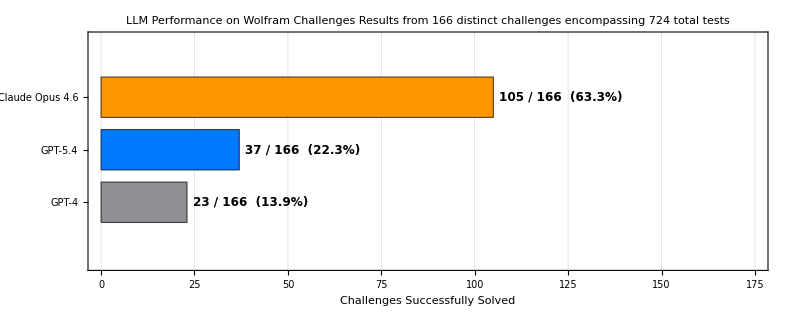
```mathematica
-Graphics-//Rasterize
```

## Final Bar Chart

-Graphics-

## Challenges Extra Data

```mathematica
ResourceFunction["WolframChallengesData"]["Keys"]
```

{ChallengeID,Date,Description,FirstAttemptedByMe,FirstSolvedByMe,LastAttemptedByMe,LastSolvedByMe,Leaderboard,MoreDetails,MyAttemptCount,MySolutionCount,NotebookButton,NotebookHash,Notebooks,ShortTitle,Solved,SolvedByMe,SubmissionCount,TagData,Tags,Title,TitleSlug,Tracks,TrendingScore}

```mathematica
ResourceFunction["WolframChallengesData"]["Keys"->"Tags"]
```

```mathematica
Normal@ResourceFunction["WolframChallengesData"]["Keys"->"Tags"]
```

<|Aliquot Sequence→<|Tags→{Algorithms,Computational Sciences,Mathematics,Sequences}|>,All Parenthetical Expressions→<|Tags→{Algorithms,Arrays,Lists,Permutations,Sequences}|>,Almost Palindromes→<|Tags→{Computational Knowledge,Words and Linguistics}|>,Almost Repeating Primes→<|Tags→{Mathematics,Primes,Sequences}|>,Anagram Words→<|Tags→{Computational Knowledge,Words and Linguistics}|>,Angles of a 3D Triangle→<|Tags→{Mathematics}|>,Antipodal City→<|Tags→{Computational Knowledge}|>,Antipode above or below Sea Level→<|Tags→{Computational Knowledge,Geography}|>,Ascending Sublists→<|Tags→{Algorithms,Arrays,Lists}|>,Average Elevation→<|Tags→{Computational Knowledge,Geography}|>,Babbage Squares→<|Tags→{Words and Linguistics}|>,Balanced Ternary→<|Tags→{Algorithms,Computational Sciences,Mathematics}|>,Base-b Palindromic Numbers→<|Tags→{Lists,Mathematics}|>,Breaking the Caesar Cipher→<|Tags→{Mathematics,Words and Linguistics}|>,Bubble Sort→<|Tags→{Algorithms,Computational Sciences,Lists,Sorting}|>,Butterflied Strings→<|Tags→{Start Here,Strings}|>,Capital Cities Near a Latitude→<|Tags→{Computational Knowledge,Geography}|>,Carry Counting→<|Tags→{Algorithms,Computational Knowledge,Mathematics,Sequences}|>,Cellular Automaton→<|Tags→{Computational Sciences,Computation Knowledge,Mathematics}|>,Cellular Automaton Transients→<|Tags→{Algorithms,Computational Sciences}|>,Color Conversion→<|Tags→{Algorithms,Art,Color}|>,Combine n Ones→<|Tags→{Algorithms}|>,Composite Number→<|Tags→{Mathematics,Number Theory,Primes,Sequences}|>,Constant Digit Sum→<|Tags→{Lists,Mathematics}|>,Counting Lattice Paths→<|Tags→{Mathematics}|>,Counting Twin Prime Pairs→<|Tags→{Mathematics,Primes}|>,Count Palindromic Substrings→<|Tags→{Mathematics,Sequences,Words and Linguistics}|>,Country Chains→<|Tags→{Computational Knowledge,Geography}|>,Count the Number of Squares→<|Tags→{Arrays,Mathematics}|>,Deriffle a List→<|Tags→{Lists}|>,Diagonals of Rule 30→<|Tags→{Cellular Automata,Lists,Sequences}|>,Digital Clock Arithmetic→<|Tags→{Sequences}|>,Digital Root→<|Tags→{Algorithms,Mathematics}|>,Digit Frequency for Pi→<|Tags→{Mathematics,Pi}|>,Discrete Spiral→<|Tags→{Mathematics,Primes,Sequences,Space-Filling Curves,Spiral}|>,Emirps Is Primes Backward→<|Tags→{Primes}|>,Factorial Digit Frequency→<|Tags→{Algorithms,Mathematics}|>,Factorial Zeros→<|Tags→{Mathematics}|>,Factor Trees→<|Tags→{Mathematics,Primes}|>,Farthest Words→<|Tags→{Words and Linguistics}|>,Fewest Number of Coins→<|Tags→{Algorithms,Computational Knowledge,Mathematics}|>,Find Goldbach Partitions→<|Tags→{Mathematics,Primes}|>,Finding Flip Primes→<|Tags→{Mathematics}|>,Five Long Weekends in a Month→<|Tags→{Calendar}|>,Five-Point Conic→<|Tags→{Algorithms,Arrays,Conic Sections,Geometry,Linear Algebra,Lists,Mathematics}|>,Fizz Buzz→<|Tags→{Algorithms,Computational Sciences,Start Here}|>,Flutter→<|Tags→{Algorithms,Start Here}|>,Forbidden Substrings→<|Tags→{Computational Knowledge,Words and Linguistics}|>,Four-Pile Nim→<|Tags→{Algorithms,Computational Knowledge,Game Theory}|>,Four-Point Parabola→<|Tags→{Algorithms,Computational Sciences,Conic Sections,Geometry,Linear Algebra,Lists,Mathematics}|>,Friday the 13ths in a Year→<|Tags→{Computational Knowledge}|>,Getting a Basketball Score→<|Tags→{Mathematics,Numerical Representation of Integers,Start Here}|>,Gray Code→<|Tags→{Computational Knowledge,Mathematics}|>,Grayscale Spectrum→<|Tags→{Colors,Formatting,Graphics,Mathematics}|>,Hash Loop→<|Tags→{Algorithms,Computational Knowledge,Computational Sciences,Cryptography,Cycle,Group,Hash,Loop,Message Digest}|>,How Round Is a Country?→<|Tags→{Computational Knowledge,Geography}|>,Integer Name Lengths→<|Tags→{Sequences,Words and Linguistics}|>,Integers with Given Digit Sums→<|Tags→{Mathematics}|>,Iterated Roman Numeralization→<|Tags→{Computational Knowledge,Sequences}|>,Josephus Problem→<|Tags→{Algorithms,Mathematics,Recreational Mathematics,Sequences}|>,Knight Points→<|Tags→{Arrays,Image Processing,Linear Algebra,Mathematics}|>,Large Integers Mod 2027→<|Tags→{Sequences}|>,Lattice Points in a Sphere→<|Tags→{Algorithms,Geometry,Mathematics,Number Theory,Sequences}|>,Length of the Collatz Sequence→<|Tags→{Algorithms,Mathematics,Sequences}|>,Letter Bank→<|Tags→{Lists,Words and Linguistics}|>,Listify the Elements of a List→<|Tags→{Lists}|>,List Prime Palindromes→<|Tags→{Mathematics,Primes}|>,Longest Graph Cycle→<|Tags→{Graph Theory}|>,Longest Reversed Sequence→<|Tags→{Lists,Sequences}|>,Look and Say Sequence→<|Tags→{Algorithms,Mathematics,Sequences}|>,Magic Squares→<|Tags→{Algorithms,Computational Knowledge,Mathematics}|>,Making Change→<|Tags→{Algorithms,Sequences}|>,Maximal Contiguous Sum →<|Tags→{Lists,Mathematics,Sequences}|>,Maximum Color Distance→<|Tags→{Computational Knowledge,Image Processing}|>,Maximum Overhang→<|Tags→{Architecture,Gravity,Mathematics,Sequences,Series}|>,Maximum Roman Numeral Length→<|Tags→{Mathematics,Start Here}|>,Minimal Cellular Automaton→<|Tags→{Arrays,Cellular Automata,Computational Knowledge,Computational Sciences,Lists,Mathematics,Sequences}|>,Mirror Mirror→<|Tags→{Algorithms,Arrays,Computational Sciences,Geometry,Linear Algebra,Lists,Mathematics,Matrix Transformations}|>,Most Distinct Letters→<|Tags→{Lists,Words and Linguistics}|>,Most-Occurring Weekdays in a Year→<|Tags→{Calendar}|>,Most Roman Numerals→<|Tags→{Computational Knowledge}|>,Most Weekend Birthdays→<|Tags→{Computational Knowledge}|>,Multiples of 3 and 5→<|Tags→{Algorithms,Mathematics,Start Here}|>,Multiplication Table→<|Tags→{Formatting,Mathematics}|>,N-Dimensional Queen Graph→<|Tags→{Mathematics}|>,Nearest Numbers→<|Tags→{Mathematics,Sequences}|>,Next Permutation→<|Tags→{Algorithms,Arrays}|>,Next Term of a Look and Say Sequence→<|Tags→{Computational Knowledge,Mathematics,Sequences}|>,Normal Form of a Plane→<|Tags→{Algorithms,Arrays,Computational Knowledge,Computational Sciences,Geometry,Linear Algebra,Lists,Mathematics,Permutations,Sequences,Symmetry}|>,Number of Vowels→<|Tags→{Lists,Words and Linguistics}|>,Number Triangles→<|Tags→{Lists,Start Here}|>,Odds before Evens→<|Tags→{Algorithms,Arrays,Sequences,Start Here}|>,One-Finger Distance→<|Tags→{Sequences}|>,On the Critical Line→<|Tags→{Algorithms,Complex Numbers,Computational Sciences,Lists,Mathematics,Sequences,Special Functions,Unsolved Problems}|>,Overlapping Sequences→<|Tags→{Algorithms,Computational Sciences,Lists,Mathematics,Sequences}|>,Pairing Compatible Integers→<|Tags→{Algorithms,Computational Knowledge,Mathematics}|>,Pairingfunction→<|Tags→{Algorithms,Sequences,Start Here}|>,Pairs That Sum to 100→<|Tags→{Algorithms,Arrays,Start Here}|>,Palindrome from a Word→<|Tags→{Words and Linguistics}|>,Palindromes→<|Tags→{Computational Knowledge,Words and Linguistics}|>,Palindromic Roman Numerals→<|Tags→{Mathematics,People and History,Words and Linguistics}|>,Pancake Scramble→<|Tags→{Algorithms,Computational Sciences}|>,Pancake Scramble Period→<|Tags→{Algorithms,Mathematics}|>,Partitions of Increasing Length→<|Tags→{Lists}|>,Permutation Count→<|Tags→{Mathematics,Permutations}|>,Permutation Index→<|Tags→{Algorithms,Combinatorics,Computational Sciences,Mathematics,Permutations,Sequences,Sorting}|>,Pig Latin→<|Tags→{Algorithms,Words and Linguistics}|>,Planes in Space→<|Tags→{Algorithms,Arrays,Computational Knowledge,Computational Sciences,Geometry,Linear Algebra,Lists,Mathematics,Permutations,Sequences,Symmetry}|>,Point inside Triangle→<|Tags→{Algorithms,Geometry,Mathematics}|>,Polygon Billiards→<|Tags→{Algorithms,Arrays,Computational Sciences,Geometry,Linear Algebra,Lists,Mathematics,Matrix Transformations}|>,Powerful Digit Frequencies→<|Tags→{Algorithms,Lists}|>,Prime Base→<|Tags→{Algorithms,Lists,Mathematics,Primes,Sequences}|>,Prime Fibonacci Numbers→<|Tags→{Mathematics,Sequences}|>,Prime Gaps→<|Tags→{Algorithms,Arrays,Lists,Mathematics,Primes,Sequences}|>,Prime Palindrome Pi→<|Tags→{Mathematics,Primes}|>,Prime Power Pi→<|Tags→{Mathematics,Primes}|>,Pure Function Maker→<|Tags→{Code as Data,Metaprogramming,Wolfram Language}|>,Pythagorean Primes→<|Tags→{Mathematics,Primes}|>,Quadrilateral Midpoints→<|Tags→{Geometry,Mathematics,Plane Geometry,Polygons}|>,RATS Sequences→<|Tags→{Mathematics,Sequences}|>,Reasonably Close Rectangle→<|Tags→{Approximations,Geometry,Number Theory,Polygons}|>,Remove Identical Neighbors→<|Tags→{Lists}|>,Remove Repeated Characters→<|Tags→{Words and Linguistics}|>,Repeat-Free Ternary Sequences→<|Tags→{Computational Sciences,Mathematics,Sequences}|>,Replicate Characters in a String→<|Tags→{Words and Linguistics}|>,Reverse Each Word→<|Tags→{Words and Linguistics}|>,Rolling Polygon Height→<|Tags→{Mathematics}|>,Roman Numerals versus Decimal→<|Tags→{Computational Knowledge}|>,Roman Substitution Words→<|Tags→{Words and Linguistics}|>,Rotodromes→<|Tags→{Words and Linguistics}|>,Rough Goldbach Splits→<|Tags→{Algorithms,Mathematics,Number Theory,Primes,Unsolved Problems}|>,Separate Ones by Zeros→<|Tags→{Computational Knowledge,Sequences}|>,Sequence Hunt in Pi→<|Tags→{Algorithms,Mathematics,Pi,Sequences}|>,Shortest Word from Some Letters→<|Tags→{Computational Knowledge,Words and Linguistics}|>,Shortest Word Ladder→<|Tags→{Lists,Mathematics,Sequences}|>,Silverman's Sequence→<|Tags→{Mathematics,Sequences}|>,Single-Digit Numbers→<|Tags→{Lists,Sequences}|>,Smallest Word Number→<|Tags→{Words and Linguistics}|>,Small Factors of Large Numbers→<|Tags→{Algorithms,Computational Sciences,Factorization,Mathematics,Primes}|>,Spell with Chemical Elements→<|Tags→{Computational Knowledge,Lists}|>,Squarefree Ternary Sequences→<|Tags→{Computational Sciences,Mathematics,Sequences}|>,Square Root Floor Digits→<|Tags→{Algorithms,Mathematics}|>,Square Root of Two via Pell→<|Tags→{Approximations,Continued Fractions,Mathematics,Sequences}|>,Square Sequences→<|Tags→{Algorithms,Computational Knowledge,Mathematics}|>,Square Sum→<|Tags→{Algorithms,Mathematics,Start Here}|>,Start and End of a Big Number→<|Tags→{Mathematics}|>,Steiner Inellipse→<|Tags→{Complex Numbers,Derivatives,Geometry,Mathematics,Polynomials,Roots,Triangles}|>,Sums to an Integer→<|Tags→{Mathematics}|>,Switch the Case→<|Tags→{Words and Linguistics}|>,Telephone Words→<|Tags→{Algorithms,Computational Knowledge,Words and Linguistics}|>,Testing If Lists Are Shuffled→<|Tags→{Lists}|>,Texas Sharpshooter→<|Tags→{Algorithms,Computational Sciences,Geometry,Mathematics}|>,The Bomb Problem→<|Tags→{Algorithms,Computational Sciences,Geometry,Mathematics}|>,The McNugget Problem→<|Tags→{Algorithms,Number Theory}|>,Three Triangular Numbers→<|Tags→{Mathematics,Number Theory,Sequences}|>,Up and Down Words→<|Tags→{Lists,Strings,Words and Linguistics}|>,Valid Integer Triangle→<|Tags→{Algorithms,Geometry,Triangles}|>,Valid Parentheses→<|Tags→{Words and Linguistics}|>,Vigenère Cipher→<|Tags→{Algorithms,Computational Knowledge,Words and Linguistics}|>,Water in a Barrel→<|Tags→{Area,Circles,Geometry,Mathematics,Volume}|>,Word from Letter Sum→<|Tags→{Words and Linguistics}|>,Words Beginning and Ending with a Given Letter→<|Tags→{Start Here,Words and Linguistics}|>,Words from Words→<|Tags→{Lists,Words and Linguistics}|>,Words with a Given Prefix→<|Tags→{Words and Linguistics}|>,Write in Morse Code→<|Tags→{Start Here,Words and Linguistics}|>,Zigzag Numbers→<|Tags→{Permutations,Sequences}|>|>

```mathematica
descriptions=ResourceFunction["WolframChallengesData"]["Keys"->"Description"]
```